# QBM - Steady state

## Packages and assumptions

```mathematica
(*PacletInstall["https://rulebasedintegration.org/Rubi-4.16.1.0.paclet"]
First[PacletFind["Rubi"]]["Location"]*)
Get["Rubi`"]
$Assumptions={{ω0,T,γ,ωc,λ,ωs,ωR}∈PositiveReals,{t,ω}∈Reals,n∈PositiveIntegers};
```

```mathematica
symplectic[σ_]:=Chop[Select[Module[{Ω=({{0, 1}, {-1, 0}})},Eigenvalues[ⅈ Inverse[Ω].σ]],Re@#>0&][[1]],10^-6]
symplectic::usage="symplectic[σ] gives the sympletic eigenvalues of the covariance matrix σ";

purity[σ_]:=1/(√Det[σ])
purity::usage="purity[σ] gives the purity of the covariance matrix σ";


entropy[σ_]:=(2*symplectic[σ]+1)/2*Log[(2*symplectic[σ]+1)/2]+(2*symplectic[σ]-1)/2*Log[(2*symplectic[σ]-1)/2]
entropy::usage="entropy[σ] gives the von Neumann entropy of a 1-mode Gaussian state, characterised by the covariance matrix σ";
```

## Spectral density and susceptibility

```mathematica
(* Spectral densities *)
JLorentzDrude[ω_,γ_,ωc_]:=2*γ*ωc^2*ω/(ω^2+ωc^2)
JLorentzDrude::usage="JLorentzDrude[ω,γ,ωc] is an ohmic spectral density with a Lorentz-Drude cutoff";

JStructuredLorentzDrude[ω_,γ_,λ_,ωs_]:=(γ*λ^2*ω)/(γ^2*ω^2+(ω^2-ωs^2)^2) 
JStructuredLorentzDrude::usage="JStructuredLorentzDrude[ω,γ,λ,ωs] is an ohmic spectral density with a Structured Lorentz-Drude cutoff. It has a peak around ωs, whose height and width are controlled by λ and γ respectively.";

JsExp[ω_,s_,γ_,ωc_]:=π/2*γ*ω^s*ωc^(1-s)*Exp[-ω/ωc]
JsExp::usage="JsExp[ω,s,γ,ωc] is a spectral density with Ohmicity s and an exponential cutoff";

(* Renormalisation frequency *)

ωR2fromJ[J_]:=2/Pi*Integrate[J[x]/x,{x,0,Infinity}]
ωR2fromJ::usage="ωR2fromJ[J] is the renormalization frequency shift squared, ω_R^2";

(* Imaginary part of Fourier-space susceptibility *)

ImχFTfromJ[ω_,J_]:=J[ω]*HeavisideTheta[ω]-J[-ω]*HeavisideTheta[-ω]
ImχFTfromJ::usage="ImχFTfromJ[J,ω] is the imaginary part of the Fourier transform of the susceptibility for a general spectral density J(ω)";

ImχFTJLorentzDrude[ω_,γ_,ωc_]:=(2 γ ω ωc^2)/(ω^2+ωc^2)
ImχFTJLorentzDrude::usage="ImχFTJLorentzDrude[ω,γ,ωc] is the imaginary part of the Fourier transform of the susceptibility for an ohmic spectral density with a Lorentz-Drude cutoff";

ImχFTJStructuredLorentzDrude[ω_,γ_,λ_,ωs_]:=(γ λ^2 ω)/(γ^2 ω^2+(ωs^2-ω^2)^2)
ImχFTJStructuredLorentzDrude::usage="ImχFTJLorentzDrude[ω,γ,ωc] is the imaginary part of the Fourier transform of the susceptibility for an ohmic spectral density with a structured Lorentz-Drude cutoff";

ImχFTJexps[ω_,s_,γ_,ωc_]:=JsExp[ω,s,γ,ωc]*HeavisideTheta[ω]-JsExp[-ω,s,γ,ωc]*HeavisideTheta[-ω]
ImχFTJexps::usage="ImχFTJexps[ω,s,γ,ωc] is the imaginary part of the Fourier transform of the susceptibility for a spectral density with Ohmicity s and an exponential cutoff";

ImχFTJexp1[ω_,γ_,ωc_]:=1/2 ⅇ^(-ω/ωc) π γ ω HeavisideTheta[ω]-1/2 ⅇ^(ω/ωc) π γ ω HeavisideTheta[-ω]
ImχFTJexp1::usage="ImχFTJexp1[ω,γ,ωc] is the imaginary part of the Fourier transform of the susceptibility for a spectral density with Ohmicity s=1 and an exponential cutoff";


(* Real part of Fourier-space susceptibility *)

ReχFTfromJ[y_,J_]:=1/Pi*Integrate[ImχFTfromJ[x,J]/(x-y),{x,-Infinity,Infinity},PrincipalValue->True,Assumptions->{Element[y,Reals]}] // Normal
ReχFTfromJ::usage="ReχFTfromJ[y,J] is the real part of the Fourier transform of the susceptibility for a general spectral density J(ω) using the Hilbert transform";

ReχFTJLorentzDrude[ω_,γ_,ωc_]:=(2 γ ωc^3)/(ω^2+ωc^2)
ReχFTJLorentzDrude::usage="ReχFTJLorentzDrude[ω,γ,ωc] is the real part of the Fourier transform of the susceptibility for an ohmic spectral density with a Lorentz-Drude cutoff using the Hilbert transform";

ReχFTJStructuredLorentzDrude[ω_,γ_,λ_,ωs_]:=(λ^2 (ωs^2-ω^2))/(γ^2 ω^2+(ωs^2-ω^2)^2)
ReχFTJStructuredLorentzDrude::usage="ImχFTJLorentzDrude[ω,γ,ωc] is the real part of the Fourier transform of the susceptibility for an ohmic spectral density with a structured Lorentz-Drude cutoff";


(*NOTE this only works for s=1,2,3..*)
(*ExpIntegralERecursiveRe[n_,z_]:=-Exp[-z]*Sum[z^k/Pochhammer[1-n,k+1],{k,0,n-2}]-(-z)^(n-1)/((n-1)!)ExpIntegralEi[-z]

ReχFTJexps[ω_,s_,γ_,ωc_]:=1/2 ⅇ^(ω/ωc) γ ωc (ⅇ^(-(2 ω)/ωc) ExpIntegralERecursiveRe[1+s,-ω/ωc]+ExpIntegralERecursiveRe[1+s,ω/ωc]) s!//N*)
ReχFTJexps[ω_,s_,γ_,ωc_]:=1/2 ⅇ^(ω/ωc) γ ωc (ⅇ^(-(2 ω)/ωc) ExpIntegralE[1+s,-ω/ωc]+ExpIntegralE[1+s,ω/ωc]) s!//Re
ReχFTJexps::usage="ReχFTJexps[ω,s,γ,ωc] is the real part of the Fourier transform of the susceptibility for a spectral density with Ohmicity s and an exponential cutoff";

ReχFTJexp1[ω_,γ_ ,ωc_]:= 1/2 γ (2 ωc+ⅇ^(ω/ωc) ω ExpIntegralEi[-ω/ωc]-ⅇ^(-ω/ωc) ω ExpIntegralEi[ω/ωc])
ReχFTJexp1::usage="ReχFTJexp1[ω,γ,ωc] is the real part of the Fourier transform of the susceptibility for a spectral density with Ohmicity s=1 and an exponential cutoff";

(* Fourier-space susceptibility *)

χFTJLorentzDrude[ω_,γ_,ωc_]:=(2 ⅈ γ ω ωc^2)/(ω^2+ωc^2)+(2 γ ωc^3)/(ω^2+ωc^2)
χFTJLorentzDrude::usage="χFTJLorentzDrude[ω,γ,ωc] is the Fourier transform of the susceptibility for an ohmic spectral density with a Lorentz-Drude cutoff";

χFTJStructuredLorentzDrude[ω_,γ_,λ_,ωs_]:=λ^2/(ωs^2-ⅈ*γ*ω-ω^2) 

(*χFTJexps[ω_,s_,γ_,ωc_]:=1/2 ⅇ^(ω/ωc) γ ωc (ⅇ^(-(2 ω)/ωc) Conjugate[N@ExpIntegralE[1+s,-ω/ωc]]+Conjugate[N@ExpIntegralE[1+s,ω/ωc]]) s!*)

χFTJexps[ω_,s_,γ_,ωc_]:=ReχFTJexps[ω,s,γ ,ωc] + ⅈ*ImχFTJexps[ω,s,γ ,ωc]
χFTJexps::usage="χFTJexps[ω,s,γ,ωc] is the Fourier transform of the susceptibility for a spectral density with Ohmicity s and an exponential cutoff";

spectraldensitymsg::bad="The spectral density `1` is not recognised.";


(* Listing the previous results *)


JList[ω_,params_]:=Module[{args=Join[{ω},params]},{JLorentzDrude@@ args,JStructuredLorentzDrude@@ args,JsExp@@ args}]
JList::usage="JList[ω,params] is a list of spectral densities.";

J[ω_,params_,Jindex_]:=JList[ω,params][[Jindex]]
J::usage="J[ω,params,Jindex] chooses a particular spectral density. Jindex=1 gives Lorentz-Drude, Jindex=2 gives Structured Lorentz-Drude, Jindex=3 gives a general ohmicity with exponential cutoff.";


ImχFTList[ω_,params_]:=Module[{args=Join[{ω},params]},{ImχFTJLorentzDrude@@ args,ImχFTJStructuredLorentzDrude@@ args,ImχFTJexps@@ args}]
ImχFTList::usage="ImχFTList[ω,params] is a list of the imaginary part of the Fourier transform of the spectral density.";

ImχFT[ω_,params_,Jindex_]:=ImχFTList[ω,params][[Jindex]]
ImχFT::usage="ImχFT[ω,params,Jindex] chooses a particular imaginary part of the Fourier transform of the spectral density from a list.";
```

## Integrand

Taking the Fourier transform of the Quantum Langevin Equation gives x̃(ω)=α^-1(ω)F̃(ω) where α(ω)= ω_0^2+ω_R^2-ω^2-χ̃(ω)

```mathematica
alphainvJLorentzDrude[ω_,ω0_,γ_,ωc_]:=1/(-ω^2+ω0^2+2 γ ωc-(2 ⅈ γ ωc^2)/(ω+ⅈ ωc))

alphainvJStructuredLorentzDrude[ω_,ω0_,γ_,λ_,ωs_]:=1/(-ω^2+ω0^2+λ^2/ωs^2-λ^2/(ωs^2-ⅈ*γ*ω-ω^2))

alphainvJexps[ω_,ω0_,s_,γ_,ωc_]:=1/(-ω^2+ω0^2+γ ωc Gamma[s]-χFTJexps[ω,s,γ,ωc])

alphainvList[ω_,ω0_,params_]:=Module[{args=Join[{ω,ω0},params]},{alphainvJLorentzDrude@@ args,alphainvJStructuredLorentzDrude@@ args,alphainvJexps@@ args}]

alphainv[ω_,ω0_,params_,Jindex_]:=alphainvList[ω,ω0,params][[Jindex]]

alphainv::usage="alphainv[ω,ω0,params,Jindex] is the function α^-1(ω) for particualar known spectral densities J(ω)";
```

## Numerical steady-state covariance matrices

```mathematica
accGoal=8;
precGoal=10;
workPrec=15;
maxRecur=15;

σ11SteadyState[T_,ω0_,params_,Jindex_]:=NIntegrate[1/Pi*alphainv[ω,ω0,params,Jindex]*alphainv[-ω,ω0,params,Jindex]*Coth[ω/(2*T)]*ImχFT[ω,params,Jindex],{ω,0,Infinity},Exclusions->{ω0},Method->"PrincipalValue",AccuracyGoal->accGoal,PrecisionGoal->precGoal,WorkingPrecision->workPrec,MaxRecursion->maxRecur] // Chop
σ11SteadyState::usage="σ11SteadyState[T,ω0,params,Jindex] is the steady-state xx covariance";

σ22SteadyState[T_,ω0_,params_,Jindex_]:=NIntegrate[1/Pi*ω^2*alphainv[ω,ω0,params,Jindex]*alphainv[-ω,ω0,params,Jindex]*Coth[ω/(2*T)]*ImχFT[ω,params,Jindex],{ω,0,Infinity},Exclusions->{ω0},Method->"PrincipalValue",AccuracyGoal->accGoal,PrecisionGoal->precGoal,WorkingPrecision->workPrec,MaxRecursion->maxRecur] // Chop
σ22SteadyState::usage="σ22SteadyState[T,ω0,params,Jindex] is the steady-state yy covariance";

covarianceMatrixSteadyState[T_,ω0_,params_,Jindex_]:={{σ11SteadyState[T,ω0,params,Jindex],0},{0,σ22SteadyState[T,ω0,params,Jindex]}}
covarianceMatrixSteadyState::usage="covarianceMatrixSteadyState[T,ω0,params,Jindex] is the steady-state covariance matrix";
```

## Analytical covariances

```mathematica
aσ11LorentzDrude[T_,ω0_,γ_,ωc_]:=T/ω0^2-1/π RootSum[8 π^3 T^3+2 π T ω0^2+4 π^2 T^2 ωc+4 π T γ ωc+ω0^2 ωc+24 π^3 T^3 #1+2 π T ω0^2 #1+8 π^2 T^2 ωc #1+4 π T γ ωc #1+24 π^3 T^3 #1^2+4 π^2 T^2 ωc #1^2+8 π^3 T^3 #1^3&,(2 π T PolyGamma[0,-#1]+ωc PolyGamma[0,-#1]+2 π T PolyGamma[0,-#1] #1)/(12 π^2 T^2+ω0^2+4 π T ωc+2 γ ωc+24 π^2 T^2 #1+4 π T ωc #1+12 π^2 T^2 #1^2)&] // Chop
aσ11LorentzDrude::usage="aσ11LorentzDrude[T,ω0,γ,ωc] returns the xx covariance computed analytically for an Ohmic spectral density with a Lorentz-Drude cutoff";


aσ22LorentzDrude[T_,ω0_,γ_,ωc_]:=T-1/π RootSum[8 π^3 T^3+2 π T ω0^2+4 π^2 T^2 ωc+4 π T γ ωc+ω0^2 ωc+24 π^3 T^3 #1+2 π T ω0^2 #1+8 π^2 T^2 ωc #1+4 π T γ ωc #1+24 π^3 T^3 #1^2+4 π^2 T^2 ωc #1^2+8 π^3 T^3 #1^3&,(2 π T ω0^2 PolyGamma[0,-#1]+4 π T γ ωc PolyGamma[0,-#1]+ω0^2 ωc PolyGamma[0,-#1]+2 π T ω0^2 PolyGamma[0,-#1] #1+4 π T γ ωc PolyGamma[0,-#1] #1)/(12 π^2 T^2+ω0^2+4 π T ωc+2 γ ωc+24 π^2 T^2 #1+4 π T ωc #1+12 π^2 T^2 #1^2)&]// Chop
aσ22LorentzDrude::usage="aσ22LorentzDrude[T,ω0,γ,ωc] returns the pp covariance computed analytically for an Ohmic spectral density with a Lorentz-Drude cutoff";

aσ11JStructuredLorentzDrude[T_,ω0_,γ_,λ_,ωs_]:=T/ω0^2-1/π ωs^2 RootSum[4 π^2 T^2 λ^2+2 π T γ λ^2+16 π^4 T^4 ωs^2+8 π^3 T^3 γ ωs^2+4 π^2 T^2 ω0^2 ωs^2+2 π T γ ω0^2 ωs^2+4 π^2 T^2 ωs^4+ω0^2 ωs^4+8 π^2 T^2 λ^2 #1+2 π T γ λ^2 #1+64 π^4 T^4 ωs^2 #1+24 π^3 T^3 γ ωs^2 #1+8 π^2 T^2 ω0^2 ωs^2 #1+2 π T γ ω0^2 ωs^2 #1+8 π^2 T^2 ωs^4 #1+4 π^2 T^2 λ^2 #1^2+96 π^4 T^4 ωs^2 #1^2+24 π^3 T^3 γ ωs^2 #1^2+4 π^2 T^2 ω0^2 ωs^2 #1^2+4 π^2 T^2 ωs^4 #1^2+64 π^4 T^4 ωs^2 #1^3+8 π^3 T^3 γ ωs^2 #1^3+16 π^4 T^4 ωs^2 #1^4&,(4 π^2 T^2 PolyGamma[0,-#1]+2 π T γ PolyGamma[0,-#1]+ωs^2 PolyGamma[0,-#1]+8 π^2 T^2 PolyGamma[0,-#1] #1+2 π T γ PolyGamma[0,-#1] #1+4 π^2 T^2 PolyGamma[0,-#1] #1^2)/(4 π T λ^2+γ λ^2+32 π^3 T^3 ωs^2+12 π^2 T^2 γ ωs^2+4 π T ω0^2 ωs^2+γ ω0^2 ωs^2+4 π T ωs^4+4 π T λ^2 #1+96 π^3 T^3 ωs^2 #1+24 π^2 T^2 γ ωs^2 #1+4 π T ω0^2 ωs^2 #1+4 π T ωs^4 #1+96 π^3 T^3 ωs^2 #1^2+12 π^2 T^2 γ ωs^2 #1^2+32 π^3 T^3 ωs^2 #1^3)&] // Chop
aσ11JStructuredLorentzDrude::usage="aσ11JStructuredLorentzDrude[T,ω0,γ,λ,ωs] returns the xx covariance computed analytically for an Ohmic spectral density with a Structured Lorentz-Drude cutoff";

aσ22JStructuredLorentzDrude[T_,ω0_,γ_,λ_,ωs_]:=T-1/π RootSum[4 π^2 T^2 λ^2+2 π T γ λ^2+16 π^4 T^4 ωs^2+8 π^3 T^3 γ ωs^2+4 π^2 T^2 ω0^2 ωs^2+2 π T γ ω0^2 ωs^2+4 π^2 T^2 ωs^4+ω0^2 ωs^4+8 π^2 T^2 λ^2 #1+2 π T γ λ^2 #1+64 π^4 T^4 ωs^2 #1+24 π^3 T^3 γ ωs^2 #1+8 π^2 T^2 ω0^2 ωs^2 #1+2 π T γ ω0^2 ωs^2 #1+8 π^2 T^2 ωs^4 #1+4 π^2 T^2 λ^2 #1^2+96 π^4 T^4 ωs^2 #1^2+24 π^3 T^3 γ ωs^2 #1^2+4 π^2 T^2 ω0^2 ωs^2 #1^2+4 π^2 T^2 ωs^4 #1^2+64 π^4 T^4 ωs^2 #1^3+8 π^3 T^3 γ ωs^2 #1^3+16 π^4 T^4 ωs^2 #1^4&,(4 π^2 T^2 λ^2 PolyGamma[0,-#1]+2 π T γ λ^2 PolyGamma[0,-#1]+4 π^2 T^2 ω0^2 ωs^2 PolyGamma[0,-#1]+2 π T γ ω0^2 ωs^2 PolyGamma[0,-#1]+ω0^2 ωs^4 PolyGamma[0,-#1]+8 π^2 T^2 λ^2 PolyGamma[0,-#1] #1+2 π T γ λ^2 PolyGamma[0,-#1] #1+8 π^2 T^2 ω0^2 ωs^2 PolyGamma[0,-#1] #1+2 π T γ ω0^2 ωs^2 PolyGamma[0,-#1] #1+4 π^2 T^2 λ^2 PolyGamma[0,-#1] #1^2+4 π^2 T^2 ω0^2 ωs^2 PolyGamma[0,-#1] #1^2)/(4 π T λ^2+γ λ^2+32 π^3 T^3 ωs^2+12 π^2 T^2 γ ωs^2+4 π T ω0^2 ωs^2+γ ω0^2 ωs^2+4 π T ωs^4+4 π T λ^2 #1+96 π^3 T^3 ωs^2 #1+24 π^2 T^2 γ ωs^2 #1+4 π T ω0^2 ωs^2 #1+4 π T ωs^4 #1+96 π^3 T^3 ωs^2 #1^2+12 π^2 T^2 γ ωs^2 #1^2+32 π^3 T^3 ωs^2 #1^3)&]// Chop
aσ22JStructuredLorentzDrude::usage="aσ22JStructuredLorentzDrude[T,ω0,γ,λ,ωs] returns the pp covariance computed analytically for an Ohmic spectral density with a Structured Lorentz-Drude cutoff";

aσ11List[T_,ω0_,params_]:=Module[{args=Join[{T,ω0},params]},{aσ11LorentzDrude@@ args,aσ11JStructuredLorentzDrude@@ args}]
aσ22List[T_,ω0_,params_]:=Module[{args=Join[{T,ω0},params]},{aσ22LorentzDrude@@ args,aσ22JStructuredLorentzDrude@@ args}]

acovarianceMatrix[T_,ω0_,params_,Jindex_]:=({{aσ11List[T,ω0,params][[Jindex]], 0}, {0, aσ22List[T,ω0,params][[Jindex]]}})
acovarianceMatrix::usage="acovarianceMatrix[T,ω0,params,Jindex] returns the covariance matrix computed from the analytical formulas";
```

### Analytical covariances workings

#### Position-position correlation

```mathematica
1/Pi*alphainv[ω,ω0,{γ,λ,ωs},2]*alphainv[-ω,ω0,{γ,λ,ωs},2]*Coth[ω/(2*T)]*ImχFT[ω,{γ,λ,ωs},2]
```

(γ λ^2 ω Coth[ω/(2 T)])/(π (γ^2 ω^2+(-ω^2+ωs^2)^2) (-ω^2+ω0^2+λ^2/ωs^2-λ^2/(-ⅈ γ ω-ω^2+ωs^2)) (-ω^2+ω0^2+λ^2/ωs^2-λ^2/(ⅈ γ ω-ω^2+ωs^2)))

```mathematica
exprxx=(2T γ λ^2 ω^2)/(π (γ^2 ω^2+(-ω^2+ωs^2)^2) (-ω^2+ω0^2+λ^2/ωs^2-λ^2/(-ⅈ γ ω-ω^2+ωs^2)) (-ω^2+ω0^2+λ^2/ωs^2-λ^2/(ⅈ γ ω-ω^2+ωs^2))(ω+ⅈ νn)(ω-ⅈ νn))
```

(2 T γ λ^2 ω^2)/(π (-ⅈ νn+ω) (ⅈ νn+ω) (γ^2 ω^2+(-ω^2+ωs^2)^2) (-ω^2+ω0^2+λ^2/ωs^2-λ^2/(-ⅈ γ ω-ω^2+ωs^2)) (-ω^2+ω0^2+λ^2/ωs^2-λ^2/(ⅈ γ ω-ω^2+ωs^2)))

Rewriting γ^2 ω^2+(-ω^2+ωs^2)^2  as  (-ω^2+ωs^2)^2+γ^2 ω^2= (-ω^2+ωs^2-ⅈ γ ω)(-ω^2+ωs^2+ⅈ γ ω)

```mathematica
h5xx[ω_]=(ω+ⅈ νn)((-ω^2+ω0^2+λ^2/ωs^2)(-ⅈ γ ω-ω^2+ωs^2)-λ^2 ) ;
```

```mathematica
expr2xx=-(2T γ λ^2)/π ω^2*1/(h5xx[ω]*h5xx[-ω])
```

-(2 T γ λ^2 ω^2)/(π (ⅈ νn-ω) (ⅈ νn+ω) (-λ^2+(-ω^2+ω0^2+λ^2/ωs^2) (-ⅈ γ ω-ω^2+ωs^2)) (-λ^2+(-ω^2+ω0^2+λ^2/ωs^2) (ⅈ γ ω-ω^2+ωs^2)))

```mathematica
(*Expressions are equivalent*)
True===FullSimplify[1/Pi*alphainv[ω,ω0,{γ,λ,ωs},2]*alphainv[-ω,ω0,{γ,λ,ωs},2]*Coth[ω/(2*T)]*ImχFT[ω,{γ,λ,ωs},2]==Sum[expr2xx/.νn->2π T n,{n,-Infinity,Infinity}]]
True===FullSimplify[exprxx==expr2xx]
```

True

True

```mathematica
{a0,a1,a2,a3,a4,a5}=Coefficient[(ω+ⅈ νn)((-ω^2+ω0^2+λ^2/ωs^2)(-ⅈ γ ω-ω^2+ωs^2)-λ^2 ) ,ω,#]&/@Range[5,0,-1]
{b0,b1,b2,b3,b4,b5}={0,0,0,(2T γ λ^2)/π,0,0}; (*Gives Subscript[g, 5](ω)=Subscript[b, 3] ω^2*);
```

{1,ⅈ γ+ⅈ νn,-γ νn-ω0^2-λ^2/ωs^2-ωs^2,-ⅈ γ ω0^2-ⅈ νn ω0^2-(ⅈ γ λ^2)/ωs^2-(ⅈ λ^2 νn)/ωs^2-ⅈ νn ωs^2,γ νn ω0^2+(γ λ^2 νn)/ωs^2+ω0^2 ωs^2,ⅈ νn ω0^2 ωs^2}

```mathematica
M5=b0(-a0 a4 a5+a1 a4^2+a2^2 a5-a2 a3 a4)+a0 b1(-a2 a5+a3 a4) +a0 b2( a0 a5-a1 a4)+a0 b3(-a0 a3+a1 a2)+(a0 b4)/a5(-a0 a1 a5+a0 a3^2+a1^2 a4-a1 a2 a3);
Δ5=a0^2 a5^2-2a0 a1 a4 a5-a0 a2 a3 a5+a0 a3^2 a4+a1^2 a4^2+a1 a2^2 a5-a1 a2 a3 a4;
```

Check roots of h are in the upper half complex plane (Im>0)

```mathematica
(*h[z_]=Table[z^n,{n,0,5}].{a0,a1,a2,a3,a4,a5}/.νn->2π T n//FullSimplify
Reduce[h[z]==0,z];
roots=z/.{ToRules[Reduce[h[z]==0,z]]};*)

hNum[z_]=Table[z^n,{n,0,5}].{a0,a1,a2,a3,a4,a5}/.νn->2π T n /.{n->10,T->1,ω0->1,γ->10,λ->3,ωs->10}
rootsNum=z/.{ToRules[Reduce[hNum[z]==0,z]]}//N
```

1+(10 ⅈ+20 ⅈ π) z+(-10109/100-200 π) z^2+(-(109 ⅈ)/10-(10109 ⅈ π)/5) z^3+(100+218 π) z^4+2000 ⅈ π z^5

{0.+0.0159155 ⅈ,-0.999986+0.00454504 ⅈ,-0.086629+0.049955 ⅈ,0.086629+0.049955 ⅈ,0.999986+0.00454504 ⅈ}

```mathematica
(*Checking the formula from Gradshteyn matches*)
Clear[a0,a1,a2,a3,a4,a5,b0,b1,b2,b3,b4]
Δ5mat=({{a1, a3, a5, 0, 0}, {a0, a2, a4, 0, 0}, {0, a1, a3, a5, 0}, {0, a0, a2, a4, 0}, {0, 0, a1, a3, a5}});
M5mat=({{b0, b1, b2, b3, b4}, {a0, a2, a4, 0, 0}, {0, a1, a3, a5, 0}, {0, a0, a2, a4, 0}, {0, 0, a1, a3, a5}});


Det[M5mat]//Simplify;
Det[Δ5mat]//Simplify;

M5=b0(-a0 a4 a5+a1 a4^2+a2^2 a5-a2 a3 a4)+a0 b1(-a2 a5+a3 a4) +a0 b2( a0 a5-a1 a4)+a0 b3(-a0 a3+a1 a2)+(a0 b4)/a5(-a0 a1 a5+a0 a3^2+a1^2 a4-a1 a2 a3);
Δ5=a0^2 a5^2-2a0 a1 a4 a5-a0 a2 a3 a5+a0 a3^2 a4+a1^2 a4^2+a1 a2^2 a5-a1 a2 a3 a4;

True===FullSimplify[Det[M5mat]/-a5==M5]
True===FullSimplify[ Det[Δ5mat]/-a5==Δ5]
True===FullSimplify[Det[M5mat]/Det[Δ5mat]==M5/Δ5]
```

True

True

True

```mathematica
summandxx=ⅈ π M5/(a0 Δ5)/.νn->2π T n//FullSimplify
```

(2 T ωs^2 (2 n π T (2 n π T+γ)+ωs^2))/(2 n π T (2 n π T+γ) λ^2+2 n π T (2 n π T+γ) (4 n^2 π^2 T^2+ω0^2) ωs^2+(4 n^2 π^2 T^2+ω0^2) ωs^4)

```mathematica
limxx=summandxx /.n->0//FullSimplify
```

(2 T)/ω0^2

Check for n=0

```mathematica
exprxxn0=(2 T γ λ^2)/(π  (-λ^2+(-ω^2+ω0^2+λ^2/ωs^2) (-ⅈ γ ω-ω^2+ωs^2)) (-λ^2+(-ω^2+ω0^2+λ^2/ωs^2) (ⅈ γ ω-ω^2+ωs^2)))
```

(2 T γ λ^2)/(π (-λ^2+(-ω^2+ω0^2+λ^2/ωs^2) (-ⅈ γ ω-ω^2+ωs^2)) (-λ^2+(-ω^2+ω0^2+λ^2/ωs^2) (ⅈ γ ω-ω^2+ωs^2)))

```mathematica
h4[ω_]=((-ω^2+ω0^2+λ^2/ωs^2)(-ⅈ γ ω-ω^2+ωs^2)-λ^2 ) ;
```

```mathematica
expr2xxn0=(2T γ λ^2)/π*1/(h4[ω]*h4[-ω])
```

(2 T γ λ^2)/(π (-λ^2+(-ω^2+ω0^2+λ^2/ωs^2) (-ⅈ γ ω-ω^2+ωs^2)) (-λ^2+(-ω^2+ω0^2+λ^2/ωs^2) (ⅈ γ ω-ω^2+ωs^2)))

```mathematica
True===FullSimplify[(exprxx /. νn->0)==expr2xxn0]
```

True

```mathematica
{a0,a1,a2,a3,a4}=Coefficient[((-ω^2+ω0^2+λ^2/ωs^2)(-ⅈ γ ω-ω^2+ωs^2)-λ^2 ) ,ω,#]&/@Range[4,0,-1]
{b0,b1,b2,b3,b4}={0,0,0,(2T γ λ^2)/π,0};
```

{1,ⅈ γ,-ω0^2-λ^2/ωs^2-ωs^2,-ⅈ γ ω0^2-(ⅈ γ λ^2)/ωs^2,ω0^2 ωs^2}

```mathematica
-ⅈ π(b0(-a1 a4+a2 a3)-a0 a3 b1 +a0 a1 b2+(a0 b3)/a4(a0 a3-a1 a2))/(a0(a0 a3^2+a1^2 a4-a1 a2 a3))//FullSimplify
```

(2 T)/ω0^2

```mathematica
sumxx=Sum[summandxx ,{n,1,∞}];
```

```mathematica
Simplify[2*sumxx+limxx]/2//Cancel//Simplify (*Factor of 1/2 as integral limit is due to different integral limits*)
```

T/ω0^2-1/π ωs^2 RootSum[4 π^2 T^2 λ^2+2 π T γ λ^2+16 π^4 T^4 ωs^2+8 π^3 T^3 γ ωs^2+4 π^2 T^2 ω0^2 ωs^2+2 π T γ ω0^2 ωs^2+4 π^2 T^2 ωs^4+ω0^2 ωs^4+8 π^2 T^2 λ^2 #1+2 π T γ λ^2 #1+64 π^4 T^4 ωs^2 #1+24 π^3 T^3 γ ωs^2 #1+8 π^2 T^2 ω0^2 ωs^2 #1+2 π T γ ω0^2 ωs^2 #1+8 π^2 T^2 ωs^4 #1+4 π^2 T^2 λ^2 #1^2+96 π^4 T^4 ωs^2 #1^2+24 π^3 T^3 γ ωs^2 #1^2+4 π^2 T^2 ω0^2 ωs^2 #1^2+4 π^2 T^2 ωs^4 #1^2+64 π^4 T^4 ωs^2 #1^3+8 π^3 T^3 γ ωs^2 #1^3+16 π^4 T^4 ωs^2 #1^4&,(4 π^2 T^2 PolyGamma[0,-#1]+2 π T γ PolyGamma[0,-#1]+ωs^2 PolyGamma[0,-#1]+8 π^2 T^2 PolyGamma[0,-#1] #1+2 π T γ PolyGamma[0,-#1] #1+4 π^2 T^2 PolyGamma[0,-#1] #1^2)/(4 π T λ^2+γ λ^2+32 π^3 T^3 ωs^2+12 π^2 T^2 γ ωs^2+4 π T ω0^2 ωs^2+γ ω0^2 ωs^2+4 π T ωs^4+4 π T λ^2 #1+96 π^3 T^3 ωs^2 #1+24 π^2 T^2 γ ωs^2 #1+4 π T ω0^2 ωs^2 #1+4 π T ωs^4 #1+96 π^3 T^3 ωs^2 #1^2+12 π^2 T^2 γ ωs^2 #1^2+32 π^3 T^3 ωs^2 #1^3)&]

```mathematica
FullSimplify[Expand[4 π^2 T^2 λ^2+2 π T γ λ^2+16 π^4 T^4 ωs^2+8 π^3 T^3 γ ωs^2+4 π^2 T^2 ω0^2 ωs^2+2 π T γ ω0^2 ωs^2+4 π^2 T^2 ωs^4+ω0^2 ωs^4+8 π^2 T^2 λ^2 #1+2 π T γ λ^2 #1+64 π^4 T^4 ωs^2 #1+24 π^3 T^3 γ ωs^2 #1+8 π^2 T^2 ω0^2 ωs^2 #1+2 π T γ ω0^2 ωs^2 #1+8 π^2 T^2 ωs^4 #1+4 π^2 T^2 λ^2 #1^2+96 π^4 T^4 ωs^2 #1^2+24 π^3 T^3 γ ωs^2 #1^2+4 π^2 T^2 ω0^2 ωs^2 #1^2+4 π^2 T^2 ωs^4 #1^2+64 π^4 T^4 ωs^2 #1^3+8 π^3 T^3 γ ωs^2 #1^3+16 π^4 T^4 ωs^2 #1^4&[d]]]  //. {π T -> Subscript[ν, 1]/2,(π T)^p_ :> Subscript[ν, p]/2^p}
```

ω0^2 ωs^4+(1+d) γ (λ^2+ω0^2 ωs^2) ν_1+(1+d)^2 (λ^2+ω0^2 ωs^2+ωs^4) ν_2+(1+d)^3 γ ωs^2 ν_3+(1+d)^4 ωs^2 ν_4

```mathematica
FullSimplify[(4 π^2 T^2 +2 π T γ +ωs^2+8 π^2 T^2 #1+2 π T γ#1+4 π^2 T^2 #1^2)/(4 π T λ^2+γ λ^2+32 π^3 T^3 ωs^2+12 π^2 T^2 γ ωs^2+4 π T ω0^2 ωs^2+γ ω0^2 ωs^2+4 π T ωs^4+4 π T λ^2 #1+96 π^3 T^3 ωs^2 #1+24 π^2 T^2 γ ωs^2 #1+4 π T ω0^2 ωs^2 #1+4 π T ωs^4 #1+96 π^3 T^3 ωs^2 #1^2+12 π^2 T^2 γ ωs^2 #1^2+32 π^3 T^3 ωs^2 #1^3)&[Subscript[d, m]]] //. {π T -> Subscript[ν, 1]/2,(π T)^p_ :> Subscript[ν, p]/2^p}
```

(ωs^2+ν_1 (γ+ν_1)+d_m ν_1 (γ+2 ν_1+d_m ν_1))/(2 ωs^4 ν_1+λ^2 (γ+2 ν_1)+2 d_m ν_1 (λ^2+ωs^2 (ω0^2+ωs^2+3 ν_1 (γ+2 ν_1))+1/2 ωs^2 d_m ν_1 (4 d_m ν_1+3 (γ+4 ν_1)))+ωs^2 (ω0^2 (γ+2 ν_1)+(3 γ+4 ν_1) ν_2))

This means that <x^2> = T/ω_0^2-2∑_(m=1)^4 c_m ψ(-d_m)  where d_m are the 4 solutions to 
ω0^2 ωs^4+(1+d) γ (λ^2+ω0^2 ωs^2) ν_1+(1+d)^2 (λ^2+ω0^2 ωs^2+ωs^4) ν_2+(1+d)^3 γ ωs^2 ν_3+(1+d)^4 ωs^2 ν_4=0  and c_m=ωs^2/(2 π)(ωs^2+ν_1 (γ+ν_1)+d_m ν_1 (γ+2 ν_1+d_m ν_1))/(2 ωs^4 ν_1+λ^2 (γ+2 ν_1)+2 d_m ν_1 (λ^2+ωs^2 (ω0^2+ωs^2+3 ν_1 (γ+2 ν_1))+1/2 ωs^2 d_m ν_1 (4 d_m ν_1+3 (γ+4 ν_1)))+ωs^2 (ω0^2 (γ+2 ν_1)+(3 γ+4 ν_1) ν_2))

#### Position-momentum correlation

```mathematica
1/Pi*-ⅈ ω*alphainv[ω,ω0,{γ,λ,ωs},2]*alphainv[-ω,ω0,{γ,λ,ωs},2]*Coth[ω/(2*T)]*ImχFT[ω,{γ,λ,ωs},2]
```

-(ⅈ γ λ^2 ω^2 Coth[ω/(2 T)])/(π (γ^2 ω^2+(-ω^2+ωs^2)^2) (-ω^2+ω0^2+λ^2/ωs^2-λ^2/(-ⅈ γ ω-ω^2+ωs^2)) (-ω^2+ω0^2+λ^2/ωs^2-λ^2/(ⅈ γ ω-ω^2+ωs^2)))

```mathematica
exprxp=(-2ⅈ T γ λ^2 ω^3)/(π (γ^2 ω^2+(-ω^2+ωs^2)^2) (-ω^2+ω0^2+λ^2/ωs^2-λ^2/(-ⅈ γ ω-ω^2+ωs^2)) (-ω^2+ω0^2+λ^2/ωs^2-λ^2/(ⅈ γ ω-ω^2+ωs^2))(ω+ⅈ νn)(ω-ⅈ νn))
```

-(2 ⅈ T γ λ^2 ω^3)/(π (-ⅈ νn+ω) (ⅈ νn+ω) (γ^2 ω^2+(-ω^2+ωs^2)^2) (-ω^2+ω0^2+λ^2/ωs^2-λ^2/(-ⅈ γ ω-ω^2+ωs^2)) (-ω^2+ω0^2+λ^2/ωs^2-λ^2/(ⅈ γ ω-ω^2+ωs^2)))

Rewriting γ^2 ω^2+(-ω^2+ωs^2)^2  as  (-ω^2+ωs^2)^2+γ^2 ω^2= (-ω^2+ωs^2-ⅈ γ ω)(-ω^2+ωs^2+ⅈ γ ω)

```mathematica
h5[ω_]=(ω+ⅈ νn)((-ω^2+ω0^2+λ^2/ωs^2)(-ⅈ γ ω-ω^2+ωs^2)-λ^2 ) ;
```

```mathematica
expr2xp=(2ⅈ T γ λ^2)/π ω^3*1/(h5[ω]*h5[-ω])
```

(2 ⅈ T γ λ^2 ω^3)/(π (ⅈ νn-ω) (ⅈ νn+ω) (-λ^2+(-ω^2+ω0^2+λ^2/ωs^2) (-ⅈ γ ω-ω^2+ωs^2)) (-λ^2+(-ω^2+ω0^2+λ^2/ωs^2) (ⅈ γ ω-ω^2+ωs^2)))

```mathematica
True===FullSimplify[exprxp==expr2xp] (*Expressions are equivalent*)
```

True

For  T → ∞ , so the coth odd function tends to 1 - therefore getting a non-zero result.

```mathematica
h4[ω_]=(-ω^2+ω0^2+λ^2/ωs^2)(-ⅈ γ ω-ω^2+ωs^2)-λ^2 ;
```

```mathematica
expr3xp=-(ⅈ γ λ^2)/π ω^2*1/(h4[ω]*h4[-ω])
```

-(ⅈ γ λ^2 ω^2)/(π (-λ^2+(-ω^2+ω0^2+λ^2/ωs^2) (-ⅈ γ ω-ω^2+ωs^2)) (-λ^2+(-ω^2+ω0^2+λ^2/ωs^2) (ⅈ γ ω-ω^2+ωs^2)))

```mathematica
{a0,a1,a2,a3,a4}=Coefficient[((-ω^2+ω0^2+λ^2/ωs^2)(-ⅈ γ ω-ω^2+ωs^2)-λ^2 ) ,ω,#]&/@Range[4,0,-1]
{b0,b1,b2,b3,b4}={0,0,(ⅈ γ λ^2)/π,0,0}; (*Gives Subscript[g, 4](ω)=Subscript[b, 2] ω^2*);
```

{1,ⅈ γ,-ω0^2-λ^2/ωs^2-ωs^2,-ⅈ γ ω0^2-(ⅈ γ λ^2)/ωs^2,ω0^2 ωs^2}

```mathematica
-ⅈ/2 π(b0(-a1 a4+a2 a3)-a0 a3 b1 +a0 a1 b2+(a0 b3)/a4(a0 a3-a1 a2))/(a0(a0 a3^2+a1^2 a4-a1 a2 a3))//FullSimplify (*Factor of 1/2 as integral limit is due to different integral limits*)
```

ⅈ/2

However since h_5(ω)h_5(-ω) is an even function, and ω^3 is odd, the integral from -∞ to ∞ would be 0 - as expected.

Luis’ method assumes T → ∞ first, so the coth odd function tends to 1 - therefore getting a non-zero result.

```mathematica
$Assumptions={{ω0,γ,ωc,T}∈Reals,0<ω0<ωc,γ>0,T>0};
```

```mathematica
-ⅈ ω integrand[ω,ω0,γ,ωc,T]
```

-(ⅈ γ ω^2 (1+Coth[ω/(2 T)]))/(π (1+ω^2/ωc^2) (-ω^2+ω0^2+2 γ ωc-(2 γ ωc^2)/(-ⅈ ω+ωc)) (-ω^2+ω0^2+2 γ ωc-(2 γ ωc^2)/(ⅈ ω+ωc)))

```mathematica
(ⅈ(γ ωc^2)/π ω^2)/(((-ω^2+ω0^2+2 γ ωc)(ωc-ⅈ ω)-2 γ ωc^2)((-ω^2+ω0^2+2 γ ωc)(ωc+ⅈ ω)-2 γ ωc^2))
```

```mathematica
{a0,a1,a2,a3}=Coefficient[((-ω^2+ω0^2+2 γ ωc)(ωc+ⅈ ω)-2 γ ωc^2),ω,#]&/@Range[3,0,-1]
{b0,b1,b2,b3}={0,ⅈ(γ ωc^2)/π,0,0};
```

{-ⅈ,-ωc,ⅈ ω0^2+2 ⅈ γ ωc,ω0^2 ωc}

```mathematica
ⅈ π(-a2 b0+a0 b1-(a0 a1 b2)/a3)/(a0(a0 a3-a1 a2))//FullSimplify
```

ⅈ/2

#### Momentum-momentum correlation

```mathematica
1/Pi*ω^2*alphainv[ω,ω0,{γ,λ,ωs},2]*alphainv[-ω,ω0,{γ,λ,ωs},2]*Coth[ω/(2*T)]*ImχFT[ω,{γ,λ,ωs},2]
```

(γ λ^2 ω^3 Coth[ω/(2 T)])/(π (γ^2 ω^2+(-ω^2+ωs^2)^2) (-ω^2+ω0^2+λ^2/ωs^2-λ^2/(-ⅈ γ ω-ω^2+ωs^2)) (-ω^2+ω0^2+λ^2/ωs^2-λ^2/(ⅈ γ ω-ω^2+ωs^2)))

```mathematica
exprpp=(2T γ λ^2 ω^4)/(π (γ^2 ω^2+(-ω^2+ωs^2)^2) (-ω^2+ω0^2+λ^2/ωs^2-λ^2/(-ⅈ γ ω-ω^2+ωs^2)) (-ω^2+ω0^2+λ^2/ωs^2-λ^2/(ⅈ γ ω-ω^2+ωs^2))(ω+ⅈ νn)(ω-ⅈ νn))
```

(2 T γ λ^2 ω^4)/(π (-ⅈ νn+ω) (ⅈ νn+ω) (γ^2 ω^2+(-ω^2+ωs^2)^2) (-ω^2+ω0^2+λ^2/ωs^2-λ^2/(-ⅈ γ ω-ω^2+ωs^2)) (-ω^2+ω0^2+λ^2/ωs^2-λ^2/(ⅈ γ ω-ω^2+ωs^2)))

Rewriting γ^2 ω^2+(-ω^2+ωs^2)^2  as  (-ω^2+ωs^2)^2+γ^2 ω^2= (-ω^2+ωs^2-ⅈ γ ω)(-ω^2+ωs^2+ⅈ γ ω)

```mathematica
h5pp[ω_]=(ω+ⅈ νn)((-ω^2+ω0^2+λ^2/ωs^2)(-ⅈ γ ω-ω^2+ωs^2)-λ^2 ) ;
```

```mathematica
expr2pp=-(2T γ λ^2)/π ω^4*1/(h5pp[ω]*h5pp[-ω])
```

-(2 T γ λ^2 ω^4)/(π (ⅈ νn-ω) (ⅈ νn+ω) (-λ^2+(-ω^2+ω0^2+λ^2/ωs^2) (-ⅈ γ ω-ω^2+ωs^2)) (-λ^2+(-ω^2+ω0^2+λ^2/ωs^2) (ⅈ γ ω-ω^2+ωs^2)))

```mathematica
True===FullSimplify[exprpp==expr2pp] (*Expressions are equivalent*)
```

True

```mathematica
{a0,a1,a2,a3,a4,a5}=Coefficient[(ω+ⅈ νn)((-ω^2+ω0^2+λ^2/ωs^2)(-ⅈ γ ω-ω^2+ωs^2)-λ^2 ) ,ω,#]&/@Range[5,0,-1]
{b0,b1,b2,b3,b4,b5}={0,0,(2T γ λ^2)/π,0,0,0}; 
(*Gives Subscript[g, 5](ω)=Subscript[b, 2] ω^4*)
```

{1,ⅈ γ+ⅈ νn,-γ νn-ω0^2-λ^2/ωs^2-ωs^2,-ⅈ γ ω0^2-ⅈ νn ω0^2-(ⅈ γ λ^2)/ωs^2-(ⅈ λ^2 νn)/ωs^2-ⅈ νn ωs^2,γ νn ω0^2+(γ λ^2 νn)/ωs^2+ω0^2 ωs^2,ⅈ νn ω0^2 ωs^2}

```mathematica
M5=b0(-a0 a4 a5+a1 a4^2+a2^2 a5-a2 a3 a4)+a0 b1(-a2 a5+a3 a4) +a0 b2( a0 a5-a1 a4)+a0 b3(-a0 a3+a1 a2)+(a0 b4)/a5(-a0 a1 a5+a0 a3^2+a1^2 a4-a1 a2 a3);
Δ5=a0^2 a5^2-2a0 a1 a4 a5-a0 a2 a3 a5+a0 a3^2 a4+a1^2 a4^2+a1 a2^2 a5-a1 a2 a3 a4;
```

```mathematica
summandpp=ⅈ π M5/(a0 Δ5)/.νn->2π T n//FullSimplify
```

(2 T (2 n π T (2 n π T+γ) λ^2+2 n π T (2 n π T+γ) ω0^2 ωs^2+ω0^2 ωs^4))/(2 n π T (2 n π T+γ) λ^2+2 n π T (2 n π T+γ) (4 n^2 π^2 T^2+ω0^2) ωs^2+(4 n^2 π^2 T^2+ω0^2) ωs^4)

```mathematica
limpp=Limit[summandpp,n->0]//FullSimplify
```

2 T

Check for n=0

```mathematica
exprppn0=(2 T γ λ^2 ω^2)/(π  (-λ^2+(-ω^2+ω0^2+λ^2/ωs^2) (-ⅈ γ ω-ω^2+ωs^2)) (-λ^2+(-ω^2+ω0^2+λ^2/ωs^2) (ⅈ γ ω-ω^2+ωs^2)))
```

(2 T γ λ^2 ω^2)/(π (-λ^2+(-ω^2+ω0^2+λ^2/ωs^2) (-ⅈ γ ω-ω^2+ωs^2)) (-λ^2+(-ω^2+ω0^2+λ^2/ωs^2) (ⅈ γ ω-ω^2+ωs^2)))

```mathematica
h4[ω_]=((-ω^2+ω0^2+λ^2/ωs^2)(-ⅈ γ ω-ω^2+ωs^2)-λ^2 ) ;
```

```mathematica
expr2ppn0=(2T γ λ^2)/π ω^2*1/(h4[ω]*h4[-ω])
```

(2 T γ λ^2 ω^2)/(π (-λ^2+(-ω^2+ω0^2+λ^2/ωs^2) (-ⅈ γ ω-ω^2+ωs^2)) (-λ^2+(-ω^2+ω0^2+λ^2/ωs^2) (ⅈ γ ω-ω^2+ωs^2)))

```mathematica
True===FullSimplify[(exprpp /. νn->0)==expr2ppn0]
```

True

```mathematica
{a0,a1,a2,a3,a4}=Coefficient[((-ω^2+ω0^2+λ^2/ωs^2)(-ⅈ γ ω-ω^2+ωs^2)-λ^2 ) ,ω,#]&/@Range[4,0,-1]
{b0,b1,b2,b3,b4}={0,0,(2T γ λ^2)/π,0,0};
```

{1,ⅈ γ,-ω0^2-λ^2/ωs^2-ωs^2,-ⅈ γ ω0^2-(ⅈ γ λ^2)/ωs^2,ω0^2 ωs^2}

```mathematica
-ⅈ π(b0(-a1 a4+a2 a3)-a0 a3 b1 +a0 a1 b2+(a0 b3)/a4(a0 a3-a1 a2))/(a0(a0 a3^2+a1^2 a4-a1 a2 a3))//FullSimplify
```

2 T

```mathematica
sumpp=Sum[summandpp ,{n,1,∞}];
```

```mathematica
Simplify[2*sumpp+limpp]/2//Cancel//Simplify(*Factor of 1/2 as integral limit is due to integral limits*)
```

T-1/π RootSum[4 π^2 T^2 λ^2+2 π T γ λ^2+16 π^4 T^4 ωs^2+8 π^3 T^3 γ ωs^2+4 π^2 T^2 ω0^2 ωs^2+2 π T γ ω0^2 ωs^2+4 π^2 T^2 ωs^4+ω0^2 ωs^4+8 π^2 T^2 λ^2 #1+2 π T γ λ^2 #1+64 π^4 T^4 ωs^2 #1+24 π^3 T^3 γ ωs^2 #1+8 π^2 T^2 ω0^2 ωs^2 #1+2 π T γ ω0^2 ωs^2 #1+8 π^2 T^2 ωs^4 #1+4 π^2 T^2 λ^2 #1^2+96 π^4 T^4 ωs^2 #1^2+24 π^3 T^3 γ ωs^2 #1^2+4 π^2 T^2 ω0^2 ωs^2 #1^2+4 π^2 T^2 ωs^4 #1^2+64 π^4 T^4 ωs^2 #1^3+8 π^3 T^3 γ ωs^2 #1^3+16 π^4 T^4 ωs^2 #1^4&,(4 π^2 T^2 λ^2 PolyGamma[0,-#1]+2 π T γ λ^2 PolyGamma[0,-#1]+4 π^2 T^2 ω0^2 ωs^2 PolyGamma[0,-#1]+2 π T γ ω0^2 ωs^2 PolyGamma[0,-#1]+ω0^2 ωs^4 PolyGamma[0,-#1]+8 π^2 T^2 λ^2 PolyGamma[0,-#1] #1+2 π T γ λ^2 PolyGamma[0,-#1] #1+8 π^2 T^2 ω0^2 ωs^2 PolyGamma[0,-#1] #1+2 π T γ ω0^2 ωs^2 PolyGamma[0,-#1] #1+4 π^2 T^2 λ^2 PolyGamma[0,-#1] #1^2+4 π^2 T^2 ω0^2 ωs^2 PolyGamma[0,-#1] #1^2)/(4 π T λ^2+γ λ^2+32 π^3 T^3 ωs^2+12 π^2 T^2 γ ωs^2+4 π T ω0^2 ωs^2+γ ω0^2 ωs^2+4 π T ωs^4+4 π T λ^2 #1+96 π^3 T^3 ωs^2 #1+24 π^2 T^2 γ ωs^2 #1+4 π T ω0^2 ωs^2 #1+4 π T ωs^4 #1+96 π^3 T^3 ωs^2 #1^2+12 π^2 T^2 γ ωs^2 #1^2+32 π^3 T^3 ωs^2 #1^3)&]

```mathematica
FullSimplify[Expand[4 π^2 T^2 λ^2+2 π T γ λ^2+16 π^4 T^4 ωs^2+8 π^3 T^3 γ ωs^2+4 π^2 T^2 ω0^2 ωs^2+2 π T γ ω0^2 ωs^2+4 π^2 T^2 ωs^4+ω0^2 ωs^4+8 π^2 T^2 λ^2 #1+2 π T γ λ^2 #1+64 π^4 T^4 ωs^2 #1+24 π^3 T^3 γ ωs^2 #1+8 π^2 T^2 ω0^2 ωs^2 #1+2 π T γ ω0^2 ωs^2 #1+8 π^2 T^2 ωs^4 #1+4 π^2 T^2 λ^2 #1^2+96 π^4 T^4 ωs^2 #1^2+24 π^3 T^3 γ ωs^2 #1^2+4 π^2 T^2 ω0^2 ωs^2 #1^2+4 π^2 T^2 ωs^4 #1^2+64 π^4 T^4 ωs^2 #1^3+8 π^3 T^3 γ ωs^2 #1^3+16 π^4 T^4 ωs^2 #1^4&[d]]]  //. {π T -> Subscript[ν, 1]/2,(π T)^p_ :> Subscript[ν, p]/2^p}
```

ω0^2 ωs^4+(1+d) γ (λ^2+ω0^2 ωs^2) ν_1+(1+d)^2 (λ^2+ω0^2 ωs^2+ωs^4) ν_2+(1+d)^3 γ ωs^2 ν_3+(1+d)^4 ωs^2 ν_4

```mathematica
FullSimplify[(4 π^2 T^2 λ^2 +2 π T γ λ^2+4 π^2 T^2 ω0^2 ωs^2+2 π T γ ω0^2 ωs^2+ω0^2 ωs^4+8 π^2 T^2 λ^2  #1+2 π T γ λ^2 #1+8 π^2 T^2 ω0^2 ωs^2  #1+2 π T γ ω0^2 ωs^2 #1+4 π^2 T^2 λ^2 #1^2+4 π^2 T^2 ω0^2 ωs^2 #1^2)/(4 π T λ^2+γ λ^2+32 π^3 T^3 ωs^2+12 π^2 T^2 γ ωs^2+4 π T ω0^2 ωs^2+γ ω0^2 ωs^2+4 π T ωs^4+4 π T λ^2 #1+96 π^3 T^3 ωs^2 #1+24 π^2 T^2 γ ωs^2 #1+4 π T ω0^2 ωs^2 #1+4 π T ωs^4 #1+96 π^3 T^3 ωs^2 #1^2+12 π^2 T^2 γ ωs^2 #1^2+32 π^3 T^3 ωs^2 #1^3)&[Subscript[d, m]]] //. {π T -> Subscript[ν, 1]/2,(π T)^p_ :> Subscript[ν, p]/2^p}
```

(ω0^2 ωs^4+λ^2 ν_1 (γ+ν_1)+ω0^2 ωs^2 ν_1 (γ+ν_1)+(λ^2+ω0^2 ωs^2) d_m ν_1 (γ+2 ν_1+d_m ν_1))/(2 ωs^4 ν_1+λ^2 (γ+2 ν_1)+2 d_m ν_1 (λ^2+ωs^2 (ω0^2+ωs^2+3 ν_1 (γ+2 ν_1))+1/2 ωs^2 d_m ν_1 (4 d_m ν_1+3 (γ+4 ν_1)))+ωs^2 (ω0^2 (γ+2 ν_1)+(3 γ+4 ν_1) ν_2))

This means that <p^2> = T/ω_0^2-2∑_(m=1)^4 c_m'ψ(-d_m)  where d_m are the 4 solutions to ω0^2 ωs^4+(1+d) γ (λ^2+ω0^2 ωs^2) ν_1+(1+d)^2 (λ^2+ω0^2 ωs^2+ωs^4) ν_2+(1+d)^3 γ ωs^2 ν_3+(1+d)^4 ωs^2 ν_4=0  and c_m'=ωs^2/(2 π)(ω0^2 ωs^4+λ^2 ν_1 (γ+ν_1)+ω0^2 ωs^2 ν_1 (γ+ν_1)+(λ^2+ω0^2 ωs^2) d_m ν_1 (γ+2 ν_1+d_m ν_1))/(2 ωs^4 ν_1+λ^2 (γ+2 ν_1)+2 d_m ν_1 (λ^2+ωs^2 (ω0^2+ωs^2+3 ν_1 (γ+2 ν_1))+1/2 ωs^2 d_m ν_1 (4 d_m ν_1+3 (γ+4 ν_1)))+ωs^2 (ω0^2 (γ+2 ν_1)+(3 γ+4 ν_1) ν_2))

## Quantum Fisher information

```mathematica
(*Fidelity[σ1_,x1_,p1_,σ2_,x2_,p2_]:=Module[{Δ=Det[σ1+σ2],Λ=(Det[σ1]-1)*(Det[σ2]-1)},2*(Sqrt[Δ+Λ]-Sqrt[Λ])^-1*Exp[-({x1-x2, p1-p2}.(σ1+σ2).Transpose[{x1-x2,p1-p2}]
(a c+b e) g+(a d+b f) h)]]
Fidelity::usage="Fidelity[σ1,σ2] is the Uhlmann fidelity between two single-mode Gaussian states with covariance matrices σ_1 and σ_2";*)

Fidelity[σ1_,σ2_]:=Module[{Δ=Det[σ1+σ2],Λ=(Det[σ1]-1)*(Det[σ2]-1)},2*(Sqrt[Δ+Λ]-Sqrt[Λ])^-1]
Fidelity::usage="Fidelity[σ1,σ2] is the Uhlmann fidelity between two single-mode Gaussian states with covariance matrices σ_1 and σ_2";


quantumFisherInfo[T_,ω0_,params_,Jindex_]:=Module[{cov,fidplus2,fidplus1,fidminus1,fidminus2,h},h=10^-3;cov=covarianceMatrixSteadyState[T,ω0,params,Jindex];{fidplus2,fidplus1,fidminus1,fidminus2}={Fidelity[2cov,2covarianceMatrixSteadyState[T+2h,ω0,params,Jindex]],Fidelity[2cov,2covarianceMatrixSteadyState[T+h,ω0,params,Jindex]],Fidelity[2cov,2covarianceMatrixSteadyState[T-h,ω0,params,Jindex]],Fidelity[2cov,2covarianceMatrixSteadyState[T-2h,ω0,params,Jindex]]};-2(-fidplus2+16fidplus1-30+16fidminus1-fidminus2)/(12 h^2)]
quantumFisherInfo::usage="quantumFisherInfo[T,ω0,params,Jindex] is the quantum Fisher information, calculated using a finite difference approximation with error of order ~h^4";
quantumFisherEq[ω_,T_]:=ω^2/(4*T^4)*Csch[ω/(2*T)]^2
quantumFisherEq::usage="quantumFisherInfo[ω_,T_] is the quantum Fisher information for a single-mode equilibrium thermometer";

analyticQuantumFisherInfo[T_,ω0_,params_,Jindex_,h_:10^-3]:=Module[
{σT,uip2,uip1,uim1,uim2},
σT=acovarianceMatrix[T,ω0,params,Jindex];
{uip2,uip1,uim1,uim2}={Fidelity[2σT,2acovarianceMatrix[T+2h,ω0,params,Jindex]],Fidelity[2σT,2acovarianceMatrix[T+h,ω0,params,Jindex]],Fidelity[2σT,2acovarianceMatrix[T-h,ω0,params,Jindex]],Fidelity[2σT,2acovarianceMatrix[T-2h,ω0,params,Jindex]]};
-2(-uip2+16uip1-30+16uim1-uim2)/(12 h^2)
]
analyticQuantumFisherInfo::usage="analyticQuantumFisherInfo[T,ω0,params,Jindex,h_:10] returns the quantum Fisher information for temperature estimation at given parameters computed for the Ohmic-algebraic spectral density. The default step for the finite difference approximation of the second derivative is h=10^-3. The error should be of order h^4";


(* Alternative method for the QFT from Mehboudi 2019 *)

χTx2[T_,ω0_,params_,Jindex_]:=NIntegrate[1/Pi*ω/(2 T^2)*alphainv[ω,ω0,params,Jindex]*alphainv[-ω,ω0,params,Jindex]*(Csch[ω/(2*T)])^2*ImχFT[ω,params,Jindex],{ω,0,Infinity},Exclusions->{ω0},Method->"PrincipalValue"] // Chop
χTx2::usage="χTx2[T,ω0,params,Jindex] temperature susceptibility of x^2";

χTp2[T_,ω0_,params_,Jindex_]:=NIntegrate[1/Pi*ω^3/(2 T^2)*alphainv[ω,ω0,params,Jindex]*alphainv[-ω,ω0,params,Jindex]*(Csch[ω/(2*T)])^2*ImχFT[ω,params,Jindex],{ω,0,Infinity},Exclusions->{ω0},Method->"PrincipalValue"] // Chop
χTp2::usage="χTx2[T,ω0,params,Jindex] temperature susceptibility of p^2";

Cx[T_,ω0_,params_,Jindex_]:=(4*(σ22SteadyState[T,ω0,params,Jindex])^2*χTx2[T,ω0,params,Jindex]+χTp2[T,ω0,params,Jindex])/(8*(σ11SteadyState[T,ω0,params,Jindex])^2*(σ22SteadyState[T,ω0,params,Jindex])^2-1/2)

Cp[T_,ω0_,params_,Jindex_]:=(4*(σ11SteadyState[T,ω0,params,Jindex])^2*χTp2[T,ω0,params,Jindex]+χTx2[T,ω0,params,Jindex])/(8*(σ22SteadyState[T,ω0,params,Jindex])^2*(σ11SteadyState[T,ω0,params,Jindex])^2-1/2)

quantumFisherInfo2[T_,ω0_,params_,Jindex_]:=2*(Cx[T,ω0,params,Jindex])^2*(σ11SteadyState[T,ω0,params,Jindex])^2+2*(Cp[T,ω0,params,Jindex])^2*(σ22SteadyState[T,ω0,params,Jindex])^2-Cx[T,ω0,params,Jindex]*Cp[T,ω0,params,Jindex]
```

## Data generation

```mathematica
nωc=1000;
nω0=1;

top1=50;

counter=0;
SetSharedVariable[counter];
ParallelEvaluate[last=AbsoluteTime[];localcounter=1;];
Monitor[dataLorentzDrude=ParallelTable[localcounter++;
If[AbsoluteTime[]-last>1,last=AbsoluteTime[];
counter+=localcounter;
localcounter=0];
{tγ,tT,quantumFisherInfo[tT,nω0,{tγ,nωc},1]},{tγ,0.01,0.1,1/top1},{tT,0.05,2,1/top1}];,{ProgressIndicator[counter,{1,top1^2}],counter}];
```

```mathematica
nωc=1000;
nω0=1;

top2=50;

counter=0;
SetSharedVariable[counter];
ParallelEvaluate[last=AbsoluteTime[];localcounter=1;];
Monitor[dataExp1=ParallelTable[localcounter++;
If[AbsoluteTime[]-last>1,last=AbsoluteTime[];
counter+=localcounter;
localcounter=0];
{tγ,tT,quantumFisherInfo[tT,nω0,{1,tγ,nωc},3]},{tγ,0.01,0.1,1/top2},{tT,0.05,2,1/top2}];,{ProgressIndicator[counter,{1,top2^2}],counter}];
```

```mathematica
nωc=1000;
nω0=1;

top3=50;

counter=0;
SetSharedVariable[counter];
ParallelEvaluate[last=AbsoluteTime[];localcounter=1;];
Monitor[dataLorentzDrudeAnalytic=ParallelTable[localcounter++;
If[AbsoluteTime[]-last>1,last=AbsoluteTime[];
counter+=localcounter;
localcounter=0];
{tγ,tT,analyticQuantumFisherInfo[tT,nω0,{tγ,nωc},1]},{tγ,0.01,0.1,1/top3},{tT,0.05,2,1/top3}];,{ProgressIndicator[counter,{1,top3^2}],counter}];
```

```mathematica
nω0=1;

top4=10;

counter=0;
SetSharedVariable[counter];
ParallelEvaluate[last=AbsoluteTime[];localcounter=1;];
Monitor[dataStructuredLorentzDrude=ParallelTable[localcounter++;
If[AbsoluteTime[]-last>1,last=AbsoluteTime[];
counter+=localcounter;
localcounter=0];
{tγ,tλ,tωs,tT,quantumFisherInfo[tT,nω0,{tγ,tλ,tωs},2]},{tγ,1,10^4,1/top4},{tλ,1,10^2,1/top4},{tωs,1,10^4,1/top4},{tT,0.05,2,1/top4}];,{ProgressIndicator[counter,{1,top4^4}],counter}];
```

General::munfl: -573971850987445072250359637315549647372395291392620860111695169081258427468128502368927001953125/(214295851635301453035457746694686095137647740247491158594709529330406442318851869208294334519185709249704649830766834599922547252639700504245209891518436201229849602«75»703067564671112521834901315327296761428220026447089992621711530214429595292591021441373673953829010040593961065068640154228352316864823143800379702580961302183673856) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2869859254937225361251798186577748236861976456963104300558475845406292137340642511844635009765625/(122362931283757129683246373362665760323596859681317451557579141247662078564064417317936065010455039981581355053367862556555774481257268987924014848057027070902244123«78»451579427205249967728651051886450775513635101288385786997283752439298912069473243024367827636364733179151768154193528064389172929814015110016810173728903546877771776) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -14349296274686126806258990932888741184309882284815521502792379227031460686703212559223175048828125/(692574191066065354007174473232688203431558225796256775815897939461767364672604602019518127959175526295750469602062102070105683563916142471649924040002773221306701736«80»593955798171481734416495367731138940717467329226355440462603880643184231321855551792190442182438979399900775273536884444271878274732552269514558330559407532818825216) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

$Aborted

```mathematica
nω0=1;

top5=10;

counter=0;
SetSharedVariable[counter];
ParallelEvaluate[last=AbsoluteTime[];localcounter=1;];
Monitor[dataStructuredLorentzDrudeAnalytic=ParallelTable[localcounter++;
If[AbsoluteTime[]-last>1,last=AbsoluteTime[];
counter+=localcounter;
localcounter=0];
{tγ,tλ,tωs,tT,analyticQuantumFisherInfo[tT,nω0,{tγ,tλ,tωs},2]},{tγ,1,10^4,1/top5},{tλ,1,10^2,1/top5},{tωs,1,10^4,1/top5},{tT,0.05,2,1/top5}];,{ProgressIndicator[counter,{1,top5^4}],counter}];
```

$Aborted

## Plots

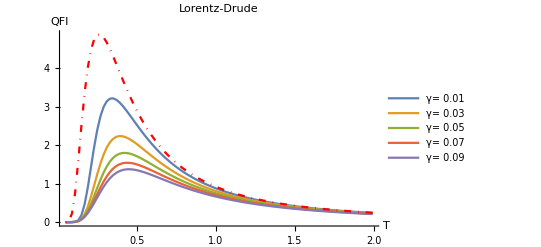

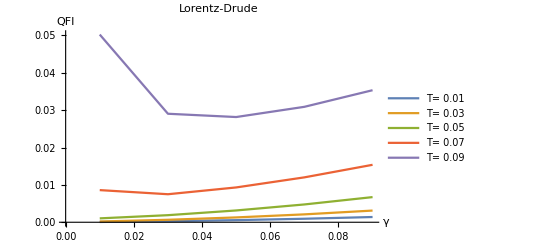

```mathematica
plot1=ListLinePlot[Table[dataLorentzDrude[[γp,All,2;;3]],{γp,1,5}],PlotLegends->Table[StringForm["γ= ``",dataLorentzDrude[[γp,1,1]]],{γp,1,5}],AxesLabel->{"T","QFI"}];

plot2=ListLinePlot[Table[{T,quantumFisherEq[1,T]},{T,0.05,2,1/top1}],PlotStyle->{Red,DotDashed}];

Show[plot1,plot2,PlotRange->All,PlotLabel->"Lorentz-Drude"]

ListLinePlot[Table[dataLorentzDrude[[All,Tp,{1,3}]],{Tp,1,5}],PlotLegends->Table[StringForm["T= ``",dataLorentzDrude[[Tp,1,1]]],{Tp,1,5}],AxesLabel->{"γ","QFI"},PlotLabel->"Lorentz-Drude"]
```

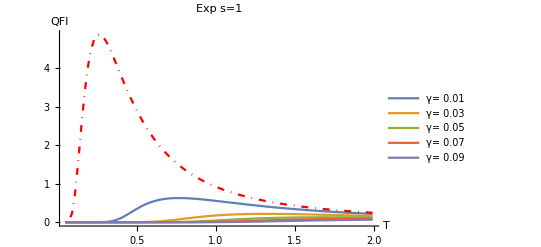

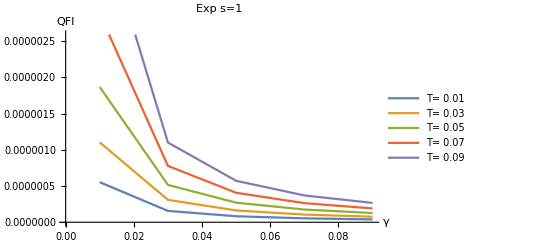

```mathematica
plot3=ListLinePlot[Table[dataExp1[[γp,All,2;;3]],{γp,1,5}],PlotLegends->Table[StringForm["γ= ``",dataExp1[[γp,1,1]]],{γp,1,5}],AxesLabel->{"T","QFI"}];

plot4=ListLinePlot[Table[{T,quantumFisherEq[1,T]},{T,0.05,2,1/top1}],PlotStyle->{Red,DotDashed}];

Show[plot3,plot4,PlotRange->All,PlotLabel->"Exp s=1"]

ListLinePlot[Table[dataExp1[[All,Tp,{1,3}]],{Tp,1,5}],PlotLegends->Table[StringForm["T= ``",dataExp1[[Tp,1,1]]],{Tp,1,5}],AxesLabel->{"γ","QFI"},PlotLabel->"Exp s=1"]
```

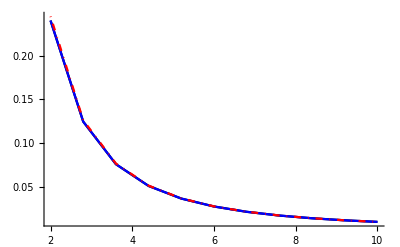

```mathematica
γ=0.01;
ωc=1000;
ω0=1;
Tstart=2;
Tend=10;
steps=10;

plotlorentzdrude=ListPlot[Table[{T,quantumFisherInfo[T,ω0,{γ,ωc},1]},{T,Tstart,Tend,(Tend-Tstart)/steps}],PlotStyle->Black,Joined->True];
plotanalytic=ListPlot[Table[{T,analyticQuantumFisherInfo[T,ω0,{γ,ωc},1]},{T,Tstart,Tend,(Tend-Tstart)/steps}],PlotStyle->Blue,Joined->True];
plotequilibriumqfi=ListPlot[Table[{T,quantumFisherEq[ω0,T]},{T,Tstart,Tend,(Tend-Tstart)/steps}],PlotStyle->{Red,DotDashed},Joined->True];

Show[plotlorentzdrude,plotanalytic,plotequilibriumqfi,PlotRange->All]
```

```mathematica
γlist={0.001,0.01,0.1,1,5};
qfiaccuracytable=ParallelTable[{T,100*((quantumFisherInfo[T,ω0,{γp,ωc},1]-analyticQuantumFisherInfo[T,ω0,{γp,ωc},1])/analyticQuantumFisherInfo[T,ω0,{γp,ωc},1])},{γp,γlist},{T,0.01,1,0.05}];
```

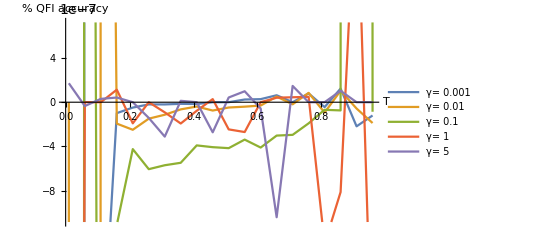

```mathematica
ListLinePlot[qfiaccuracytable,PlotLegends->Table[StringForm["γ= ``",γp],{γp,γlist}],AxesLabel->{"T","% QFI accuracy"}]
```

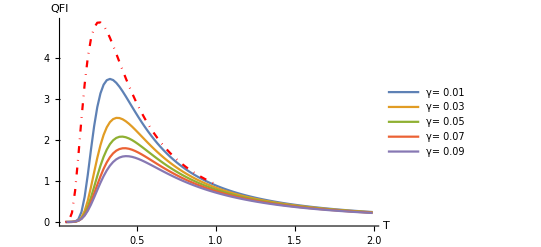

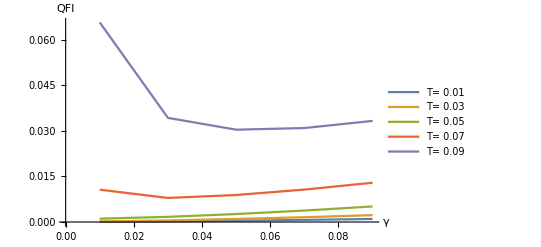

```mathematica
plot4=ListLinePlot[Table[dataExp1[[gammaindex,All,2;;3]],{gammaindex,1,5}],PlotLegends->Table[StringForm["γ= ``",dataExp1[[gammaindex,1,1]]],{gammaindex,1,5}],AxesLabel->{"T","QFI"}];

plot5=ListLinePlot[Table[{T,quantumFisherEq[1,T]},{T,0.05,1,1/top1}],PlotStyle->{Red,DotDashed}];

Show[plot4,plot5,PlotRange->All]

plot6=ListLinePlot[Table[dataExp1[[All,tempindex,{1,3}]],{tempindex,1,5}],PlotLegends->Table[StringForm["T= ``",dataExp1[[tempindex,1,1]]],{tempindex,1,5}],AxesLabel->{"γ","QFI"}]
```

```mathematica
γsmall=0.001;
ωc=1000;
ω0=1;

σ11smallcoupling[T_]:=σ11SteadyState[T,ω0,{γsmall,ωc},1]
σ22smallcoupling[T_]:=σ22SteadyState[T,ω0,{γsmall,ωc},1]
exactσsmallcoupling[T_]:=1/2*Coth[1/(2T)]

plotσ11smallcouplinglorentzdrude=ListPlot[Table[{T,σ11smallcoupling[T]},{T,0.01,0.6,0.01}],PlotStyle->Blue,PlotLabels->"σ11"];
plotσ22smallcouplinglorentzdrude=ListPlot[Table[{T,σ22smallcoupling[T]},{T,0.01,0.6,0.01}],PlotStyle->Green,PlotLabels->"σ22"];
plotexactσsmallcoupling=ListPlot[Table[{T,exactσsmallcoupling[T]},{T,0.01,0.6,0.01}],PlotStyle->Red,PlotLabels->"exact"];

Show[plotσ11smallcouplinglorentzdrude,plotσ22smallcouplinglorentzdrude,plotexactσsmallcoupling,PlotRange->Automatic,AxesLabel->{"T","Covariance"}]

plotσ11smallcouplinglorentzdrudediff=ListPlot[Table[{T,σ11smallcoupling[T]-exactσsmallcoupling[T]},{T,0.01,0.6,0.01}],PlotStyle->Blue,PlotLabels->"σ11-exact"];
plotσ22smallcouplinglorentzdrudediff=ListPlot[Table[{T,σ22smallcoupling[T]-exactσsmallcoupling[T]},{T,0.01,0.6,0.01}],PlotStyle->Green,PlotLabels->"σ22-exact"];

Show[plotσ11smallcouplinglorentzdrudediff,plotσ22smallcouplinglorentzdrudediff,PlotRange->Automatic,AxesLabel->{"T","Covariance difference"}]
```

-Graphics-

-Graphics-

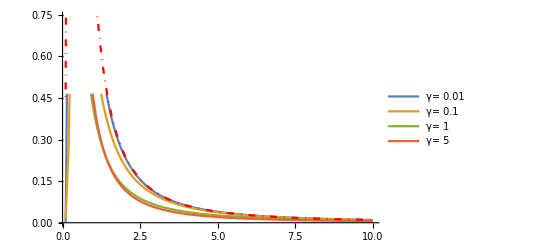

```mathematica
Tstart=0.1;
Tend=10;
steps=100;

plotsanalytic=ListPlot[Table[{T,analyticQuantumFisherInfo[T,1,{γ,1000},1]},{γ,{0.01,0.1,1,5}},{T,Tstart,Tend,(Tend-Tstart)/steps}],PlotLegends->Table[StringForm["γ= ``",γ],{γ,{0.01,0.1,1,5}}],Joined->True];
plotequilibriumqfi=ListPlot[Table[{T,quantumFisherEq[1,T]},{T,Tstart,Tend,(Tend-Tstart)/steps}],PlotStyle->{Red,DotDashed},Joined->True];

Show[plotsanalytic,plotequilibriumqfi,PlotRange->Automatic]
```

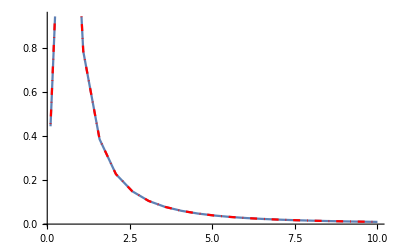

```mathematica
Tstart=0.1;
Tend=10;
steps=20;

plotStructured=ListLinePlot[Table[{T,quantumFisherInfo[T,1,{10^3,10^(3/2),10^3},2]},{T,Tstart,Tend,(Tend-Tstart)/steps}]];
plotequilibriumqfi=ListLinePlot[Table[{T,quantumFisherEq[1,T]},{T,Tstart,Tend,(Tend-Tstart)/steps}],PlotStyle->{Red,DotDashed}];

Show[plotStructured,plotequilibriumqfi,PlotRange->All]
```

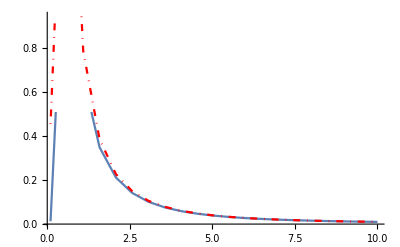

```mathematica
Tstart=0.1;
Tend=10;
steps=20;

plotExp1=ListLinePlot[Table[{T,quantumFisherInfo[T,1,{1,0.1,100},3]},{T,Tstart,Tend,(Tend-Tstart)/steps}]];
plotequilibriumqfi=ListLinePlot[Table[{T,quantumFisherEq[1,T]},{T,Tstart,Tend,(Tend-Tstart)/steps}],PlotStyle->{Red,DotDashed}];

Show[plotExp1,plotequilibriumqfi,PlotRange->All]
```

## Testing

```mathematica
T=0.01;
γ=0.01;
ωc=1000;
ω0=1;

AbsoluteTiming[quantumFisherInfo[T,ω0,{γ,ωc},1]]
AbsoluteTiming[quantumFisherInfo2[T,ω0,{γ,ωc},1]]
AbsoluteTiming[analyticQuantumFisherInfo[T,γ,ω0,ωc]]
```

{0.301179,2.66217×10^-6}

{0.349859,2.66198×10^-6}

{0.0069463,2.66217×10^-6}

# QBM - Dynamics

## Setup

### The Green' s function

G = (g_1 | g_2
g_3 | g_1)

#### Ohmic spectral density with a Lorentz-Drude cut-off

g_1(s)= s/(-(2 γ ωc^2)/(s+ωc)+s^2+ω0^2+2 γ ωc), g_2(s)= 1/(-(2 γ ωc^2)/(s+ωc)+s^2+ω0^2+2 γ ωc), g_3(s)= ((2 γ ωc^2)/(s+ωc)-ω0^2-2 γ ωc)/(-(2 γ ωc^2)/(s+ωc)+s^2+ω0^2+2 γ ωc)

```mathematica
g1LorentzDrude[t_,ω0_,γ_,ωc_]:=(ⅇ^(t Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]) Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1] (ωc+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]))/(ω0^2+2 γ ωc+2 ωc Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]+3 Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]^2)+(ⅇ^(t Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]) Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2] (ωc+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]))/(ω0^2+2 γ ωc+2 ωc Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]+3 Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]^2)+(ⅇ^(t Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3]) Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3] (ωc+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3]))/(ω0^2+2 γ ωc+2 ωc Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3]+3 Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3]^2)
g1LorentzDrude::usage="g1LorentzDrude[t,ω0,γ,ωc] is the diagonal matrix element of the system's Green's function for an Ohmic spectral density with a Lorentz-Drude cut-off";


g2LorentzDrude[t_,ω0_,γ_,ωc_]:=(ⅇ^(t Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]) (ωc+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]))/(ω0^2+2 γ ωc+2 ωc Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]+3 Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]^2)+(ⅇ^(t Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]) (ωc+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]))/(ω0^2+2 γ ωc+2 ωc Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]+3 Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]^2)+(ⅇ^(t Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3]) (ωc+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3]))/(ω0^2+2 γ ωc+2 ωc Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3]+3 Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3]^2)
g2LorentzDrude::usage="g2LorentzDrude[t,ω0,γ,ωc] is the G_12 matrix element of the system's Green's function for an Ohmic spectral density with a Lorentz-Drude cut-off";

g3LorentzDrude[t_,ω0_,γ_,ωc_]:=-(ⅇ^(t Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]) (ω0^2 ωc+(ω0^2+2 γ ωc) Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]))/(ω0^2+2 γ ωc+2 ωc Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]+3 Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]^2)-(ⅇ^(t Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]) (ω0^2 ωc+(ω0^2+2 γ ωc) Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]))/(ω0^2+2 γ ωc+2 ωc Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]+3 Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]^2)-(ⅇ^(t Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3]) (ω0^2 ωc+(ω0^2+2 γ ωc) Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3]))/(ω0^2+2 γ ωc+2 ωc Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3]+3 Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3]^2)
g3LorentzDrude::usage="g3LorentzDrude[t,ω0,γ,ωc] is the G_21 matrix element of the system's Green's function for an Ohmic spectral density with a Lorentz-Drude cut-off";
```

#### Ohmic spectral density with a Structured Lorentz-Drude cut-off

g_1(s)= s/(-λ^2/(ωs^2+s^2 +γ*s)+s^2+ω0^2+λ^2/ωs^2), g_2(s)= 1/(-λ^2/(ωs^2+s^2 +γ*s)+s^2+ω0^2+λ^2/ωs^2), g_3(s)= (λ^2/(ωs^2+s^2 +γ*s)-ω0^2-λ^2/ωs^2)/(-(2 γ ωc^2)/(s+ωc)+s^2+ω0^2+2 γ ωc)

```mathematica
g1StructuredLorentzDrude[t_,ω0_,γ_,λ_,ωs_]:=ωs^2 ((ⅇ^(t Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1] (ωs^2+γ Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]^2))/(γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]^3)+(ⅇ^(t Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2] (ωs^2+γ Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]^2))/(γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]^3)+(ⅇ^(t Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3] (ωs^2+γ Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]^2))/(γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]^3)+(ⅇ^(t Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4] (ωs^2+γ Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]^2))/(γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]^3))
g1StructuredLorentzDrude::usage="g1StructuredLorentzDrude[t,ω0,γ,λ,ωs] is the diagonal matrix element of the system's Green's function for an Ohmic spectral density with a structured Lorentz-Drude cut-off";

g2StructuredLorentzDrude[t_,ω0_,γ_,λ_,ωs_]:=ωs^2 ((ⅇ^(t Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]) (ωs^2+γ Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]^2))/(γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]^3)+(ⅇ^(t Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]) (ωs^2+γ Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]^2))/(γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]^3)+(ⅇ^(t Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]) (ωs^2+γ Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]^2))/(γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]^3)+(ⅇ^(t Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]) (ωs^2+γ Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]^2))/(γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]^3))
g2StructuredLorentzDrude::usage="g2StructuredLorentzDrude[t,ω0,γ,λ,ωs] is the G_12 matrix element of the system's Green's function for an Ohmic spectral density with a structured Lorentz-Drude cut-off";

g3StructuredLorentzDrude[t_,ω0_,γ_,λ_,ωs_]:=-((ⅇ^(t Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]) (ω0^2 ωs^4+γ (λ^2+ω0^2 ωs^2) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]+(λ^2+ω0^2 ωs^2) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]^2))/(γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]^3))-(ⅇ^(t Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]) (ω0^2 ωs^4+γ (λ^2+ω0^2 ωs^2) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]+(λ^2+ω0^2 ωs^2) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]^2))/(γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]^3)-(ⅇ^(t Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]) (ω0^2 ωs^4+γ (λ^2+ω0^2 ωs^2) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]+(λ^2+ω0^2 ωs^2) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]^2))/(γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]^3)-(ⅇ^(t Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]) (ω0^2 ωs^4+γ (λ^2+ω0^2 ωs^2) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]+(λ^2+ω0^2 ωs^2) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]^2))/(γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]^3)
g3StructuredLorentzDrude::usage="g3StructuredLorentzDrude[t,ω0,γ,λ,ωs] is the G_21 matrix element of the system's Green's function for an Ohmic spectral density with a structured Lorentz-Drude cut-off";
```

#### General s spectral density with an exponential cut-off

g_1(s)= s/(-χsLaplace[k,s,γ,ωc]+s^2+ω0^2+γ ωc  (-1+k)!), g_2(s)= 1/(-χsLaplace[k,s,γ,ωc]+s^2+ω0^2+γ ωc  (-1+k)!), g_3(s)= (χsLaplace[k,s,γ,ωc]-ω0^2-γ ωc  (-1+k)!)/(-χsLaplace[k,s,γ,ωc]+s^2+ω0^2+γ ωc  (-1+k)!)

```mathematica
nω0=1;
nγ=0.1;
nωc=100;
```

```mathematica
InverseLaplaceTransform[s/(s^2+nω0^2+nγ nωc  -χsLaplace[1,s,nγ,nωc]),s,1]
```

InverseLaplaceTransform[s/(11.+s^2-5. ⅇ^(-(ⅈ s)/100) (ExpIntegralE[2,-(ⅈ s)/100]+ⅇ^((ⅈ s)/50) ExpIntegralE[2,(ⅈ s)/100])),s,1]

```mathematica
g1exps[t_,ω0_,s_,γ_,ωc_]:=1
g1exps::usage="g1exps[t,ω0,s,γ,ωc] is the diagonal matrix element of the system's Green's function for a spectral density with ohmicity s and an exponential cut-off";


g2exps[t_,ω0_,s_,γ_,ωc_]:=1
g2exps::usage="g2exps[t,ω0,s,γ,ωc] is the G_12 matrix element of the system's Green's function for a spectral density with ohmicity s and an exponential cut-off";

g3exps[t_,ω0_,s_,γ_,ωc_]:=1
g3exps::usage="g3exps[t,ω0,s,γ,ωc] is the G_21 matrix element of the system's Green's function for a spectral density with ohmicity s and an exponential cut-off";
```

#### g list

```mathematica
g1List[t_,ω0_,params_]:=Module[{args=Join[{t,ω0},params]},{g1LorentzDrude@@ args,g1StructuredLorentzDrude@@ args}]
g1List::usage="g1List[t,ω0,params] is a list of the G_11/G_22 matrix element of the system's Green's function for a list of spectral densities. The list is {Lorentz-Drude,Structured Lorentz-Drude,Exponential (s=1)}";
g2List[t_,ω0_,params_]:=Module[{args=Join[{t,ω0},params]},{g2LorentzDrude@@ args,g2StructuredLorentzDrude@@ args}]
g2List::usage="g2List[t,ω0,params] is a list of the G_12 matrix element of the system's Green's function for a list of spectral densities. The list is {Lorentz-Drude,Structured Lorentz-Drude,Exponential (s=1)}";
g3List[t_,ω0_,params_]:=Module[{args=Join[{t,ω0},params]},{g3LorentzDrude@@ args,g3StructuredLorentzDrude@@ args}]
g3List::usage="g3List[t,ω0,params] is a list of the G_21 matrix element of the system's Green's function for a list of spectral densities. The list is {Lorentz-Drude,Structured Lorentz-Drude,Exponential (s=1)}";


g1[t_,ω0_,params_,Jindex_]:=g1List[t,ω0,params][[Jindex]]//Chop
g1::usage="g1[t,ω0,params,Jindex] is the G_11/G_22 matrix element of the system's Green's function for a particular spectral density. Jindex=1 gives Lorentz-Drude, Jindex=2 gives Structured Lorentz-Drude.";
g2[t_,ω0_,params_,Jindex_]:=g2List[t,ω0,params][[Jindex]]//Chop
g2::usage="g2[t,ω0,params,Jindex] is the G_12 matrix element of the system's Green's function for a particular spectral density. Jindex=1 gives Lorentz-Drude, Jindex=2 gives Structured Lorentz-Drude.";
g3[t_,ω0_,params_,Jindex_]:=g3List[t,ω0,params][[Jindex]]//Chop
g3::usage="g3[t,ω0,params,Jindex] is the G_21 matrix element of the system's Green's function for a particular spectral density. Jindex=1 gives Lorentz-Drude, Jindex=2 gives Structured Lorentz-Drude.";

(*
x[t_,ω0_,params_,x0_,p0_,Jindex_]:=g1[t,ω0,params,Jindex]*x0+g2[t,ω0,params,Jindex]*p0;
x::usage="x[t,ω0,params,x0,p0,Jindex] is the particle's time-dependent Heisenburg picture position, with initial position/momentum x0/p0";

p[t_,ω0_,params_,x0_,p0_,Jindex_]:=g3[t,ω0,params,Jindex]*x0+g1[t,ω0,params,Jindex]*p0;
p::usage="p[t,ω0,params,x0,p0,Jindex] is the particle's time-dependent Heisenburg picture momentum, with initial position/momentum x0/p0";
*)
```

### g_(1,2)e^(±ⅈωt) integrals

g_i^(±)(t,ω)=∫_0^t g_i(t')ⅇ^(± ω t')ⅆt'

Note only g_(1,2) are needed.

#### Ohmic spectral density with a Lorentz-Drude cut-off

```mathematica
g1integralminusLorentzDrude[t_,ω_,ω0_,γ_,ωc_]:=((-1+ⅇ^(t (-ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]))) ωc Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1])/((-ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]) (ω0^2+2 γ ωc+2 ωc Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]+3 Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]^2))+((-1+ⅇ^(t (-ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]))) Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]^2)/((-ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]) (ω0^2+2 γ ωc+2 ωc Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]+3 Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]^2))+((-1+ⅇ^(t (-ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]))) ωc Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2])/((-ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]) (ω0^2+2 γ ωc+2 ωc Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]+3 Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]^2))+((-1+ⅇ^(t (-ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]))) Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]^2)/((-ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]) (ω0^2+2 γ ωc+2 ωc Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]+3 Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]^2))+((-1+ⅇ^(t (-ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3]))) Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3] (ωc+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3]))/((-ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3]) (ω0^2+2 γ ωc+2 ωc Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3]+3 Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3]^2))
g1integralminusLorentzDrude::usage="g1integralminusLorentzDrude[t,ω,ω0,γ,ωc] is the integral from 0 to t of g1LorentzDrude[s,ω0,γ,ωc] * e^-iωs";

g1integralplusLorentzDrude[t_,ω_,ω0_,γ_,ωc_]:=((-1+ⅇ^(t (ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]))) ωc Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1])/((ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]) (ω0^2+2 γ ωc+2 ωc Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]+3 Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]^2))+((-1+ⅇ^(t (ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]))) Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]^2)/((ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]) (ω0^2+2 γ ωc+2 ωc Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]+3 Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]^2))+((-1+ⅇ^(t (ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]))) ωc Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2])/((ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]) (ω0^2+2 γ ωc+2 ωc Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]+3 Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]^2))+((-1+ⅇ^(t (ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]))) Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]^2)/((ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]) (ω0^2+2 γ ωc+2 ωc Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]+3 Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]^2))+((-1+ⅇ^(t (ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3]))) Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3] (ωc+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3]))/((ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3]) (ω0^2+2 γ ωc+2 ωc Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3]+3 Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3]^2))
g1integralplusLorentzDrude::usage="g1integralplusLorentzDrude[t,ω0,ω,γ,ωc] is the integral from 0 to t of g1LorentzDrude[s,ω0,γ,ωc] * e^(+iωs)";

g2integralminusLorentzDrude[t_,ω_,ω0_,γ_,ωc_]:=((-1+ⅇ^(t (-ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]))) ωc)/((-ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]) (ω0^2+2 γ ωc+2 ωc Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]+3 Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]^2))+((-1+ⅇ^(t (-ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]))) Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1])/((-ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]) (ω0^2+2 γ ωc+2 ωc Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]+3 Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]^2))+((-1+ⅇ^(t (-ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]))) ωc)/((-ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]) (ω0^2+2 γ ωc+2 ωc Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]+3 Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]^2))+((-1+ⅇ^(t (-ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]))) Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2])/((-ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]) (ω0^2+2 γ ωc+2 ωc Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]+3 Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]^2))+((-1+ⅇ^(t (-ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3]))) ωc)/((-ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3]) (ω0^2+2 γ ωc+2 ωc Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3]+3 Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3]^2))+((-1+ⅇ^(t (-ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3]))) Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3])/((-ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3]) (ω0^2+2 γ ωc+2 ωc Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3]+3 Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3]^2))
g2integralminusLorentzDrude::usage="g2integralminusLorentzDrude[t,ω,ω0,γ,ωc] is the integral from 0 to t of g2LorentzDrude[s,ω0,γ,ωc] * e^-iωs";

g2integralplusLorentzDrude[t_,ω_,ω0_,γ_,ωc_]:=((-1+ⅇ^(t (ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]))) ωc)/((ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]) (ω0^2+2 γ ωc+2 ωc Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]+3 Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]^2))+((-1+ⅇ^(t (ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]))) Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1])/((ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]) (ω0^2+2 γ ωc+2 ωc Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]+3 Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]^2))+((-1+ⅇ^(t (ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]))) ωc)/((ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]) (ω0^2+2 γ ωc+2 ωc Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]+3 Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]^2))+((-1+ⅇ^(t (ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]))) Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2])/((ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]) (ω0^2+2 γ ωc+2 ωc Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]+3 Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]^2))+((-1+ⅇ^(t (ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3]))) ωc)/((ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3]) (ω0^2+2 γ ωc+2 ωc Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3]+3 Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3]^2))+((-1+ⅇ^(t (ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3]))) Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3])/((ⅈ ω+Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3]) (ω0^2+2 γ ωc+2 ωc Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3]+3 Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3]^2))
g2integralplusLorentzDrude::usage="g2integralplusLorentzDrude[t,ω,ω0,γ,ωc] is the integral from 0 to t of g2LorentzDrude[s,ω0,γ,ωc] * e^(+iωs)";
```

#### Ohmic spectral density with a Structured Lorentz-Drude cut-off

```mathematica
g1integralminusStructuredLorentzDrude[t_,ω_,ω0_,γ_,λ_,ωs_]:=ωs^2 (((-1+ⅇ^(t (-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]))) ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1])/((-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]^3))+((-1+ⅇ^(t (-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]))) γ Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]^2)/((-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]^3))+((-1+ⅇ^(t (-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]))) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]^3)/((-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]^3))+((-1+ⅇ^(t (-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]))) ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2])/((-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]^3))+((-1+ⅇ^(t (-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]))) γ Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]^2)/((-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]^3))+((-1+ⅇ^(t (-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]))) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]^3)/((-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]^3))+((-1+ⅇ^(t (-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]))) ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3])/((-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]^3))+((-1+ⅇ^(t (-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]))) γ Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]^2)/((-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]^3))+((-1+ⅇ^(t (-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]))) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]^3)/((-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]^3))+((-1+ⅇ^(t (-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]))) ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4])/((-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]^3))+((-1+ⅇ^(t (-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]))) γ Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]^2)/((-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]^3))+((-1+ⅇ^(t (-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]))) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]^3)/((-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]^3)))
g1StructuredLorentzDrudeintegralminus::usage="g1StructuredLorentzDrudeintegralminus[t,ω,ω0,γ,λ,ωs] is the integral from 0 to t of g1StructuredLorentzDrude[s,ω0,γ,λ,ωs] * e^-iωs";

g1integralplusStructuredLorentzDrude[t_,ω_,ω0_,γ_,λ_,ωs_]:=ωs^2 (((-1+ⅇ^(t (ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]))) ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1])/((ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]^3))+((-1+ⅇ^(t (ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]))) γ Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]^2)/((ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]^3))+((-1+ⅇ^(t (ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]))) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]^3)/((ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]^3))+((-1+ⅇ^(t (ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]))) ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2])/((ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]^3))+((-1+ⅇ^(t (ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]))) γ Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]^2)/((ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]^3))+((-1+ⅇ^(t (ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]))) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]^3)/((ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]^3))+((-1+ⅇ^(t (ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]))) ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3])/((ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]^3))+((-1+ⅇ^(t (ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]))) γ Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]^2)/((ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]^3))+((-1+ⅇ^(t (ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]))) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]^3)/((ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]^3))+((-1+ⅇ^(t (ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]))) ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4])/((ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]^3))+((-1+ⅇ^(t (ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]))) γ Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]^2)/((ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]^3))+((-1+ⅇ^(t (ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]))) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]^3)/((ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]^3)))
g1integralplusStructuredLorentzDrude::usage="g1integralminusStructuredLorentzDrude[t,ω,ω0,γ,λ,ωs] is the integral from 0 to t of g1StructuredLorentzDrude[s,ω0,γ,λ,ωs] * e^iωs";

g2integralminusStructuredLorentzDrude[t_,ω_,ω0_,γ_,λ_,ωs_]:=ωs^2 (((-1+ⅇ^(t (-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]))) ωs^2)/((-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]^3))+((-1+ⅇ^(t (-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]))) γ Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1])/((-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]^3))+((-1+ⅇ^(t (-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]))) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]^2)/((-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]^3))+((-1+ⅇ^(t (-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]))) ωs^2)/((-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]^3))+((-1+ⅇ^(t (-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]))) γ Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2])/((-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]^3))+((-1+ⅇ^(t (-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]))) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]^2)/((-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]^3))+((-1+ⅇ^(t (-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]))) ωs^2)/((-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]^3))+((-1+ⅇ^(t (-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]))) γ Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3])/((-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]^3))+((-1+ⅇ^(t (-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]))) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]^2)/((-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]^3))+((-1+ⅇ^(t (-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]))) ωs^2)/((-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]^3))+((-1+ⅇ^(t (-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]))) γ Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4])/((-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]^3))+((-1+ⅇ^(t (-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]))) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]^2)/((-ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]^3)))
g2integralminusStructuredLorentzDrude::usage="g2integralminusStructuredLorentzDrude[t,ω,ω0,γ,λ,ωs] is the integral from 0 to t of g2StructuredLorentzDrude[s,ω0,γ,λ,ωs] * e^-iωs";

g2integralplusStructuredLorentzDrude[t_,ω_,ω0_,γ_,λ_,ωs_]:=ωs^2 (((-1+ⅇ^(t (ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]))) ωs^2)/((ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]^3))+((-1+ⅇ^(t (ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]))) γ Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1])/((ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]^3))+((-1+ⅇ^(t (ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]))) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]^2)/((ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]^3))+((-1+ⅇ^(t (ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]))) ωs^2)/((ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]^3))+((-1+ⅇ^(t (ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]))) γ Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2])/((ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]^3))+((-1+ⅇ^(t (ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]))) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]^2)/((ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]^3))+((-1+ⅇ^(t (ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]))) ωs^2)/((ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]^3))+((-1+ⅇ^(t (ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]))) γ Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3])/((ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]^3))+((-1+ⅇ^(t (ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]))) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]^2)/((ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]^3))+((-1+ⅇ^(t (ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]))) ωs^2)/((ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]^3))+((-1+ⅇ^(t (ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]))) γ Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4])/((ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]^3))+((-1+ⅇ^(t (ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]))) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]^2)/((ⅈ ω+Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]) (γ (λ^2+ω0^2 ωs^2)+2 (λ^2+ω0^2 ωs^2+ωs^4) Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]+3 γ ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]^2+4 ωs^2 Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]^3)))
g2integralplusStructuredLorentzDrude::usage="g2integralplusStructuredLorentzDrude[t,ω,ω0,γ,λ,ωs] is the integral from 0 to t of g2StructuredLorentzDrude[s,ω0,γ,λ,ωs]* e^iωs";
```

#### g integrals list

```mathematica
g1integralminusList[t_,ω_,ω0_,params_]:=Module[{args=Join[{t,ω,ω0},params]},{g1integralminusLorentzDrude@@ args,g1integralminusStructuredLorentzDrude@@ args}]
g1integralplusList[t_,ω_,ω0_,params_]:=Module[{args=Join[{t,ω,ω0},params]},{g1integralplusLorentzDrude@@ args,g1integralplusStructuredLorentzDrude@@ args}]
g2integralminusList[t_,ω_,ω0_,params_]:=Module[{args=Join[{t,ω,ω0},params]},{g2integralminusLorentzDrude@@ args,g2integralminusStructuredLorentzDrude@@ args}]
g2integralplusList[t_,ω_,ω0_,params_]:=Module[{args=Join[{t,ω,ω0},params]},{g2integralplusLorentzDrude@@ args,g2integralplusStructuredLorentzDrude@@ args}]


g1integralminus[t_,ω_,ω0_,params_,Jindex_]:=g1integralminusList[t,ω,ω0,params][[Jindex]]//Chop
g1integralminus::usage="g1integralminus[t,ω,ω0,params,Jindex] is the integral from 0 to t of g1[s,ω0,params]* e^-iωs for a particular spectral density. Jindex=1 gives Lorentz-Drude, Jindex=2 gives Structured Lorentz-Drude.";

g1integralplus[t_,ω_,ω0_,params_,Jindex_]:=g1integralplusList[t,ω,ω0,params][[Jindex]]//Chop
g1integralplus::usage="g1integralplus[t,ω,ω0,params,Jindex] is the integral from 0 to t of g1[s,ω0,params]* e^iωs for a particular spectral density. Jindex=1 gives Lorentz-Drude, Jindex=2 gives Structured Lorentz-Drude.";

g2integralminus[t_,ω_,ω0_,params_,Jindex_]:=g2integralminusList[t,ω,ω0,params][[Jindex]]//Chop
g2integralminus::usage="g2integralminus[t,ω,ω0,params,Jindex] is the integral from 0 to t of g2[s,ω0,params]* e^-iωs for a particular spectral density. Jindex=1 gives Lorentz-Drude, Jindex=2 gives Structured Lorentz-Drude.";

g2integralplus[t_,ω_,ω0_,params_,Jindex_]:=g2integralplusList[t,ω,ω0,params][[Jindex]]//Chop
g2integralplus::usage="g2integralplus[t,ω,ω0,params,Jindex] is the integral from 0 to t of g2[s,ω0,params]* e^iωs for a particular spectral density. Jindex=1 gives Lorentz-Drude, Jindex=2 gives Structured Lorentz-Drude.";
```

### Memory integrals and the covariance matrix

```mathematica
accGoal=8;
precGoal=10;
workPrec=15;
maxRecur=15;

(*method=Automatic;*)
method="PrincipalValue";
(*method="ExtrapolatingOscillatory";*)
(*method="DoubleExponential";*)
(*method="DoubleExponentialOscillatory";*)

Ixx[t_,T_,ω0_,params_,Jindex_]:=1/π*NIntegrate[Re[N[J[ω,params,Jindex]* Coth[ω/(2T)]*g2integralminus[t,ω,ω0,params,Jindex]*g2integralplus[t,ω,ω0,params,Jindex]]],{ω,0,∞},Exclusions->{ω0},AccuracyGoal->accGoal,PrecisionGoal->precGoal,WorkingPrecision->workPrec,MaxRecursion->maxRecur,Method->method]
Ixx::usage="Ixx[t,T,ω0,params,Jindex] is the memory-integral contribution to the xx element of the covariance matrix";

Ixp[t_,T_,ω0_,params_,Jindex_]:=1/(2π)*NIntegrate[Re[N[J[ω,params,Jindex]*Coth[ω/(2T)]*(g2integralminus[t,ω,ω0,params,Jindex]*g1integralplus[t,ω,ω0,params,Jindex]+g2integralplus[t,ω,ω0,params,Jindex]*g1integralminus[t,ω,ω0,params,Jindex])]],{ω,0,∞},Exclusions->{ω0},AccuracyGoal->accGoal,PrecisionGoal->precGoal,WorkingPrecision->workPrec,MaxRecursion->maxRecur,Method->method]
Ixp::usage="Ixp[t,T,ω0,params,Jindex] is the memory-integral contribution to the xp element of the covariance matrix";

Ipp[t_,T_,ω0_,params_,Jindex_]:=1/π*NIntegrate[Re[N[J[ω,params,Jindex]*Coth[ω/(2T)]*g1integralminus[t,ω,ω0,params,Jindex]*g1integralplus[t,ω,ω0,params,Jindex]]],{ω,0,∞},Exclusions->{ω0},AccuracyGoal->accGoal,PrecisionGoal->precGoal,WorkingPrecision->workPrec,MaxRecursion->maxRecur,Method->method]
Ipp::usage="Ipp[t,T,ω0,params,Jindex] is the memory-integral contribution to the pp element of the covariance matrix";

σxx[t_,T_,ω0_,params_,xx0_,pp0_,xp0_,Jindex_]:=(g1[t,ω0,params,Jindex])^2*xx0+2*g1[t,ω0,params,Jindex]*g2[t,ω0,params,Jindex]*xp0+(g2[t,ω0,params,Jindex])^2*pp0+Ixx[t,T,ω0,params,Jindex] //Chop
σxx::usage="σxx[t,T,ω0,params,xx0,pp0,xp0,Jindex] is the xx element of the covariance matrix";

σxp[t_,T_,ω0_,params_,xx0_,pp0_,xp0_,Jindex_]:=g1[t,ω0,params,Jindex]*g3[t,ω0,params,Jindex]*xx0+((g1[t,ω0,params,Jindex])^2+g2[t,ω0,params,Jindex]*g3[t,ω0,params,Jindex])*xp0+g1[t,ω0,params,Jindex]*g2[t,ω0,params,Jindex]*pp0+Ixp[t,T,ω0,params,Jindex]//Chop
σxp::usage="σxp[t,T,ω0,params,xx0,pp0,xp0,Jindex] is the xp element of the covariance matrix";

σpp[t_,T_,ω0_,params_,xx0_,pp0_,xp0_,Jindex_]:=(g3[t,ω0,params,Jindex])^2*xx0+2*g1[t,ω0,params,Jindex]*g3[t,ω0,params,Jindex]*xp0+(g1[t,ω0,params,Jindex])^2*pp0+Ipp[t,T,ω0,params,Jindex]//Chop
σpp::usage="σpp[t,T,ω0,params,xx0,pp0,xp0,Jindex] is the pp element of the covariance matrix";

xExact[t_,ω0_,params_,x0_,p0_,JIndex_]:=g1[t,ω0,params,JIndex]*x0+g2[t,ω0,params,JIndex]*p0
pExact[t_,ω0_,params_,x0_,p0_,JIndex_]:=g3[t,ω0,params,JIndex]*x0+g1[t,ω0,params,JIndex]*p0



σcov[t_,T_,ω0_,params_,xx0_,pp0_,xp0_,Jindex_]:=Module[{σxpTemp=σxp[t,T,ω0,params,xx0,pp0,xp0,Jindex]//Quiet},({{σxx[t,T,ω0,params,xx0,pp0,xp0,Jindex]//Quiet, σxpTemp}, {σxpTemp, σpp[t,T,ω0,params,xx0,pp0,xp0,Jindex]//Quiet}})]
σcov::usage="σcov[t,T,ω0,params,xx0,pp0,xp0,Jindex] is the covariance matrix σ_ij=1/2{R_i,R_j}_+ where R=(x p)^T";
```

```mathematica
nω0=999;
nT=1;

nγ=1;
nλ=10;
nωs=1000;

nparams={nγ,nλ,nωs};

timescale=10^5;

nt=4;

-(Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]/.{γ->nγ,λ->nλ,ωs->nωs,ω0->nω0}//N//Re)^-1
```

99884.4

```mathematica
1/π*NIntegrate[Re[N[J[ω,nparams,2]* Coth[ω/(2nT)]*g2integralminus[nt*timescale,ω,nω0,nparams,2]*g2integralplus[nt*timescale,ω,nω0,nparams,2]]],{ω,0,∞},Exclusions->{nω0},AccuracyGoal->8,PrecisionGoal->10,WorkingPrecision->15,MaxRecursion->15,Method->"DoubleExponentialOscillatory"]
```

4.37501241300616×10^-8

General::munfl: Exp[-199996.-3.99984×10^8 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

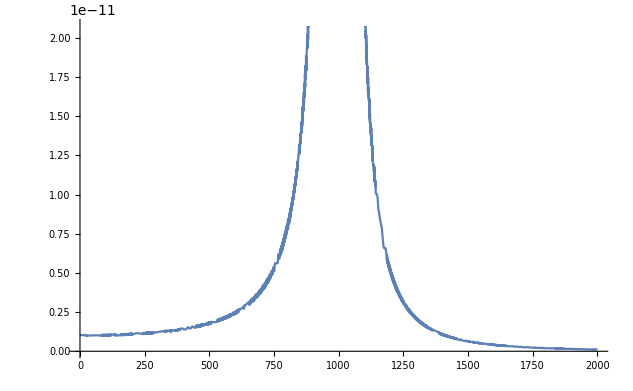

```mathematica
Plot[Re[g2integralminus[nt*timescale,ω,nω0,nparams,2]*g2integralplus[nt*timescale,ω,nω0,nparams,2]],{ω,0,2000}]
```

General::munfl: Exp[-199996.-2.39999×10^8 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

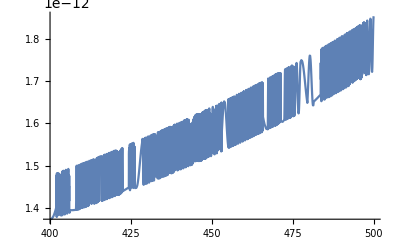

```mathematica
Plot[Re[g2integralminus[nt*timescale,ω,nω0,nparams,2]*g2integralplus[nt*timescale,ω,nω0,nparams,2]],{ω,400,500}]
```

```mathematica
nω0=50;
nT=1;

nγ=1;
nωc=100;

nparams={nγ,nωc};

timescale=10^0;

nt=2;

-(Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3]/.{γ->nγ,ωc->nωc,ω0->nω0}//N//Re)^-1
```

1.23795

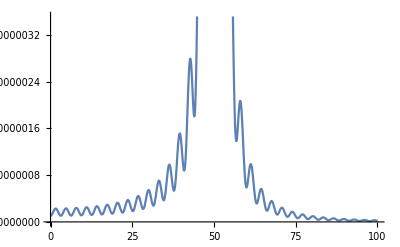

```mathematica
Plot[Re[g2integralminus[nt*timescale,ω,nω0,nparams,1]*g2integralplus[nt*timescale,ω,nω0,nparams,1]],{ω,0,100}]
```

## Plots

```mathematica
nω0=1;
nT=1;

nJindex=1;
nγ=0.01;
nωc=100;
nparams={nγ,nωc};

xx0=1/2;pp0=1/2 ;xp0=0;

timescale=1*10^2;

tmax=2;
points=100;

steadystateσxxLD=N[acovarianceMatrix[nT,nω0,nparams,nJindex][[1,1]]//Quiet];
numericalσxxLD=ParallelTable[{t,σxx[t*timescale,nT,nω0,nparams,xx0,pp0,xp0,nJindex]//Quiet},{t,0,tmax,tmax/points}];
memoryListσxxLD=ParallelTable[{t,Ixx[t*timescale,nT,nω0,nparams,nJindex]//Quiet},{t,0,tmax,tmax/points}];
steadystateListσxxLD=Table[{t,steadystateσxxLD},{t,0,tmax,tmax/points}];
```

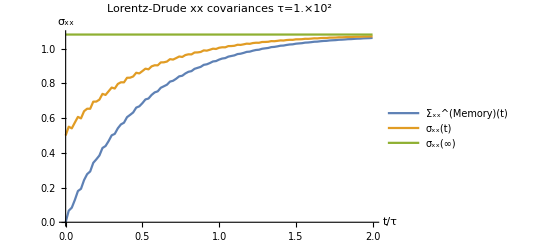

```mathematica
ListLinePlot[{memoryListσxxLD,numericalσxxLD,steadystateListσxxLD},AxesLabel->{"t/τ","σ_xx"},PlotLegends->{"Σ_xx^(Memory)(t)","σ_xx(t)","σ_xx(∞)"},PlotRange->All,PlotLabel->StringForm["Lorentz-Drude xx covariances\n τ=``",ScientificForm[N[timescale]]]]
```

```mathematica
nω0=1;
nT=0.1;

nJindex=1;
nγ=0.01;
nωc=100;
nparams={nγ,nωc};

xx0=1/2;pp0=1/2 ;xp0=0;

timescale=1*10^2;

tmax=3;
points=50;

steadystateσxxLD=N[acovarianceMatrix[nT,nω0,nparams,nJindex][[1,1]]//Quiet];
numericalσxxLD=ParallelTable[{t,σxx[t*timescale,nT,nω0,nparams,xx0,pp0,xp0,nJindex]//Quiet},{t,0,tmax,tmax/points}];
memoryListσxxLD=ParallelTable[{t,Ixx[t*timescale,nT,nω0,nparams,nJindex]//Quiet},{t,0,tmax,tmax/points}];
steadystateListσxxLD=Table[{t,steadystateσxxLD},{t,0,tmax,tmax/points}];
```

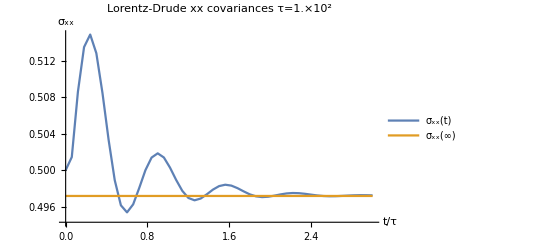

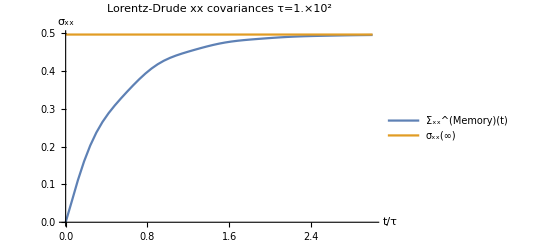

```mathematica
ListLinePlot[{numericalσxxLD,steadystateListσxxLD},AxesLabel->{"t/τ","σ_xx"},PlotLegends->{"σ_xx(t)","σ_xx(∞)"},PlotRange->All,PlotLabel->StringForm["Lorentz-Drude xx covariances\n τ=``",ScientificForm[N[timescale]]]]
ListLinePlot[{memoryListσxxLD,steadystateListσxxLD},AxesLabel->{"t/τ","σ_xx"},PlotLegends->{"Σ_xx^(Memory)(t)","σ_xx(∞)"},PlotRange->All,PlotLabel->StringForm["Lorentz-Drude xx covariances\n τ=``",ScientificForm[N[timescale]]]]
```

```mathematica
nJindex=2;
nω0=1;
nT=1;

α1=10^-3;
α2=10^3;

nγ=10^3;
nλ=Sqrt[α1*α2*nγ];
nωs=Sqrt[α2*nγ];

nparams={nγ,nλ,nωs};

xx0=1/2;pp0=1/2 ;xp0=0;

timescale=1*10^6;

tmax=20;
points=50;

steadystateσxxSLD=N[acovarianceMatrix[nT,nω0,nparams,nJindex][[1,1]]//Quiet];
numericalσxxSLD=ParallelTable[{t,σxx[t*timescale,nT,nω0,nparams,xx0,pp0,xp0,nJindex]//Quiet},{t,0,tmax,tmax/points}];
memoryListσxxSLD=ParallelTable[{t,Ixx[t*timescale,nT,nω0,nparams,nJindex]//Quiet},{t,0,tmax,tmax/points}];
steadystateListσxxSLD=Table[{t,steadystateσxxSLD},{t,0,tmax,tmax/points}];
```

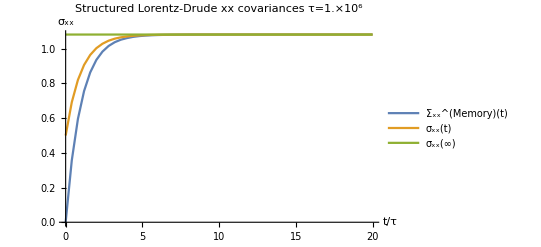

```mathematica
ListLinePlot[{memoryListσxxSLD,numericalσxxSLD,steadystateListσxxSLD},AxesLabel->{"t/τ","σ_xx"},PlotLegends->{"Σ_xx^(Memory)(t)","σ_xx(t)","σ_xx(∞)"},PlotRange->All,PlotLabel->StringForm["Structured Lorentz-Drude xx covariances\n τ=``",ScientificForm[N[timescale]]]]
```

# Spectral density and the Markovian approximation

## Analytic bath correlation functions

⟨B(t)B(0)⟩ = 1/π∫_0^∞ J(ω)(coth(ω/(2T))cos(ωt)-ⅈ sin(ωt))ⅆω

### Spectral Density : Ohmic with Lorentz-Drude cut-off

#### Real part of the bath correlator

```mathematica
(*1/Pi*Integrate[(2 γ ω ωc^2)/(ω^2+ωc^2)*(2*T*ω)/(ω^2+(2*Pi*T)^2*n^2)*Cos[ω*t],{ω,0,Infinity}]*) (*Takes too long to integrate*)
```

```mathematica
1/Pi*Int[(2 γ ω ωc^2)/(ω^2+ωc^2)*(2*T*ω)/(ω^2+(2*Pi*T)^2*n^2)*Cos[ω*t],{ω,0,Infinity}]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

$Aborted

Expand the cosh(ω/(2T)) as an infinite sum; cosh(ω/(2T))  = ∑_(n=-∞)^∞ (2Tω)/(ω^2+ν_n^2) where ν_n=2π T n.
Carry out the integral first, noting that ∫_0^∞ f(ω)cos(ωt)ⅆω=1/2∫_(-∞)^∞ f(ω) e^ⅈωt ⅆω, since f(ω) is a real and even function.

```mathematica
Simplify[1/(2Pi)*Sqrt[2*Pi]*FourierTransform[(2 γ ω ωc^2)/(ω^2+ωc^2)*(2*T*ω)/(ω^2+(2*Pi*T)^2*n^2),ω,t],{ n ∈ Integers,T ∈ PositiveReals}]
```

1/((2 n π T-ωc) (2 n π T+ωc))2 ⅇ^(-t (2 n π T+ωc)) T γ ωc^2 (-ⅇ^(2 t (n π T+ωc)) ωc HeavisideTheta[-t]-ⅇ^(2 n π t T) ωc HeavisideTheta[t]+ⅇ^(t ωc) n π T (2 ⅇ^(4 n π t T) HeavisideTheta[-t Sign[n]] Sign[n]+2 HeavisideTheta[t Sign[n]] Sign[n]+(-1+ⅇ^(4 n π t T)) Sign[t] (-1+Sign[Abs[n]])))

Mathematica can't seem to do the sum for all n at once, so split up for n<0, n=0, and n>0.

```mathematica
Simplify[1/((2 n π T-ωc) (2 n π T+ωc))2 ⅇ^(-t (2 n π T+ωc)) T γ ωc^2 (-ⅇ^(2 t (n π T+ωc)) ωc HeavisideTheta[-t]-ⅇ^(2 n π t T) ωc HeavisideTheta[t]+ⅇ^(t ωc) n π T (2 ⅇ^(4 n π t T) HeavisideTheta[-t Sign[n]] Sign[n]+2 HeavisideTheta[t Sign[n]] Sign[n]+(-1+ⅇ^(4 n π t T)) Sign[t] (-1+Sign[Abs[n]]))),{n>0,t>0}]
```

(2 T γ ωc^2 (2 ⅇ^(-2 n π t T) n π T-ⅇ^(-t ωc) ωc))/(4 n^2 π^2 T^2-ωc^2)

```mathematica
Sum[1/((2 n π T-ωc) (2 n π T+ωc))2 ⅇ^(-t (2 n π T+ωc)) T γ ωc^2 (-ⅇ^(2 n π t T) ωc+2 ⅇ^(t ωc) n π T),{n,1,Infinity}] // FullSimplify (*For n>0 (and t>0)*)
```

1/2 γ ωc (((ⅇ^(-2 π t T))^(-ωc/(2 π T)) ωc ((ⅇ^(-2 π t T))^(ωc/(π T)) Beta[ⅇ^(-2 π t T),1-ωc/(2 π T),0]+Beta[ⅇ^(-2 π t T),1+ωc/(2 π T),0]))/π+ⅇ^(-t ωc) (-2 T+ωc Cot[ωc/(2 T)]))

```mathematica
Simplify[1/((2 n π T-ωc) (2 n π T+ωc))2 ⅇ^(-t (2 n π T+ωc)) T γ ωc^2 (-ⅇ^(2 t (n π T+ωc)) ωc HeavisideTheta[-t]-ⅇ^(2 n π t T) ωc HeavisideTheta[t]+ⅇ^(t ωc) n π T (2 ⅇ^(4 n π t T) HeavisideTheta[-t Sign[n]] Sign[n]+2 HeavisideTheta[t Sign[n]] Sign[n]+(-1+ⅇ^(4 n π t T)) Sign[t] (-1+Sign[Abs[n]]))),{n<0,t>0}]
```

(2 ⅇ^(-t ωc) T γ ωc^2 (2 ⅇ^(t (2 n π T+ωc)) n π T+ωc))/(-4 n^2 π^2 T^2+ωc^2)

```mathematica
Sum[(2 ⅇ^(-t ωc) T γ ωc^2 (2 ⅇ^(t (2 n π T+ωc)) n π T+ωc))/(-4 n^2 π^2 T^2+ωc^2),{n,-Infinity,-1}] // FullSimplify (*For n<0 (and t>0)*)
```

(ⅇ^(-t ωc) γ ωc (-2 π T+ⅇ^(t ωc) (ⅇ^(-2 π t T))^(-ωc/(2 π T)) ωc ((ⅇ^(-2 π t T))^(ωc/(π T)) Beta[ⅇ^(-2 π t T),1-ωc/(2 π T),0]+Beta[ⅇ^(-2 π t T),1+ωc/(2 π T),0])+π ωc Cot[ωc/(2 T)]))/(2 π)

```mathematica
Simplify[1/((2 n π T-ωc) (2 n π T+ωc))2 ⅇ^(-t (2 n π T+ωc)) T γ ωc^2 (-ⅇ^(2 t (n π T+ωc)) ωc HeavisideTheta[-t]-ⅇ^(2 n π t T) ωc HeavisideTheta[t]+ⅇ^(t ωc) n π T (2 ⅇ^(4 n π t T) HeavisideTheta[-t Sign[n]] Sign[n]+2 HeavisideTheta[t Sign[n]] Sign[n]+(-1+ⅇ^(4 n π t T)) Sign[t] (-1+Sign[Abs[n]]))),t>0] /. n-> 0 (*For n=0 (and t>0)*)
```

2 ⅇ^(-t ωc) T γ ωc

```mathematica
(2 ⅇ^(-t ωc) T γ ωc) + (1/2 γ ωc (((ⅇ^(-2 π t T))^(-ωc/(2 π T)) ωc ((ⅇ^(-2 π t T))^(ωc/(π T)) Beta[ⅇ^(-2 π t T),1-ωc/(2 π T),0]+Beta[ⅇ^(-2 π t T),1+ωc/(2 π T),0]))/π+ⅇ^(-t ωc) (-2 T+ωc Cot[ωc/(2 T)]))) + ((ⅇ^(-t ωc) γ ωc (-2 π T+ⅇ^(t ωc) (ⅇ^(-2 π t T))^(-ωc/(2 π T)) ωc ((ⅇ^(-2 π t T))^(ωc/(π T)) Beta[ⅇ^(-2 π t T),1-ωc/(2 π T),0]+Beta[ⅇ^(-2 π t T),1+ωc/(2 π T),0])+π ωc Cot[ωc/(2 T)]))/(2 π))// FullSimplify
```

(γ ωc^2 ((ⅇ^(-2 π t T))^(-ωc/(2 π T)) ((ⅇ^(-2 π t T))^(ωc/(π T)) Beta[ⅇ^(-2 π t T),1-ωc/(2 π T),0]+Beta[ⅇ^(-2 π t T),1+ωc/(2 π T),0])+ⅇ^(-t ωc) π Cot[ωc/(2 T)]))/π

```mathematica
BathCorrelatorReAnalyticalJLorentzDrude[t_,T_,γ_ ,ωc_]:=1/π γ ωc^2 (ⅇ^(t ωc) *(ⅇ^(-2 t ωc) Beta[ⅇ^(-2 π t T),1-ωc/(2 π T),0]+Beta[ⅇ^(-2 π t T),1+ωc/(2 π T),0])+ⅇ^(-t ωc) π Cot[ωc/(2 T)])

(*An alternative expression is:
ⅇ^(-t (2 π T+ωc)) γ ωc (ⅇ^(2 π t T) ωc Cot[ωc/(2 T)]+(4 ⅇ^(t ωc) π T^2 Hypergeometric2F1[2,1-ωc/(2 π T),2-ωc/(2 π T),ⅇ^(-2 π t T)])/(2 π T-ωc)-(4 ⅇ^(t ωc) π T^2 Hypergeometric2F1[2,1+ωc/(2 π T),2+ωc/(2 π T),ⅇ^(-2 π t T)])/(2 π T+ωc))

which comes from the relation Subscript[B, x](p,q) = ∫_0^x t^(p-1)(1-t)^(q-1)ⅆt = x^p/p 2F1(p,1-q;p+1;x)
*)

BathCorrelatorReNumericalJLorentzDrude[t_,T_,γ_ ,ωc_]:=1/Pi*NIntegrate[(2 γ ω ωc^2)/(ω^2+ωc^2)*Coth[ω/(2*T)]*Cos[ω*t],{ω,0,Infinity},Method->"ExtrapolatingOscillatory"] (*For long times*)
```

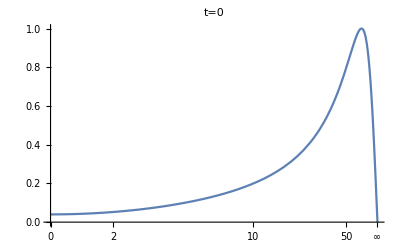
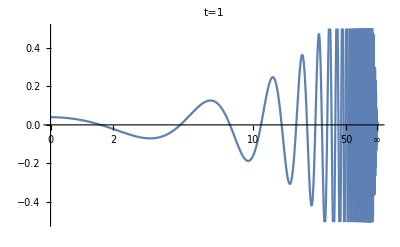
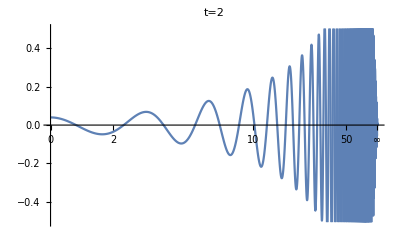
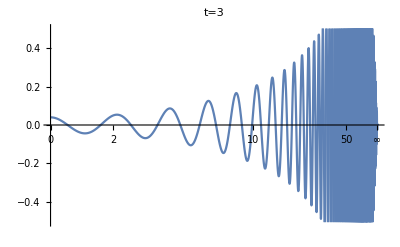

```mathematica
nγ=0.01;
nωc=100;
nT=1;

(*Integrand is highly oscillatory, especially as t increases*)

Table[Plot[(2 nγ ω nωc^2)/(ω^2+nωc^2)*Coth[ω/(2*nT)]*Cos[ω*t],{ω,0,Infinity},PlotLabel->"t="<>ToString[t]],{t,{0,1,2,3}}]
```

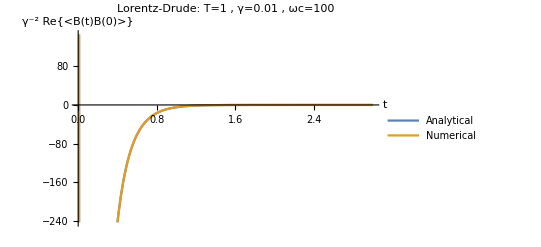

```mathematica
nγ=0.01;
nωc=100;
nT=1;

Plot[{nγ^-2*BathCorrelatorReAnalyticalJLorentzDrude[t,nT,nγ,nωc],nγ^-2*BathCorrelatorReNumericalJLorentzDrude[t,nT,nγ,nωc]},{t,0,3},PlotRange->Automatic,PlotLegends->{"Analytical","Numerical"},AxesLabel->{"t","γ^-2 Re{⟨B(t)B(0)⟩}"},PlotLabel->"Lorentz-Drude: T="<>ToString[nT]<>" , γ="<>ToString[nγ]<>" , ωc="<>ToString[nωc]]
```

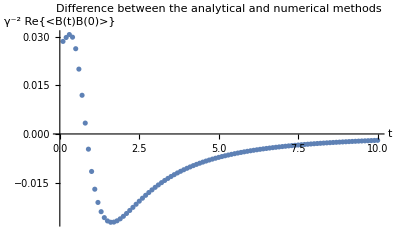

```mathematica
ListPlot[Table[{t,nγ^-2(BathCorrelatorReAnalyticalJLorentzDrude[t,nT,nγ,nωc]-BathCorrelatorReNumericalJLorentzDrude[t,nT,nγ,nωc])//Quiet},{t,0,10,0.1}],AxesLabel->{"t","γ^-2 Re{⟨B(t)B(0)⟩}"},PlotLabel->"Difference between the analytical and numerical methods"]
```

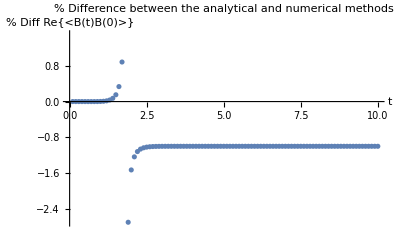

```mathematica
ListPlot[Table[{t,(BathCorrelatorReAnalyticalJLorentzDrude[t,nT,nγ,nωc]-BathCorrelatorReNumericalJLorentzDrude[t,nT,nγ,nωc])/BathCorrelatorReNumericalJLorentzDrude[t,nT,nγ,nωc]//Quiet},{t,0,10,0.1}],AxesLabel->{"t","% Diff Re{⟨B(t)B(0)⟩}"},PlotLabel->"% Difference between the analytical and numerical methods"]
```

Now to calculate the integrated bath correlation function: ∫_0^t Re{⟨B(s)B(0)⟩}ⅆs". Use the hypergeometric form:
Re{⟨B(t)B(0)⟩}= ⅇ^(-t ωc) γ ωc^2 Cot[ωc/(2 T)]+(4 ⅇ^(-2 π T t) π T^2 γ ωc Hypergeometric2F1[2,1-ωc/(2 π T),2-ωc/(2 π T),ⅇ^(-2 π t T)])/(2 π T-ωc)-(4 ⅇ^(-2 π T t) π T^2 γ ωc Hypergeometric2F1[2,1+ωc/(2 π T),2+ωc/(2 π T),ⅇ^(-2 π t T)])/(2 π T+ωc)\n\nand consi the cot and hypergeometric functions separately.

```mathematica
Integrate[ⅇ^(-s ωc) γ ωc^2 Cot[ωc/(2 T)],{s,0,t}]
```

(1-ⅇ^(-t ωc)) γ ωc Cot[ωc/(2 T)]

For the hypergeometric functions, let u=e^(-2πTs), then du=-2πT e^(-2πTs) ds

```mathematica
Integrate[(4 π T^2 γ ωc Hypergeometric2F1[2,1-ωc/(2 π T),2-ωc/(2 π T),u])/(-2πT(2 π T-ωc))-(4 π T^2 γ ωc Hypergeometric2F1[2,1+ωc/(2 π T),2+ωc/(2 π T),u])/(-2πT(2 π T+ωc)),{u,1,ⅇ^(-2πTt)}]
```

ConditionalExpression[-((ⅇ^(-2 πTt))^(-ωc/(2 π T)) T γ ωc ((ⅇ^(-2 πTt))^(ωc/(π T)) Beta[ⅇ^(-2 πTt),1-ωc/(2 π T),0]-Beta[ⅇ^(-2 πTt),1+ωc/(2 π T),0]))/πT-(π T γ (-2 T+ωc Cot[ωc/(2 T)]))/πT, ⅇ^(2 πTt)≥1]

```mathematica
IntegratedBathCorrelatorReAnalyticalJLorentzDrude[t_,T_,γ_,ωc_]:=If[t==0,0,γ (2 T+(T ωc)/π*ⅇ^(ωc t)*(-ⅇ^(-2 ωc t) *Beta[ⅇ^(-2 π T t),1-ωc/(2 π T),0]+Beta[ⅇ^(-2 π T t),1+ωc/(2 π T),0])-ⅇ^(-t ωc) ωc Cot[ωc/(2 T)])]

IntegratedBathCorrelatorReNumericalJLorentzDrude[t_,T_,γ_,ωc_]:=NIntegrate[BathCorrelatorReAnalyticalJLorentzDrude[s,T,γ,ωc],{s,0,t},Exclusions->{0},WorkingPrecision->10]

IntegratedBathCorrelatorReNumericalJLorentzDrude2[t_,T_,γ_ ,ωc_]:=1/Pi*NIntegrate[(2 γ ω ωc^2)/(ω^2+ωc^2)*Coth[ω/(2*T)]*Cos[ω*s],{ω,0,Infinity},{s,0,t}]
```

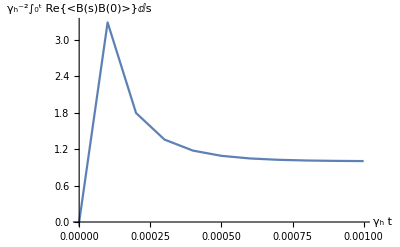

```mathematica
α1=10^-3;
α2=10^3;

γh=10^-3;
λ=Sqrt[α1*α2*γh];
ω0=Sqrt[α2*γh];

γcold=α1/(2*α2);

nT=1;

ListLinePlot[Table[{rt,γh^-2*IntegratedBathCorrelatorReNumericalJLorentzDrude[rt/γh,nT,γcold,α2]},{rt,0,0.001,0.001/10}],AxesLabel->{"γ_h t","γ_h^-2∫_0^t Re{⟨B(s)B(0)⟩}ⅆs"},PlotRange->All]
```

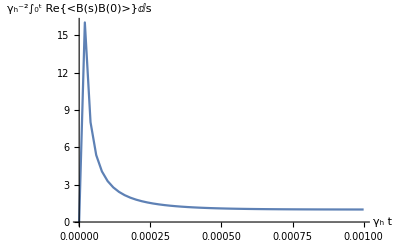

```mathematica
ListLinePlot[ParallelTable[{rt,γh^-2*IntegratedBathCorrelatorReNumericalJLorentzDrude2[rt/γh,nT,γcold,α2]},{rt,0,0.001,0.001/50}],AxesLabel->{"γ_h t","γ_h^-2∫_0^t Re{⟨B(s)B(0)⟩}ⅆs"},PlotRange->All]
```

General::munfl: -(2.59407×10^-305)/8281 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.93537×10^-305 0.000128348 is too small to represent as a normalized machine number; precision may be lost.

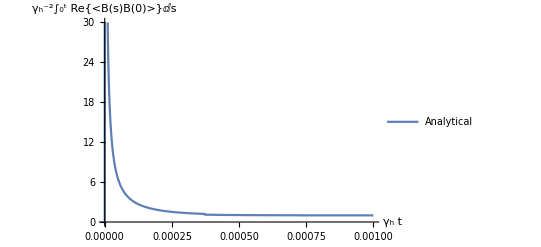

```mathematica
Plot[γh^-2*IntegratedBathCorrelatorReAnalyticalJLorentzDrude[t/γh,nT,γcold,α2]//N,{t,0,0.001},PlotLegends->{"Analytical"},AxesLabel->{"γ_h t","γ_h^-2∫_0^t Re{⟨B(s)B(0)⟩}ⅆs"},PlotRange->{0,30}]
```

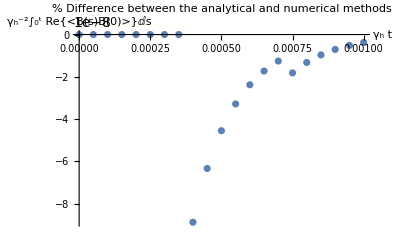

```mathematica
ListPlot[Table[{t,(IntegratedBathCorrelatorReAnalyticalJLorentzDrude[t/γh,nT,γcold,α2]-IntegratedBathCorrelatorReNumericalJLorentzDrude[t/γh,nT,γcold,α2])//Quiet},{t,0,0.001,0.001/20}],AxesLabel->{"γ_h t","γ_h^-2∫_0^t Re{⟨B(s)B(0)⟩}ⅆs"},PlotLabel->"% Difference between the analytical and numerical methods"]
```

```mathematica
nt=0.000001;
γh^-2*IntegratedBathCorrelatorReAnalyticalJLorentzDrude[nt/γh,nT,γcold,α2]//N
γh^-2*IntegratedBathCorrelatorReNumericalJLorentzDrude[nt/γh,nT,γcold,α2]
```

General::munfl: (5.65001×10^-307)/21904 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -3.90292×10^-308 0.00626349 is too small to represent as a normalized machine number; precision may be lost.

205.872

205.8715066

#### Imaginary part of the bath correlator

```mathematica
Assuming[t>0,-1/Pi*Integrate[JLorentzDrude[ω,γ,ωc]*Sin[ω*t],{ω,0,Infinity}]]
```

-ⅇ^(-t ωc) γ ωc^2

```mathematica
BathCorrelatorImAnalyticalJLorentzDrude[t_,γ_,ωc_]:=-ⅇ^(-t ωc) γ ωc^2
BathCorrelatorImNumericalJLorentzDrude[t_,γ_,ωc_]:=-1/Pi*NIntegrate[(2 γ ω ωc^2)/(ω^2+ωc^2)*Sin[ω*t],{ω,0,Infinity}]
```

```mathematica
BathCorrelatorImAnalyticalJLorentzDrude[1,2,3]//N 
BathCorrelatorImNumericalJLorentzDrude[1,2,3]//N
```

-0.896167

-0.896167

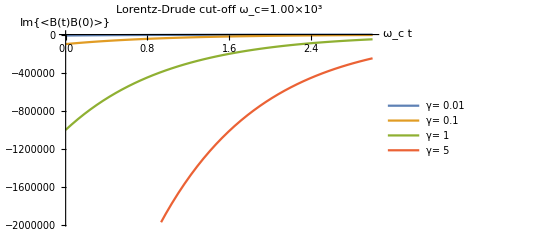

```mathematica
γlist={0.01,0.1,1,5};

nωc=1000;

Plot[Evaluate@Table[BathCorrelatorImAnalyticalJLorentzDrude[t/nωc,tγ,nωc],{tγ,γlist}],{t,0,3},PlotLegends->Table[StringForm["γ= ``",tγ],{tγ,γlist}],AxesLabel->{"ω_c t","Im{⟨B(t)B(0)⟩}"},PlotLabel->StringForm["Lorentz-Drude cut-off\n ω_c=``",ScientificForm[SetPrecision[nωc,3]]]]
```

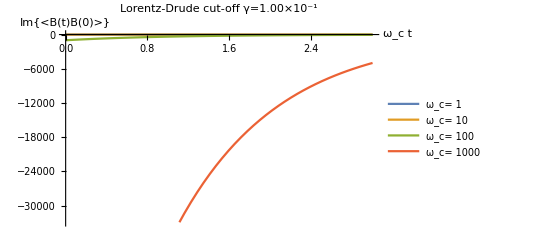

```mathematica
nγ=0.1;

ωclist={1,10,100,1000};

Plot[Evaluate@Table[BathCorrelatorImAnalyticalJLorentzDrude[t/tωc,nγ,tωc],{tωc,ωclist}],{t,0,3},PlotLegends->Table[StringForm["ω_c= ``",tωc],{tωc,ωclist}],AxesLabel->{"ω_c t","Im{⟨B(t)B(0)⟩}"},PlotLabel->StringForm["Lorentz-Drude cut-off\n γ=``",ScientificForm[SetPrecision[nγ,3]]]]
```

```mathematica
Integrate[BathCorrelatorImAnalyticalJLorentzDrude[s,γ,ωc],{s,0,t}]
```

(-1+ⅇ^(-t ωc)) γ ωc

```mathematica
IntegratedBathCorrelatorImAnalyticalJLorentzDrude[t_,γ_,ωc_]:=(-1+ⅇ^(-t ωc)) γ ωc
```

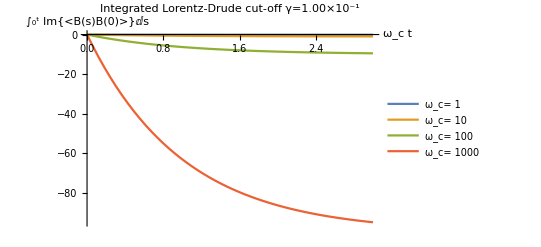

```mathematica
nγ=0.1;

ωclist={1,10,100,1000};

Plot[Evaluate@Table[IntegratedBathCorrelatorImAnalyticalJLorentzDrude[t/tωc,nγ,tωc],{tωc,ωclist}],{t,0,3},PlotLegends->Table[StringForm["ω_c= ``",tωc],{tωc,ωclist}],AxesLabel->{"ω_c t","∫_0^t Im{⟨B(s)B(0)⟩}ⅆs"},PlotLabel->StringForm["Integrated Lorentz-Drude cut-off\n γ=``",ScientificForm[SetPrecision[nγ,3]]]]
```

#### Total bath correlator

The total bath correlator 
⟨B(t)B(0)⟩ = 1/π∫_0^∞ J(ω)(coth(ω/(2T))cos(ωt)-ⅈ sin(ωt))ⅆω

can be split into two parts

⟨B(t)B(0)⟩ = 1/π∫_0^∞ J(ω)(2n(βω)cos(ωt)+ⅇ^-ⅈωt)ⅆω,

using coth(βω/2)=1+2n(βω), where n(βω)=(ⅇ^βω-1)^-1 is the Bose occupation number.

```mathematica
1/Pi*Integrate[JLorentzDrude[ω,γ,ωc]*Exp[-ⅈ ω*t],{ω,0,Infinity},Assumptions->t∈PositiveReals]
```

(-ⅈ ⅇ^(-t ωc) π γ ωc^2+√π γ ωc^2 MeijerG[{{0},{}},{{0,0},{1/2}},(t^2 ωc^2)/4])/π

```mathematica
1/Pi*Integrate[JLorentzDrude[ω,γ,ωc]*2/(Exp[ω/T]-1)*Exp[ⅈ ω*t],{ω,0,Infinity}]
```

(∫_0^∞ (4 ⅇ^(ⅈ t ω) γ ω ωc^2)/((-1+ⅇ^(ω/T)) (ω^2+ωc^2))ⅆω)/π

```mathematica
Integrate[2/(Exp[ω]-1)*Exp[ⅈ ω*t],{ω,0,Infinity}]
```

∫_0^∞ (2 ⅇ^(ⅈ t ω))/(-1+ⅇ^ω)ⅆω

Try using complex analysis, closing in the lower half plane (as t>0, -ⅈ(x+ⅈy)t=-ⅈ x t+yt, we want y<0 because as y->-∞ the integrand tends to 0).

```mathematica
FunctionPoles[JLorentzDrude[ω,γ,ωc]/(1-ⅇ^(-ω/T))*ⅇ^(-ⅈ ω t),ω]
```

FunctionPoles::avar: Warning: Assumptions that involve the variable ω are ignored.

{{-ⅈ ωc,1},{ⅈ ωc,1},{ConditionalExpression[2 ⅈ π T C[1], C[1]∈ℤ],1}}

```mathematica
Residue[JLorentzDrude[ω,γ,ωc]/(1-ⅇ^(-ω/T))*ⅇ^(-ⅈ ω t),{ω,-ⅈ ωc}]
```

-(ⅇ^(-t ωc) γ ωc^2)/(-1+ⅇ^((ⅈ ωc)/T))

```mathematica
ComplexExpand[ReIm[-(ⅇ^(-t ωc) γ ωc^2)/(-1+ⅇ^((ⅈ ωc)/T))]]//FullSimplify
```

{1/2 ⅇ^(-t ωc) γ ωc^2,1/2 ⅇ^(-t ωc) γ ωc^2 Cot[ωc/(2 T)]}

So the first term is
-2ⅈ 1/2 γω_c^2(1 + ⅈ Cot[ω_c/(2T)])ⅇ^-tω_c=γω_c^2(Cot[ω_c/(2T)]- ⅈ)ⅇ^-tω_c

```mathematica
Residue[JLorentzDrude[ω,γ,ωc]/(1-ⅇ^(-ω/T))*ⅇ^(-ⅈ ω t),{ω,-2 ⅈ π n T}]
```

(4 ⅈ ⅇ^(-2 ⅈ n π-2 n π t T) n π T^2 γ ωc^2)/(4 n^2 π^2 T^2-ωc^2)

```mathematica
FullSimplify[(4 ⅈ ⅇ^(-2 ⅈ n π-2 n π t T) n π T^2 γ ωc^2)/(4 n^2 π^2 T^2-ωc^2),n∈PositiveIntegers]
```

(4 ⅈ ⅇ^(-2 n π t T) n π T^2 γ ωc^2)/(4 n^2 π^2 T^2-ωc^2)

```mathematica
Sum[(4 ⅈ ⅇ^(-2 n π t T) n π T^2 γ ωc^2)/(4 n^2 π^2 T^2-ωc^2),{n,1,Infinity}]
```

(ⅈ ⅇ^(-2 π t T) γ ωc^2 (HurwitzLerchPhi[ⅇ^(-2 π t T),1,(2 π T-ωc)/(2 π T)]+LerchPhi[ⅇ^(-2 π t T),1,(2 π T+ωc)/(2 π T)]))/(2 π)

```mathematica
Sum[(4 ⅈ ⅇ^(-2 ⅈ n π-2 n π t T) n π T^2 γ ωc^2)/(4 n^2 π^2 T^2-ωc^2),{n,1,Infinity}]
```

1/(4 π^2 T^2-ωc^2)2 ⅈ ⅇ^(-2 π t T) π T^2 γ ωc (2 π T Hypergeometric2F1[2,1-ωc/(2 π T),2-ωc/(2 π T),ⅇ^(-2 π t T)]+ωc Hypergeometric2F1[2,1-ωc/(2 π T),2-ωc/(2 π T),ⅇ^(-2 π t T)]-2 π T Hypergeometric2F1[2,1+ωc/(2 π T),2+ωc/(2 π T),ⅇ^(-2 π t T)]+ωc Hypergeometric2F1[2,1+ωc/(2 π T),2+ωc/(2 π T),ⅇ^(-2 π t T)])

```mathematica
FullSimplify[-2 ⅈ (-(ⅇ^(-t ωc) γ ωc^2)/(-1+ⅇ^((ⅈ ωc)/T))+(ⅈ ⅇ^(-2 π t T) γ ωc^2 (HurwitzLerchPhi[ⅇ^(-2 π t T),1,(2 π T-ωc)/(2 π T)]+LerchPhi[ⅇ^(-2 π t T),1,(2 π T+ωc)/(2 π T)]))/(2 π))]
```

γ ωc^2 ((2 ⅈ ⅇ^(-t ωc))/(-1+ⅇ^((ⅈ ωc)/T))+(ⅇ^(-2 π t T) (HurwitzLerchPhi[ⅇ^(-2 π t T),1,1-ωc/(2 π T)]+LerchPhi[ⅇ^(-2 π t T),1,1+ωc/(2 π T)]))/π)

```mathematica
FullSimplify[-2 ⅈ (-(ⅇ^(-t ωc) γ ωc^2)/(-1+ⅇ^((ⅈ ωc)/T))+1/(4 π^2 T^2-ωc^2)2 ⅈ ⅇ^(-2 π t T) π T^2 γ ωc (2 π T Hypergeometric2F1[2,1-ωc/(2 π T),2-ωc/(2 π T),ⅇ^(-2 π t T)]+ωc Hypergeometric2F1[2,1-ωc/(2 π T),2-ωc/(2 π T),ⅇ^(-2 π t T)]-2 π T Hypergeometric2F1[2,1+ωc/(2 π T),2+ωc/(2 π T),ⅇ^(-2 π t T)]+ωc Hypergeometric2F1[2,1+ωc/(2 π T),2+ωc/(2 π T),ⅇ^(-2 π t T)]))]
```

2 ⅇ^(-t ωc) γ ωc ((ⅈ ωc)/(-1+ⅇ^((ⅈ ωc)/T))+T Beta[ⅇ^(-2 π t T),1-ωc/(2 π T),-1]-ⅇ^(2 t ωc) T Beta[ⅇ^(-2 π t T),1+ωc/(2 π T),-1])

```mathematica
BathCorrelatorAnalyticalJLorentzDrude[t_,T_,γ_,ωc_]:=γ ωc^2 ((2 ⅈ ⅇ^(-t ωc))/(-1+ⅇ^((ⅈ ωc)/T))+(ⅇ^(-2 π t T) (HurwitzLerchPhi[ⅇ^(-2 π t T),1,1-ωc/(2 π T)]+LerchPhi[ⅇ^(-2 π t T),1,1+ωc/(2 π T)]))/π)
BathCorrelatorAnalyticalJLorentzDrude2[t_,T_,γ_,ωc_]:=2 ⅇ^(-t ωc) γ ωc ((ⅈ ωc)/(-1+ⅇ^((ⅈ ωc)/T))+T Beta[ⅇ^(-2 π t T),1-ωc/(2 π T),-1]-ⅇ^(2 t ωc) T Beta[ⅇ^(-2 π t T),1+ωc/(2 π T),-1])
```

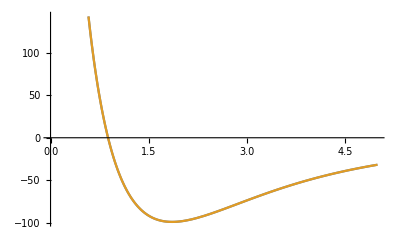

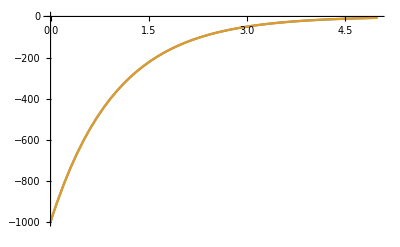

```mathematica
nT=1;
nγ=0.1;
nωc=100;

Plot[{Re@BathCorrelatorAnalyticalJLorentzDrude[t/nωc,nT,nγ,nωc],BathCorrelatorReAnalyticalJLorentzDrude[t/nωc,nT,nγ,nωc]},{t,0,5}]
Plot[{Im@BathCorrelatorAnalyticalJLorentzDrude[t/nωc,nT,nγ,nωc],BathCorrelatorImAnalyticalJLorentzDrude[t/nωc,nγ,nωc]},{t,0,5}]
```

```mathematica
nt=1;

Re@BathCorrelatorAnalyticalJLorentzDrude[nt/nωc,nT,nγ,nωc]-BathCorrelatorReAnalyticalJLorentzDrude[nt/nωc,nT,nγ,nωc]
Im@BathCorrelatorAnalyticalJLorentzDrude[nt/nωc,nT,nγ,nωc]-BathCorrelatorImAnalyticalJLorentzDrude[nt/nωc,nγ,nωc]
```

-2.46558×10^-12

-5.68434×10^-14

```mathematica
Plot[{Re@BathCorrelatorAnalyticalJLorentzDrude2[t/nωc,nT,nγ,nωc],BathCorrelatorReAnalyticalJLorentzDrude[t/nωc,nT,nγ,nωc]},{t,0,5}]
Plot[{Im@BathCorrelatorAnalyticalJLorentzDrude2[t/nωc,nT,nγ,nωc],BathCorrelatorImAnalyticalJLorentzDrude[t/nωc,nγ,nωc]},{t,0,5}]
```

-Graphics-

-Graphics-

```mathematica
nt=1;

Re@BathCorrelatorAnalyticalJLorentzDrude2[nt/nωc,nT,nγ,nωc]-BathCorrelatorReAnalyticalJLorentzDrude[nt/nωc,nT,nγ,nωc]
Im@BathCorrelatorAnalyticalJLorentzDrude2[nt/nωc,nT,nγ,nωc]-BathCorrelatorImAnalyticalJLorentzDrude[nt/nωc,nγ,nωc]
```

3.95417×10^-12

-1.13687×10^-13

### Spectral Density : Ohmic with Structured Lorentz-Drude cut-off

#### Real part of the bath correlator

Expand the cosh(ω/(2T)) as an infinite sum; cosh(ω/(2T))  = ∑_(n=-∞)^∞ (2Tω)/(ω^2+ν_n^2) where ν_n=2π T n.
Carry out the integral first, noting that ∫_0^∞ f(ω)cos(ωt)ⅆω=1/2∫_(-∞)^∞ f(ω) e^ⅈωt ⅆω, since f(ω) is a real and even function.

```mathematica
(*1/Pi*Integrate[(γ*λ^2*ω)/(γ^2*ω^2+(ω^2-ωs^2)^2) *(2*T*ω)/(ω^2+(2*Pi*T)^2*n^2)*Cos[ω*t],{ω,0,Infinity}]*) (*Takes too long to integrate*)
```

```mathematica
intexpr=1/Pi*Integrate[(γ*λ^2*ω)/(γ^2*ω^2+(ω^2-ωs^2)^2) *(2*T*ω)/(ω^2+(2*Pi*T)^2*n^2)*Cos[ω*t],{ω,0,Infinity}]
```

ConditionalExpression[ⅈ T γ λ^2 ((2 ⅈ ⅇ^(-2 n π t T) n π T)/(16 n^4 π^4 T^4+ωs^4-4 n^2 π^2 T^2 (γ^2-2 ωs^2))+(ⅈ √2 ⅇ^(-(t √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(√2)) √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(γ (γ^3-4 γ ωs^2+γ^2 √(γ^2-4 ωs^2)-2 √(γ^2-4 ωs^2) (4 n^2 π^2 T^2+ωs^2)))+(ⅇ^(-(t √(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(√2)) √(-2 γ^2+4 ωs^2+2 γ √(γ^2-4 ωs^2)))/(γ (γ^3-4 γ ωs^2-γ^2 √(γ^2-4 ωs^2)+2 √(γ^2-4 ωs^2) (4 n^2 π^2 T^2+ωs^2)))), ]

```mathematica
intexprsimp=intexpr[[1]]//FullSimplify
```

T λ^2 (-(2 ⅇ^(-2 n π t T) n π T γ)/(16 n^4 π^4 T^4+ωs^4-4 n^2 π^2 T^2 (γ^2-2 ωs^2))+(ⅈ ⅇ^(-(t √(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(√2)) √(4 ωs^2+2 γ (-γ+√(γ^2-4 ωs^2))))/(γ^3-4 γ ωs^2-γ^2 √(γ^2-4 ωs^2)+2 √(γ^2-4 ωs^2) (4 n^2 π^2 T^2+ωs^2))-(ⅇ^(-t √(-ωs^2+1/2 γ (γ+√(γ^2-4 ωs^2)))) √(-4 ωs^2+2 γ (γ+√(γ^2-4 ωs^2))))/(γ^3-4 γ ωs^2+γ^2 √(γ^2-4 ωs^2)-2 √(γ^2-4 ωs^2) (4 n^2 π^2 T^2+ωs^2)))

Mathematica can't seem to do the sum for all n at once, so split up for  n=0, and n>0.

```mathematica
intexprn0=intexprsimp /.n -> 0 // FullSimplify
```

(√2 T λ^2 ((ⅈ ⅇ^(-(t √(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(√2)))/(√(2 ωs^2+γ (-γ+√(γ^2-4 ωs^2))))-(ⅇ^(-t √(-ωs^2+1/2 γ (γ+√(γ^2-4 ωs^2)))))/(√(-2 ωs^2+γ (γ+√(γ^2-4 ωs^2))))))/(√(γ^2-4 ωs^2))

```mathematica
intexprn=FullSimplify[intexprsimp,Assumptions->n>0]
```

T λ^2 (-(2 ⅇ^(-2 n π t T) n π T γ)/(16 n^4 π^4 T^4+ωs^4-4 n^2 π^2 T^2 (γ^2-2 ωs^2))+(ⅈ ⅇ^(-(t √(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(√2)) √(4 ωs^2+2 γ (-γ+√(γ^2-4 ωs^2))))/(γ^3-4 γ ωs^2-γ^2 √(γ^2-4 ωs^2)+2 √(γ^2-4 ωs^2) (4 n^2 π^2 T^2+ωs^2))-(ⅇ^(-t √(-ωs^2+1/2 γ (γ+√(γ^2-4 ωs^2)))) √(-4 ωs^2+2 γ (γ+√(γ^2-4 ωs^2))))/(γ^3-4 γ ωs^2+γ^2 √(γ^2-4 ωs^2)-2 √(γ^2-4 ωs^2) (4 n^2 π^2 T^2+ωs^2)))

```mathematica
sumintexprn=Sum[intexprn,{n,1,Infinity}]//Simplify
```

-((ⅇ^(-2 π t T-(t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) λ^2 (-32 √2 ⅇ^(2 π t T+(t √(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(√2)) π^4 T^5 γ^2 √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))+8 √2 ⅇ^(2 π t T+(t √(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(√2)) π^2 T^3 γ^4 √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))+64 √2 ⅇ^(2 π t T+(t √(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(√2)) π^4 T^5 ωs^2 √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))-32 √2 ⅇ^(2 π t T+(t √(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(√2)) π^2 T^3 γ^2 ωs^2 √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))+32 √2 ⅇ^(2 π t T+(t √(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(√2)) π^2 T^3 ωs^4 √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))-2 √2 ⅇ^(2 π t T+(t √(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(√2)) T γ^2 ωs^4 √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))+4 √2 ⅇ^(2 π t T+(t √(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(√2)) T ωs^6 √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))+32 √2 ⅇ^(2 π t T+(t √(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(√2)) π^4 T^5 γ √(γ^2-4 ωs^2) √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))-8 √2 ⅇ^(2 π t T+(t √(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(√2)) π^2 T^3 γ^3 √(γ^2-4 ωs^2) √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))+16 √2 ⅇ^(2 π t T+(t √(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(√2)) π^2 T^3 γ ωs^2 √(γ^2-4 ωs^2) √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))+2 √2 ⅇ^(2 π t T+(t √(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(√2)) T γ ωs^4 √(γ^2-4 ωs^2) √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))-32 ⅈ √2 ⅇ^(2 π t T+(t √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(√2)) π^4 T^5 γ √(γ^2-4 ωs^2) √(-γ^2+2 ωs^2+γ √(γ^2-4 ωs^2))+8 ⅈ √2 ⅇ^(2 π t T+(t √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(√2)) π^2 T^3 γ^3 √(γ^2-4 ωs^2) √(-γ^2+2 ωs^2+γ √(γ^2-4 ωs^2))-16 ⅈ √2 ⅇ^(2 π t T+(t √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(√2)) π^2 T^3 γ ωs^2 √(γ^2-4 ωs^2) √(-γ^2+2 ωs^2+γ √(γ^2-4 ωs^2))-2 ⅈ √2 ⅇ^(2 π t T+(t √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(√2)) T γ ωs^4 √(γ^2-4 ωs^2) √(-γ^2+2 ωs^2+γ √(γ^2-4 ωs^2))-32 ⅈ ⅇ^(2 π t T+(t √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(√2)) π^4 T^5 γ^2 √(-2 γ^2+4 ωs^2+2 γ √(γ^2-4 ωs^2))+8 ⅈ ⅇ^(2 π t T+(t √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(√2)) π^2 T^3 γ^4 √(-2 γ^2+4 ωs^2+2 γ √(γ^2-4 ωs^2))+64 ⅈ ⅇ^(2 π t T+(t √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(√2)) π^4 T^5 ωs^2 √(-2 γ^2+4 ωs^2+2 γ √(γ^2-4 ωs^2))-32 ⅈ ⅇ^(2 π t T+(t √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(√2)) π^2 T^3 γ^2 ωs^2 √(-2 γ^2+4 ωs^2+2 γ √(γ^2-4 ωs^2))+32 ⅈ ⅇ^(2 π t T+(t √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(√2)) π^2 T^3 ωs^4 √(-2 γ^2+4 ωs^2+2 γ √(γ^2-4 ωs^2))-2 ⅈ ⅇ^(2 π t T+(t √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(√2)) T γ^2 ωs^4 √(-2 γ^2+4 ωs^2+2 γ √(γ^2-4 ωs^2))+4 ⅈ ⅇ^(2 π t T+(t √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(√2)) T ωs^6 √(-2 γ^2+4 ωs^2+2 γ √(γ^2-4 ωs^2))+16 ⅈ ⅇ^(2 π t T+(t √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(√2)) π^4 T^4 γ^2 √(-2 γ^4+8 γ^2 ωs^2-4 ωs^4+2 γ^3 √(γ^2-4 ωs^2)-4 γ ωs^2 √(γ^2-4 ωs^2)) Cot[(√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(2 √2 T)]-4 ⅈ ⅇ^(2 π t T+(t √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(√2)) π^2 T^2 γ^4 √(-2 γ^4+8 γ^2 ωs^2-4 ωs^4+2 γ^3 √(γ^2-4 ωs^2)-4 γ ωs^2 √(γ^2-4 ωs^2)) Cot[(√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(2 √2 T)]-32 ⅈ ⅇ^(2 π t T+(t √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(√2)) π^4 T^4 ωs^2 √(-2 γ^4+8 γ^2 ωs^2-4 ωs^4+2 γ^3 √(γ^2-4 ωs^2)-4 γ ωs^2 √(γ^2-4 ωs^2)) Cot[(√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(2 √2 T)]+16 ⅈ ⅇ^(2 π t T+(t √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(√2)) π^2 T^2 γ^2 ωs^2 √(-2 γ^4+8 γ^2 ωs^2-4 ωs^4+2 γ^3 √(γ^2-4 ωs^2)-4 γ ωs^2 √(γ^2-4 ωs^2)) Cot[(√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(2 √2 T)]-16 ⅈ ⅇ^(2 π t T+(t √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(√2)) π^2 T^2 ωs^4 √(-2 γ^4+8 γ^2 ωs^2-4 ωs^4+2 γ^3 √(γ^2-4 ωs^2)-4 γ ωs^2 √(γ^2-4 ωs^2)) Cot[(√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(2 √2 T)]+ⅈ ⅇ^(2 π t T+(t √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(√2)) γ^2 ωs^4 √(-2 γ^4+8 γ^2 ωs^2-4 ωs^4+2 γ^3 √(γ^2-4 ωs^2)-4 γ ωs^2 √(γ^2-4 ωs^2)) Cot[(√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(2 √2 T)]-2 ⅈ ⅇ^(2 π t T+(t √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(√2)) ωs^6 √(-2 γ^4+8 γ^2 ωs^2-4 ωs^4+2 γ^3 √(γ^2-4 ωs^2)-4 γ ωs^2 √(γ^2-4 ωs^2)) Cot[(√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(2 √2 T)]+16 ⅈ √2 ⅇ^(2 π t T+(t √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(√2)) π^4 T^4 γ √(γ^2-4 ωs^2) √(-γ^4+4 γ^2 ωs^2-2 ωs^4+γ^3 √(γ^2-4 ωs^2)-2 γ ωs^2 √(γ^2-4 ωs^2)) Cot[(√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(2 √2 T)]-4 ⅈ √2 ⅇ^(2 π t T+(t √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(√2)) π^2 T^2 γ^3 √(γ^2-4 ωs^2) √(-γ^4+4 γ^2 ωs^2-2 ωs^4+γ^3 √(γ^2-4 ωs^2)-2 γ ωs^2 √(γ^2-4 ωs^2)) Cot[(√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(2 √2 T)]+8 ⅈ √2 ⅇ^(2 π t T+(t √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(√2)) π^2 T^2 γ ωs^2 √(γ^2-4 ωs^2) √(-γ^4+4 γ^2 ωs^2-2 ωs^4+γ^3 √(γ^2-4 ωs^2)-2 γ ωs^2 √(γ^2-4 ωs^2)) Cot[(√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(2 √2 T)]+ⅈ √2 ⅇ^(2 π t T+(t √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(√2)) γ ωs^4 √(γ^2-4 ωs^2) √(-γ^4+4 γ^2 ωs^2-2 ωs^4+γ^3 √(γ^2-4 ωs^2)-2 γ ωs^2 √(γ^2-4 ωs^2)) Cot[(√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(2 √2 T)]+64 ⅇ^(2 π t T+(t √(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(√2)) π^4 T^4 ωs^4 Cot[(√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(2 √2 T)]-16 ⅇ^(2 π t T+(t √(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(√2)) π^2 T^2 γ^2 ωs^4 Cot[(√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(2 √2 T)]+32 ⅇ^(2 π t T+(t √(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(√2)) π^2 T^2 ωs^6 Cot[(√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(2 √2 T)]+4 ⅇ^(2 π t T+(t √(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(√2)) ωs^8 Cot[(√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(2 √2 T)]+8 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π T^2 ωs^2 (4 π^2 T^2-2 π T γ+ωs^2) (γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)+2 π T (γ+√(γ^2-4 ωs^2))) Hypergeometric2F1[2,(4 π T+γ-√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ-√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+8 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π T^2 ωs^2 (4 π^2 T^2+2 π T γ+ωs^2) (γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)-2 π T (γ+√(γ^2-4 ωs^2))) Hypergeometric2F1[2,(4 π T-γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T-γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+64 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π^4 T^5 γ ωs^2 Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-16 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π^2 T^3 γ^3 ωs^2 Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+64 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π^3 T^4 ωs^4 Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+48 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π^2 T^3 γ ωs^4 Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-8 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π T^2 γ^2 ωs^4 Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+16 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π T^2 ωs^6 Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-64 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π^4 T^5 ωs^2 √(γ^2-4 ωs^2) Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+16 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π^2 T^3 γ^2 ωs^2 √(γ^2-4 ωs^2) Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-16 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π^2 T^3 ωs^4 √(γ^2-4 ωs^2) Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+8 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π T^2 γ ωs^4 √(γ^2-4 ωs^2) Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-64 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π^4 T^5 γ ωs^2 Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+16 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π^2 T^3 γ^3 ωs^2 Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+64 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π^3 T^4 ωs^4 Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-48 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π^2 T^3 γ ωs^4 Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-8 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π T^2 γ^2 ωs^4 Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+16 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π T^2 ωs^6 Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+64 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π^4 T^5 ωs^2 √(γ^2-4 ωs^2) Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-16 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π^2 T^3 γ^2 ωs^2 √(γ^2-4 ωs^2) Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+16 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π^2 T^3 ωs^4 √(γ^2-4 ωs^2) Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+8 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π T^2 γ ωs^4 √(γ^2-4 ωs^2) Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]))/(16 ωs^4 √(γ^2-4 ωs^2) (16 π^4 T^4+ωs^4-4 π^2 T^2 (γ^2-2 ωs^2))))

```mathematica
intexprn0+2*sumintexprn//Simplify
```

-((ⅇ^(-2 π t T-(t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) λ^2 (16 ⅈ ⅇ^(2 π t T+(t √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(√2)) π^4 T^4 γ^2 √(-2 γ^4+8 γ^2 ωs^2-4 ωs^4+2 γ^3 √(γ^2-4 ωs^2)-4 γ ωs^2 √(γ^2-4 ωs^2)) Cot[(√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(2 √2 T)]-4 ⅈ ⅇ^(2 π t T+(t √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(√2)) π^2 T^2 γ^4 √(-2 γ^4+8 γ^2 ωs^2-4 ωs^4+2 γ^3 √(γ^2-4 ωs^2)-4 γ ωs^2 √(γ^2-4 ωs^2)) Cot[(√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(2 √2 T)]-32 ⅈ ⅇ^(2 π t T+(t √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(√2)) π^4 T^4 ωs^2 √(-2 γ^4+8 γ^2 ωs^2-4 ωs^4+2 γ^3 √(γ^2-4 ωs^2)-4 γ ωs^2 √(γ^2-4 ωs^2)) Cot[(√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(2 √2 T)]+16 ⅈ ⅇ^(2 π t T+(t √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(√2)) π^2 T^2 γ^2 ωs^2 √(-2 γ^4+8 γ^2 ωs^2-4 ωs^4+2 γ^3 √(γ^2-4 ωs^2)-4 γ ωs^2 √(γ^2-4 ωs^2)) Cot[(√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(2 √2 T)]-16 ⅈ ⅇ^(2 π t T+(t √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(√2)) π^2 T^2 ωs^4 √(-2 γ^4+8 γ^2 ωs^2-4 ωs^4+2 γ^3 √(γ^2-4 ωs^2)-4 γ ωs^2 √(γ^2-4 ωs^2)) Cot[(√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(2 √2 T)]+ⅈ ⅇ^(2 π t T+(t √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(√2)) γ^2 ωs^4 √(-2 γ^4+8 γ^2 ωs^2-4 ωs^4+2 γ^3 √(γ^2-4 ωs^2)-4 γ ωs^2 √(γ^2-4 ωs^2)) Cot[(√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(2 √2 T)]-2 ⅈ ⅇ^(2 π t T+(t √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(√2)) ωs^6 √(-2 γ^4+8 γ^2 ωs^2-4 ωs^4+2 γ^3 √(γ^2-4 ωs^2)-4 γ ωs^2 √(γ^2-4 ωs^2)) Cot[(√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(2 √2 T)]+16 ⅈ √2 ⅇ^(2 π t T+(t √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(√2)) π^4 T^4 γ √(γ^2-4 ωs^2) √(-γ^4+4 γ^2 ωs^2-2 ωs^4+γ^3 √(γ^2-4 ωs^2)-2 γ ωs^2 √(γ^2-4 ωs^2)) Cot[(√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(2 √2 T)]-4 ⅈ √2 ⅇ^(2 π t T+(t √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(√2)) π^2 T^2 γ^3 √(γ^2-4 ωs^2) √(-γ^4+4 γ^2 ωs^2-2 ωs^4+γ^3 √(γ^2-4 ωs^2)-2 γ ωs^2 √(γ^2-4 ωs^2)) Cot[(√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(2 √2 T)]+8 ⅈ √2 ⅇ^(2 π t T+(t √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(√2)) π^2 T^2 γ ωs^2 √(γ^2-4 ωs^2) √(-γ^4+4 γ^2 ωs^2-2 ωs^4+γ^3 √(γ^2-4 ωs^2)-2 γ ωs^2 √(γ^2-4 ωs^2)) Cot[(√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(2 √2 T)]+ⅈ √2 ⅇ^(2 π t T+(t √(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(√2)) γ ωs^4 √(γ^2-4 ωs^2) √(-γ^4+4 γ^2 ωs^2-2 ωs^4+γ^3 √(γ^2-4 ωs^2)-2 γ ωs^2 √(γ^2-4 ωs^2)) Cot[(√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(2 √2 T)]+64 ⅇ^(2 π t T+(t √(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(√2)) π^4 T^4 ωs^4 Cot[(√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(2 √2 T)]-16 ⅇ^(2 π t T+(t √(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(√2)) π^2 T^2 γ^2 ωs^4 Cot[(√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(2 √2 T)]+32 ⅇ^(2 π t T+(t √(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(√2)) π^2 T^2 ωs^6 Cot[(√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(2 √2 T)]+4 ⅇ^(2 π t T+(t √(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(√2)) ωs^8 Cot[(√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)))/(2 √2 T)]+8 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π T^2 ωs^2 (4 π^2 T^2-2 π T γ+ωs^2) (γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)+2 π T (γ+√(γ^2-4 ωs^2))) Hypergeometric2F1[2,(4 π T+γ-√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ-√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+8 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π T^2 ωs^2 (4 π^2 T^2+2 π T γ+ωs^2) (γ^2-2 ωs^2+γ √(γ^2-4 ωs^2)-2 π T (γ+√(γ^2-4 ωs^2))) Hypergeometric2F1[2,(4 π T-γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T-γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+64 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π^4 T^5 γ ωs^2 Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-16 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π^2 T^3 γ^3 ωs^2 Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+64 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π^3 T^4 ωs^4 Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+48 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π^2 T^3 γ ωs^4 Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-8 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π T^2 γ^2 ωs^4 Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+16 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π T^2 ωs^6 Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-64 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π^4 T^5 ωs^2 √(γ^2-4 ωs^2) Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+16 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π^2 T^3 γ^2 ωs^2 √(γ^2-4 ωs^2) Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-16 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π^2 T^3 ωs^4 √(γ^2-4 ωs^2) Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+8 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π T^2 γ ωs^4 √(γ^2-4 ωs^2) Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-64 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π^4 T^5 γ ωs^2 Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+16 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π^2 T^3 γ^3 ωs^2 Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+64 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π^3 T^4 ωs^4 Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-48 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π^2 T^3 γ ωs^4 Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-8 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π T^2 γ^2 ωs^4 Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+16 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π T^2 ωs^6 Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+64 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π^4 T^5 ωs^2 √(γ^2-4 ωs^2) Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-16 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π^2 T^3 γ^2 ωs^2 √(γ^2-4 ωs^2) Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+16 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π^2 T^3 ωs^4 √(γ^2-4 ωs^2) Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+8 ⅇ^((t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(γ^2-2 ωs^2+γ √(γ^2-4 ωs^2))))/(√2)) π T^2 γ ωs^4 √(γ^2-4 ωs^2) Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]))/(8 ωs^4 √(γ^2-4 ωs^2) (16 π^4 T^4+ωs^4-4 π^2 T^2 (γ^2-2 ωs^2))))

```mathematica
BathCorrelatorReAnalyticalJStructuredLorentzDrude[t_,T_,γ_ ,λ_,ωs_]:=1/(8 √(γ^2-4 ωs^2))λ^2 ((4 ⅇ^(-2 π t T) T (4 π T+γ+√(γ^2-4 ωs^2)) Hypergeometric2F1[1,(4 π T+γ-√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ-√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)])/(2 π T (2 π T+γ)+ωs^2)-(4 ⅇ^(-2 π t T) T (-4 π T+γ+√(γ^2-4 ωs^2)) Hypergeometric2F1[1,(4 π T-γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T-γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)])/(2 π T (2 π T-γ)+ωs^2)+4 ⅇ^(-2 π t T) T (((4 π T-γ+√(γ^2-4 ωs^2)) Hypergeometric2F1[1,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)])/(2 π T (-2 π T+γ)-ωs^2)+((-4 π T-γ+√(γ^2-4 ωs^2)) Hypergeometric2F1[1,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)])/(2 π T (2 π T+γ)+ωs^2))-1/ωs^4 ⅈ ⅇ^(-(t (√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2))+√(-2 ωs^2+γ (γ+√(γ^2-4 ωs^2)))))/(√2)) (√(-2 γ^4+8 γ^2 ωs^2-4 ωs^4+2 γ^3 √(γ^2-4 ωs^2)-4 γ ωs^2 √(γ^2-4 ωs^2)) (-2 ωs^2+γ (γ+√(γ^2-4 ωs^2))) Cosh[t √(-ωs^2+1/2 γ (γ+√(γ^2-4 ωs^2)))] Cot[(√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(2 √2 T)]-4 ⅈ ⅇ^((t √(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(√2)) ωs^4 Cot[(√(-ωs^2+1/2 γ (γ+√(γ^2-4 ωs^2))))/(2 T)]+√(-2 γ^4+8 γ^2 ωs^2-4 ωs^4+2 γ^3 √(γ^2-4 ωs^2)-4 γ ωs^2 √(γ^2-4 ωs^2)) (-2 ωs^2+γ (γ+√(γ^2-4 ωs^2))) Cot[(√(γ^2-2 ωs^2-γ √(γ^2-4 ωs^2)))/(2 √2 T)] Sinh[t √(-ωs^2+1/2 γ (γ+√(γ^2-4 ωs^2)))]))

BathCorrelatorReNumericalJStructuredLorentzDrude[t_,T_,γ_ ,λ_,ωs_]:=1/Pi*NIntegrate[(γ*λ^2*ω)/(γ^2*ω^2+(ω^2-ωs^2)^2) *Coth[ω/(2*T)]*Cos[ω*t],{ω,0,Infinity}] 

BathCorrelatorReNumericalJStructuredLorentzDrude2[t_,T_,γ_ ,λ_,ωs_]:=1/Pi*NIntegrate[(γ*λ^2*ω)/(γ^2*ω^2+(ω^2-ωs^2)^2) *Coth[ω/(2*T)]*Cos[ω*t],{ω,0,Infinity},Method->"ExtrapolatingOscillatory"] (*Method->"ExtrapolatingOscillatory" For short times*)
```

Try a different way, using complex analysis and Cauchy's Residue Theorem. We will choose a contour along x ∈ [-∞,∞] and will close in the upper-half plane.

```mathematica
FunctionPoles[(γ λ^2 ω)/(((ω^2-ωs^2)-ⅈ γ ω)((ω^2-ωs^2)+ⅈ γ ω))*(2*T*ω)/(ω^2+(2*Pi*T)^2*n^2),ω]
```

FunctionPoles::avar: Warning: Assumptions that involve the variable ω are ignored.

{{ConditionalExpression[0, n==0],Indeterminate},{ConditionalExpression[-2 ⅈ n π T, n≥1],1},{ConditionalExpression[2 ⅈ n π T, n≤-1],1},{ConditionalExpression[2 ⅈ n π T, n≥1],1},{ConditionalExpression[-2 ⅈ n π T, n≤-1],1},{ConditionalExpression[ⅈ (-γ/2-1/2 √(γ^2-4 ωs^2)), γ>2 ωs],1},{ConditionalExpression[ⅈ (γ/2-1/2 √(γ^2-4 ωs^2)), γ>2 ωs],1},{ConditionalExpression[ⅈ (-γ/2+1/2 √(γ^2-4 ωs^2)), γ>2 ωs],1},{ConditionalExpression[ⅈ (γ/2+1/2 √(γ^2-4 ωs^2)), γ>2 ωs],1},{ConditionalExpression[-(ⅈ γ)/2-1/2 √(-γ^2+4 ωs^2), γ==2 ωs],1},{ConditionalExpression[-(ⅈ γ)/2-1/2 √(-γ^2+4 ωs^2), γ<2 ωs],1},{ConditionalExpression[(ⅈ γ)/2-1/2 √(-γ^2+4 ωs^2), γ==2 ωs],1},{ConditionalExpression[(ⅈ γ)/2-1/2 √(-γ^2+4 ωs^2), γ<2 ωs],1},{ConditionalExpression[-(ⅈ γ)/2+1/2 √(-γ^2+4 ωs^2), γ<2 ωs],1},{ConditionalExpression[(ⅈ γ)/2+1/2 √(-γ^2+4 ωs^2), γ<2 ωs],1}}

We then choose all poles with a positive imaginary part, and where γ/2<ω_s. Also divide by 2π- the factor of 2 as we only want x ∈ [0,∞], and π from the formula of the bath correlation function.

```mathematica
intexpr=FullSimplify[ ⅈ(Residue[(γ λ^2 ω)/(((ω^2-ωs^2)-ⅈ γ ω)((ω^2-ωs^2)+ⅈ γ ω))*(2*T*ω)/(ω^2+(2*Pi*T)^2*n^2)*Exp[ⅈ ω t],{ω,2 ⅈ n π T}]+Residue[(γ λ^2 ω)/(((ω^2-ωs^2)-ⅈ γ ω)((ω^2-ωs^2)+ⅈ γ ω))*(2*T*ω)/(ω^2+(2*Pi*T)^2*n^2)*Exp[ⅈ ω t],{ω,(ⅈ γ)/2-1/2 √(-γ^2+4 ωs^2)}]+Residue[(γ λ^2 ω)/(((ω^2-ωs^2)-ⅈ γ ω)((ω^2-ωs^2)+ⅈ γ ω))*(2*T*ω)/(ω^2+(2*Pi*T)^2*n^2)*Exp[ⅈ ω t],{ω,(ⅈ γ)/2+1/2 √(-γ^2+4 ωs^2)}])]
```

ⅈ T λ^2 ((2 ⅈ ⅇ^(-2 n π t T) n π T γ)/(16 n^4 π^4 T^4+ωs^4-4 n^2 π^2 T^2 (γ^2-2 ωs^2))-(ⅈ ⅇ^(1/2 ⅈ t (ⅈ γ+√(-γ^2+4 ωs^2))) (ⅈ γ+√(-γ^2+4 ωs^2)))/(√(-γ^2+4 ωs^2) (8 n^2 π^2 T^2-γ^2+2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)))+(ⅇ^(-1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) (-ⅈ γ+√(-γ^2+4 ωs^2)))/(√(-γ^2+4 ωs^2) (8 ⅈ n^2 π^2 T^2+2 ⅈ ωs^2+γ (-ⅈ γ+√(-γ^2+4 ωs^2)))))

Also note that we will need to take the real part of this expression (was cos ωt), but the imaginary part will equal 0 as it is an odd function.

```mathematica
sumexpr=Sum[intexpr,{n,1,Infinity}]
```

(ⅇ^(-2 π t T-1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) λ^2 (64 ⅈ ⅇ^(2 π t T) π^4 T^7 γ ωs^4 √(T^2 (γ^2-4 ωs^2))-64 ⅈ ⅇ^(2 π t T+1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))+1/2 ⅈ t (ⅈ γ+√(-γ^2+4 ωs^2))) π^4 T^7 γ ωs^4 √(T^2 (γ^2-4 ωs^2))-16 ⅈ ⅇ^(2 π t T) π^2 T^5 γ^3 ωs^4 √(T^2 (γ^2-4 ωs^2))+16 ⅈ ⅇ^(2 π t T+1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))+1/2 ⅈ t (ⅈ γ+√(-γ^2+4 ωs^2))) π^2 T^5 γ^3 ωs^4 √(T^2 (γ^2-4 ωs^2))+32 ⅈ ⅇ^(2 π t T) π^2 T^5 γ ωs^6 √(T^2 (γ^2-4 ωs^2))-32 ⅈ ⅇ^(2 π t T+1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))+1/2 ⅈ t (ⅈ γ+√(-γ^2+4 ωs^2))) π^2 T^5 γ ωs^6 √(T^2 (γ^2-4 ωs^2))+4 ⅈ ⅇ^(2 π t T) T^3 γ ωs^8 √(T^2 (γ^2-4 ωs^2))-4 ⅈ ⅇ^(2 π t T+1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))+1/2 ⅈ t (ⅈ γ+√(-γ^2+4 ωs^2))) T^3 γ ωs^8 √(T^2 (γ^2-4 ωs^2))+64 ⅇ^(2 π t T) π^4 T^7 ωs^4 √(T^2 (γ^2-4 ωs^2)) √(-γ^2+4 ωs^2)+64 ⅇ^(2 π t T+1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))+1/2 ⅈ t (ⅈ γ+√(-γ^2+4 ωs^2))) π^4 T^7 ωs^4 √(T^2 (γ^2-4 ωs^2)) √(-γ^2+4 ωs^2)-16 ⅇ^(2 π t T) π^2 T^5 γ^2 ωs^4 √(T^2 (γ^2-4 ωs^2)) √(-γ^2+4 ωs^2)-16 ⅇ^(2 π t T+1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))+1/2 ⅈ t (ⅈ γ+√(-γ^2+4 ωs^2))) π^2 T^5 γ^2 ωs^4 √(T^2 (γ^2-4 ωs^2)) √(-γ^2+4 ωs^2)+32 ⅇ^(2 π t T) π^2 T^5 ωs^6 √(T^2 (γ^2-4 ωs^2)) √(-γ^2+4 ωs^2)+32 ⅇ^(2 π t T+1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))+1/2 ⅈ t (ⅈ γ+√(-γ^2+4 ωs^2))) π^2 T^5 ωs^6 √(T^2 (γ^2-4 ωs^2)) √(-γ^2+4 ωs^2)+4 ⅇ^(2 π t T) T^3 ωs^8 √(T^2 (γ^2-4 ωs^2)) √(-γ^2+4 ωs^2)+4 ⅇ^(2 π t T+1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))+1/2 ⅈ t (ⅈ γ+√(-γ^2+4 ωs^2))) T^3 ωs^8 √(T^2 (γ^2-4 ωs^2)) √(-γ^2+4 ωs^2)+16 ⅈ √2 ⅇ^(2 π t T+1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))+1/2 ⅈ t (ⅈ γ+√(-γ^2+4 ωs^2))) π^4 T^6 γ ωs^4 √(T^2 (γ^2-4 ωs^2)) √(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]-4 ⅈ √2 ⅇ^(2 π t T+1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))+1/2 ⅈ t (ⅈ γ+√(-γ^2+4 ωs^2))) π^2 T^4 γ^3 ωs^4 √(T^2 (γ^2-4 ωs^2)) √(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]+8 ⅈ √2 ⅇ^(2 π t T+1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))+1/2 ⅈ t (ⅈ γ+√(-γ^2+4 ωs^2))) π^2 T^4 γ ωs^6 √(T^2 (γ^2-4 ωs^2)) √(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]+ⅈ √2 ⅇ^(2 π t T+1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))+1/2 ⅈ t (ⅈ γ+√(-γ^2+4 ωs^2))) T^2 γ ωs^8 √(T^2 (γ^2-4 ωs^2)) √(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]-16 √2 ⅇ^(2 π t T+1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))+1/2 ⅈ t (ⅈ γ+√(-γ^2+4 ωs^2))) π^4 T^6 ωs^4 √(T^2 (γ^2-4 ωs^2)) √(-γ^2+4 ωs^2) √(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]+4 √2 ⅇ^(2 π t T+1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))+1/2 ⅈ t (ⅈ γ+√(-γ^2+4 ωs^2))) π^2 T^4 γ^2 ωs^4 √(T^2 (γ^2-4 ωs^2)) √(-γ^2+4 ωs^2) √(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]-8 √2 ⅇ^(2 π t T+1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))+1/2 ⅈ t (ⅈ γ+√(-γ^2+4 ωs^2))) π^2 T^4 ωs^6 √(T^2 (γ^2-4 ωs^2)) √(-γ^2+4 ωs^2) √(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]-√2 ⅇ^(2 π t T+1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))+1/2 ⅈ t (ⅈ γ+√(-γ^2+4 ωs^2))) T^2 ωs^8 √(T^2 (γ^2-4 ωs^2)) √(-γ^2+4 ωs^2) √(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]-16 ⅈ √2 ⅇ^(2 π t T) π^4 T^6 γ ωs^4 √(T^2 (γ^2-4 ωs^2)) √(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]+4 ⅈ √2 ⅇ^(2 π t T) π^2 T^4 γ^3 ωs^4 √(T^2 (γ^2-4 ωs^2)) √(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]-8 ⅈ √2 ⅇ^(2 π t T) π^2 T^4 γ ωs^6 √(T^2 (γ^2-4 ωs^2)) √(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]-ⅈ √2 ⅇ^(2 π t T) T^2 γ ωs^8 √(T^2 (γ^2-4 ωs^2)) √(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]-16 √2 ⅇ^(2 π t T) π^4 T^6 ωs^4 √(T^2 (γ^2-4 ωs^2)) √(-γ^2+4 ωs^2) √(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]+4 √2 ⅇ^(2 π t T) π^2 T^4 γ^2 ωs^4 √(T^2 (γ^2-4 ωs^2)) √(-γ^2+4 ωs^2) √(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]-8 √2 ⅇ^(2 π t T) π^2 T^4 ωs^6 √(T^2 (γ^2-4 ωs^2)) √(-γ^2+4 ωs^2) √(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]-√2 ⅇ^(2 π t T) T^2 ωs^8 √(T^2 (γ^2-4 ωs^2)) √(-γ^2+4 ωs^2) √(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]+64 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^4 T^8 γ ωs^4 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,1-γ/(4 π T)-(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),2-γ/(4 π T)-(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),ⅇ^(-2 π t T)]-16 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^2 T^6 γ^3 ωs^4 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,1-γ/(4 π T)-(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),2-γ/(4 π T)-(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),ⅇ^(-2 π t T)]+64 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^3 T^7 ωs^6 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,1-γ/(4 π T)-(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),2-γ/(4 π T)-(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),ⅇ^(-2 π t T)]+48 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^2 T^6 γ ωs^6 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,1-γ/(4 π T)-(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),2-γ/(4 π T)-(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),ⅇ^(-2 π t T)]-8 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π T^5 γ^2 ωs^6 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,1-γ/(4 π T)-(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),2-γ/(4 π T)-(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),ⅇ^(-2 π t T)]+16 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π T^5 ωs^8 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,1-γ/(4 π T)-(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),2-γ/(4 π T)-(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),ⅇ^(-2 π t T)]-64 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^4 T^7 ωs^4 √(T^2 (γ^2-4 ωs^2)) √(-γ^2+4 ωs^2) Hypergeometric2F1[2,1-γ/(4 π T)-(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),2-γ/(4 π T)-(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),ⅇ^(-2 π t T)]+16 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^2 T^5 γ^2 ωs^4 √(T^2 (γ^2-4 ωs^2)) √(-γ^2+4 ωs^2) Hypergeometric2F1[2,1-γ/(4 π T)-(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),2-γ/(4 π T)-(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),ⅇ^(-2 π t T)]-16 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^2 T^5 ωs^6 √(T^2 (γ^2-4 ωs^2)) √(-γ^2+4 ωs^2) Hypergeometric2F1[2,1-γ/(4 π T)-(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),2-γ/(4 π T)-(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),ⅇ^(-2 π t T)]+8 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π T^4 γ ωs^6 √(T^2 (γ^2-4 ωs^2)) √(-γ^2+4 ωs^2) Hypergeometric2F1[2,1-γ/(4 π T)-(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),2-γ/(4 π T)-(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),ⅇ^(-2 π t T)]+64 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^4 T^8 γ ωs^4 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,1+γ/(4 π T)-(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),2+γ/(4 π T)-(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),ⅇ^(-2 π t T)]-16 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^2 T^6 γ^3 ωs^4 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,1+γ/(4 π T)-(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),2+γ/(4 π T)-(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),ⅇ^(-2 π t T)]-64 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^3 T^7 ωs^6 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,1+γ/(4 π T)-(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),2+γ/(4 π T)-(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),ⅇ^(-2 π t T)]+48 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^2 T^6 γ ωs^6 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,1+γ/(4 π T)-(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),2+γ/(4 π T)-(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),ⅇ^(-2 π t T)]+8 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π T^5 γ^2 ωs^6 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,1+γ/(4 π T)-(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),2+γ/(4 π T)-(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),ⅇ^(-2 π t T)]-16 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π T^5 ωs^8 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,1+γ/(4 π T)-(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),2+γ/(4 π T)-(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),ⅇ^(-2 π t T)]+64 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^4 T^7 ωs^4 √(T^2 (γ^2-4 ωs^2)) √(-γ^2+4 ωs^2) Hypergeometric2F1[2,1+γ/(4 π T)-(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),2+γ/(4 π T)-(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),ⅇ^(-2 π t T)]-16 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^2 T^5 γ^2 ωs^4 √(T^2 (γ^2-4 ωs^2)) √(-γ^2+4 ωs^2) Hypergeometric2F1[2,1+γ/(4 π T)-(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),2+γ/(4 π T)-(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),ⅇ^(-2 π t T)]+16 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^2 T^5 ωs^6 √(T^2 (γ^2-4 ωs^2)) √(-γ^2+4 ωs^2) Hypergeometric2F1[2,1+γ/(4 π T)-(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),2+γ/(4 π T)-(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),ⅇ^(-2 π t T)]+8 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π T^4 γ ωs^6 √(T^2 (γ^2-4 ωs^2)) √(-γ^2+4 ωs^2) Hypergeometric2F1[2,1+γ/(4 π T)-(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),2+γ/(4 π T)-(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),ⅇ^(-2 π t T)]-64 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^4 T^8 γ ωs^4 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,1-γ/(4 π T)+(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),2-γ/(4 π T)+(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),ⅇ^(-2 π t T)]+16 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^2 T^6 γ^3 ωs^4 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,1-γ/(4 π T)+(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),2-γ/(4 π T)+(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),ⅇ^(-2 π t T)]-64 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^3 T^7 ωs^6 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,1-γ/(4 π T)+(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),2-γ/(4 π T)+(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),ⅇ^(-2 π t T)]-48 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^2 T^6 γ ωs^6 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,1-γ/(4 π T)+(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),2-γ/(4 π T)+(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),ⅇ^(-2 π t T)]+8 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π T^5 γ^2 ωs^6 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,1-γ/(4 π T)+(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),2-γ/(4 π T)+(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),ⅇ^(-2 π t T)]-16 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π T^5 ωs^8 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,1-γ/(4 π T)+(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),2-γ/(4 π T)+(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),ⅇ^(-2 π t T)]-64 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^4 T^7 ωs^4 √(T^2 (γ^2-4 ωs^2)) √(-γ^2+4 ωs^2) Hypergeometric2F1[2,1-γ/(4 π T)+(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),2-γ/(4 π T)+(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),ⅇ^(-2 π t T)]+16 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^2 T^5 γ^2 ωs^4 √(T^2 (γ^2-4 ωs^2)) √(-γ^2+4 ωs^2) Hypergeometric2F1[2,1-γ/(4 π T)+(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),2-γ/(4 π T)+(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),ⅇ^(-2 π t T)]-16 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^2 T^5 ωs^6 √(T^2 (γ^2-4 ωs^2)) √(-γ^2+4 ωs^2) Hypergeometric2F1[2,1-γ/(4 π T)+(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),2-γ/(4 π T)+(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),ⅇ^(-2 π t T)]+8 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π T^4 γ ωs^6 √(T^2 (γ^2-4 ωs^2)) √(-γ^2+4 ωs^2) Hypergeometric2F1[2,1-γ/(4 π T)+(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),2-γ/(4 π T)+(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),ⅇ^(-2 π t T)]-64 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^4 T^8 γ ωs^4 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,1+γ/(4 π T)+(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),2+γ/(4 π T)+(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),ⅇ^(-2 π t T)]+16 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^2 T^6 γ^3 ωs^4 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,1+γ/(4 π T)+(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),2+γ/(4 π T)+(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),ⅇ^(-2 π t T)]+64 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^3 T^7 ωs^6 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,1+γ/(4 π T)+(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),2+γ/(4 π T)+(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),ⅇ^(-2 π t T)]-48 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^2 T^6 γ ωs^6 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,1+γ/(4 π T)+(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),2+γ/(4 π T)+(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),ⅇ^(-2 π t T)]-8 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π T^5 γ^2 ωs^6 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,1+γ/(4 π T)+(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),2+γ/(4 π T)+(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),ⅇ^(-2 π t T)]+16 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π T^5 ωs^8 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,1+γ/(4 π T)+(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),2+γ/(4 π T)+(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),ⅇ^(-2 π t T)]+64 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^4 T^7 ωs^4 √(T^2 (γ^2-4 ωs^2)) √(-γ^2+4 ωs^2) Hypergeometric2F1[2,1+γ/(4 π T)+(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),2+γ/(4 π T)+(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),ⅇ^(-2 π t T)]-16 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^2 T^5 γ^2 ωs^4 √(T^2 (γ^2-4 ωs^2)) √(-γ^2+4 ωs^2) Hypergeometric2F1[2,1+γ/(4 π T)+(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),2+γ/(4 π T)+(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),ⅇ^(-2 π t T)]+16 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^2 T^5 ωs^6 √(T^2 (γ^2-4 ωs^2)) √(-γ^2+4 ωs^2) Hypergeometric2F1[2,1+γ/(4 π T)+(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),2+γ/(4 π T)+(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),ⅇ^(-2 π t T)]+8 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π T^4 γ ωs^6 √(T^2 (γ^2-4 ωs^2)) √(-γ^2+4 ωs^2) Hypergeometric2F1[2,1+γ/(4 π T)+(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),2+γ/(4 π T)+(√(T^2 (γ^2-4 ωs^2)))/(4 π T^2),ⅇ^(-2 π t T)]))/(√(T^2 (γ^2-4 ωs^2)) √(-γ^2+4 ωs^2) (-16 π^4 T^4+4 π^2 T^2 γ^2-8 π^2 T^2 ωs^2-ωs^4) (T γ-√(T^2 (γ^2-4 ωs^2))) (T γ+√(T^2 (γ^2-4 ωs^2))) (ⅈ γ^2-2 ⅈ ωs^2+γ √(-γ^2+4 ωs^2)) (-ⅈ γ^2+2 ⅈ ωs^2+γ √(-γ^2+4 ωs^2)))

```mathematica
sumexpr2=sumexpr//Simplify
```

(ⅈ ⅇ^(-1/2 t (4 π T+γ+ⅈ √(-γ^2+4 ωs^2))) λ^2 (64 ⅈ ⅇ^(2 π t T) π^4 T^5 γ √(γ^2-4 ωs^2)-64 ⅈ ⅇ^(2 π t T+ⅈ t √(-γ^2+4 ωs^2)) π^4 T^5 γ √(γ^2-4 ωs^2)-16 ⅈ ⅇ^(2 π t T) π^2 T^3 γ^3 √(γ^2-4 ωs^2)+16 ⅈ ⅇ^(2 π t T+ⅈ t √(-γ^2+4 ωs^2)) π^2 T^3 γ^3 √(γ^2-4 ωs^2)+32 ⅈ ⅇ^(2 π t T) π^2 T^3 γ ωs^2 √(γ^2-4 ωs^2)-32 ⅈ ⅇ^(2 π t T+ⅈ t √(-γ^2+4 ωs^2)) π^2 T^3 γ ωs^2 √(γ^2-4 ωs^2)+4 ⅈ ⅇ^(2 π t T) T γ ωs^4 √(γ^2-4 ωs^2)-4 ⅈ ⅇ^(2 π t T+ⅈ t √(-γ^2+4 ωs^2)) T γ ωs^4 √(γ^2-4 ωs^2)+16 ⅈ √2 ⅇ^(2 π t T+ⅈ t √(-γ^2+4 ωs^2)) π^4 T^4 γ √(γ^2-4 ωs^2) √(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]-4 ⅈ √2 ⅇ^(2 π t T+ⅈ t √(-γ^2+4 ωs^2)) π^2 T^2 γ^3 √(γ^2-4 ωs^2) √(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]+8 ⅈ √2 ⅇ^(2 π t T+ⅈ t √(-γ^2+4 ωs^2)) π^2 T^2 γ ωs^2 √(γ^2-4 ωs^2) √(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]+ⅈ √2 ⅇ^(2 π t T+ⅈ t √(-γ^2+4 ωs^2)) γ ωs^4 √(γ^2-4 ωs^2) √(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]-16 ⅈ √2 ⅇ^(2 π t T) π^4 T^4 γ √(γ^2-4 ωs^2) √(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]+4 ⅈ √2 ⅇ^(2 π t T) π^2 T^2 γ^3 √(γ^2-4 ωs^2) √(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]-8 ⅈ √2 ⅇ^(2 π t T) π^2 T^2 γ ωs^2 √(γ^2-4 ωs^2) √(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]-ⅈ √2 ⅇ^(2 π t T) γ ωs^4 √(γ^2-4 ωs^2) √(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]-8 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π T^2 √(-γ^2+4 ωs^2) (-8 π^3 T^3 γ+8 π^2 T^2 ωs^2-γ^2 ωs^2+2 ωs^4+2 π T γ (γ^2-3 ωs^2)) Hypergeometric2F1[2,(4 π T+γ-√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ-√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-64 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^4 T^5 γ √(-γ^2+4 ωs^2) Hypergeometric2F1[2,(4 π T-γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T-γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+16 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^2 T^3 γ^3 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,(4 π T-γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T-γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-64 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^3 T^4 ωs^2 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,(4 π T-γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T-γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-48 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^2 T^3 γ ωs^2 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,(4 π T-γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T-γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+8 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π T^2 γ^2 ωs^2 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,(4 π T-γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T-γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-16 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π T^2 ωs^4 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,(4 π T-γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T-γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+64 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^4 T^5 γ √(-γ^2+4 ωs^2) Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-16 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^2 T^3 γ^3 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+64 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^3 T^4 ωs^2 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+48 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^2 T^3 γ ωs^2 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-8 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π T^2 γ^2 ωs^2 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+16 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π T^2 ωs^4 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-64 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^4 T^5 γ √(-γ^2+4 ωs^2) Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+16 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^2 T^3 γ^3 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+64 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^3 T^4 ωs^2 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-48 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^2 T^3 γ ωs^2 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-8 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π T^2 γ^2 ωs^2 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+16 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π T^2 ωs^4 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+ⅈ Abs[γ^2-4 ωs^2] (64 ⅇ^(2 π t T) π^4 T^5+64 ⅇ^(2 π t T+ⅈ t √(-γ^2+4 ωs^2)) π^4 T^5-16 ⅇ^(2 π t T) π^2 T^3 γ^2-16 ⅇ^(2 π t T+ⅈ t √(-γ^2+4 ωs^2)) π^2 T^3 γ^2+32 ⅇ^(2 π t T) π^2 T^3 ωs^2+32 ⅇ^(2 π t T+ⅈ t √(-γ^2+4 ωs^2)) π^2 T^3 ωs^2+4 ⅇ^(2 π t T) T ωs^4+4 ⅇ^(2 π t T+ⅈ t √(-γ^2+4 ωs^2)) T ωs^4-16 √2 ⅇ^(2 π t T+ⅈ t √(-γ^2+4 ωs^2)) π^4 T^4 √(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]+4 √2 ⅇ^(2 π t T+ⅈ t √(-γ^2+4 ωs^2)) π^2 T^2 γ^2 √(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]-8 √2 ⅇ^(2 π t T+ⅈ t √(-γ^2+4 ωs^2)) π^2 T^2 ωs^2 √(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]-√2 ⅇ^(2 π t T+ⅈ t √(-γ^2+4 ωs^2)) ωs^4 √(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]-16 √2 ⅇ^(2 π t T) π^4 T^4 √(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]+4 √2 ⅇ^(2 π t T) π^2 T^2 γ^2 √(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]-8 √2 ⅇ^(2 π t T) π^2 T^2 ωs^2 √(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]-√2 ⅇ^(2 π t T) ωs^4 √(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]+8 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π T^2 (2 π T+γ) (4 π^2 T^2-2 π T γ+ωs^2) Hypergeometric2F1[2,(4 π T+γ-√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ-√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-8 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π T^2 (2 π T-γ) (4 π^2 T^2+2 π T γ+ωs^2) Hypergeometric2F1[2,(4 π T-γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T-γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-64 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^4 T^5 Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+16 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^2 T^3 γ^2 Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-16 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^2 T^3 ωs^2 Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+8 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π T^2 γ ωs^2 Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+64 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^4 T^5 Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-16 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^2 T^3 γ^2 Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+16 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^2 T^3 ωs^2 Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+8 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π T^2 γ ωs^2 Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)])))/(16 ωs^2 (16 π^4 T^4+ωs^4-4 π^2 T^2 (γ^2-2 ωs^2)) Abs[γ^2-4 ωs^2])

Now for n=0 of the Coth sum.

```mathematica
FunctionPoles[(γ λ^2 ω)/(((ω^2-ωs^2)-ⅈ γ ω)((ω^2-ωs^2)+ⅈ γ ω))*(2*T*ω)/ω^2,ω]
```

FunctionPoles::avar: Warning: Assumptions that involve the variable ω are ignored.

{{ConditionalExpression[ⅈ (-γ/2-1/2 √(γ^2-4 ωs^2)), γ>2 ωs],1},{ConditionalExpression[ⅈ (γ/2-1/2 √(γ^2-4 ωs^2)), γ>2 ωs],1},{ConditionalExpression[ⅈ (-γ/2+1/2 √(γ^2-4 ωs^2)), γ>2 ωs],1},{ConditionalExpression[ⅈ (γ/2+1/2 √(γ^2-4 ωs^2)), γ>2 ωs],1},{ConditionalExpression[-(ⅈ γ)/2-1/2 √(-γ^2+4 ωs^2), γ<2 ωs],1},{ConditionalExpression[(ⅈ γ)/2-1/2 √(-γ^2+4 ωs^2), γ<2 ωs],1},{ConditionalExpression[-(ⅈ γ)/2+1/2 √(-γ^2+4 ωs^2), γ<2 ωs],1},{ConditionalExpression[(ⅈ γ)/2+1/2 √(-γ^2+4 ωs^2), γ<2 ωs],1}}

```mathematica
FullSimplify[ ⅈ(Residue[(γ λ^2 ω)/(((ω^2-ωs^2)-ⅈ γ ω)((ω^2-ωs^2)+ⅈ γ ω))*(2*T*ω)/ω^2*Exp[ⅈ ω t],{ω,(ⅈ γ)/2-1/2 √(-γ^2+4 ωs^2)}]+Residue[(γ λ^2 ω)/(((ω^2-ωs^2)-ⅈ γ ω)((ω^2-ωs^2)+ⅈ γ ω))*(2*T*ω)/ω^2*Exp[ⅈ ω t],{ω,(ⅈ γ)/2+1/2 √(-γ^2+4 ωs^2)}])]
```

(ⅇ^(-(t γ)/2) T λ^2 (Cos[1/2 t √(-γ^2+4 ωs^2)]+(γ Sin[1/2 t √(-γ^2+4 ωs^2)])/(√(-γ^2+4 ωs^2))))/ωs^2

```mathematica
final=FullSimplify[(ⅇ^(-(t γ)/2) T λ^2 (Cos[1/2 t √(-γ^2+4 ωs^2)]+(γ Sin[1/2 t √(-γ^2+4 ωs^2)])/(√(-γ^2+4 ωs^2))))/ωs^2+2*sumexpr2]
```

$Aborted

```mathematica
BathCorrelatorReAnalyticalJStructuredLorentzDrude2[t_,T_,γ_ ,λ_,ωs_]:=-((ⅇ^(-t (2 π T+γ+1/2 ⅈ √(-γ^2+4 ωs^2))) λ^2 (8 ⅈ ⅇ^(t (γ+1/2 ⅈ √(-γ^2+4 ωs^2))) π T^2 (γ^2-4 ωs^2) ((8 π^3 T^3 γ-2 π T γ^3-8 π^2 T^2 ωs^2+6 π T γ ωs^2+γ^2 ωs^2-2 ωs^4) Hypergeometric2F1[2,(4 π T+γ-√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ-√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+(-8 π^3 T^3 γ+2 π T γ^3-8 π^2 T^2 ωs^2-6 π T γ ωs^2+γ^2 ωs^2-2 ωs^4) Hypergeometric2F1[2,(4 π T-γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T-γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+8 π^3 T^3 γ Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-2 π T γ^3 Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+8 π^2 T^2 ωs^2 Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+6 π T γ ωs^2 Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-γ^2 ωs^2 Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+2 ωs^4 Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-8 π^3 T^3 γ Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+2 π T γ^3 Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+8 π^2 T^2 ωs^2 Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-6 π T γ ωs^2 Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-γ^2 ωs^2 Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+2 ωs^4 Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)])+Abs[γ^2-4 ωs^2] (16 ⅈ √2 ⅇ^(1/2 t (4 π T+γ+2 ⅈ √(-γ^2+4 ωs^2))) π^4 T^4 γ √(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]-4 ⅈ √2 ⅇ^(1/2 t (4 π T+γ+2 ⅈ √(-γ^2+4 ωs^2))) π^2 T^2 γ^3 √(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]+8 ⅈ √2 ⅇ^(1/2 t (4 π T+γ+2 ⅈ √(-γ^2+4 ωs^2))) π^2 T^2 γ ωs^2 √(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]+ⅈ √2 ⅇ^(1/2 t (4 π T+γ+2 ⅈ √(-γ^2+4 ωs^2))) γ ωs^4 √(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]-16 ⅇ^(1/2 t (4 π T+γ+2 ⅈ √(-γ^2+4 ωs^2))) π^4 T^4 √(-2 γ^2+8 ωs^2) √(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]+4 ⅇ^(1/2 t (4 π T+γ+2 ⅈ √(-γ^2+4 ωs^2))) π^2 T^2 γ^2 √(-2 γ^2+8 ωs^2) √(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]-8 ⅇ^(1/2 t (4 π T+γ+2 ⅈ √(-γ^2+4 ωs^2))) π^2 T^2 ωs^2 √(-2 γ^2+8 ωs^2) √(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]-ⅇ^(1/2 t (4 π T+γ+2 ⅈ √(-γ^2+4 ωs^2))) ωs^4 √(-2 γ^2+8 ωs^2) √(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]-16 ⅈ √2 ⅇ^(1/2 t (4 π T+γ)) π^4 T^4 γ √(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]+4 ⅈ √2 ⅇ^(1/2 t (4 π T+γ)) π^2 T^2 γ^3 √(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]-8 ⅈ √2 ⅇ^(1/2 t (4 π T+γ)) π^2 T^2 γ ωs^2 √(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]-ⅈ √2 ⅇ^(1/2 t (4 π T+γ)) γ ωs^4 √(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]-16 ⅇ^(1/2 t (4 π T+γ)) π^4 T^4 √(-2 γ^2+8 ωs^2) √(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]+4 ⅇ^(1/2 t (4 π T+γ)) π^2 T^2 γ^2 √(-2 γ^2+8 ωs^2) √(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]-8 ⅇ^(1/2 t (4 π T+γ)) π^2 T^2 ωs^2 √(-2 γ^2+8 ωs^2) √(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]-ⅇ^(1/2 t (4 π T+γ)) ωs^4 √(-2 γ^2+8 ωs^2) √(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]-8 ⅇ^(t (γ+1/2 ⅈ √(-γ^2+4 ωs^2))) π T^2 (2 π T+γ) (-4 π^2 T^2+2 π T γ-ωs^2) √(-γ^2+4 ωs^2) Hypergeometric2F1[2,(4 π T+γ-√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ-√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+8 ⅇ^(t (γ+1/2 ⅈ √(-γ^2+4 ωs^2))) π T^2 (-2 π T+γ) (4 π^2 T^2+2 π T γ+ωs^2) √(-γ^2+4 ωs^2) Hypergeometric2F1[2,(4 π T-γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T-γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-64 ⅇ^(t (γ+1/2 ⅈ √(-γ^2+4 ωs^2))) π^4 T^5 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+16 ⅇ^(t (γ+1/2 ⅈ √(-γ^2+4 ωs^2))) π^2 T^3 γ^2 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-16 ⅇ^(t (γ+1/2 ⅈ √(-γ^2+4 ωs^2))) π^2 T^3 ωs^2 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+8 ⅇ^(t (γ+1/2 ⅈ √(-γ^2+4 ωs^2))) π T^2 γ ωs^2 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+64 ⅇ^(t (γ+1/2 ⅈ √(-γ^2+4 ωs^2))) π^4 T^5 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-16 ⅇ^(t (γ+1/2 ⅈ √(-γ^2+4 ωs^2))) π^2 T^3 γ^2 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+16 ⅇ^(t (γ+1/2 ⅈ √(-γ^2+4 ωs^2))) π^2 T^3 ωs^2 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+8 ⅇ^(t (γ+1/2 ⅈ √(-γ^2+4 ωs^2))) π T^2 γ ωs^2 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)])))/(8 ωs^2 √(-γ^2+4 ωs^2) (16 π^4 T^4+ωs^4-4 π^2 T^2 (γ^2-2 ωs^2)) Abs[γ^2-4 ωs^2]))
```

```mathematica
btb0ReTest[t_,T_,γ_ ,λ_,ωs_]:=λ^2/(4*Sqrt[ωs^2-γ^2/4])*Exp[-γ/2*t]*(Exp[ⅈ*Sqrt[ωs^2-γ^2/4]*t]*Coth[(Sqrt[ωs^2-γ^2/4]+ⅈ γ/2)/(2*T)]-Exp[-ⅈ*Sqrt[ωs^2-γ^2/4]*t]*Coth[(-Sqrt[ωs^2-γ^2/4]+ⅈ γ/2)/(2*T)])-2*T*λ^2*γ*Sum[(2*π*T*k)/((ωs^2+4*π^2*T^2*k^2)^2-γ^2*4*π^2*T^2*k^2)*Exp[-2*π*T*k*t],{k,1,Infinity}]
```

```mathematica
btb0ReTest[t,T,γ,λ,ωs]//Simplify
```

-((2 ⅇ^(-1/2 t (4 π T+γ+ⅈ √(-γ^2+4 ωs^2))) λ^2 (-2 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π T^2 Abs[γ^2-4 ωs^2] ((2 π T+γ) (4 π^2 T^2-2 π T γ+ωs^2) Hypergeometric2F1[2,(4 π T+γ-√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ-√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-(2 π T-γ) (4 π^2 T^2+2 π T γ+ωs^2) Hypergeometric2F1[2,(4 π T-γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T-γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-8 π^3 T^3 Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+2 π T γ^2 Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-2 π T ωs^2 Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+γ ωs^2 Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+8 π^3 T^3 Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-2 π T γ^2 Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+2 π T ωs^2 Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+γ ωs^2 Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)])-ⅈ (16 ⅇ^(2 π t T) π^4 T^4 ωs^2 √(γ^2-4 ωs^2) Coth[(-ⅈ γ+√(-γ^2+4 ωs^2))/(4 T)]-4 ⅇ^(2 π t T) π^2 T^2 γ^2 ωs^2 √(γ^2-4 ωs^2) Coth[(-ⅈ γ+√(-γ^2+4 ωs^2))/(4 T)]+8 ⅇ^(2 π t T) π^2 T^2 ωs^4 √(γ^2-4 ωs^2) Coth[(-ⅈ γ+√(-γ^2+4 ωs^2))/(4 T)]+ⅇ^(2 π t T) ωs^6 √(γ^2-4 ωs^2) Coth[(-ⅈ γ+√(-γ^2+4 ωs^2))/(4 T)]+16 ⅇ^(2 π t T+ⅈ t √(-γ^2+4 ωs^2)) π^4 T^4 ωs^2 √(γ^2-4 ωs^2) Coth[(ⅈ γ+√(-γ^2+4 ωs^2))/(4 T)]-4 ⅇ^(2 π t T+ⅈ t √(-γ^2+4 ωs^2)) π^2 T^2 γ^2 ωs^2 √(γ^2-4 ωs^2) Coth[(ⅈ γ+√(-γ^2+4 ωs^2))/(4 T)]+8 ⅇ^(2 π t T+ⅈ t √(-γ^2+4 ωs^2)) π^2 T^2 ωs^4 √(γ^2-4 ωs^2) Coth[(ⅈ γ+√(-γ^2+4 ωs^2))/(4 T)]+ⅇ^(2 π t T+ⅈ t √(-γ^2+4 ωs^2)) ωs^6 √(γ^2-4 ωs^2) Coth[(ⅈ γ+√(-γ^2+4 ωs^2))/(4 T)]+2 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π T^2 √(-γ^2+4 ωs^2) (-8 π^3 T^3 γ+8 π^2 T^2 ωs^2-γ^2 ωs^2+2 ωs^4+2 π T γ (γ^2-3 ωs^2)) Hypergeometric2F1[2,(4 π T+γ-√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ-√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-2 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π T^2 √(-γ^2+4 ωs^2) (-8 π^3 T^3 γ+2 π T γ^3-8 π^2 T^2 ωs^2-6 π T γ ωs^2+γ^2 ωs^2-2 ωs^4) Hypergeometric2F1[2,(4 π T-γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T-γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-16 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^4 T^5 γ √(-γ^2+4 ωs^2) Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+4 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^2 T^3 γ^3 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-16 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^3 T^4 ωs^2 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-12 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^2 T^3 γ ωs^2 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+2 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π T^2 γ^2 ωs^2 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-4 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π T^2 ωs^4 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+16 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^4 T^5 γ √(-γ^2+4 ωs^2) Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-4 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^2 T^3 γ^3 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-16 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^3 T^4 ωs^2 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+12 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^2 T^3 γ ωs^2 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+2 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π T^2 γ^2 ωs^2 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-4 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π T^2 ωs^4 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)])))/((-γ+√(γ^2-4 ωs^2)) (γ+√(γ^2-4 ωs^2)) (16 π^4 T^4+ωs^4-4 π^2 T^2 (γ^2-2 ωs^2)) Abs[γ^2-4 ωs^2]))

```mathematica
BathCorrelatorReAnalyticalJStructuredLorentzDrude3[t_,T_,γ_ ,λ_,ωs_]:=-((2 ⅇ^(-1/2 t (4 π T+γ+ⅈ √(-γ^2+4 ωs^2))) λ^2 (-2 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π T^2 Abs[γ^2-4 ωs^2] ((2 π T+γ) (4 π^2 T^2-2 π T γ+ωs^2) Hypergeometric2F1[2,(4 π T+γ-√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ-√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-(2 π T-γ) (4 π^2 T^2+2 π T γ+ωs^2) Hypergeometric2F1[2,(4 π T-γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T-γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-8 π^3 T^3 Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+2 π T γ^2 Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-2 π T ωs^2 Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+γ ωs^2 Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+8 π^3 T^3 Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-2 π T γ^2 Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+2 π T ωs^2 Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+γ ωs^2 Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)])-ⅈ (16 ⅇ^(2 π t T) π^4 T^4 ωs^2 √(γ^2-4 ωs^2) Coth[(-ⅈ γ+√(-γ^2+4 ωs^2))/(4 T)]-4 ⅇ^(2 π t T) π^2 T^2 γ^2 ωs^2 √(γ^2-4 ωs^2) Coth[(-ⅈ γ+√(-γ^2+4 ωs^2))/(4 T)]+8 ⅇ^(2 π t T) π^2 T^2 ωs^4 √(γ^2-4 ωs^2) Coth[(-ⅈ γ+√(-γ^2+4 ωs^2))/(4 T)]+ⅇ^(2 π t T) ωs^6 √(γ^2-4 ωs^2) Coth[(-ⅈ γ+√(-γ^2+4 ωs^2))/(4 T)]+16 ⅇ^(2 π t T+ⅈ t √(-γ^2+4 ωs^2)) π^4 T^4 ωs^2 √(γ^2-4 ωs^2) Coth[(ⅈ γ+√(-γ^2+4 ωs^2))/(4 T)]-4 ⅇ^(2 π t T+ⅈ t √(-γ^2+4 ωs^2)) π^2 T^2 γ^2 ωs^2 √(γ^2-4 ωs^2) Coth[(ⅈ γ+√(-γ^2+4 ωs^2))/(4 T)]+8 ⅇ^(2 π t T+ⅈ t √(-γ^2+4 ωs^2)) π^2 T^2 ωs^4 √(γ^2-4 ωs^2) Coth[(ⅈ γ+√(-γ^2+4 ωs^2))/(4 T)]+ⅇ^(2 π t T+ⅈ t √(-γ^2+4 ωs^2)) ωs^6 √(γ^2-4 ωs^2) Coth[(ⅈ γ+√(-γ^2+4 ωs^2))/(4 T)]+2 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π T^2 √(-γ^2+4 ωs^2) (-8 π^3 T^3 γ+8 π^2 T^2 ωs^2-γ^2 ωs^2+2 ωs^4+2 π T γ (γ^2-3 ωs^2)) Hypergeometric2F1[2,(4 π T+γ-√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ-√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-2 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π T^2 √(-γ^2+4 ωs^2) (-8 π^3 T^3 γ+2 π T γ^3-8 π^2 T^2 ωs^2-6 π T γ ωs^2+γ^2 ωs^2-2 ωs^4) Hypergeometric2F1[2,(4 π T-γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T-γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-16 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^4 T^5 γ √(-γ^2+4 ωs^2) Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+4 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^2 T^3 γ^3 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-16 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^3 T^4 ωs^2 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-12 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^2 T^3 γ ωs^2 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+2 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π T^2 γ^2 ωs^2 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-4 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π T^2 ωs^4 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,-(-4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),-(-8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+16 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^4 T^5 γ √(-γ^2+4 ωs^2) Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-4 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^2 T^3 γ^3 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-16 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^3 T^4 ωs^2 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+12 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π^2 T^3 γ ωs^2 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]+2 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π T^2 γ^2 ωs^2 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)]-4 ⅇ^(1/2 t (γ+ⅈ √(-γ^2+4 ωs^2))) π T^2 ωs^4 √(-γ^2+4 ωs^2) Hypergeometric2F1[2,(4 π T+γ+√(γ^2-4 ωs^2))/(4 π T),(8 π T+γ+√(γ^2-4 ωs^2))/(4 π T),ⅇ^(-2 π t T)])))/((-γ+√(γ^2-4 ωs^2)) (γ+√(γ^2-4 ωs^2)) (16 π^4 T^4+ωs^4-4 π^2 T^2 (γ^2-2 ωs^2)) Abs[γ^2-4 ωs^2]))
```

Test that this reduces to the Lorentz-Drude expression

```mathematica
actual=1/π γ ωc^2 (ⅇ^(t ωc) *(ⅇ^(-2 t ωc) Beta[ⅇ^(-2 π t T),1-ωc/(2 π T),0]+Beta[ⅇ^(-2 π t T),1+ωc/(2 π T),0])+ⅇ^(-t ωc) π Cot[ωc/(2 T)])/.{γ->α1/(2 α2),ωc->α2}//FullSimplify
```

(ⅇ^(-t α2) α1 α2 (Beta[ⅇ^(-2 π t T),1-α2/(2 π T),0]+ⅇ^(2 t α2) Beta[ⅇ^(-2 π t T),1+α2/(2 π T),0]+π Cot[α2/(2 T)]))/(2 π)

```mathematica
deleteWith[expr_,vars_]:=DeleteCases[expr,term_/;AllTrue[vars,!FreeQ[term,#]&]]
```

```mathematica
expr1=TrigExpand[Assuming[{α1,α2}∈PositiveReals,Asymptotic[BathCorrelatorReAnalyticalJStructuredLorentzDrude[t,T,γ ,λ,ωs]/.{λ^2->α1 α2 γ,ωs->(α2 γ)^(1/2)},γ->Infinity]]];
```

```mathematica
limit1=FullSimplify[deleteWith[expr1,{γ}]]
```

(ⅇ^(-t α2) α1 α2 (Beta[ⅇ^(-2 π t T),1-α2/(2 π T),0]+ⅇ^(2 t α2) Beta[ⅇ^(-2 π t T),1+α2/(2 π T),0]+π Cot[α2/(2 T)]))/(2 π)

```mathematica
FullSimplify[limit1==actual]
```

True

```mathematica
expr2=TrigExpand[Assuming[{α1,α2}∈PositiveReals,Asymptotic[BathCorrelatorReAnalyticalJStructuredLorentzDrude2[t,T,γ ,λ,ωs]/.{λ^2->α1 α2 γ,ωs->(α2 γ)^(1/2)},γ->Infinity]]];
```

```mathematica
FullSimplify[deleteWith[Assuming[{α1,α2}∈PositiveReals,Asymptotic[BathCorrelatorReAnalyticalJStructuredLorentzDrude2[t,T,γ ,λ,ωs]/.{λ^2->α1 α2 γ,ωs->(α2 γ)^(1/2)},γ->Infinity]],{γ}]]
```

1/2 ⅇ^(-t α2) α1 (2 T Beta[ⅇ^(-2 π t T),1-α2/(2 π T),-1]-2 ⅇ^(2 t α2) T Beta[ⅇ^(-2 π t T),1+α2/(2 π T),-1]+α2 Cot[α2/(2 T)])

```mathematica
limit2=FullSimplify[deleteWith[expr2,{γ}]]
```

0

```mathematica
FullSimplify[limit2==actual]
```

α1 α2 (Beta[ⅇ^(-2 π t T),1-α2/(2 π T),0]+ⅇ^(2 t α2) Beta[ⅇ^(-2 π t T),1+α2/(2 π T),0]+π Cot[α2/(2 T)])==0

```mathematica
expr3=TrigExpand[Assuming[{α1,α2}∈PositiveReals,Asymptotic[BathCorrelatorReAnalyticalJStructuredLorentzDrude3[t,T,γ ,λ,ωs]/.{λ^2->α1 α2 γ,ωs->(α2 γ)^(1/2)},γ->Infinity]]];
```

```mathematica
FullSimplify[deleteWith[Assuming[{α1,α2}∈PositiveReals,Asymptotic[BathCorrelatorReAnalyticalJStructuredLorentzDrude3[t,T,γ ,λ,ωs]/.{λ^2->α1 α2 γ,ωs->(α2 γ)^(1/2)},γ->Infinity]],{γ}]]
```

1/2 ⅇ^(-t α2) α1 (2 T Beta[ⅇ^(-2 π t T),1-α2/(2 π T),-1]-2 ⅇ^(2 t α2) T Beta[ⅇ^(-2 π t T),1+α2/(2 π T),-1]+α2 Cot[α2/(2 T)])

```mathematica
FullSimplify[BathCorrelatorReAnalyticalJStructuredLorentzDrude2[t,T,γ ,λ,ωs]==BathCorrelatorReAnalyticalJStructuredLorentzDrude3[t,T,γ ,λ,ωs]]
```

1/(√(-γ^2+4 ωs^2))(√2 (ⅇ^(ⅈ t √(-γ^2+4 ωs^2)) (-ⅈ γ+√(-γ^2+4 ωs^2)) √(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2-ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)]+(ⅈ γ+√(-γ^2+4 ωs^2)) √(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)) Cot[(√(γ^2-2 ωs^2+ⅈ γ √(-γ^2+4 ωs^2)))/(2 √2 T)])+4 ωs^2 (Coth[(ⅈ γ-√(-γ^2+4 ωs^2))/(4 T)]-ⅇ^(ⅈ t √(-γ^2+4 ωs^2)) Coth[(ⅈ γ+√(-γ^2+4 ωs^2))/(4 T)]))==0

```mathematica
limit3=FullSimplify[deleteWith[expr3,{γ}]]
```

0

```mathematica
FullSimplify[limit3==actual]
```

True

```mathematica
nt=1;

nT=1;

nγ=10^3;
nλ=10^(3/2);
nωs=10^3;

BathCorrelatorReAnalyticalJStructuredLorentzDrude[nt,nT,nγ,nλ,nωs]//Quiet//N // Re
BathCorrelatorReAnalyticalJStructuredLorentzDrude2[nt,nT,nγ,nλ,nωs]//Quiet//N // Re
BathCorrelatorReAnalyticalJStructuredLorentzDrude3[nt,nT,nγ,nλ,nωs]//Quiet//N // Re
BathCorrelatorReNumericalJStructuredLorentzDrude[nt,nT,nγ,nλ,nωs]
BathCorrelatorReNumericalJStructuredLorentzDrude2[nt,nT,nγ,nλ,nωs]
```

General::munfl: Exp[-1000.+0. ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Cot[250.-433.013 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Cot[250.+433.013 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Cot[250.-433.013 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

-2.35539×10^-8

General::munfl: Exp[-1006.28-866.025 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Cot[250.-433.013 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Cot[250.+433.013 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

0.

General::munfl: Coth[433.013-250. ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Coth[433.013+250. ⅈ] is too small to represent as a normalized machine number; precision may be lost.

-2.35539×10^-8

NIntegrate::deodiv: DoubleExponentialOscillatory returns a finite integral estimate, but the integral might be divergent.

-2.35539×10^-8

-2.25143×10^-8

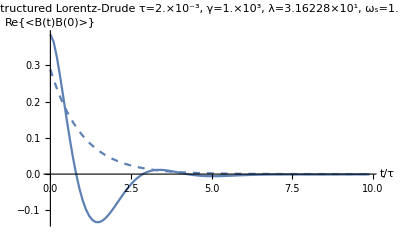

```mathematica
(* System properties *)
nω0=1;
nT=1;

α1=10^-3; (*Subscript[α, 1]=Subscript[γ, h]*) 
α2=10^3;

(* For Structured Lorentz-Drude spectral density *)
nγ=10^3;
nλ=Sqrt[α1*α2*nγ];
nωs=Sqrt[α2*nγ];

tmax=10;
points=100;

Show[ListLinePlot[ParallelTable[{t,Quiet[Re[N[BathCorrelatorReAnalyticalJStructuredLorentzDrude[t*2/nγ,nT,nγ,nλ,nωs]]]]},{t,10^-6,tmax,tmax/points}],AxesLabel->{"t/τ","Re{⟨B(t)B(0)⟩}"},PlotLabel->StringForm["Structured Lorentz-Drude\n τ=``, γ=``, λ=``, ω_s=``",ScientificForm[N[2/nγ]],ScientificForm[N[nγ]],ScientificForm[N[nλ]],ScientificForm[N[nωs]]],PlotRange->All],Plot[nλ^2/(4*Sqrt[nωs^2-nγ^2/4])*Exp[-t],{t,0,tmax},PlotRange->All,PlotStyle->Dashed]]
```

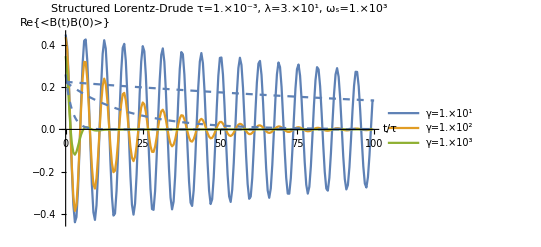

```mathematica
(* System properties *)
nω0=1;
nT=1;

(* For Structured Lorentz-Drude spectral density *)
γlist=Table[10^i,{i,1,3}];
nλ=30;
nωs=1000;

timescale=10^-3;

tmax=100;
points=200;

Show[ListLinePlot[ParallelTable[{t,Quiet[Chop[N[BathCorrelatorReAnalyticalJStructuredLorentzDrude[t*timescale,nT,γ,nλ,nωs]]]]},{γ,γlist},{t,10^-6,tmax,tmax/points}],AxesLabel->{"t/τ","Re{⟨B(t)B(0)⟩}"},PlotLabel->StringForm["Structured Lorentz-Drude\n τ=``, λ=``, ω_s=``",ScientificForm[N[timescale]],ScientificForm[N[nλ]],ScientificForm[N[nωs]]],PlotLegends->Table[StringForm["γ=``",ScientificForm[N[γ]]],{γ,γlist}],PlotRange->All],Plot[Table[nλ^2/(4*Sqrt[nωs^2-γ^2/4])*Exp[-γ/2*t*timescale],{γ,γlist}],{t,0,tmax},PlotRange->All,PlotStyle->Dashed]]
```

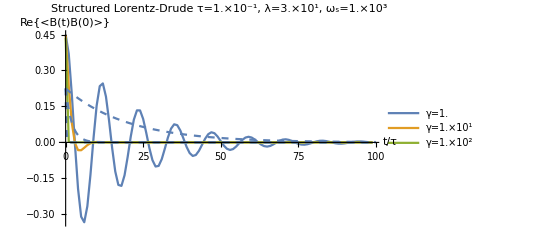

```mathematica
(* System properties *)
nω0=1;
nT=1;

(* For Structured Lorentz-Drude spectral density *)
γlist=Table[10^i,{i,0,2}];
nλ=30;
nωs=1000;

timescale=10^-1;

tmax=100;
points=100;


Show[ListLinePlot[ParallelTable[{t,Quiet[Chop[N[BathCorrelatorReAnalyticalJStructuredLorentzDrude[t*timescale,nT,γ,nλ,nωs]]]]},{γ,γlist},{t,10^-6,tmax,tmax/points}],AxesLabel->{"t/τ","Re{⟨B(t)B(0)⟩}"},PlotLabel->StringForm["Structured Lorentz-Drude\n τ=``, λ=``, ω_s=``",ScientificForm[N[timescale]],ScientificForm[N[nλ]],ScientificForm[N[nωs]]],PlotLegends->Table[StringForm["γ=``",ScientificForm[N[γ]]],{γ,γlist}],PlotRange->All],Plot[Table[nλ^2/(4*Sqrt[nωs^2-γ^2/4])*Exp[-γ/2*t*timescale],{γ,γlist}],{t,0,tmax},PlotRange->All,PlotStyle->Dashed]]
```

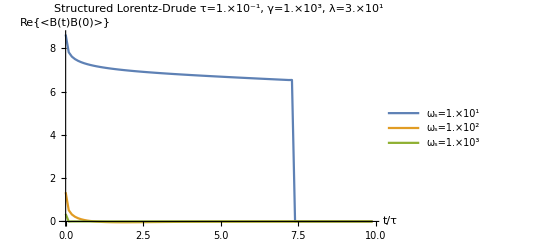

```mathematica
(* System properties *)
nω0=10;
nT=1;

(* For Structured Lorentz-Drude spectral density *)
nγ=10^3;
nλ=30;
ωslist=Table[10^i,{i,1,3}];

timescale=10^-1;

tmax=10;
points=100;

ListLinePlot[ParallelTable[{t,Quiet[Re[N[BathCorrelatorReAnalyticalJStructuredLorentzDrude[t*timescale,nT,nγ,nλ,tωs]]]]},{tωs,ωslist},{t,10^-6,tmax,tmax/points}],AxesLabel->{"t/τ","Re{⟨B(t)B(0)⟩}"},PlotLabel->StringForm["Structured Lorentz-Drude\n τ=``, γ=``, λ=``",ScientificForm[N[timescale]],ScientificForm[N[nγ]],ScientificForm[N[nλ]]],PlotLegends->Table[StringForm["ω_s=``",ScientificForm[N[tωs]]],{tωs,ωslist}],PlotRange->All]
```

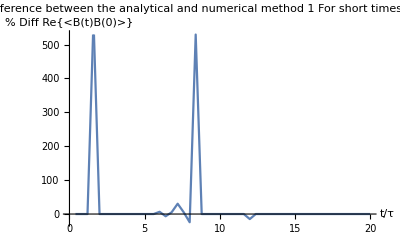

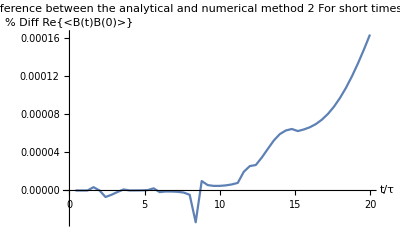

```mathematica
nω0=1;
nT=1;

nγ=10^3;
nλ=10^(3/2);
nωs=10^3;

timescale=10^-3;

tmax=20;
points=50;

ListLinePlot[ParallelTable[{t,Quiet[100*(BathCorrelatorReAnalyticalJStructuredLorentzDrude[t*timescale,nT,nγ,nλ,nωs]-BathCorrelatorReNumericalJStructuredLorentzDrude[t*timescale,nT,nγ,nλ,nωs])/(BathCorrelatorReAnalyticalJStructuredLorentzDrude[t*timescale,nT,nγ,nλ,nωs])]},{t,0,tmax,tmax/points}],AxesLabel->{"t/τ","% Diff Re{⟨B(t)B(0)⟩}"},PlotLabel->StringForm["% Difference between the analytical and numerical method 1\n For short times: τ=``",ScientificForm[N[timescale]]],PlotRange->All]

ListLinePlot[ParallelTable[{t,Quiet[100*(BathCorrelatorReAnalyticalJStructuredLorentzDrude[t*timescale,nT,nγ,nλ,nωs]-BathCorrelatorReNumericalJStructuredLorentzDrude2[t*timescale,nT,nγ,nλ,nωs])/(BathCorrelatorReAnalyticalJStructuredLorentzDrude[t*timescale,nT,nγ,nλ,nωs])]},{t,0,tmax,tmax/points}],AxesLabel->{"t/τ","% Diff Re{⟨B(t)B(0)⟩}"},PlotLabel->StringForm["% Difference between the analytical and numerical method 2\n For short times: τ=``",ScientificForm[N[timescale]]],PlotRange->All]
```

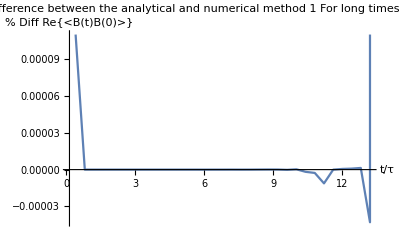

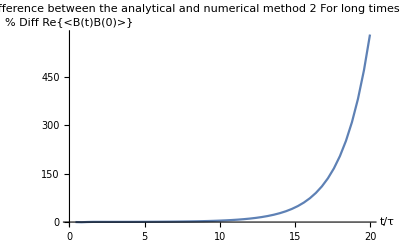

```mathematica
nω0=1;
nT=1;

nγ=10^3;
nλ=10^(3/2);
nωs=10^3;

timescale=10^-1;

tmax=20;
points=50;

ListLinePlot[ParallelTable[{t,Quiet[100*(BathCorrelatorReAnalyticalJStructuredLorentzDrude[t*timescale,nT,nγ,nλ,nωs]-BathCorrelatorReNumericalJStructuredLorentzDrude[t*timescale,nT,nγ,nλ,nωs])/(BathCorrelatorReAnalyticalJStructuredLorentzDrude[t*timescale,nT,nγ,nλ,nωs])]},{t,0,tmax,tmax/points}],AxesLabel->{"t/τ","% Diff Re{⟨B(t)B(0)⟩}"},PlotLabel->StringForm["% Difference between the analytical and numerical method 1\n For long times: τ=``",ScientificForm[N[timescale]]],PlotRange->All]

ListLinePlot[ParallelTable[{t,Quiet[100*(BathCorrelatorReAnalyticalJStructuredLorentzDrude[t*timescale,nT,nγ,nλ,nωs]-BathCorrelatorReNumericalJStructuredLorentzDrude2[t*timescale,nT,nγ,nλ,nωs])/(BathCorrelatorReAnalyticalJStructuredLorentzDrude[t*timescale,nT,nγ,nλ,nωs])]},{t,0,tmax,tmax/points}],AxesLabel->{"t/τ","% Diff Re{⟨B(t)B(0)⟩}"},PlotLabel->StringForm["% Difference between the analytical and numerical method 2\n For long times: τ=``",ScientificForm[N[timescale]]],PlotRange->All]
```

Now to calculate the integrated bath correlation function: ∫_0^t Re{⟨B(s)B(0)⟩}ⅆs".

```mathematica
IntegratedBathCorrelatorReAnalyticalJStructuredLorentzDrude[t_,T_,γ_,λ_,ωs_]:=1 (* To do *)

IntegratedBathCorrelatorReNumericalJStructuredLorentzDrude[t_,T_,γ_,λ_,ωs_]:=1/Pi*NIntegrate[(γ*λ^2*ω)/(γ^2*ω^2+(ω^2-ωs^2)^2) *Coth[ω/(2*T)]*Cos[ω*s],{ω,0,Infinity},{s,0,t}]
```

```mathematica
α1=10^-3;
α2=10^3;

nγ=10^-3;
nλ=Sqrt[α1*α2*nγ];
nωs=Sqrt[α2*nγ];

nT=1;

timescale=10;

ListLinePlot[Table[{rt,nγ^-2*IntegratedBathCorrelatorReNumericalJStructuredLorentzDrude[t*timescale,nT,nγ,nλ,nωs]},{rt,0,0.001,0.001/10}],AxesLabel->{"t/τ","γ_h^-2∫_0^t Re{⟨B(s)B(0)⟩}ⅆs"},PlotRange->All]
```

```mathematica
ListPlot[Table[{t,nγ^-2*(IntegratedBathCorrelatorReAnalyticalJStructuredLorentzDrude[t*timescale,nT,nγ,nλ,nωs]-IntegratedBathCorrelatorReNumericalJStructuredLorentzDrude[t*timescale,nT,nγ,nλ,nωs])//Quiet},{t,0,0.001,0.001/20}],AxesLabel->{"t/τ","γ_h^-2∫_0^t Re{⟨B(s)B(0)⟩}ⅆs"},PlotLabel->"% Difference between the analytical and numerical methods"]
```

#### Imaginary part of the bath correlator

```mathematica
FunctionPoles[(γ λ^2 ω)/(((ω^2-ωs^2)-ⅈ γ ω)((ω^2-ωs^2)+ⅈ γ ω)),ω]
```

FunctionPoles::avar: Warning: Assumptions that involve the variable ω are ignored.

{{ConditionalExpression[ⅈ (-γ/2-1/2 √(γ^2-4 ωs^2)), γ>2 ωs],1},{ConditionalExpression[ⅈ (γ/2-1/2 √(γ^2-4 ωs^2)), γ>2 ωs],1},{ConditionalExpression[ⅈ (-γ/2+1/2 √(γ^2-4 ωs^2)), γ>2 ωs],1},{ConditionalExpression[ⅈ (γ/2+1/2 √(γ^2-4 ωs^2)), γ>2 ωs],1},{ConditionalExpression[-(ⅈ γ)/2-1/2 √(-γ^2+4 ωs^2), γ<2 ωs],1},{ConditionalExpression[(ⅈ γ)/2-1/2 √(-γ^2+4 ωs^2), γ<2 ωs],1},{ConditionalExpression[-(ⅈ γ)/2+1/2 √(-γ^2+4 ωs^2), γ<2 ωs],1},{ConditionalExpression[(ⅈ γ)/2+1/2 √(-γ^2+4 ωs^2), γ<2 ωs],1}}

```mathematica
FullSimplify[ ⅈ(Residue[(γ λ^2 ω)/(((ω^2-ωs^2)-ⅈ γ ω)((ω^2-ωs^2)+ⅈ γ ω))*Exp[ⅈ ω t],{ω,(ⅈ γ)/2-1/2 √(-γ^2+4 ωs^2)}]+Residue[(γ λ^2 ω)/(((ω^2-ωs^2)-ⅈ γ ω)((ω^2-ωs^2)+ⅈ γ ω))*Exp[ⅈ ω t],{ω,(ⅈ γ)/2+1/2 √(-γ^2+4 ωs^2)}])]
```

(ⅈ ⅇ^(-(t γ)/2) λ^2 Sin[1/2 t √(-γ^2+4 ωs^2)])/(√(-γ^2+4 ωs^2))

```mathematica
BathCorrelatorImAnalyticalJStructuredLorentzDrude[t_,γ_,λ_,ωs_]:=-λ^2/(2*Sqrt[ωs^2-γ^2/4])*Exp[-γ/2*t]*Sin[Sqrt[ωs^2-γ^2/4]*t]
BathCorrelatorImNumericalJStructuredLorentzDrude[t_,γ_,λ_,ωs_]:=-1/Pi*NIntegrate[(γ λ^2 ω)/(γ^2 ω^2+(ω^2-ωs^2)^2)*Sin[ω*t],{ω,0,Infinity},Method->"DoubleExponential"]
```

Test that this reduces to the Lorentz-Drude expression

```mathematica
-λ^2/(2*Sqrt[ωs^2-γ^2/4])*Exp[-γ/2*t]*Sin[Sqrt[ωs^2-γ^2/4]*t] /.{λ^2->α1 α2 γ,ωs^2->α2 γ}
```

-(ⅇ^(-(t γ)/2) α1 α2 γ Sin[t √(α2 γ-γ^2/4)])/(2 √(α2 γ-γ^2/4))

```mathematica
Asymptotic[-(ⅇ^(-(t γ)/2) α1 α2 γ Sin[t √(α2 γ-γ^2/4)])/(2 √(α2 γ-γ^2/4)),γ->Infinity]
```

(ⅇ^(-(t γ)/2) t α1 α2^3 Cosh[t α2-(t γ)/2])/γ+ⅇ^(-(t γ)/2) (α1 α2+(2 α1 α2^2)/γ) Sinh[t α2-(t γ)/2]

```mathematica
(ⅇ^(-(t γ)/2) t α1 α2^3 Cosh[t α2-(t γ)/2])/γ+ⅇ^(-(t γ)/2) (α1 α2+(2 α1 α2^2)/γ) Sinh[t α2-(t γ)/2]//TrigExpand
```

-1/2 α1 α2 Cosh[t α2]+1/2 ⅇ^(-t γ) α1 α2 Cosh[t α2]-(α1 α2^2 Cosh[t α2])/γ+(ⅇ^(-t γ) α1 α2^2 Cosh[t α2])/γ+(t α1 α2^3 Cosh[t α2])/(2 γ)+(ⅇ^(-t γ) t α1 α2^3 Cosh[t α2])/(2 γ)+1/2 α1 α2 Sinh[t α2]+1/2 ⅇ^(-t γ) α1 α2 Sinh[t α2]+(α1 α2^2 Sinh[t α2])/γ+(ⅇ^(-t γ) α1 α2^2 Sinh[t α2])/γ-(t α1 α2^3 Sinh[t α2])/(2 γ)+(ⅇ^(-t γ) t α1 α2^3 Sinh[t α2])/(2 γ)

```mathematica
-1/2 α1 α2 Cosh[t α2]+1/2 α1 α2 Sinh[t α2]//FullSimplify
```

-1/2 ⅇ^(-t α2) α1 α2

```mathematica
-ⅇ^(-t ωc) γ ωc^2/.{γ->α1/(2α2),ωc->α2}
```

-1/2 ⅇ^(-t α2) α1 α2

```mathematica
BathCorrelatorImAnalyticalJStructuredLorentzDrude[1,2,3,4]//N 
BathCorrelatorImNumericalJStructuredLorentzDrude[1,2,3,4]//N
```

0.285488

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in ω in the region {{0.,∞}}. NIntegrate obtained -0.896886 and 1.63324×10^-6 for the integral and error estimates.

0.285488

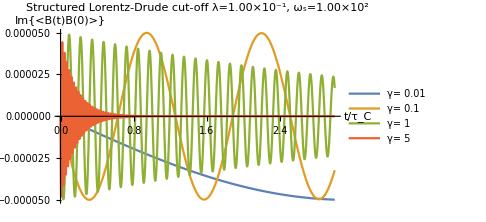

```mathematica
γlist={0.01,0.1,1,5};

nλ=0.1;
nωs=100;

Plot[Evaluate@Table[BathCorrelatorImAnalyticalJStructuredLorentzDrude[t*tγ/2,tγ,nλ,nωs],{tγ,γlist}],{t,0,3},PlotLegends->Table[StringForm["γ= ``",tγ],{tγ,γlist}],AxesLabel->{"t/τ_C","Im{⟨B(t)B(0)⟩}"},PlotLabel->StringForm["Structured Lorentz-Drude cut-off\n λ=``, ω_s=``",ScientificForm[nλ,3],ScientificForm[nωs,3]],ImageSize->Medium]
```

```mathematica
Integrate[BathCorrelatorImAnalyticalJStructuredLorentzDrude[s,γ,λ,ωs],{s,0,t}]//FullSimplify
```

(λ^2 (-1+ⅇ^(-(t γ)/2) (Cos[1/2 t √(-γ^2+4 ωs^2)]+(γ Sin[1/2 t √(-γ^2+4 ωs^2)])/(√(-γ^2+4 ωs^2)))))/(2 ωs^2)

```mathematica
IntegratedBathCorrelatorImAnalyticalJStructuredLorentzDrude[t_,γ_,λ_,ωs_]:=(λ^2 (-1+ⅇ^(-(t γ)/2) (Cos[1/2 t √(-γ^2+4 ωs^2)]+(γ Sin[1/2 t √(-γ^2+4 ωs^2)])/(√(-γ^2+4 ωs^2)))))/(2 ωs^2)
```

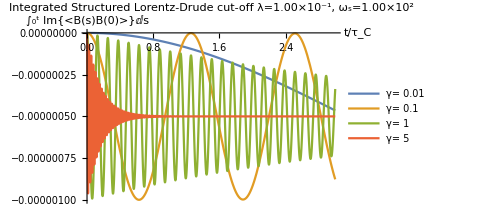

```mathematica
γlist={0.01,0.1,1,5};

nλ=0.1;
nωs=100;

Plot[Evaluate@Table[IntegratedBathCorrelatorImAnalyticalJStructuredLorentzDrude[t*tγ/2,tγ,nλ,nωs],{tγ,γlist}],{t,0,3},PlotLegends->Table[StringForm["γ= ``",tγ],{tγ,γlist}],AxesLabel->{"t/τ_C","∫_0^t Im{⟨B(s)B(0)⟩}ⅆs"},PlotLabel->StringForm["Integrated Structured Lorentz-Drude cut-off\n λ=``, ω_s=``",ScientificForm[nλ,3],ScientificForm[nωs,3]],ImageSize->Medium]
```

### Spectral Density : General s with exponential cut-off

Calculate the reorganisation energy

```mathematica
2/π*Integrate[ JsExp[ω,s,γ,ωc]/ω,{ω,0,Infinity}]
```

ConditionalExpression[γ ωc Gamma[s], Re[s]>0]

#### Real part of the bath correlator

```mathematica
intexpr=1/Pi*Integrate[1/2 ⅇ^(-ω/ωc) π γ ω^s ωc^(1-s)*(2*T*ω)/(ω^2+(2*Pi*T)^2*n^2)*Cos[ω*t],{ω,0,Infinity}]
```

ConditionalExpression[2^(-2+s) π^s T γ ωc^(1-s) (-ⅇ^(π (ⅈ s-2 n t T+(2 ⅈ n T)/ωc)) (-ⅈ n T)^s (π Csc[π s]-(1+s) Gamma[-1-s] Gamma[1+s]+(1+s) Gamma[1+s] Gamma[-1-s,-(2 n π T (-ⅈ+t ωc))/ωc])-ⅇ^(π (-ⅈ s+(2 n T (-ⅈ+t ωc))/ωc)) (ⅈ n T)^s (π Csc[π s]-(1+s) Gamma[-1-s] Gamma[1+s]+(1+s) Gamma[1+s] Gamma[-1-s,(2 n π T (-ⅈ+t ωc))/ωc])-ⅇ^(-π (ⅈ s+(2 n T (ⅈ+t ωc))/ωc)) (ⅈ n T)^s (π Csc[π s]-(1+s) Gamma[-1-s] Gamma[1+s]+(1+s) Gamma[1+s] Gamma[-1-s,-(2 n π T (ⅈ+t ωc))/ωc])-ⅇ^(π (ⅈ s+(2 n T (ⅈ+t ωc))/ωc)) (-ⅈ n T)^s (π Csc[π s]-(1+s) Gamma[-1-s] Gamma[1+s]+(1+s) Gamma[1+s] Gamma[-1-s,(2 n π T (ⅈ+t ωc))/ωc])), Re[s]>-2]

```mathematica
intexprsimp=FullSimplify[intexpr[[1]]]
```

-2^(-2+s) ⅇ^(-π ((ⅈ s)/2+(2 n T (ⅈ+t ωc))/ωc)) π^s T γ ((n T)/ωc)^s ωc Gamma[2+s] (ⅇ^((ⅈ π (4 n T+s ωc))/ωc) Gamma[-1-s,-(2 n π T (-ⅈ+t ωc))/ωc]+ⅇ^(4 n π t T) Gamma[-1-s,(2 n π T (-ⅈ+t ωc))/ωc]+Gamma[-1-s,-(2 n π T (ⅈ+t ωc))/ωc]+ⅇ^(π (ⅈ s+4 n t T+(4 ⅈ n T)/ωc)) Gamma[-1-s,(2 n π T (ⅈ+t ωc))/ωc])

```mathematica
intexprn0=1/Pi*Integrate[1/2 ⅇ^(-ω/ωc) π γ ω^s ωc^(1-s)*(2*T)/ω*Cos[ω*t],{ω,0,Infinity}]
```

ConditionalExpression[T γ ωc (1+t^2 ωc^2)^(-s/2) Cos[s ArcTan[t ωc]] Gamma[s], Re[s]>0]

```mathematica
FullSimplify[intexprsimp,s∈PositiveIntegers]
```

-ⅈ^(3 s) 2^(-2+s) ⅇ^(-(2 n π T (ⅈ+t ωc))/ωc) π^s T γ ((n T)/ωc)^s ωc Gamma[2+s] ((-1)^s ⅇ^((4 ⅈ n π T)/ωc) Gamma[-1-s,-(2 n π T (-ⅈ+t ωc))/ωc]+ⅇ^(4 n π t T) Gamma[-1-s,(2 n π T (-ⅈ+t ωc))/ωc]+Gamma[-1-s,-(2 n π T (ⅈ+t ωc))/ωc]+(-1)^s ⅇ^((4 n π T (ⅈ+t ωc))/ωc) Gamma[-1-s,(2 n π T (ⅈ+t ωc))/ωc])

```mathematica
Sum[intexprsimp,{n,1,Infinity}]
```

∑_(n=1)^∞ -2^(-2+s) ⅇ^(-π ((ⅈ s)/2+(2 n T (ⅈ+t ωc))/ωc)) π^s T γ ((n T)/ωc)^s ωc Gamma[2+s] (ⅇ^((ⅈ π (4 n T+s ωc))/ωc) Gamma[-1-s,-(2 n π T (-ⅈ+t ωc))/ωc]+ⅇ^(4 n π t T) Gamma[-1-s,(2 n π T (-ⅈ+t ωc))/ωc]+Gamma[-1-s,-(2 n π T (ⅈ+t ωc))/ωc]+ⅇ^(π (ⅈ s+4 n t T+(4 ⅈ n T)/ωc)) Gamma[-1-s,(2 n π T (ⅈ+t ωc))/ωc])

Try a different way, using complex analysis and Cauchy's Residue Theorem. We will choose a contour along x ∈ [-∞,∞] and will close in the upper-half plane.

```mathematica
1/Pi*Integrate[1/2 ⅇ^(-ω/ωc) π γ ω^s ωc^(1-s)*(2*T)/ω*Cos[ω*t],{ω,0,Infinity}]
```

ConditionalExpression[T γ ωc (1+t^2 ωc^2)^(-s/2) Cos[s ArcTan[t ωc]] Gamma[s], Re[s]>0]

```mathematica
actualfirstnumerical[s_,t_,T_,γ_,ωc_]:=1/Pi*NIntegrate[1/2 ⅇ^(-ω/ωc) π γ ω^s ωc^(1-s)*(2*T)/ω*Cos[ω*t],{ω,0,Infinity}] 
actualsecondnumerical[s_,t_,T_,γ_,ωc_]:=1/Pi*NIntegrate[1/2 ⅇ^(-ω/ωc) π γ ω^s ωc^(1-s)*2*Sum[(2*T*ω)/(ω^2+ 4*π^2*T^2*n^2),{n,1,Infinity}]*Cos[ω*t],{ω,0,Infinity}]
```

```mathematica
nt=1;
nT=2;
nγ=3;
nωc=4;

ns=1;

Print["First term:"]

Print["Numerical"]
actualfirstnumerical[ns,nt,nT,nγ,nωc]
Print["Actual"]
actualfirst[ns,nt,nT,nγ,nωc]//N
Print["My try"]
intexprn0[[1]]/.{s->ns,t->nt,T->nT,γ->nγ,ωc->nωc}//N

Print["Second term:"]

Print["Numerical"]
actualsecondnumerical[ns,nt,nT,nγ,nωc]
Print["Actual"]
actualsecond[ns,nt,nT,nγ,nωc]//N
Print["My try"]
2*-ⅈ ⅈ^(3 s) 2^(-2+s) π^(1+s) T γ (T/ωc)^s ωc (PolyLog[-s,ⅇ^(-2 π t T+(2 ⅈ π T)/ωc)]-(-1)^s PolyLog[-s,ⅇ^(-(2 π T (ⅈ+t ωc))/ωc)])/.{s->ns,t->nt,T->nT,γ->nγ,ωc->nωc}//N

Print["Final:"]

Print["Numerical"]
actualfirstnumerical[ns,nt,nT,nγ,nωc]+actualsecondnumerical[ns,nt,nT,nγ,nωc]
Print["Actual"]
actualfirst[ns,nt,nT,nγ,nωc]+actualsecond[ns,nt,nT,nγ,nωc]//N
Print["My try"]
intexprn0[[1]]+2*-ⅈ ⅈ^(3 s) 2^(-2+s) π^(1+s) T γ (T/ωc)^s ωc (PolyLog[-s,ⅇ^(-2 π t T+(2 ⅈ π T)/ωc)]-(-1)^s PolyLog[-s,ⅇ^(-(2 π T (ⅈ+t ωc))/ωc)])/.{s->ns,t->nt,T->nT,γ->nγ,ωc->nωc}//N
```

First term:

Numerical

1.41176

Actual

1.24567

My try

1.41176

Second term:

Numerical

-0.165264

Actual

0.000826043

My try

0.000826043

Final:

Numerical

1.2465

Actual

1.2465

My try

1.41259

```mathematica
Assuming[s∈PositiveIntegers,FunctionPoles[1/2 ⅇ^(-ω/ωc) π γ ω^s ωc^(1-s)*(2*T*ω)/((ω-ⅈ 2*Pi*T*n)(ω+ⅈ 2*Pi*T*n))*Exp[ⅈ ω t],ω]]
```

FunctionPoles::avar: Warning: Assumptions that involve the variable ω are ignored.

{{-2 ⅈ n π T,1},{2 ⅈ n π T,1}}

```mathematica
intexpr=ⅈ FullSimplify[Residue[1/2 ⅇ^(-ω/ωc) π γ ω^s ωc^(1-s)*(2*T*ω)/((ω-ⅈ 2*Pi*T*n)(ω+ⅈ 2*Pi*T*n))*Exp[ⅈ ω t],{ω,2 ⅈ n π T}],Assumptions->{{T,ωc}∈ PositiveReals,{n,s}∈PositiveIntegers}]
```

ⅈ 2^(-1+s) ⅇ^(-(2 n π T (ⅈ+t ωc))/ωc) π^(1+s) T (ⅈ n T)^s γ ωc^(1-s)

```mathematica
intexprRe=FullSimplify[ComplexExpand[Re[intexpr]],Assumptions->{{T,ωc}∈ PositiveReals,{n,s}∈PositiveIntegers}]
```

-2^(-1+s) ⅇ^(-2 n π t T) π^(1+s) T (n T)^s γ ωc^(1-s) Sin[1/2 π (s-(4 n T)/ωc)]

```mathematica
sum=FullSimplify[Sum[intexprRe,{n,1,Infinity}],Assumptions->{{T,ωc}∈ PositiveReals,{n,s}∈PositiveIntegers}]
```

-ⅈ ⅈ^(3 s) 2^(-2+s) π^(1+s) T γ (T/ωc)^s ωc (PolyLog[-s,ⅇ^(-2 π t T+(2 ⅈ π T)/ωc)]-(-1)^s PolyLog[-s,ⅇ^(-(2 π T (ⅈ+t ωc))/ωc)])

```mathematica
final=FullSimplify[intexprn0[[1]]+2*sum,Assumptions->{{T,ωc}∈ PositiveReals,{n,s}∈PositiveIntegers}]
```

1/2 T γ ωc (2 (1+t^2 ωc^2)^(-s/2) Cos[s ArcTan[t ωc]] Gamma[s]-ⅈ ⅈ^(3 s) 2^s π^(1+s) (T/ωc)^s (PolyLog[-s,ⅇ^(-2 π t T+(2 ⅈ π T)/ωc)]-(-1)^s PolyLog[-s,ⅇ^(-(2 π T (ⅈ+t ωc))/ωc)]))

This expression doesn't match numerical integration, so calculate explicitly for s=1,2,3... and make an ansatz.

```mathematica
1/Pi*Integrate[JsExp[ω,1,γ,ωc]*Coth[ω/(2*T)]*Cos[ω*t],{ω,0,Infinity}]
```

1/2 γ ((ωc^2 (-1+t^2 ωc^2))/((1+t^2 ωc^2)^2)+T^2 (PolyGamma[1,T (-ⅈ t+1/ωc)]+PolyGamma[1,T (ⅈ t+1/ωc)]))

```mathematica
1/Pi*Integrate[JsExp[ω,2,γ,ωc]*Coth[ω/(2*T)]*Cos[ω*t],{ω,0,Infinity}]
```

(γ ((-2 ωc^3+6 t^2 ωc^5)/((1+t^2 ωc^2)^3)-T^3 (PolyGamma[2,T (-ⅈ t+1/ωc)]+PolyGamma[2,T (ⅈ t+1/ωc)])))/(2 ωc)

```mathematica
1/Pi*Integrate[JsExp[ω,3,γ,ωc]*Coth[ω/(2*T)]*Cos[ω*t],{ω,0,Infinity}]
```

(γ (3 ωc^4 (-1/(-ⅈ+t ωc)^4-1/(ⅈ+t ωc)^4)+T^4 (PolyGamma[3,T (-ⅈ t+1/ωc)]+PolyGamma[3,T (ⅈ t+1/ωc)])))/(2 ωc^2)

```mathematica
1/Pi*Integrate[JsExp[ω,4,γ,ωc]*Coth[ω/(2*T)]*Cos[ω*t],{ω,0,Infinity}]
```

(γ (12 ⅈ ωc^5 (1/(-ⅈ+t ωc)^5-1/(ⅈ+t ωc)^5)-T^5 PolyGamma[4,T (-ⅈ t+1/ωc)]-T^5 PolyGamma[4,T (ⅈ t+1/ωc)]))/(2 ωc^3)

```mathematica
1/Pi*Integrate[JsExp[ω,5,γ,ωc]*Coth[ω/(2*T)]*Cos[ω*t],{ω,0,Infinity}]
```

(γ (60 ωc^6 (1/(-ⅈ+t ωc)^6+1/(ⅈ+t ωc)^6)+T^6 (PolyGamma[5,T (-ⅈ t+1/ωc)]+PolyGamma[5,T (ⅈ t+1/ωc)])))/(2 ωc^4)

```mathematica
actuals1[t_,T_,γ_,ωc_]:=1/2 γ ((ωc^2 (-1+t^2 ωc^2))/((1+t^2 ωc^2)^2)+T^2 (PolyGamma[1,T (-ⅈ t+1/ωc)]+PolyGamma[1,T (ⅈ t+1/ωc)]))
actuals2[t_,T_,γ_,ωc_]:=(γ ((-2 ωc^3+6 t^2 ωc^5)/((1+t^2 ωc^2)^3)-T^3 (PolyGamma[2,T (-ⅈ t+1/ωc)]+PolyGamma[2,T (ⅈ t+1/ωc)])))/(2 ωc)
actuals3[t_,T_,γ_,ωc_]:=(γ (3 ωc^4 (-1/(-ⅈ+t ωc)^4-1/(ⅈ+t ωc)^4)+T^4 (PolyGamma[3,T (-ⅈ t+1/ωc)]+PolyGamma[3,T (ⅈ t+1/ωc)])))/(2 ωc^2)
actuals4[t_,T_,γ_,ωc_]:=(γ (12 ⅈ ωc^5 (1/(-ⅈ+t ωc)^5-1/(ⅈ+t ωc)^5)-T^5 PolyGamma[4,T (-ⅈ t+1/ωc)]-T^5 PolyGamma[4,T (ⅈ t+1/ωc)]))/(2 ωc^3)
actuals5[t_,T_,γ_,ωc_]:=(γ (60 ωc^6 (1/(-ⅈ+t ωc)^6+1/(ⅈ+t ωc)^6)+T^6 (PolyGamma[5,T (-ⅈ t+1/ωc)]+PolyGamma[5,T (ⅈ t+1/ωc)])))/(2 ωc^4)
```

```mathematica
(*BathCorrelatorReAnalyticalJsExp*)

actual[s_,t_,T_,γ_,ωc_]:=1/4 γ ωc^2 s!(ⅈ)^(s+1)((-1)^s*1/(-ⅈ+t ωc)^(s+1)-1/(ⅈ+t ωc)^(s+1))+1/2 γ ωc^(1-s)(-1)^(s+1) T^(s+1) (PolyGamma[s,T (-ⅈ t+1/ωc)]+PolyGamma[s,T (ⅈ t+1/ωc)])
(*actual[s_]:=1/4 γ ωc (ⅈ^(1+s) ωc ((-1)^s (-ⅈ+t ωc)^(-1-s)-(ⅈ+t ωc)^(-1-s)) s! - 2 (-T)^s T ωc^-s (PolyGamma[s,T (-ⅈ t+1/ωc)]+PolyGamma[s,T (ⅈ t+1/ωc)]))*)

actual2[s_,t_,T_,γ_,ωc_]:=1/4 γ ωc^2 s!(ⅈ)^(s+1)((-1)^s*1/(-ⅈ+t ωc)^(s+1)-1/(ⅈ+t ωc)^(s+1))+γ ωc^(1-s)(-1)^(s+1) T^(s+1) Re[PolyGamma[s,T (ⅈ t+1/ωc)]]

(*Using the expansion ψ^(s)(z)=(-1)^(s+1)s! ζ(s+1,z), where ζ is the Hurwitz zeta function defined by ζ(s,a)=∑_(n=0)^∞ 1/(n+a)^s.*)
actual3[s_,t_,T_,γ_,ωc_]:=1/4 γ ωc^2 s!(ⅈ)^(s+1)((-1)^s*1/(-ⅈ+t ωc)^(s+1)-1/(ⅈ+t ωc)^(s+1))+γ ωc^(1-s) s! T^(s+1) Re[HurwitzZeta[1+s,T (ⅈ t+1/ωc)]]

actualre[s_,t_,T_,γ_,ωc_]:=1/2 γ ωc (-ωc (1+t^2 ωc^2)^(-1/2-s/2) Cos[(1+s) ArcTan[t ωc]] s!-2 (-T)^s T ωc^-s Re[PolyGamma[s,T (ⅈ t+1/ωc)]])

actualfirst[s_,t_,T_,γ_,ωc_]:=1/4 γ ωc^2 s!(ⅈ)^(s+1)((-1)^s*1/(-ⅈ+t ωc)^(s+1)-1/(ⅈ+t ωc)^(s+1))

actualsecond[s_,t_,T_,γ_,ωc_]:=γ ωc^(1-s)(-1)^(s+1) T^(s+1) Re[PolyGamma[s,T (ⅈ t+1/ωc)]]



BathCorrelatorReNumericalJsExp[s_,t_,T_,γ_,ωc_]:=1/Pi*NIntegrate[1/2 ⅇ^(-ω/ωc) π γ ω^s ωc^(1-s)*Coth[ω/(2*T)]*Cos[ω*t],{ω,0,Infinity},Method->"DoubleExponential"]
```

```mathematica
nt=3;
nT=1;
nγ=1;
nωc=100;

ns=1;

actualre[ns,nt/nωc,nT,nγ,nωc]//N
BathCorrelatorReNumericalJsExp[ns,nt/nωc,nT,nγ,nωc]//Quiet
```

-398.382

-398.382

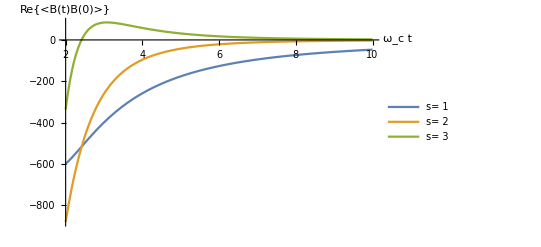

```mathematica
nT=1;
nγ=1;
nωc=100;

slist={1,2,3};

plotsBathCorrelatorReAnalyticalJsExp=Plot[Evaluate[Table[actualre[s,t/nωc,nT,nγ,nωc],{s,slist}]],{t,2,10},PlotLegends->Table[StringForm["s= ``",s],{s,slist}],AxesLabel->{"ω_c t","Re{⟨B(t)B(0)⟩}"},PlotRange->All]
```

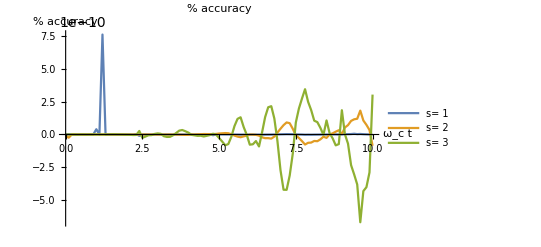

```mathematica
nT=1;
nγ=1;
nωc=100;

slist={1,2,3};

ListLinePlot[ParallelTable[{t,100*(actualre[s,t/nωc,nT,nγ,nωc]-BathCorrelatorReNumericalJsExp[s,t/nωc,nT,nγ,nωc]//Quiet)/(BathCorrelatorReNumericalJsExp[s,t/nωc,nT,nγ,nωc]//Quiet)},{s,slist},{t,0,10,0.1}],AxesLabel->{"ω_c t","% accuracy"},PlotLabel->"% accuracy",PlotLegends->Table[StringForm["s= ``",s],{s,slist}],PlotRange->All]
```

Now to calculate the integrated bath correlation function: ∫_0^t Re{⟨B(s)B(0)⟩}ⅆs".

```mathematica
IntegratedBathCorrelatorReNumericalJsExp[s_,t_,T_,γ_,ωc_]:=1/Pi*NIntegrate[1/2 ⅇ^(-ω/ωc) π γ ω^s ωc^(1-s)*Coth[ω/(2*T)]*Cos[ω*tp],{ω,0,Infinity},{tp,0,t}]
```

```mathematica
Integrate[actual1[s,T,γ,ωc],{s,0,t}]
```

(ⅈ γ (ⅈ t ωc^2+(T+t^2 T ωc^2) PolyGamma[0,T (-ⅈ t+1/ωc)]-(T+t^2 T ωc^2) PolyGamma[0,T (ⅈ t+1/ωc)]))/(2+2 t^2 ωc^2)

```mathematica
Integrate[actual2[s,T,γ,ωc],{s,0,t}]
```

-(2 t γ ωc^3+ⅈ γ (T+t^2 T ωc^2)^2 (PolyGamma[1,T (-ⅈ t+1/ωc)]-PolyGamma[1,T (ⅈ t+1/ωc)]))/(2 ωc (1+t^2 ωc^2)^2)

```mathematica
Integrate[actual3[s,T,γ,ωc],{s,0,t}]
```

(γ (2 t ωc^4 (-3+t^2 ωc^2)+ⅈ (T+t^2 T ωc^2)^3 (PolyGamma[2,T (-ⅈ t+1/ωc)]-PolyGamma[2,T (ⅈ t+1/ωc)])))/(2 ωc^2 (1+t^2 ωc^2)^3)

```mathematica
Integrate[actual4[s,T,γ,ωc],{s,0,t}]
```

(γ (24 t ωc^5 (-1+t^2 ωc^2)-ⅈ (T+t^2 T ωc^2)^4 (PolyGamma[3,T (-ⅈ t+1/ωc)]-PolyGamma[3,T (ⅈ t+1/ωc)])))/(2 ωc^3 (1+t^2 ωc^2)^4)

```mathematica
actualintegrated1[t_,T_,γ_,ωc_]:=(ⅈ γ (ⅈ t ωc^2+(T+t^2 T ωc^2) PolyGamma[0,T (-ⅈ t+1/ωc)]-(T+t^2 T ωc^2) PolyGamma[0,T (ⅈ t+1/ωc)]))/(2+2 t^2 ωc^2)
actualintegrated2[t_,T_,γ_,ωc_]:=-(2 t γ ωc^3+ⅈ γ (T+t^2 T ωc^2)^2 (PolyGamma[1,T (-ⅈ t+1/ωc)]-PolyGamma[1,T (ⅈ t+1/ωc)]))/(2 ωc (1+t^2 ωc^2)^2)
actualintegrated3[t_,T_,γ_,ωc_]:=(γ (2 t ωc^4 (-3+t^2 ωc^2)+ⅈ (T+t^2 T ωc^2)^3 (PolyGamma[2,T (-ⅈ t+1/ωc)]-PolyGamma[2,T (ⅈ t+1/ωc)])))/(2 ωc^2 (1+t^2 ωc^2)^3)
actualintegrated4[t_,T_,γ_,ωc_]:=(γ (24 t ωc^5 (-1+t^2 ωc^2)-ⅈ (T+t^2 T ωc^2)^4 (PolyGamma[3,T (-ⅈ t+1/ωc)]-PolyGamma[3,T (ⅈ t+1/ωc)])))/(2 ωc^3 (1+t^2 ωc^2)^4)
```

```mathematica
Integrate[actual[s,tp,T,γ,ωc],{tp,0,t}]
```

1/4 ⅈ (-ⅈ)^-s γ ωc (((-1)^s (ⅈ^s-(-ⅈ+t ωc)^-s) s!)/s+(-(-ⅈ)^s+(ⅈ+t ωc)^-s) Gamma[s]-2 (-ⅈ)^s (-T/ωc)^s (PolyGamma[-1+s,T (-ⅈ t+1/ωc)]-PolyGamma[-1+s,T (ⅈ t+1/ωc)]))

```mathematica
FullSimplify[1/4 ⅈ (-ⅈ)^-s γ ωc (((-1)^s (ⅈ^s-(-ⅈ+t ωc)^-s) s!)/s+(-(-ⅈ)^s+(ⅈ+t ωc)^-s) Gamma[s]-2 (-ⅈ)^s (-T/ωc)^s (PolyGamma[-1+s,T (-ⅈ t+1/ωc)]-PolyGamma[-1+s,T (ⅈ t+1/ωc)])),Assumptions->s∈PositiveIntegers]
```

-(ⅈ γ ωc (-ⅈ (1+t^2 ωc^2))^-s (((-ⅈ-t ωc)^s-(-ⅈ+t ωc)^s) s!+2 s ((ⅈ T (1+t^2 ωc^2))/ωc)^s (PolyGamma[-1+s,T (-ⅈ t+1/ωc)]-PolyGamma[-1+s,T (ⅈ t+1/ωc)])))/(4 s)

```mathematica
actualintegrated[s_,t_,T_,γ_,ωc_]:=-(ⅈ γ ωc (-ⅈ (1+t^2 ωc^2))^-s (((-ⅈ-t ωc)^s-(-ⅈ+t ωc)^s) s!+2 s ((ⅈ T (1+t^2 ωc^2))/ωc)^s (PolyGamma[-1+s,T (-ⅈ t+1/ωc)]-PolyGamma[-1+s,T (ⅈ t+1/ωc)])))/(4 s)
```

```mathematica
nt=0.1;
nT=1;
nγ=1;
nωc=1;

actualintegrated1[nt,nT,nγ,nωc]//N
IntegratedBathCorrelatorReNumericalJsExp[1,nt,nT,nγ,nωc]

actualintegrated[1,nt,nT,nγ,nωc]//N
```

0.113916+0. ⅈ

0.113916

0.113916+0. ⅈ

```mathematica
IntegratedBathCorrelatorReNumericalJsExp[3,10,1,1,1]
```

0.00194147

```mathematica
actualintegrated3[10,1,1,1]//N
```

0.00194147+0. ⅈ

```mathematica
actualintegrated[3,100000/nωc,nT,nγ,nωc]//N
```

2.×10^-15+0. ⅈ

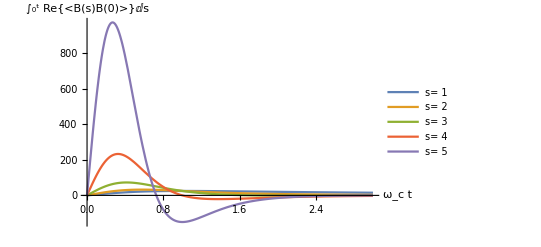

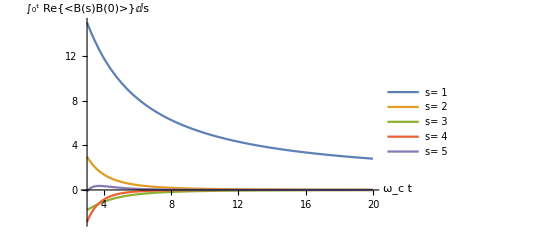

```mathematica
nT=1;
nγ=1;
nωc=100;

slist={1,2,3,4,5};

Plot[Evaluate[Table[actualintegrated[s,t/nωc,nT,nγ,nωc],{s,slist}]],{t,0,3},PlotLegends->Table[StringForm["s= ``",s],{s,slist}],AxesLabel->{"ω_c t","∫_0^t Re{⟨B(s)B(0)⟩}ⅆs"},PlotRange->All]

Plot[Evaluate[Table[actualintegrated[s,t/nωc,nT,nγ,nωc],{s,slist}]],{t,3,20},PlotLegends->Table[StringForm["s= ``",s],{s,slist}],AxesLabel->{"ω_c t","∫_0^t Re{⟨B(s)B(0)⟩}ⅆs"},PlotRange->All]
```

```mathematica
Asymptotic[actualintegrated[1,t,T,γ,ωc],t->Infinity]
```

(π T γ)/2

```mathematica
Asymptotic[actualintegrated[2,t,T,γ,ωc],t->Infinity]
```

(T γ)/(t ωc)

```mathematica
Integrate[actual[2,tp,T,γ,ωc],{tp,0,Infinity}]
```

0

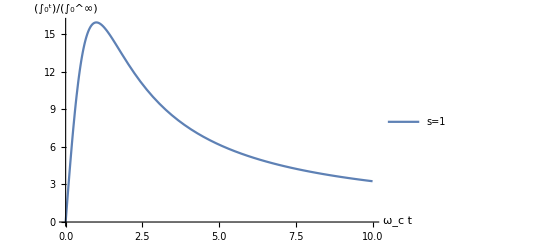

```mathematica
nT=1;
nγ=1;
nωc=100;

Plot[{2/(π nT nγ)*actualintegrated1[t/nωc,nT,nγ,nωc]},{t,0,10},AxesLabel->{"ω_c t","(∫_0^t)/(∫_0^∞)"},PlotLegends->{"s=1"},PlotRange->All]
```

#### Imaginary part of the bath correlator

```mathematica
-1/π*Integrate[JsExp[ω,s,γ,ωc]*Sin[ω t],{ω,0,Infinity}]
```

ConditionalExpression[-1/2 γ ωc^2 (1+t^2 ωc^2)^(-1/2-s/2) Gamma[1+s] Sin[(1+s) ArcTan[t ωc]], Re[s]>-2]

```mathematica
BathCorrelatorImAnalyticalJsExp[s_,t_,γ_,ωc_]:=-1/2 γ ωc^2 (1+t^2 ωc^2)^(-1/2-s/2) Gamma[1+s] Sin[(1+s) ArcTan[t ωc]]

BathCorrelatorImNumericalJsExp[s_,t_,γ_,ωc_]:=-1/Pi*NIntegrate[1/2 ⅇ^(-ω/ωc) π γ ω^s ωc^(1-s)*Sin[ω*t],{ω,0,Infinity},Method->"DoubleExponential"]
```

Rewrite Sin[(1+s) ArcTan[t ω_c]]

First using the Chebyshev polynomials of the second kind U_n, defined as U_n(cos θ)sin θ=sin((n+1)θ)
Let  θ=arctan(t ω_c), so cos θ=1/(√(1+(tω_c)^2)) and sin θ=(t ω_c)/(√(1+(tω_c)^2))

Alternatively, expand arctan(x)=ⅈ/2 ln((1-ⅈx)/(1+ⅈx)) and sin(x)=ⅈ/2(ⅇ^-ⅈx-ⅇ^ⅈx)

So sin(n arctan(x))=ⅈ/2 exp(-ⅈ ⅈ/2 n ln((1-ⅈx)/(1+ⅈx)))-ⅈ/2 exp(ⅈ ⅈ/2 n ln((1-ⅈx)/(1+ⅈx)))
=ⅈ/2((1-ⅈx)^(n/2)/(1+ⅈx)^(n/2)-(1+ⅈx)^(n/2)/(1-ⅈx)^(n/2))=ⅈ/2(((1-ⅈx)^n-(1+ⅈx)^n)/((x^2+1)^(n/2)))

```mathematica
BathCorrelatorImAnalyticalJsExp2[s_,t_,γ_,ωc_]:=-1/2 t γ ωc^3 (1+t^2 ωc^2)^(-1-s/2) *Gamma[1+s]*ChebyshevU[s,1/(√(1+t^2 ωc^2))]
BathCorrelatorImAnalyticalJsExp3[s_,t_,γ_,ωc_]:=-1/4 ⅈ γ ωc^2 (1+t^2 ωc^2)^(-1-s) *Gamma[1+s]*((1-ⅈ t ωc)^(1+s)-(1+ⅈ t ωc)^(1+s))
```

```mathematica
BathCorrelatorImAnalyticalJsExp[1,2,3,4]//N
BathCorrelatorImNumericalJsExp[1,2,3,4]
BathCorrelatorImAnalyticalJsExp2[1,2,3,4]//N
BathCorrelatorImAnalyticalJsExp3[1,2,3,4]//N
```

-0.0908876

-0.0908876

-0.0908876

«1 more identical outputs»

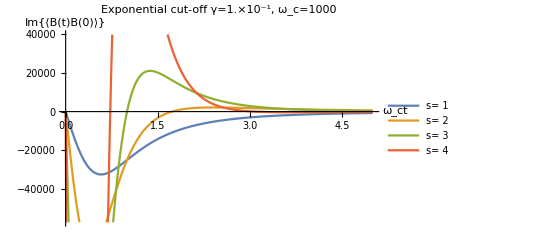

```mathematica
slist={1,2,3,4};

nγ=0.1;
nωc=1000;

Plot[Evaluate@Table[BathCorrelatorImAnalyticalJsExp[s,t/nωc,nγ,nωc],{s,slist}],{t,0,5},PlotLegends->Table[StringForm["s= ``",s],{s,slist}],AxesLabel->{"ω_ct","Im{⟨B(t)B(0)⟩}"},PlotLabel-> StringForm["Exponential cut-off\n γ=``, ω_c=``",ScientificForm[nγ,3],ScientificForm[nωc,3]]]
```

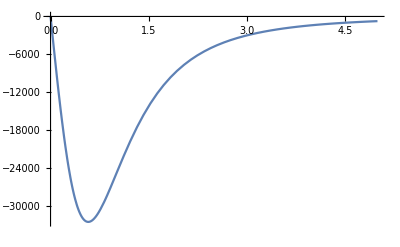

```mathematica
Plot[BathCorrelatorImAnalyticalJsExp[1,t/nωc,nγ,nωc],{t,0,5}]
```

```mathematica
nγ=0.1;
nωc=1000;
model=a+b*Exp[-c t];
list1=Table[{t,BathCorrelatorImAnalyticalJsExp[1,t/nωc,nγ,nωc]},{t,1,10,0.01}];

fit1=FindFit[list1,a+b*Exp[-c t/nωc],{a,b,c},t]
func1=Function[{t},Evaluate[model/. fit1]];
```

{a→-302.366,b→-76319.5,c→1130.82}

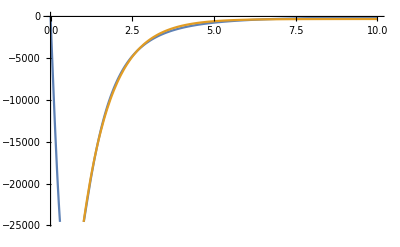

```mathematica
Plot[{BathCorrelatorImAnalyticalJsExp[1,t/nωc,nγ,nωc],func1[t/nωc]},{t,0,10}]
```

```mathematica
nγ=0.1;
nωc=1000;
model=a+b*Exp[-c t];
list2=Table[{t,BathCorrelatorImAnalyticalJsExp[2,t/nωc,nγ,nωc]},{t,3,20,0.01}];

fit2=FindFit[list2,a+b*Exp[-c t/nωc],{a,b,c},t]
func2=Function[{t},Evaluate[model/. fit2]];
```

{a→30.6986,b→8381.87,c→521.969}

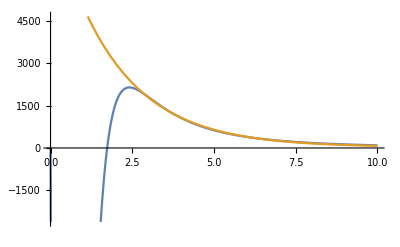

```mathematica
Plot[{BathCorrelatorImAnalyticalJsExp[2,t/nωc,nγ,nωc],func2[t/nωc]},{t,0,10}]
```

```mathematica
nγ=0.1;
nωc=1000;
model=a+b*Exp[-c t];
list3=Table[{t,BathCorrelatorImAnalyticalJsExp[2,t/nωc,nγ,nωc]},{t,4,20,0.01}];

fit3=FindFit[list3,a+b*Exp[-c t/nωc],{a,b,c},t]
func3=Function[{t},Evaluate[model/. fit3]];
```

{a→25.4432,b→6786.13,c→480.605}

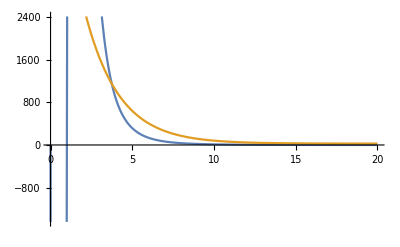

```mathematica
Plot[{BathCorrelatorImAnalyticalJsExp[3,t/nωc,nγ,nωc],func3[t/nωc]},{t,0,20}]
```

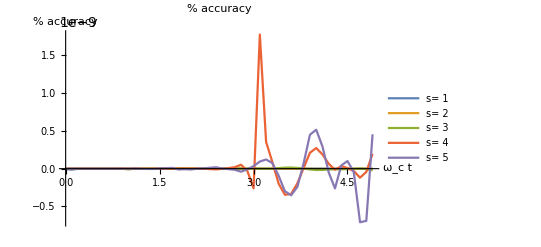

```mathematica
slist={1,2,3,4,5};

nγ=0.1;
nωc=100;

ListLinePlot[ParallelTable[{t,100*(BathCorrelatorImAnalyticalJsExp[s,t/nωc,nγ,nωc]-BathCorrelatorImNumericalJsExp[s,t/nωc,nγ,nωc]//Quiet)/(BathCorrelatorImNumericalJsExp[s,t/nωc,nγ,nωc]//Quiet)},{s,slist},{t,0.001,5,0.1}],AxesLabel->{"ω_c t","% accuracy"},PlotLabel->"% accuracy",PlotLegends->Table[StringForm["s= ``",s],{s,slist}],PlotRange->All]
```

```mathematica
Integrate[BathCorrelatorImAnalyticalJsExp[s,tp,γ,ωc],{tp,0,t}]
```

-(γ ωc (1-(1+t^2 ωc^2)^(-s/2) Cos[s ArcTan[t ωc]]) Gamma[1+s])/(2 s)

```mathematica
IntegratedBathCorrelatorImAnalyticalJsExp[s_,t_,γ_,ωc_]:=-(γ ωc (1-(1+t^2 ωc^2)^(-s/2) Cos[s ArcTan[t ωc]]) Gamma[1+s])/(2 s)

IntegratedBathCorrelatorImNumericalJsExp[s_,t_,γ_,ωc_]:=-1/Pi*NIntegrate[1/2 ⅇ^(-ω/ωc) π γ ω^s ωc^(1-s)*Sin[ω*tp],{ω,0,Infinity},{tp,0,t}]
```

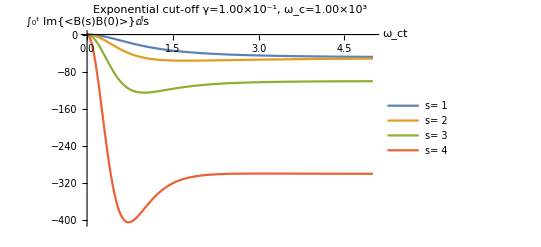

```mathematica
slist={1,2,3,4};

nγ=0.1;
nωc=1000;

Plot[Evaluate@Table[IntegratedBathCorrelatorImAnalyticalJsExp[s,t/nωc,nγ,nωc],{s,slist}],{t,0,5},PlotLegends->Table[StringForm["s= ``",s],{s,slist}],AxesLabel->{"ω_ct","∫_0^t Im{⟨B(s)B(0)⟩}ⅆs"},PlotLabel-> StringForm["Exponential cut-off\n γ=``, ω_c=``",ScientificForm[nγ,3],ScientificForm[nωc,3]]]
```

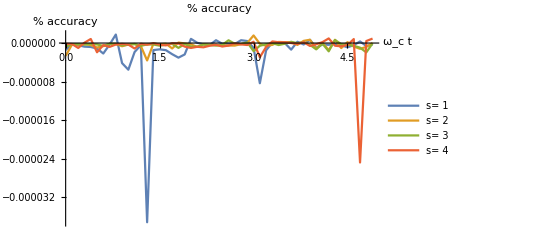

```mathematica
slist={1,2,3,4};

nγ=0.1;
nωc=100;

ListLinePlot[ParallelTable[{t,Module[{tempint=IntegratedBathCorrelatorImNumericalJsExp[s,t/nωc,nγ,nωc]//Quiet},100*(IntegratedBathCorrelatorImAnalyticalJsExp[s,t/nωc,nγ,nωc]-tempint)/tempint]},{s,slist},{t,0.001,5,0.1}],AxesLabel->{"ω_c t","% accuracy"},PlotLabel->"% accuracy",PlotLegends->Table[StringForm["s= ``",s],{s,slist}],PlotRange->All]
```

```mathematica
Limit[IntegratedBathCorrelatorImAnalyticalJsExp[s,t,γ,ωc],t->Infinity]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

ConditionalExpression[-(γ ωc Gamma[1+s])/(2 s), s>0]

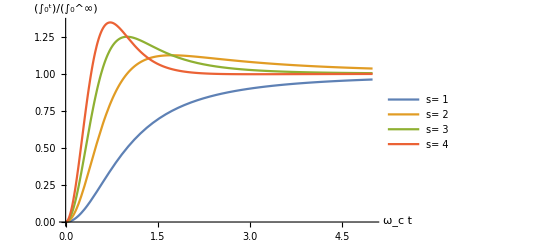

```mathematica
slist={1,2,3,4};

nγ=0.1;
nωc=1000;

Plot[Evaluate@Table[(-(nγ nωc Gamma[1+s])/(2 s))^-1*IntegratedBathCorrelatorImAnalyticalJsExp[s,t/nωc,nγ,nωc],{s,slist}],{t,0,5},PlotLegends->Table[StringForm["s= ``",s],{s,slist}],AxesLabel->{"ω_c t","(∫_0^t)/(∫_0^∞)"},PlotRange->All]
```

#### Total bath correlator

The total bath correlator 
⟨B(t)B(0)⟩ = 1/π∫_0^∞ J(ω)(coth(ω/(2T))cos(ωt)-ⅈ sin(ωt))ⅆω

can be split into two parts

⟨B(t)B(0)⟩ = 1/π∫_0^∞ J(ω)(2n(βω)cos(ωt)+ⅇ^-ⅈωt)ⅆω,

using coth(βω/2)=1+2n(βω), where n(βω)=(ⅇ^βω-1)^-1 is the Bose occupation number.

```mathematica
1/Pi*Integrate[JsExp[ω,s,γ,ωc]*Exp[-ⅈ ω*t],{ω,0,Infinity},Assumptions->s∈PositiveReals]
```

1/2 γ (ⅈ t+1/ωc)^(-1-s) ωc^(1-s) Gamma[1+s]

```mathematica
1/2 ⅇ^(-ω/ωc) π γ ω^s ωc^(1-s)*2/(Exp[ω/T]-1)*Exp[ⅈ ω*t]/.ω->T ω
```

(ⅇ^(ⅈ t T ω-(T ω)/ωc) π γ (T ω)^s ωc^(1-s))/(-1+ⅇ^ω)

```mathematica
T/Pi*Integrate[(ⅇ^(ⅈ t T ω-(T ω)/ωc) π γ (T ω)^s ωc^(1-s))/(-1+ⅇ^ω),{ω,0,Infinity},Assumptions->s∈PositiveReals]
```

T^(1+s) γ ωc^(1-s) Gamma[1+s] Zeta[1+s,1-ⅈ t T+T/ωc]

```mathematica
FullSimplify[T^(1+s) γ ωc^(1-s) Gamma[1+s] Zeta[1+s,1-ⅈ t T+T/ωc],Assumptions->{T,ωc,s}∈PositiveReals]
```

T γ (T/ωc)^s ωc Gamma[1+s] Zeta[1+s,1-ⅈ t T+T/ωc]

```mathematica
BathCorrelatorAnalyticalJsExp[s_,t_,T_,γ_,ωc_]:=1/2 γ (ⅈ t+1/ωc)^(-1-s) ωc^(1-s) Gamma[1+s]+T γ (T/ωc)^s ωc Gamma[1+s] Re[Zeta[1+s,1-ⅈ t T+T/ωc]]
```

Note Zeta[s,a]=HurwitzZeta[s,a] for Re(a)>0

```mathematica
nt=1;
nT=2;
nγ=3;
nωc=4;

ns=1;

BathCorrelatorAnalyticalJsExp[ns,nt,nT,nγ,nωc]//N
actual[ns,nt,nT,nγ,nωc]+ⅈ BathCorrelatorImAnalyticalJsExp[ns,nt,nγ,nωc]//N
```

1.2465-0.66436 ⅈ

1.2465-0.66436 ⅈ

```mathematica
Integrate[BathCorrelatorAnalyticalJsExp[s,tp,T,γ,ωc],{tp,0,t}]
```

∫_0^t (1/2 γ (ⅈ tp+1/ωc)^(-1-s) ωc^(1-s) Gamma[1+s]+T γ (T/ωc)^s ωc Gamma[1+s] Re[Zeta[1+s,1-ⅈ T tp+T/ωc]])ⅆtp

```mathematica
Integrate[1/2 γ (ⅈ tp+1/ωc)^(-1-s) ωc^(1-s) Gamma[1+s],{tp,0,t}]
```

-(ⅈ γ ωc (1-(1+ⅈ t ωc)^-s) Gamma[1+s])/(2 s)

```mathematica
Integrate[T γ (T/ωc)^s ωc Gamma[1+s] Zeta[1+s,1-ⅈ tp T+T/ωc],{tp,0,t}]
```

ⅈ γ (T/ωc)^s ωc Gamma[s] (HurwitzZeta[s,(T+ωc)/ωc]-Zeta[s,1+T (-ⅈ t+1/ωc)])

```mathematica
FullSimplify[ComplexExpand[Re[ⅈ γ (T/ωc)^s ωc Gamma[s] (HurwitzZeta[s,(T+ωc)/ωc]-Zeta[s,1+T (-ⅈ t+1/ωc)])]],Assumptions->{T,ωc,s}∈PositiveReals]
```

-γ (T/ωc)^s ωc Gamma[s] Im[HurwitzZeta[s,(T+ωc)/ωc]-Zeta[s,1+T (-ⅈ t+1/ωc)]]

Note HurwitzZeta[s,a] is always real if s and a are both real, and that Zeta[s,a]=HurwitzZeta[s,a] for Re(a)>0 (a in this case being 1+T/ω_c)

We also need to deal with s=1 separately as both Zeta[s,a]and HurwitzZeta[s,a] diverge when s=1 (harmonic series)

```mathematica
Limit[-(ⅈ γ ωc (1-(1+ⅈ t ωc)^-s) Gamma[1+s])/(2 s)+γ (T/ωc)^s ωc Gamma[s] Im[HurwitzZeta[s,1+T (-ⅈ t+1/ωc)]],s->1]
```

(ⅈ t γ ωc^2)/(2 ⅈ-2 t ωc)-T γ Im[PolyGamma[0,1-ⅈ t T+T/ωc]]

```mathematica
IntegratedBathCorrelatorAnalyticalJsExp[s_,t_,T_,γ_,ωc_]:=If[s==1,(ⅈ t γ ωc^2)/(2 ⅈ-2 t ωc)-T γ Im[PolyGamma[0,1-ⅈ t T+T/ωc]],-(ⅈ γ ωc (1-(1+ⅈ t ωc)^-s) Gamma[1+s])/(2 s)+γ (T/ωc)^s ωc Gamma[s] Im[HurwitzZeta[s,1+T (-ⅈ t+1/ωc)]]]
```

```mathematica
nt=1;
nT=2;
nγ=3;
nωc=4;

ns=1;

IntegratedBathCorrelatorAnalyticalJsExp[ns,nt,nT,nγ,nωc]//N
actualintegrated[ns,nt,nT,nγ,nωc]+ⅈ IntegratedBathCorrelatorImAnalyticalJsExp[ns,nt,nγ,nωc]//N
```

8.01295-5.64706 ⅈ

8.01295-5.64706 ⅈ

```mathematica
Limit[IntegratedBathCorrelatorAnalyticalJsExp[1,t,T,γ,ωc],t->Infinity]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

1/2 γ (π T-ⅈ ωc)

```mathematica
Asymptotic[-(ⅈ γ ωc (1-(1+ⅈ t ωc)^-s) Gamma[1+s])/(2 s)+γ (T/ωc)^s ωc Gamma[s] Im[HurwitzZeta[s,1+T (-ⅈ t+1/ωc)]],t->Infinity]
```

-(ⅈ γ ωc (1-(1+ⅈ t ωc)^-s) Gamma[1+s])/(2 s)+γ (T/ωc)^s ωc Gamma[s] Im[HurwitzZeta[s,1-ⅈ t T+T/ωc]]

The asympotic value of the integrated bath correlation functions is 1/2 γπT - 1/2 ⅈγωc if s=1 and -1/2ⅈγωc Gamma[1+s]/s otherwise.

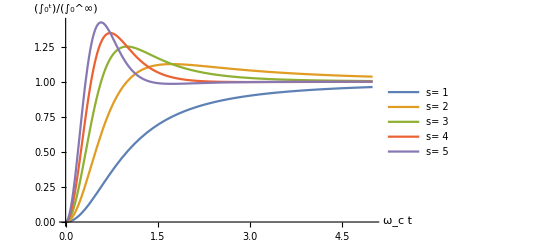

```mathematica
slist={1,2,3,4,5};

nT=1;
nγ=0.1;
nωc=1000;

Plot[Evaluate@Table[(-(nγ nωc Gamma[1+s])/(2 s))^-1*Im@IntegratedBathCorrelatorAnalyticalJsExp[s,t/nωc,nT,nγ,nωc],{s,slist}],{t,0,5},PlotLegends->Table[StringForm["s= ``",s],{s,slist}],AxesLabel->{"ω_c t","(∫_0^t)/(∫_0^∞)"},PlotRange->All]
```

### Spectral Density : General s with hard cut-off (Heaviside theta)

```mathematica
JsHeaviside[s_,ω_,γ_,ωc_]:= π/2 γ ω^s ωc^(1-s) HeavisideTheta[ωc-ω]
```

Calculate the reorganisation energy

```mathematica
2/π*Integrate[ (π/2 γ ω^s ωc^(1-s))/ω,{ω,0,ωc},Assumptions->s∈PositiveReals]
```

(γ ωc)/s

#### Real part of the bath correlator

```mathematica
1/Pi*Integrate[π/2 γ ω^s ωc^(1-s) *Coth[ω/(2*T)]*Cos[ω*t],{ω,0,ωc}]
```

(∫_0^ωc 1/2 π γ ω^s ωc^(1-s) Cos[t ω] Coth[ω/(2 T)]ⅆω)/π

```mathematica
1/Pi*Integrate[π/2 γ ω^s ωc^(1-s) *(2*T*ω)/(ω^2+(2*Pi*T)^2*n^2)*Cos[ω*t],{ω,0,ωc}]
```

(∫_0^ωc (π T γ ω^(1+s) ωc^(1-s) Cos[t ω])/(4 n^2 π^2 T^2+ω^2)ⅆω)/π

Note: I tried doing the integral using complex analysis, choosing the rectangular countour as 𝒞=[-ω_C,ω_C] ∪ [ω_C,ω_C+ⅈy] ∪ [ω_C+ⅈy,-ω_C+ⅈy] ∪ [-ω_C+ⅈy,-ω_C]. When taking the limit as y→∞, the top contour will vanish, however the side contours won't evalulate analytically.

```mathematica
BathCorrelatorReAnalyticalJsHeaviside[s_,t_,γ_,ωc_]:=1
BathCorrelatorReNumericalJsHeaviside[s_,t_,T_,γ_,ωc_]:=1/Pi*NIntegrate[π/2 γ ω^s ωc^(1-s)*Coth[ω/(2*T)]*Cos[ω*t],{ω,0,ωc}]
```

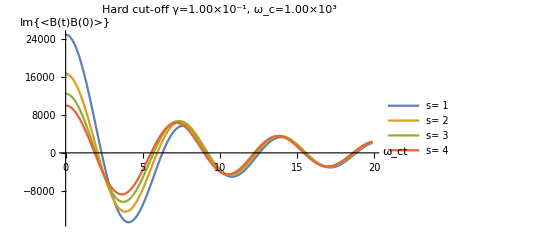

```mathematica
slist={1,2,3,4};

nT=1;
nγ=0.1;
nωc=1000;

ListLinePlot[Table[{t,BathCorrelatorReNumericalJsHeaviside[s,t/nωc,nT,nγ,nωc]},{s,slist},{t,0.01,20,0.1}],PlotLegends->Table[StringForm["s= ``",s],{s,slist}],AxesLabel->{"ω_ct","Im{⟨B(t)B(0)⟩}"},PlotLabel-> StringForm["Hard cut-off\n γ=``, ω_c=``",ScientificForm[nγ,3],ScientificForm[nωc,3]]]
```

#### Imaginary part of the bath correlator

```mathematica
-1/Pi*Integrate[π/2 γ ω^s ωc^(1-s) *Sin[ω*t],{ω,0,ωc}]
```

ConditionalExpression[-(t γ ωc^3 HypergeometricPFQ[{1+s/2},{3/2,2+s/2},-1/4 t^2 ωc^2])/(2 (2+s)), Re[s]>-2]

```mathematica
BathCorrelatorImAnalyticalJsHeaviside[s_,t_,γ_,ωc_]:=-(t γ ωc^3 HypergeometricPFQ[{1+s/2},{3/2,2+s/2},-1/4 t^2 ωc^2])/(2 (2+s))
BathCorrelatorImNumericalJsHeaviside[s_,t_,γ_,ωc_]:=-1/Pi*NIntegrate[π/2 γ ω^s ωc^(1-s)*Sin[ω*t],{ω,0,ωc}]
```

```mathematica
BathCorrelatorImAnalyticalJsHeaviside[1,1,2,3]//N 
BathCorrelatorImNumericalJsHeaviside[1,1,2,3]//N
```

-3.1111

-3.1111

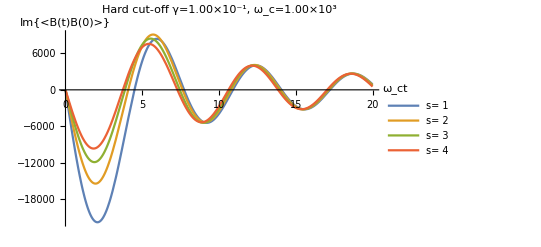

```mathematica
slist={1,2,3,4};

nγ=0.1;
nωc=1000;

Plot[Evaluate@Table[BathCorrelatorImAnalyticalJsHeaviside[s,t/nωc,nγ,nωc],{s,slist}],{t,0.01,20},PlotLegends->Table[StringForm["s= ``",s],{s,slist}],AxesLabel->{"ω_ct","Im{⟨B(t)B(0)⟩}"},PlotLabel-> StringForm["Hard cut-off\n γ=``, ω_c=``",ScientificForm[nγ,3],ScientificForm[nωc,3]]]
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

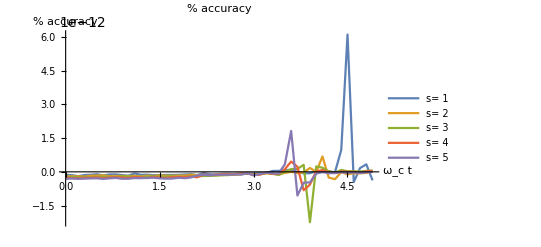

```mathematica
slist={1,2,3,4,5};

nγ=0.1;
nωc=100;

ListLinePlot[ParallelTable[{t,100*(BathCorrelatorImAnalyticalJsHeaviside[s,t/nωc,nγ,nωc]-BathCorrelatorImNumericalJsHeaviside[s,t/nωc,nγ,nωc]//Quiet)/(BathCorrelatorImAnalyticalJsHeaviside[s,t/nωc,nγ,nωc]//Quiet)},{s,slist},{t,0.001,5,0.1}],AxesLabel->{"ω_c t","% accuracy"},PlotLabel->"% accuracy",PlotLegends->Table[StringForm["s= ``",s],{s,slist}],PlotRange->All]
```

```mathematica
Integrate[BathCorrelatorImAnalyticalJsHeaviside[s,tp,γ,ωc],{tp,0,t}]//FullSimplify
```

(γ ωc ((2+s) (-1+Cos[t ωc])+t^2 ωc^2 HypergeometricPFQ[{1+s/2},{3/2,2+s/2},-1/4 t^2 ωc^2]))/(2 s (2+s))

```mathematica
IntegratedBathCorrelatorImAnalyticalJsHeaviside[s_,t_,γ_,ωc_]:=(γ ωc ((2+s) (-1+Cos[t ωc])+t^2 ωc^2 HypergeometricPFQ[{1+s/2},{3/2,2+s/2},-1/4 t^2 ωc^2]))/(2 s (2+s))

IntegratedBathCorrelatorImNumericalJsHeaviside[s_,t_,γ_,ωc_]:=-1/Pi*NIntegrate[π/2 γ ω^s ωc^(1-s)*Sin[ω*tp],{ω,0,ωc},{tp,0,t}]
```

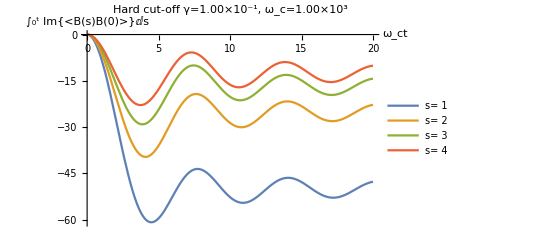

```mathematica
slist={1,2,3,4};

nγ=0.1;
nωc=1000;

Plot[Evaluate@Table[IntegratedBathCorrelatorImAnalyticalJsHeaviside[s,t/nωc,nγ,nωc],{s,slist}],{t,0.01,20},PlotLegends->Table[StringForm["s= ``",s],{s,slist}],AxesLabel->{"ω_ct","∫_0^t Im{⟨B(s)B(0)⟩}ⅆs"},PlotLabel-> StringForm["Hard cut-off\n γ=``, ω_c=``",ScientificForm[nγ,3],ScientificForm[nωc,3]]]
```

```mathematica
Assuming[s∈PositiveIntegers,Limit[IntegratedBathCorrelatorImAnalyticalJsHeaviside[s,t,γ,ωc],t->Infinity]]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

TerminatedEvaluation[RecursionLimit]

```mathematica
Limit[Table[IntegratedBathCorrelatorImAnalyticalJsHeaviside[s,t,γ,ωc],{s,1,10}],t->Infinity]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

{-(γ ωc)/2,-(γ ωc)/4,-(γ ωc)/6,-(γ ωc)/8,-(γ ωc)/10,-(γ ωc)/12,-(γ ωc)/14,-(γ ωc)/16,-(γ ωc)/18,-(γ ωc)/20}

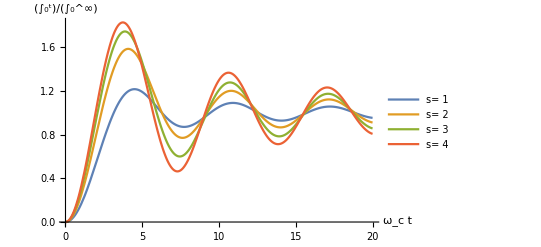

```mathematica
slist={1,2,3,4};

nγ=0.1;
nωc=1000;

Plot[Evaluate@Table[(-(nγ nωc)/(2 s))^-1*IntegratedBathCorrelatorImAnalyticalJsHeaviside[s,t/nωc,nγ,nωc],{s,slist}],{t,0.01,20},PlotLegends->Table[StringForm["s= ``",s],{s,slist}],AxesLabel->{"ω_c t","(∫_0^t)/(∫_0^∞)"},PlotRange->All]
```

### Spectral Density : Gaussian (maybe)

```mathematica
PDF[NormalDistribution[ωs,γ],ω]
```

(ⅇ^(-(ω-ωs)^2/(2 γ^2)))/(√(2 π) γ)

```mathematica
1/Pi*Integrate[λ/(γ Sqrt[2 π])*Exp[-1/2((ω-ωs)/γ)^2]*Exp[-ⅈ ω*t],{ω,0,Infinity},Assumptions->t∈PositiveReals]
```

(ⅇ^(-1/2 t (t γ^2+2 ⅈ ωs)) λ (1-ⅈ Erfi[(t γ^2+ⅈ ωs)/(√2 γ)]))/(2 π)

```mathematica
1/Pi*Integrate[(λ ω)/(γ Sqrt[2 π])*Exp[-1/2((ω-ωs)/γ)^2]*2/(1-Exp[-ω/T])*Exp[-ⅈ ω*t],{ω,0,Infinity},Assumptions->t∈PositiveReals]
```

Integrate[(ⅇ^(-ⅈ t ω-(ω-ωs)^2/(2 γ^2)) √(2/π) λ ω)/((1-ⅇ^(-ω/T)) γ),{ω,0,∞},Assumptions→t∈ℝ&&t>0]/π

```mathematica
FourierTransform[(λ ω)/(γ Sqrt[2 π])*Exp[-1/2((ω-ωs)/γ)^2]*2/(1-Exp[-ω/T]),ω,t]
```

$Aborted

```mathematica
Limit[(λ ω)/(γ Sqrt[2 π])*Exp[-1/2((ω-ωs)/γ)^2]*2/(1-Exp[-ω/T])*Exp[-ⅈ ω*t],ω->0]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

(ⅇ^(-ωs^2/(2 γ^2)) √(2/π) T λ)/γ

```mathematica
1/Pi*FourierTransform[λ/(γ Sqrt[2 π])*Exp[-1/2((ω-ωs)/γ)^2]*2/(1-Exp[-ω/T]),ω,t]
```

FourierTransform[(ⅇ^(-(ω-ωs)^2/(2 γ^2)) √(2/π) λ)/((1-ⅇ^(-ω/T)) γ),ω,t]/π

```mathematica
λ/(γ Sqrt[2 π])*Exp[-1/2((ω-ωs)/γ)^2]*2/(Exp[ω/T]-1)*Exp[ⅈ ω*t]/.ω->T ω
```

(ⅇ^(ⅈ t T ω-(T ω-ωs)^2/(2 γ^2)) √(2/π) λ)/((-1+ⅇ^ω) γ)

```mathematica
T/Pi*Integrate[(ⅇ^(ⅈ t T ω-(T ω-ωs)^2/(2 γ^2)) √(2/π) λ)/((-1+ⅇ^ω) γ),{ω,0,Infinity}]
```

Integrate::idiv: Integral of (ⅇ^(ⅈ t T ω-(-T ω+ωs)^2/(2 γ^2)) √(2/π) λ)/((-1+ⅇ^ω) γ) does not converge on {0,∞}.

(T ∫_0^∞ (ⅇ^(ⅈ t T ω-(T ω-ωs)^2/(2 γ^2)) √(2/π) λ)/((-1+ⅇ^ω) γ)ⅆω)/π

## System timescales and the Markov approximation

### Explanation

The system’s Green’s function matrix G(t) is given by ℒ_t^-1 Ĝ(s)=1/(2π ⅈ) Σ_k∫_(σ-ⅈ ∞)^(σ+ⅈ ∞) Ĝ(s)ⅇ^(s t)ⅆs, where Re(s)>=σ and the real σ lies to the right of all poles of Ĝ(s). Where, for example, (Ĝ(s))_11=(Ĝ(s))_22=s/(s^2+ω_0^2+ω_R^2-χ̂(s)). 
When doing the inverse Laplace transform, the poles of the integrand define the frequency scales over which the real-time Green’s function (and thus the system) evolves. 

To show this, if we analytically continue Ĝ(s) everywhere to Re(s)<σ  except the poles, then Ĝ(s) must have the form (Ĝ(s))_ij=Σ_k c_k/(s-s_k)+A(s), where c_k and s_k are the residues and poles and A(s) is some analytic part. The integration contour can be shifted to Re(s) → −∞ providing that it cannot cross the poles, as shown in the figure below. 
(This is proven by making a closed loop out of the old and the new contours, joining them at ±i∞, and noting that this loop encloses no poles).

Now the inverse Laplace transform gives (G(t))_ij=ℒ_t^-1(Ĝ(s))_ij=1/(2π ⅈ) Σ_k∫_C c_k/(s-s_k)ⅇ^(s t)ⅆs, where C is the new shifted contour. The contributions from the horizontal segments leading towards and away from the poles cancel, however we need the integral over horizontal segments to vanish with Im(s) → ±∞ to vanish. This is fine provided Ĝ(±i∞) = 0, which is usually satisfied.

For the vertical parts of the contour, the exponential part becomes ⅇ^(Re(s) t)ⅇ^(ⅈ Im(s) t), where Re(s) → −∞. If Ĝ(s) does not grow too fast at large s, the integral along the vertical part of the contour may also vanish at any finite t, but this might not guaranteed in general.

What is left gives us (G(t))_ij=Σ_k c_k ⅇ^(s_k t). This means that the real part of the poles s_k give the frequencies at which the system evolves, and so 1/Re(s_k) are the system correlation time-scales. (Note that while it looks like G(t) will be complex, it ends up being real - due to the constraints of physicality at the formulation of the problem). 
The actual system correlation time will be dominated by the largest of the time-scales, which will be given by the pole s_k with the smallest real part. 

The Green’s function matrix G(t) has the form G = (g_1 | g_2
g_3 | g_1), where
g_1(s)= s/(s^2+ω_0^2+ ω_R^2-χ̂(s)), g_2(s)= 1/(s^2+ω_0^2+ ω_R^2-χ̂(s)), g_3(s)= (χ̂(s)-ω0^2- ω_R^2)/(s^2+ω_0^2+ ω_R^2-χ̂(s)).

χ̂(s) is the Laplace transform of the susceptibility and ω_R is the renormalization frequency. Recall that χ(t) is defined as χ(t)=2/π∫_0^∞ J(ω)sin(ω t) Θ(t)ⅆω. Since ℒ_t[sin(ω t) Θ(t)](s)=ω/(s^2+ω^2), χ̂(s) then reads

χ̂(s)=2/π∫_0^∞ (J(ω)ω)/(s^2+ω^2)ⅆω.

The poles s_k (and thus the system correlation times) are thus the solution to the equation

χ̂(s_k)=s_k^2+ω_0^2+ ω_R^2,

where ω_R^2=2/π∫_0^∞ (J(ω))/ω ⅆω.

The Markov approximation is satisfied if τ_C<< τ_S, or τ_C/τ_S<<1, where τ_S is the system time-scale and τ_C is the bath correlation time-scale.

For non-Markovian behaviour over the general evolution of the system (given by the largest time-scale of the pole of the Green’s function), we require τ_C f_S<< 1, where f_s=min(Re(s_k)) (f here indicating frequency).

### Lorentz-Drude

```mathematica
χLapaceLD[s_,γ_,ωc_]:=(2 γ ωc^2)/(s+ωc)
```

```mathematica
Reduce[-(2 γ ωc^2)/(s+ωc)+s^2+ω0^2+2 γ ωc==0,s]
```

(s==Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]||s==Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]||s==Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3])&&s+ωc≠0

```mathematica
polesLD[ω0_,γ_,ωc_]:=Table[N[Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,i]],{i,1,3}]
τsystemListLD[ω0_,γ_,ωc_]:=Table[-(N[Re[Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,i]]])^-1,{i,1,3}]
τsystemListLD::usage="τsystemListLD[ω0,γ,ωc] gives a list of the system time-scales for a Lorentz-Drude spectral density.";
```

```mathematica
nω0=1;
nγ=0.01;
nωc=100;

polesLD[nω0,nγ,nωc]
τsystemListLD[nω0,nγ,nωc]
```

{-99.98,-0.010001-1.00005 ⅈ,-0.010001+1.00005 ⅈ}

{0.010002,99.99,99.99}

```mathematica
nω0=100;
nγ=10;
nωc=100;

polesLD[nω0,nγ,nωc]
τsystemListLD[nω0,nγ,nωc]
markovTestLD[nω0,nγ,nωc]
```

{-90.0546,-4.97269-105.26 ⅈ,-4.97269+105.26 ⅈ}

{0.0111044,0.201098,0.201098}

0.0497269

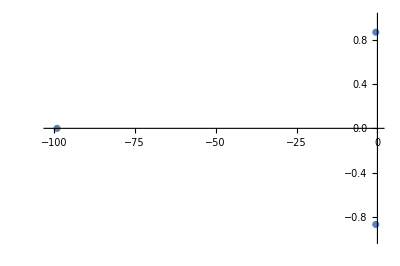

```mathematica
nω0=1;
nγ=0.5;
nωc=100;
ComplexListPlot[polesLD[nω0,nγ,nωc],AspectRatio->2/3,PlotRange->{{-(nωc+1),0.01},{-nω0,nω0}}]
```

```mathematica
nωc=100;

nω0max=5;
nγmax=3;

Animate[ComplexListPlot[polesLD[ω0,γ,nωc],AspectRatio->2/3,PlotLabel->StringForm["ω_0=``, γ=``",ScientificForm[ω0,3],ScientificForm[γ,3]],PlotRange->{{-(nωc+1),0.01},{-nω0max,nω0max}},GridLines->{{-nωc/3},{}}],{ω0,0,nω0max},{γ,0,nγmax},AnimationRunning->False]
```

```mathematica
nω0=1;
nωc=10;

Animate[ParametricPlot[##,Evaluated->True,PlotStyle->Thick,AspectRatio->2/3,ImageSize->Medium,GridLines->{{-nωc/3},{}}]&@@@{{Table[ReIm[polesLD[nω0,γ,nωc][[i]]],{i,1,3}],{γ,0,γmax}}},{γmax,0.01,1},AnimationRunning->False]
```

The bath-correlation timescale for an Ohmic spectral density with a Lorentz-Drude cut-off is τ_C=Max{1/ω_c,1/(2πT)}.
Start with only considering the 1/ω_c time-scale.

```mathematica
markovTestLD[ω0_,γ_,ωc_]:=1/ωc*Min[Re[N[Table[-Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,i],{i,1,3}]]]]
markovTestLD::usage="markovTestLD[ω0,γ,ωc] gives the ratio of the largest bath correlation time (not including temperature) to the largest system time, for a Lorentz-Drude spectral density. The dynamics are expected to be Markovian for a smaller values.";

markovTestTempLD[T_,ω0_,γ_,ωc_]:=Max[1/ωc,1/(2 π T)]*Min[Re[N[Table[-Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,i],{i,1,3}]]]]
markovTestTempLD::usage="markovTestTempLD[T,ω0,γ,ωc] gives the ratio of the largest bath correlation time (including temperature) to the largest system time, for a Lorentz-Drude spectral density. The dynamics are expected to be Markovian for a smaller values.";
```

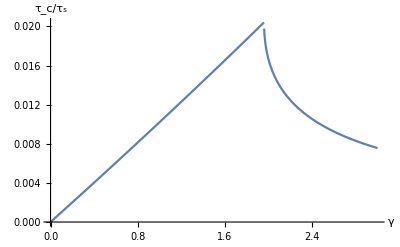

```mathematica
nω0=2;
nωc=100;
Plot[markovTestLD[nω0,γ,nωc],{γ,0,3},AxesLabel->{"γ","τ_c/τ_s"},PlotRange->All]
```

Sanity check: see what happens in the limit ω_c-> ∞

```mathematica
Simplify[ComplexExpand[Re[Asymptotic[ToRadicals[-Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,1]],ωc->Infinity]]]]
Simplify[ComplexExpand[Re[Asymptotic[ToRadicals[-Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,2]],ωc->Infinity]]]]
Simplify[ComplexExpand[Re[Asymptotic[ToRadicals[-Root[ω0^2 ωc+(ω0^2+2 γ ωc) #1+ωc #1^2+#1^3&,3]],ωc->Infinity]]]]
```

Piecewise[{{γ, γ^2≤ω0^2}, {γ-√(γ^2-ω0^2), True}}]

ωc

Series::ztest1: Unable to decide whether numeric quantity 1/3+1/6 (-1)^(1/3)-1/6 (-1)^(2/3)-(-1)^(1/6)/(2 √3)+(-1)^(5/6)/(2 √3) is equal to zero. Assuming it is.

Piecewise[{{γ, γ^2≤ω0^2}, {γ+√(γ^2-ω0^2), True}}]

```mathematica
1/3+1/6 (-1)^(1/3)-1/6 (-1)^(2/3)-(-1)^(1/6)/(2 √3)+(-1)^(5/6)/(2 √3)//N
```

-2.22045×10^-16+0. ⅈ

Since γ is usually small (for the Born approximation), we have the 2 system frequencies γ,ω_c. 

Then the ratio of the (largest) correlation time with the (largest) system time is τ_c/τ_s=Max{1/ω_c,1/(2π T)}*Min{γ,ω_c}=(Min{γ,ω_c})/(Min{ω_c , 2π T}). 

This means that in the limit of an infinite cut-off, ω_c-> ∞, τ_c/τ_s=γ/(2π T). So we will only have Markovian behaviour at high temperatures.

### Structured Lorentz-Drude

```mathematica
Reduce[-λ^2/(ωs^2+s^2 +γ*s)+s^2+ω0^2+λ^2/ωs^2==0,s]
```

ωs≠0&&(s==Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]||s==Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]||s==Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]||s==Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4])&&s^2+s γ+ωs^2≠0

```mathematica
polesSLD[ω0_,γ_,λ_,ωs_]:=Table[N[Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,i]],{i,1,4}]

τsystemListSLD[ω0_,γ_,λ_,ωs_]:=Table[(-N[Re[Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,i]]])^-1,{i,1,4}]
τsystemListSLD::usage="τsystemListSLD[ω0,γ,λ,ωs] gives a list of the system time-scales for a Structured Lorentz-Drude spectral density";
```

```mathematica
polesSLD[2,3,4,5]
```

{-1.45071-4.82861 ⅈ,-1.45071+4.82861 ⅈ,-0.0492944-1.98279 ⅈ,-0.0492944+1.98279 ⅈ}

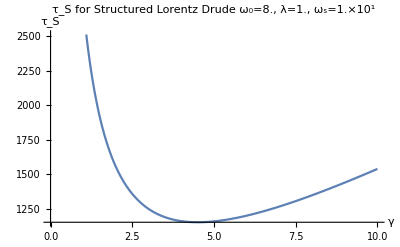

```mathematica
nω0=8;
nλ=1;
nωs=10;

Plot[Max@τsystemListSLD[nω0,γ,nλ,nωs],{γ,0,10},AxesLabel->{"γ","τ_S"},PlotLabel->StringForm["τ_S for Structured Lorentz Drude\nω_0=``, λ=``, ω_s=``",ScientificForm[N[nω0]],ScientificForm[N[nλ]],ScientificForm[N[nωs]]]]
```

The bath-correlation timescale for an Ohmic spectral density with a Structured Lorentz-Drude cut-off is τ_C=2/γ.

```mathematica
markovTestSLD[ω0_,γ_,λ_,ωs_]:=2/γ*Min[Table[-Re[N[Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,i]]],{i,1,4}]]
markovTestSLD::usage="markovTestSLD[ω0,γ,λ,ωs] gives the ratio of the largest bath correlation time (not including temperature) to the largest system time, for a Structured Lorentz-Drude spectral density. The dynamics are expected to be Markovian for a smaller values.";

markovTestTempSLD[T_,ω0_,γ_,λ_,ωs_]:=Max[2/γ,1/(2 π T)]*Min[Table[-Re[N[Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,i]]],{i,1,4}]]
markovTestTempSLD::usage="markovTestTempSLD[T,ω0,γ,λ,ωs] gives the ratio of the largest bath correlation time (including temperature) to the largest system time, for a Structured Lorentz-Drude spectral density. The dynamics are expected to be Markovian for a smaller values.";
```

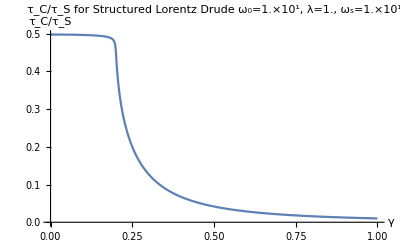

```mathematica
nω0=10;
nλ=1;
nωs=10;

Plot[markovTestSLD[nω0,γ,nλ,nωs],{γ,0,1},AxesLabel->{"γ","τ_C/τ_S"},PlotLabel->StringForm["τ_C/τ_S for Structured Lorentz Drude\nω_0=``, λ=``, ω_s=``",ScientificForm[N[nω0]],ScientificForm[N[nλ]],ScientificForm[N[nωs]]]]
```

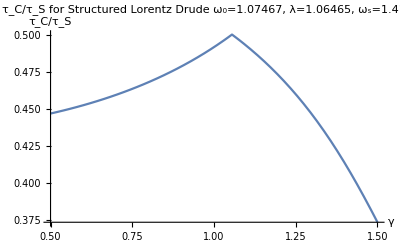

```mathematica
nω0=1.07467;
(*nγ=1.055;*)
nλ=1.06465;
nωs=1.41419;
Plot[markovTestSLD[nω0,γ,nλ,nωs],{γ,0.5,1.5},AxesLabel->{"γ","τ_C/τ_S"},PlotLabel->StringForm["τ_C/τ_S for Structured Lorentz Drude\nω_0=``, λ=``, ω_s=``",ScientificForm[N[nω0]],ScientificForm[N[nλ]],ScientificForm[N[nωs]]]]
```

```mathematica
ToRadicals[Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]]
```

-γ/4+1/2 √(γ^2/4-(2 (λ^2+ω0^2 ωs^2+ωs^4))/(3 ωs^2)+(2^(1/3) (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2))/(3 ωs^2 (27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2))^(1/3))+1/(3 2^(1/3) ωs^2)(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2))^(1/3))+1/2 √(γ^2/2-(4 (λ^2+ω0^2 ωs^2+ωs^4))/(3 ωs^2)-(2^(1/3) (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2))/(3 ωs^2 (27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2))^(1/3))-1/(3 2^(1/3) ωs^2)(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2))^(1/3)+(-γ^3-(8 (γ λ^2+γ ω0^2 ωs^2))/ωs^2+(4 γ (λ^2+ω0^2 ωs^2+ωs^4))/ωs^2)/(4 √(γ^2/4-(2 (λ^2+ω0^2 ωs^2+ωs^4))/(3 ωs^2)+(2^(1/3) (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2))/(3 ωs^2 (27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2))^(1/3))+1/(3 2^(1/3) ωs^2)(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2))^(1/3))))

```mathematica
Simplify[ComplexExpand[Re[ToRadicals[Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4]]]]]
```

-γ/4+1/2 Cos[1/2 Arg[γ^2/4-(2 (λ^2+ω0^2 ωs^2+ωs^4))/(3 ωs^2)+(2^(1/3) (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2))/(3 ωs^2 (27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2))^(1/3))+1/(3 2^(1/3) ωs^2)(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2))^(1/3)]] ((((γ^2/4-(2 (λ^2+ω0^2 ωs^2+ωs^4))/(3 ωs^2)+(2^(1/3) (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2) Cos[1/3 Arg[27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)]])/(3 ωs^2 ((27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+((-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)^2)^(1/4) Cos[1/2 Arg[-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2]])^2+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)^2 Sin[1/2 Arg[-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2]]^2)^(1/6))+1/(3 2^(1/3) ωs^2)Cos[1/3 Arg[27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)]] ((27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+((-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)^2)^(1/4) Cos[1/2 Arg[-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2]])^2+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)^2 Sin[1/2 Arg[-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2]]^2)^(1/6)))^2+((-((2^(1/3) (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2) Sin[1/3 Arg[27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)]])/(3 ωs^2 ((27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+((-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)^2)^(1/4) Cos[1/2 Arg[-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2]])^2+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)^2 Sin[1/2 Arg[-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2]]^2)^(1/6)))+1/(3 2^(1/3) ωs^2)((27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+((-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)^2)^(1/4) Cos[1/2 Arg[-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2]])^2+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)^2 Sin[1/2 Arg[-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2]]^2)^(1/6) Sin[1/3 Arg[27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)]]))^2))^(1/4)+1/2 Cos[1/2 Arg[γ^2/2-(4 (λ^2+ω0^2 ωs^2+ωs^4))/(3 ωs^2)-(2^(1/3) (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2))/(3 ωs^2 (27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2))^(1/3))-1/(3 2^(1/3) ωs^2)(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2))^(1/3)+(-γ^3-(8 (γ λ^2+γ ω0^2 ωs^2))/ωs^2+(4 γ (λ^2+ω0^2 ωs^2+ωs^4))/ωs^2)/(4 √(γ^2/4-(2 (λ^2+ω0^2 ωs^2+ωs^4))/(3 ωs^2)+(2^(1/3) (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2))/(3 ωs^2 (27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2))^(1/3))+1/(3 2^(1/3) ωs^2)(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2))^(1/3)))]] ((((γ^2/2-(4 (λ^2+ω0^2 ωs^2+ωs^4))/(3 ωs^2)-(2^(1/3) (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2) Cos[1/3 Arg[27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)]])/(3 ωs^2 ((27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+((-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)^2)^(1/4) Cos[1/2 Arg[-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2]])^2+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)^2 Sin[1/2 Arg[-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2]]^2)^(1/6))-1/(3 2^(1/3) ωs^2)Cos[1/3 Arg[27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)]] ((27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+((-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)^2)^(1/4) Cos[1/2 Arg[-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2]])^2+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)^2 Sin[1/2 Arg[-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2]]^2)^(1/6)+((-γ^3/4-γ ω0^2-(γ λ^2)/ωs^2+γ ωs^2) Cos[1/2 Arg[γ^2/4-(2 (λ^2+ω0^2 ωs^2+ωs^4))/(3 ωs^2)+(2^(1/3) (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2))/(3 ωs^2 (27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2))^(1/3))+1/(3 2^(1/3) ωs^2)(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2))^(1/3)]])/((((γ^2/4-(2 (λ^2+ω0^2 ωs^2+ωs^4))/(3 ωs^2)+(2^(1/3) (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2) Cos[1/3 Arg[27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)]])/(3 ωs^2 ((27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+((-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)^2)^(1/4) Cos[1/2 Arg[-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2]])^2+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)^2 Sin[1/2 Arg[-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2]]^2)^(1/6))+1/(3 2^(1/3) ωs^2)Cos[1/3 Arg[27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)]] ((27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+((-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)^2)^(1/4) Cos[1/2 Arg[-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2]])^2+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)^2 Sin[1/2 Arg[-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2]]^2)^(1/6)))^2+((-((2^(1/3) (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2) Sin[1/3 Arg[27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)]])/(3 ωs^2 ((27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+((-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)^2)^(1/4) Cos[1/2 Arg[-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2]])^2+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)^2 Sin[1/2 Arg[-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2]]^2)^(1/6)))+1/(3 2^(1/3) ωs^2)((27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+((-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)^2)^(1/4) Cos[1/2 Arg[-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2]])^2+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)^2 Sin[1/2 Arg[-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2]]^2)^(1/6) Sin[1/3 Arg[27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)]]))^2))^(1/4)))^2+(((2^(1/3) (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2) Sin[1/3 Arg[27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)]])/(3 ωs^2 ((27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+((-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)^2)^(1/4) Cos[1/2 Arg[-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2]])^2+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)^2 Sin[1/2 Arg[-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2]]^2)^(1/6))-1/(3 2^(1/3) ωs^2)((27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+((-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)^2)^(1/4) Cos[1/2 Arg[-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2]])^2+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)^2 Sin[1/2 Arg[-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2]]^2)^(1/6) Sin[1/3 Arg[27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)]]-((-γ^3/4-γ ω0^2-(γ λ^2)/ωs^2+γ ωs^2) Sin[1/2 Arg[γ^2/4-(2 (λ^2+ω0^2 ωs^2+ωs^4))/(3 ωs^2)+(2^(1/3) (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2))/(3 ωs^2 (27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2))^(1/3))+1/(3 2^(1/3) ωs^2)(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2))^(1/3)]])/((((γ^2/4-(2 (λ^2+ω0^2 ωs^2+ωs^4))/(3 ωs^2)+(2^(1/3) (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2) Cos[1/3 Arg[27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)]])/(3 ωs^2 ((27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+((-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)^2)^(1/4) Cos[1/2 Arg[-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2]])^2+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)^2 Sin[1/2 Arg[-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2]]^2)^(1/6))+1/(3 2^(1/3) ωs^2)Cos[1/3 Arg[27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)]] ((27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+((-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)^2)^(1/4) Cos[1/2 Arg[-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2]])^2+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)^2 Sin[1/2 Arg[-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2]]^2)^(1/6)))^2+((-((2^(1/3) (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2) Sin[1/3 Arg[27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)]])/(3 ωs^2 ((27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+((-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)^2)^(1/4) Cos[1/2 Arg[-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2]])^2+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)^2 Sin[1/2 Arg[-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2]]^2)^(1/6)))+1/(3 2^(1/3) ωs^2)((27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+((-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)^2)^(1/4) Cos[1/2 Arg[-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2]])^2+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)^2 Sin[1/2 Arg[-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2]]^2)^(1/6) Sin[1/3 Arg[27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3+√(-4 (12 ω0^2 ωs^6-3 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2)+(λ^2+ω0^2 ωs^2+ωs^4)^2)^3+(27 γ^2 ω0^2 ωs^8+27 ωs^2 (γ λ^2+γ ω0^2 ωs^2)^2-72 ω0^2 ωs^6 (λ^2+ω0^2 ωs^2+ωs^4)-9 γ ωs^2 (γ λ^2+γ ω0^2 ωs^2) (λ^2+ω0^2 ωs^2+ωs^4)+2 (λ^2+ω0^2 ωs^2+ωs^4)^3)^2)]]))^2))^(1/4)))^2))^(1/4)

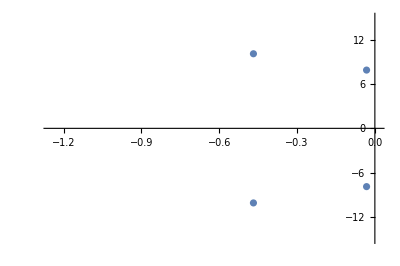

```mathematica
nω0=8;
nγ=1;
nλ=10;
nωs=10;
ComplexListPlot[polesSLD[nω0,nγ,nλ,nωs],AspectRatio->2/3,PlotRange->{{-(nγ/4+1),0.01},{-(Max[nω0,nωs]+5),Max[nω0,nωs]+5}}]
```

```mathematica
nωs=2;
nλ=1;

nω0max=3;
nγmax=1;

Animate[ComplexListPlot[polesSLD[ω0,γ,nλ,nωs],AspectRatio->2/3,PlotLabel->StringForm["ω_0=``, γ=``",ScientificForm[ω0,3],ScientificForm[γ,3]],PlotRange->{{-(γ/4+1),0.01},{-(Max[ω0,nωs]+5),Max[ω0,nωs]+5}},GridLines->{{-γ/4},{}},Epilog->Inset[Framed[Style[StringForm["τ_c=``, τ_s=``, τ_c/τ_s=``",ScientificForm[2/γ,3],ScientificForm[Max[τsystemListSLD[ω0,γ,nλ,nωs]],3],ScientificForm[2/(γ*Max[τsystemListSLD[ω0,γ,nλ,nωs]]),3]],10],Background->LightYellow],{Left,Bottom},{Left,Bottom}]],{ω0,0.01,nω0max},{γ,0.01,nγmax},AnimationRunning->False]
```

### General s with exponential cut-off

```mathematica
2/π*Integrate[JsExp[ω,s,γ,ωc] Sin[ω t],{ω,0,Infinity},Assumptions->s∈PositiveReals]
```

γ ωc^2 (1+t^2 ωc^2)^(-1/2-s/2) Gamma[1+s] Sin[(1+s) ArcTan[t ωc]]

```mathematica
χs[s_,t_,γ_,ωc_]:=γ ωc^2 (1+t^2 ωc^2)^(-1/2-s/2) s! Sin[(1+s) ArcTan[t ωc]]
```

```mathematica
Assuming[s∈PositiveIntegers,LaplaceTransform[χs[s,t,γ,ωc],t,p]]
```

γ ωc^2 s! LaplaceTransform[(1+t^2 ωc^2)^(-1/2-s/2) Sin[(1+s) ArcTan[t ωc]],t,p]

Rewrite Sin[(1+s) ArcTan[t ω_c]]

First using the Chebyshev polynomials of the second kind U_n, defined as U_n(cos θ)sin θ=sin((n+1)θ)
Let  θ=arctan(t ω_c), so cos θ=1/(√(1+(tω_c)^2)) and sin θ=(t ω_c)/(√(1+(tω_c)^2))

Alternatively, expand arctan(x)=ⅈ/2 ln((1-ⅈx)/(1+ⅈx)) and sin(x)=ⅈ/2(ⅇ^-ⅈx-ⅇ^ⅈx)

So sin(n arctan(x))=ⅈ/2 exp(-ⅈ ⅈ/2 n ln((1-ⅈx)/(1+ⅈx)))-ⅈ/2 exp(ⅈ ⅈ/2 n ln((1-ⅈx)/(1+ⅈx)))
=ⅈ/2((1-ⅈx)^(n/2)/(1+ⅈx)^(n/2)-(1+ⅈx)^(n/2)/(1-ⅈx)^(n/2))=ⅈ/2(((1-ⅈx)^n-(1+ⅈx)^n)/((x^2+1)^(n/2)))

```mathematica
χs2[s_,t_,γ_,ωc_]:=t γ ωc^3 (1+t^2 ωc^2)^(-1-s/2) ChebyshevU[s,1/(√(1+t^2 ωc^2))] s!
χs3[s_,t_,γ_,ωc_]:=1/2 ⅈ γ ωc^2 (1+t^2 ωc^2)^(-1-s) ((1-ⅈ t ωc)^(1+s)-(1+ⅈ t ωc)^(1+s)) s!
```

```mathematica
χs[1,2,3,4]//N
χs2[1,2,3,4]//N
χs3[1,2,3,4]//N
```

0.181775

0.181775

0.181775

```mathematica
Assuming[s∈PositiveReals,LaplaceTransform[χs3[s,t,γ,ωc],t,p]]
```

1/2 ⅈ γ ωc^2 (-(ⅈ ⅇ^(-(ⅈ p)/ωc) ExpIntegralE[1+s,-(ⅈ p)/ωc])/ωc-(ⅈ ⅇ^((ⅈ p)/ωc) ExpIntegralE[1+s,(ⅈ p)/ωc])/ωc) s!

```mathematica
FullSimplify[1/2 ⅈ γ ωc^2 (-(ⅈ ⅇ^(-(ⅈ p)/ωc) ExpIntegralE[1+s,-(ⅈ p)/ωc])/ωc-(ⅈ ⅇ^((ⅈ p)/ωc) ExpIntegralE[1+s,(ⅈ p)/ωc])/ωc) s!,s∈PositiveReals]
```

1/2 ⅇ^(-(ⅈ p)/ωc) γ ωc (ExpIntegralE[1+s,-(ⅈ p)/ωc]+ⅇ^((2 ⅈ p)/ωc) ExpIntegralE[1+s,(ⅈ p)/ωc]) s!

```mathematica
ExpIntegralERecursive[n_,z_]:=-Exp[-z]*Sum[z^k/Pochhammer[1-n,k+1],{k,0,n-2}]+(-z)^(n-1)/((n-1)!)ExpIntegralE[1,z]
```

```mathematica
χsLaplace[s_,p_,γ_,ωc_]:=1/2 ⅇ^(-(ⅈ p)/ωc) γ ωc (ExpIntegralE[1+s,-(ⅈ p)/ωc]+ⅇ^((2 ⅈ p)/ωc) ExpIntegralE[1+s,(ⅈ p)/ωc]) s!
χsLaplace2[s_,p_,γ_,ωc_]:=1/2 ⅇ^(-(ⅈ p)/ωc) γ ωc (ExpIntegralERecursive[1+s,-(ⅈ p)/ωc]+ⅇ^((2 ⅈ p)/ωc) ExpIntegralERecursive[1+s,(ⅈ p)/ωc]) s!
```

```mathematica
χsLaplace[3,-2+3ⅈ,0.1,100]
χsLaplace2[3,-2+3ⅈ,0.1,100]
```

20.0043+0.0118249 ⅈ

20.0043+0.0118249 ⅈ

```mathematica
χsLaplace[0.5,-2+3ⅈ,0.1,100]
χsLaplace2[0.5,-2+3ⅈ,0.1,100]
```

14.0299+1.8656 ⅈ

2.08675+0.169766 ⅈ

```mathematica
χsLaplace[s,ⅈ ω,γ,ωc]
```

1/2 ⅇ^(ω/ωc) γ ωc (ⅇ^(-(2 ω)/ωc) ExpIntegralE[1+s,-ω/ωc]+ExpIntegralE[1+s,ω/ωc]) s!

```mathematica
χsLaplace[k,s,γ,ωc]//Expand
```

1/2 ⅇ^(-(ⅈ s)/ωc) γ ωc ExpIntegralE[1+k,-(ⅈ s)/ωc] k!+1/2 ⅇ^((ⅈ s)/ωc) γ ωc ExpIntegralE[1+k,(ⅈ s)/ωc] k!

```mathematica
ⅇ^(-(ⅈ s)/ωc) ExpIntegralE[1+k,-(ⅈ s)/ωc]+ⅇ^((ⅈ s)/ωc) ExpIntegralE[1+k,(ⅈ s)/ωc]//FunctionExpand
```

ⅇ^(-(ⅈ s)/ωc) (-(ⅈ s)/ωc)^k Gamma[-k,-(ⅈ s)/ωc]+ⅇ^((ⅈ s)/ωc) ((ⅈ s)/ωc)^k Gamma[-k,(ⅈ s)/ωc]

```mathematica
χFTJexpstest[s_,ω_,γ_,ωc_]:=1/2 ⅇ^(ω/ωc) γ ωc (ⅇ^(-(2 ω)/ωc) ExpIntegralE[1+s,-ω/ωc]+ExpIntegralE[1+s,ω/ωc]) s!

ExpIntegralERecursiveRetest[n_,z_]:=-Exp[-z]*Sum[z^k/Pochhammer[1-n,k+1],{k,0,n-2}]-(-z)^(n-1)/((n-1)!)ExpIntegralEi[-z]

ReχFTJexpstest[s_,ω_,γ_,ωc_]:=1/2 ⅇ^(ω/ωc) γ ωc (ⅇ^(-(2 ω)/ωc) ExpIntegralERecursiveRetest[1+s,-ω/ωc]+ExpIntegralERecursiveRetest[1+s,ω/ωc]) s!
```

```mathematica
χFTJexpstest[1,ω,γ,ωc]//Simplify
χFTJexpstest[2,ω,γ,ωc]//Simplify
```

1/2 ⅇ^(ω/ωc) γ ωc (ⅇ^(-(2 ω)/ωc) ExpIntegralE[2,-ω/ωc]+ExpIntegralE[2,ω/ωc])

ⅇ^(ω/ωc) γ ωc (ⅇ^(-(2 ω)/ωc) ExpIntegralE[3,-ω/ωc]+ExpIntegralE[3,ω/ωc])

```mathematica
ReχFTJexpstest[1,ω,γ,ωc]//Simplify
ReχFTJexpstest[2,ω,γ,ωc]//Simplify
```

1/2 γ (2 ωc+ⅇ^(ω/ωc) ω ExpIntegralEi[-ω/ωc]-ⅇ^(-ω/ωc) ω ExpIntegralEi[ω/ωc])

(γ (2 ωc^2-ⅇ^(ω/ωc) ω^2 ExpIntegralEi[-ω/ωc]-ⅇ^(-ω/ωc) ω^2 ExpIntegralEi[ω/ωc]))/(2 ωc)

```mathematica
χFTJexpstest[1,2,0.1,100]
ReχFTJexpstest[1,2,0.1,100]
```

9.98266-0.307938 ⅈ

9.98266

Calculate the reorganisation energy

```mathematica
2/π Integrate[ JsExp[ω,s,γ,ωc]/ω,{ω,0,Infinity}]
```

ConditionalExpression[γ ωc Gamma[s], Re[s]>0]

```mathematica
ωR2s[s_,γ_,ωc_]:=γ ωc Gamma[s]
```

```mathematica
Reduce[-χsLaplace[k,s,γ,ωc]+s^2+ω0^2+ωR2s[k,γ,ωc] ==0,s]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[s^2+ω0^2-1/2 ⅇ^(-(ⅈ s)/ωc) γ ωc (ExpIntegralE[1+k,-(ⅈ s)/ωc]+ⅇ^((2 ⅈ s)/ωc) ExpIntegralE[1+k,(ⅈ s)/ωc]) k!+γ ωc Gamma[k]==0,s]

```mathematica
Reduce[-χsLaplace[1,s,γ,ωc]+s^2+ω0^2+ωR2s[1,γ,ωc] ==0,s]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[s^2+ω0^2+γ ωc-1/2 ⅇ^(-(ⅈ s)/ωc) γ ωc (ExpIntegralE[2,-(ⅈ s)/ωc]+ⅇ^((2 ⅈ s)/ωc) ExpIntegralE[2,(ⅈ s)/ωc])==0,s]

```mathematica
Reduce[z^2+ω0^2/ωc^2-1/2 ⅇ^(-ⅈ z) γ/ωc (ExpIntegralE[1+k,-ⅈ z]+ⅇ^(2 ⅈ z) ExpIntegralE[1+k,ⅈ z]) k!+γ/ωc Gamma[k]==0,z]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[z^2+ω0^2/ωc^2-(ⅇ^(-ⅈ z) γ (ExpIntegralE[1+k,-ⅈ z]+ⅇ^(2 ⅈ z) ExpIntegralE[1+k,ⅈ z]) k!)/(2 ωc)+(γ Gamma[k])/ωc==0,z]

```mathematica
χsLaplace[1,s,γ,ωc]
```

1/2 ⅇ^(-(ⅈ s)/ωc) γ ωc (ExpIntegralE[2,-(ⅈ s)/ωc]+ⅇ^((2 ⅈ s)/ωc) ExpIntegralE[2,(ⅈ s)/ωc])

```mathematica
nω0=10;
nγ=0.1;
nωc=1000;

ns=3;

sol=FindRoot[-χsLaplace[ns,s,nγ,nωc]+s^2+nω0^2+ωR2s[ns,nγ,nωc]==0,{s,-0.01+0.1 ⅈ},AccuracyGoal->3,PrecisionGoal->4,MaxIterations->1000]
-χsLaplace[ns,s,nγ,nωc]+s^2+nω0^2+ωR2s[ns,nγ,nωc]/.sol
```

{s→-7.77817×10^-6+9.9995 ⅈ}

-2.66657×10^-7-0.000311065 ⅈ

```mathematica
2/π*Integrate[JsExp[ω,k,γ,ωc]/ω*s^2/(s^2+ω^2),{ω,0,Infinity},Assumptions->k∈Reals]
```

ConditionalExpression[1/2 s^2 γ ωc^(1-k) Csc[(k π)/2] Sec[(k π)/2] (π (1/s^2)^(1-k/2) Cos[(k π)/2+1/(√(1/s^2) ωc)]+ωc^(-2+k) Gamma[-2+k] HypergeometricPFQ[{1},{3/2-k/2,2-k/2},-s^2/(4 ωc^2)] Sin[k π]), Re[s]≠0&&k>0]

```mathematica
sγsLaplacetest[k_,s_,γ_,ωc_]:=1/2 s^2 γ ωc^(1-k) Csc[(k π)/2] Sec[(k π)/2] (π (1/s^2)^(1-k/2) Cos[(k π)/2+1/(√(1/s^2) ωc)]+ωc^(-2+k) Gamma[-2+k] HypergeometricPFQ[{1},{3/2-k/2,2-k/2},-s^2/(4 ωc^2)] Sin[k π])
```

```mathematica
χsLaplace[1.1,-2+ⅈ,0.1,100]
-sγsLaplacetest[1.1,-2+ⅈ,0.1,100]+ωR2s[1.1,0.1,100]
```

9.31369+0.10477 ⅈ

9.31369+0.10477 ⅈ

```mathematica
nω0=1;
nγ=0.1;
nωc=100;

nk=10.01;

sol=FindRoot[sγsLaplacetest[nk,s,nγ,nωc]+s^2+nω0^2,{s,-0.001+0.1ⅈ},MaxIterations->1000]
sγsLaplacetest[nk,s,nγ,nωc]+s^2+nω0^2/.sol
-χsLaplace[nk,s,nγ,nωc]+s^2+nω0^2+ωR2s[nk,nγ,nωc]/.sol
```

{s→-3.16202×10^-21+0.40348 ⅈ}

1.11022×10^-16-1.56907×10^-20 ⅈ

-8.84756×10^-9-4.59988×10^-10 ⅈ

### General s with squared exponential cut-off

```mathematica
2/π*Integrate[1/2 ⅇ^(-ω^2/ωc^2) π γ ω^(s-1) ωc^(1-s),{ω,0,Infinity},Assumptions->s∈PositiveReals]
```

1/2 γ ωc Gamma[s/2]

```mathematica
2/π*Integrate[1/2 ⅇ^(-ω^2/ωc^2) π γ ω^s ωc^(1-s)* Sin[ω t],{ω,0,Infinity},Assumptions->s∈PositiveReals]
```

1/2 t γ ωc^3 Gamma[1+s/2] Hypergeometric1F1[1+s/2,3/2,-1/4 t^2 ωc^2]

```mathematica
χstest[s_,t_,γ_,ωc_]:=1/2 t γ ωc^3 Gamma[1+s/2] Hypergeometric1F1[1+s/2,3/2,-1/4 t^2 ωc^2]
```

```mathematica
LaplaceTransform[χstest[k,t,γ,ωc],t,s]
```

-1/(2 (-1+ⅇ^(ⅈ k π)) k s Gamma[k/2])ⅇ^(s^2/ωc^2) γ ωc Gamma[1+k/2] (4 π (-s^2/ωc^2)^(1/2+k/2) ωc-k s (s^2/ωc^2)^(k/2) Gamma[-k/2] Gamma[k/2]+ⅇ^(ⅈ k π) k s (s^2/ωc^2)^(k/2) Gamma[-k/2] Gamma[k/2]+k s (s^2/ωc^2)^(k/2) Gamma[k/2] Gamma[-k/2,s^2/ωc^2]-ⅇ^(ⅈ k π) k s (s^2/ωc^2)^(k/2) Gamma[k/2] Gamma[-k/2,s^2/ωc^2])

```mathematica
FullSimplify[-1/(2 (-1+ⅇ^(ⅈ k π)) k s Gamma[k/2])ⅇ^(s^2/ωc^2) γ ωc Gamma[1+k/2] (4 π (-s^2/ωc^2)^(1/2+k/2) ωc-k s (s^2/ωc^2)^(k/2) Gamma[-k/2] Gamma[k/2]+ⅇ^(ⅈ k π) k s (s^2/ωc^2)^(k/2) Gamma[-k/2] Gamma[k/2]+k s (s^2/ωc^2)^(k/2) Gamma[k/2] Gamma[-k/2,s^2/ωc^2]-ⅇ^(ⅈ k π) k s (s^2/ωc^2)^(k/2) Gamma[k/2] Gamma[-k/2,s^2/ωc^2]),k ϵ PositiveReals]
```

1/2 ⅇ^(s^2/ωc^2) γ ωc^(1-k) ((2 π (-s^2)^((1+k)/2))/(s-ⅇ^(ⅈ k π) s)+π (s^2)^(k/2) Csc[(k π)/2]+ωc^k ExpIntegralE[1+k/2,s^2/ωc^2] Gamma[1+k/2])

```mathematica
χstestLaplace[k_,s_,γ_,ωc_]:=1/2 ⅇ^(s^2/ωc^2) γ ωc^(1-k) ((2 π (-s^2)^((1+k)/2))/(s-ⅇ^(ⅈ k π) s)+π (s^2)^(k/2) Csc[(k π)/2]+ωc^k ExpIntegralE[1+k/2,s^2/ωc^2] Gamma[1+k/2])
```

```mathematica
χstestLaplace[1,s,γ,ωc]
```

1/2 ⅇ^(s^2/ωc^2) γ (-π s+π √(s^2)+1/2 √π ωc ExpIntegralE[3/2,s^2/ωc^2])

```mathematica
ExpIntegralE[3/2,s^2/ωc^2]//FunctionExpand
```

√(s^2/ωc^2) ((2 ⅇ^(-s^2/ωc^2) s^2)/((s^2/ωc^2)^(3/2) ωc^2)-2 √π (1-(√(s^2/ωc^2) ωc Erf[s/ωc])/s))

```mathematica
NSolve[-χstestLaplace[1,s,nγ,nωc]+s^2+nω0^2+1/2 nγ nωc Gamma[1/2]==0,s]
```

$Aborted

### General s with hard cut-off

```mathematica
2/π*Integrate[ π/2 γ ω^k ωc^(1-k) *Sin[ω t],{ω,0,ωc},Assumptions->k∈PositiveReals]
```

(2 t γ ωc^3 HypergeometricPFQ[{1+k/2},{3/2,2+k/2},-1/4 t^2 ωc^2])/(4+2 k)

```mathematica
χsHeaviside[k_,t_,γ_,ωc_]:=(2 t γ ωc^3 HypergeometricPFQ[{1+k/2},{3/2,2+k/2},-1/4 t^2 ωc^2])/(4+2 k)
```

```mathematica
LaplaceTransform[χsHeaviside[k,t,γ,ωc],t,s]
```

(2 γ ωc^3 Hypergeometric2F1[1,(2+k)/2,(4+k)/2,-ωc^2/s^2])/((4+2 k) s^2)

```mathematica
χsHeavisideLaplace[k_,s_,γ_,ωc_]:=(2 γ ωc^3 Hypergeometric2F1[1,(2+k)/2,(4+k)/2,-ωc^2/s^2])/((4+2 k) s^2)
```

```mathematica
ωR2sHeaviside[k_,γ_,ωc_]:=(γ ωc)/k
```

```mathematica
Reduce[-χsHeavisideLaplace[k,s,γ,ωc]+s^2+ω0^2+ωR2sHeaviside[k,γ,ωc] ==0,s]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[s^2+ω0^2+(γ ωc)/k-(2 γ ωc^3 Hypergeometric2F1[1,(2+k)/2,(4+k)/2,-ωc^2/s^2])/((4+2 k) s^2)==0,s]

```mathematica
Reduce[-χsHeavisideLaplace[1,s,γ,ωc]+s^2+ω0^2+ωR2sHeaviside[1,γ,ωc] ==0,s]
```

$Aborted

```mathematica
χsHeavisideLaplace[1,s,γ,ωc]
```

-γ (-ωc+s ArcTan[ωc/s])

```mathematica
Solve[s γ ArcTan[ωc/s]+s^2+ω0^2==0,s]
```

$Aborted

```mathematica
Reduce[(s γ)/(2ⅈ)Log[(1+ⅈ ωc/s)/(1-ⅈ ωc/s)]+s^2+ω0^2==0,s]
```

$Aborted

```mathematica
nω0=1;
nγ=0.1;
nωc=100;

nk=1;

sol=FindRoot[-χsHeavisideLaplace[nk,s,nγ,nωc]+s^2+nω0^2+ωR2sHeaviside[nk,nγ,nωc] ==0,{s,-0.001+ⅈ},MaxIterations->1000] 
-χsHeavisideLaplace[nk,s,nγ,nωc]+s^2+nω0^2+ωR2sHeaviside[nk,nγ,nωc]/.sol
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{s→-2.78133×10^-15+0.999923 ⅈ}

0.0011534-0.157068 ⅈ

### Maximizing non Markovianity

#### Lorentz-Drude

```mathematica
nω0min=0.01;
{nγmin,nγmax}={10^-6,10^1};
nωcmax=10^8;

NMaximize[{markovTestLD[ω0,γ,ωc],nω0min<ω0<ωc<nωcmax&&nγmin<γ<nγmax}, {ω0,γ,ωc}]
```

{0.333333,{ω0→14.9748,γ→9.99943,ωc→42.4326}}

```mathematica
τsystemListLD[ω0,γ,ωc]/.{ω0->14.974761837363765,γ->9.999431088825485,ωc->42.432645274608596}
```

{0.0707003,0.0707003,0.0707003}

```mathematica
polesLD[ω0,γ,ωc]/.{ω0->14.974761837363765,γ->9.999431088825485,ωc->42.432645274608596}
```

{-14.1442,-14.1442-21.741 ⅈ,-14.1442+21.741 ⅈ}

```mathematica
FindMaximum[{markovTestLD[ω0,γ,ωc],nω0min<ω0<ωc<nωcmax&&nγmin<γ<nγmax}, {{ω0,10},{γ,1},{ωc,20}}]
```

FindMaximum::steperr: Error in step computation.

{0.333333,{ω0→6.76046,γ→4.73853,ωc→14.7391}}

```mathematica
polesLD[ω0,γ,ωc]/.{ω0->6.76045780064343,γ->4.738527176415944,ωc->14.73908825973128}
```

{-4.91304,-4.91303-10.6289 ⅈ,-4.91303+10.6289 ⅈ}

From this numerical maximization, it looks like the real parts of the poles are the same. In this case, the there is only 1 system time scale (instead of longer and shorter time scales).

For a Lorentz-Drude spectral density, the poles are determined by the roots of a cubic equation. So let us construct a cubic where the real parts are the same (with 1 simple root and 1 complex conjugate pair - which allows for oscillations) and find the conditions to equate this to our original cubic.

```mathematica
(x-a)(x-(a+ⅈ b))(x-(a-ⅈ b))//Expand
```

-a^3-a b^2+3 a^2 x+b^2 x-3 a x^2+x^3

```mathematica
CoefficientList[(x-a)(x-(a+ⅈ b))(x-(a-ⅈ b)),x]
CoefficientList[ω0^2 ωc+(ω0^2+2 γ ωc)x+ωc x^2+x^3,x]
```

{-a^3-a b^2,3 a^2+b^2,-3 a,1}

{ω0^2 ωc,ω0^2+2 γ ωc,ωc,1}

```mathematica
Reduce[CoefficientList[(x-a)(x-(a+ⅈ b))(x-(a-ⅈ b)),x]==CoefficientList[ω0^2 ωc+(ω0^2+2 γ ωc)x+ωc x^2+x^3,x]&&{ω0,γ,ωc}∈PositiveReals&&{a,b}∈Reals&&ωc>ω0]
```

ωc>0&&(√(ωc^2))/(3 √3)≤ω0<ωc&&(b==-1/3 √(27 ω0^2-ωc^2)||b==1/3 √(27 ω0^2-ωc^2))&&γ==-(-b^2+ω0^2-ωc^2/3)/(2 ωc)&&a==-ωc/3

```mathematica
Reduce[CoefficientList[(x-a)(x-(a+ⅈ b))(x-(a-ⅈ b)),x]==CoefficientList[ω0^2 ωc+(ω0^2+2 γ ωc)x+ωc x^2+x^3,x]&&{ω0,γ,ωc}∈PositiveReals&&{a,b}∈Reals&&ωc>ω0,Backsubstitution->True]
```

(ωc>0&&(√(ωc^2))/(3 √3)≤ω0<ωc&&b==-1/3 √(27 ω0^2-ωc^2)&&γ==(9 ω0^2+ωc^2)/(9 ωc)&&a==-ωc/3)||(ωc>0&&(√(ωc^2))/(3 √3)≤ω0<ωc&&b==1/3 √(27 ω0^2-ωc^2)&&γ==(9 ω0^2+ωc^2)/(9 ωc)&&a==-ωc/3)

```mathematica
Reduce[CoefficientList[(x-a)(x-(a+ⅈ b))(x-(a-ⅈ b)),x]==CoefficientList[ω0^2 ωc+(ω0^2+ωR^2)x+ωc x^2+x^3,x]&&{ω0,ωR,ωc}∈PositiveReals&&{a,b}∈Reals&&ωc>ω0,{a,b}]
```

ωR>0&&(√(ωR^2))/(2 √2)≤ω0<(3 √(ωR^2))/(2 √5)&&ωc==(3 √(-2 ω0^2+ωR^2))/(√2)&&a==-ωc/3&&(b==-√(-3 a^2+ω0^2+ωR^2)||b==√(-3 a^2+ω0^2+ωR^2))

```mathematica
ω0test=6.76045780064343;γtest=4.738527176415944;ωctest=14.73908825973128;
```

```mathematica
polesLD[ω0test,γtest,ωctest]
τsystemListLD[ω0test,γtest,ωctest]
1/ωctest
1/(ωctest*τsystemListLD[ω0test,γtest,ωctest])
```

{-4.91304,-4.91303-10.6289 ⅈ,-4.91303+10.6289 ⅈ}

{0.20354,0.203541,0.203541}

0.0678468

{0.333334,0.333333,0.333333}

```mathematica
-ωctest/3
1/3 √(27 ω0test^2-ωctest^2)
```

-4.91303

10.6289

Another way of predicting non-Markovian behaviour is the local shape of the spectral density around the (bare) system frequency.

Specifically, write J(ω)=Cω^k for ω∈[ω_0-δ,ω_0+δ], δ≪1. Then we have J(ω-ω_0)≈J(ω_0)+kCω_0^(k-1)(ω-ω_0). The idea is that k=1 corresponds to Markovian dynamics.

```mathematica
nγ=0.1;
nωc=1000;

nω0=5;
nδ=0.1;

nω=Sqrt[nω0^2+2*nγ*nωc];
```

```mathematica
Series[J[ω,{nγ,nωc},1],{ω,nω0,3}]
```

0.999975+0.199985 (ω-5)-2.99975×10^-6 (ω-5)^2-1.9995×10^-7 (ω-5)^3+O[ω-5]^4

```mathematica
affinefit=FindFit[Table[J[ω,{nγ,nωc},1],{ω,nω0-nδ,nω0+nδ,0.01}],a x^k0+b,{a,b,k0},x]
```

{a→0.00199987,b→0.977977,k0→0.999997}

```mathematica
nk=k/.NSolve[SeriesCoefficient[J[ω,{nγ,nωc},1],{ω,nω0,1}]/(a/.affinefit[[1]])==k*nω0^(k-1),k,Reals][[1]]
```

3.14869

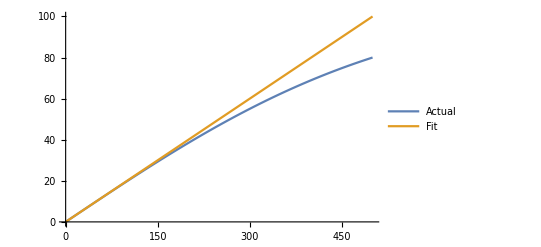

```mathematica
Plot[{J[ω,{nγ,nωc},1],k*a*nω0^(k-1)*(ω-nω0)+J[nω0,{nγ,nωc},1]/.affinefit/. k->nk},{ω,0,500},PlotLegends->{"Actual","Fit"}]
```

```mathematica
Series[c[ω]*ω^k[ω],{ω,ω0,1}]
```

ω0^k[ω0] c[ω0]+ω0^(-1+k[ω0]) (c[ω0] k[ω0]+ω0 c'[ω0]+ω0 c[ω0] Log[ω0] k'[ω0]) (ω-ω0)+O[ω-ω0]^2

```mathematica
kfunc[a_,ω0_,γ_,ωc_]:=1/Log[ω0]*ProductLog[(ω0*Log[ω0])/a*SeriesCoefficient[J[ω,{γ,ωc},1],{ω,ω0,1}]]
```

```mathematica
kfunc[0.00019994,10,0.1,1000]
```

3.46082

```mathematica
NMtest[k_,ω0_,δ_]:=Module[{μ=4/π^2(1-k)^2(Log[(ω0+δ)/(ω0-δ)])^2},((1+μ)^(1/2)-1)/((1+μ)^(1/2)+1)]
```

```mathematica
NMtest[3.461,10,0.01]
```

2.45461×10^-6

```mathematica
FindFit[Table[J[ω,{γtest,ωctest},1],{ω,ω0test-0.01,ω0test+0.01,0.001}],a x^k+b,{a,b,k},x]
```

{a→0.00513455,b→52.8767,k→0.998414}

```mathematica
NSolve[SeriesCoefficient[J[ω,{γtest,ωctest},1],{ω,ω0test,1}]/(0.00513455301833)==k*ω0test^(k-1),k]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{k→3.89973}}

```mathematica
kfunc[0.00513455301833,ω0test,γtest,ωctest]
```

3.89973

```mathematica
NMtest[3.89973,ω0test,0.01]
```

7.4562×10^-6

```mathematica
Series[J[ω,{γtest,ωctest},1],{ω,ω0test,4}]
```

52.933+5.10792 (ω-6.76046)-0.463964 (ω-6.76046)^2+0.00443172 (ω-6.76046)^3+0.00153661 (ω-6.76046)^4+O[ω-6.76046]^5

```mathematica
SeriesCoefficient[J[ω,{γ,ωc},1],{ω,ω0,1}]
```

(2 γ ωc^2 (-ω0^2+ωc^2))/((ω0^2+ωc^2)^2)

```mathematica
Reduce[{SeriesCoefficient[J[ω,{γ,ωc},1],{ω,ω0,1}]==k,{ω0,γ,ωc}∈PositiveReals,k∈Reals}]
```

ωc>0&&ω0>0&&γ>0&&k==(2 γ ω0^2 ωc^2-2 γ ωc^4)/(-ω0^4-2 ω0^2 ωc^2-ωc^4)

```mathematica
ω0test2=1;
ωctest2=1000;

ktest=3;

γtest2=-ktest*(ω0test2^4+2 ω0test2^2 ωctest2^2+ωctest2^4)/(2 ω0test2^2 ωctest2^2-2 ωctest2^4);

SeriesCoefficient[J[ω,{γtest2,ωctest2},1],{ω,ω0test2,1}]

τsystemListLD[ω0test2,γtest2,ωctest2]
1/ωctest2//N
markovTestLD[ω0test2,γtest2,ωctest2]
```

3

{0.00100302,0.38062,2.61939}

0.001

0.000381769

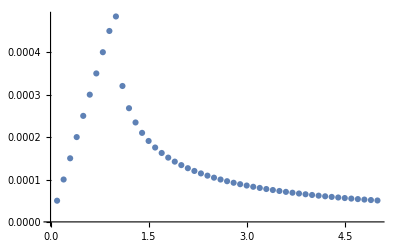

```mathematica
ω0test2=0.5;
ωctest2=1000;
ListPlot[Table[{k,markovTestLD[ω0test2,-k*(ω0test2^4+2 ω0test2^2 ωctest2^2+ωctest2^4)/(2 ω0test2^2 ωctest2^2-2 ωctest2^4),ωctest2]},{k,0.1,5,0.1}]]
```

```mathematica
nk=1;

nω0min=0.01;
nωcmax=10^8;
NMaximize[{markovTestLD[ω0,-nk*(ω0^4+2 ω0^2 ωc^2+ωc^4)/(2 ω0^2 ωc^2-2 ωc^4),ωc],nω0min<ω0<ωc<nωcmax}, {ω0,ωc}]
```

{0.333333,{ω0→5.0967,ωc→6.06435}}

```mathematica
-nk*(ω0^4+2 ω0^2 ωc^2+ωc^4)/(2 ω0^2 ωc^2-2 ωc^4)/.{ω0->5.096701969356439,ωc->6.064352942035814}
```

4.95727

```mathematica
markovTestLD[ω0,γ,ωc]/.{ω0->5.096701969356439,γ->4.957270020231168,ωc->6.064352942035814}
```

0.333333

```mathematica
SeriesCoefficient[J[ω,{γ,ωc},1],{ω,ω0,1}]/.{ω0->5.096701969356439,γ->4.957270020231168,ωc->6.064352942035814}
```

1.

#### Structured Lorentz-Drude

```mathematica
{nω0min,nω0max}={0.01,10^3};
{nγmin,nγmax}={10^-6,10^2};
{nλmin,nλmax}={0.01,10^2};
{nωsmin,nωsmax}={0.01,10^3};

NMaximize[{markovTestSLD[ω0,γ,λ,ωs],nω0min<ω0<nω0max&&nγmin<γ<nγmax&&nλmin<λ<nλmax&&nωsmin<ωs<nωsmax}, {ω0,γ,λ,ωs}]
```

{0.5,{ω0→51.1045,γ→0.0797125,λ→99.9327,ωs→51.1419}}

```mathematica
τsystemListSLD[ω0,γ,λ,ωs]/.{ω0->51.104528867512,γ->0.0797125483896226,λ->99.93270130932497,ωs->51.14188778512694}
```

{50.1803,50.1803,50.1803,50.1803}

```mathematica
polesSLD[ω0,γ,λ,ωs]/.{ω0->51.104528867512,γ->0.0797125483896226,λ->99.93270130932497,ωs->51.14188778512694}
```

{-0.0199281-50.1555 ⅈ,-0.0199281+50.1555 ⅈ,-0.0199281-52.1095 ⅈ,-0.0199281+52.1095 ⅈ}

```mathematica
FindMaximum[{markovTestSLD[ω0,γ,λ,ωs],nω0min<ω0<nω0max&&nγmin<γ<nγmax&&nλmin<λ<nλmax&&nωsmin<ωs<nωsmax}, {ω0,γ,λ,ωs}]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{0.5,{ω0→1.07467,γ→1.05502,λ→1.06465,ωs→1.41419}}

```mathematica
τsystemListSLD[ω0,γ,λ,ωs]/.{ω0->1.074670433406739,γ->1.0550170294602381,λ->1.0646507176096456,ωs->1.414192170353259}
```

{3.79141,3.79141,3.79141,3.79141}

```mathematica
polesSLD[ω0,γ,λ,ωs]/.{ω0->1.074670433406739,γ->1.0550170294602381,λ->1.0646507176096456,ωs->1.414192170353259}
```

{-0.263754-0.918237 ⅈ,-0.263754+0.918237 ⅈ,-0.263754-1.56878 ⅈ,-0.263754+1.56878 ⅈ}

```mathematica
nω0start=1;
nγstart=1;
nλstart=1;
nωsstart=10;

FindMaximum[{markovTestSLD[ω0,γ,λ,ωs],nω0min<ω0<nω0max&&nγmin<γ<nγmax&&nλmin<λ<nλmax&&nωsmin<ωs<nωsmax}, {{ω0,nω0start},{γ,nγstart},{λ,nλstart},{ωs,nωsstart}}]
```

FindMaximum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{0.5,{ω0→12.127,γ→0.00116193,λ→16.5321,ωs→12.2025}}

```mathematica
polesSLD[ω0,γ,λ,ωs]/.{ω0->12.127046735225978,γ->0.0011619265400334305,λ->16.5321403963253,ωs->12.202490714622225}
```

{-0.000290482-11.5052 ⅈ,-0.000290482+11.5052 ⅈ,-0.000290482-12.8621 ⅈ,-0.000290482+12.8621 ⅈ}

```mathematica
τsystemListSLD[ω0,γ,λ,ωs]/.{ω0->12.127046735225978,γ->0.0011619265400334305,λ->16.5321403963253,ωs->12.202490714622225}
```

{3442.56,3442.56,3442.56,3442.56}

```mathematica
Reduce[-λ^2/(ωs^2+s^2 +γ*s)+s^2+ω0^2+λ^2/ωs^2==0,s]
```

ωs≠0&&(s==Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,1]||s==Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,2]||s==Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,3]||s==Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4])&&s^2+s γ+ωs^2≠0

```mathematica
1/ωs^2(ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) x+(λ^2+ω0^2 ωs^2+ωs^4) x^2+γ ωs^2 x^3+ωs^2 x^4)//Simplify
```

x^4+x^3 γ+x γ (ω0^2+λ^2/ωs^2)+ω0^2 ωs^2+x^2 (ω0^2+λ^2/ωs^2+ωs^2)

```mathematica
CoefficientList[x^4+x^3 γ+x γ (ω0^2+λ^2/ωs^2)+ω0^2 ωs^2+x^2 (ω0^2+λ^2/ωs^2+ωs^2),x]
```

{ω0^2 ωs^2,γ (ω0^2+λ^2/ωs^2),ω0^2+λ^2/ωs^2+ωs^2,γ,1}

```mathematica
(x-(a+ⅈ b))(x-(a-ⅈ b))(x-(a+ⅈ c))(x-(a-ⅈ c))//Expand
```

a^4+a^2 b^2+a^2 c^2+b^2 c^2-4 a^3 x-2 a b^2 x-2 a c^2 x+6 a^2 x^2+b^2 x^2+c^2 x^2-4 a x^3+x^4

```mathematica
CoefficientList[(x-(a+ⅈ b))(x-(a-ⅈ b))(x-(a+ⅈ c))(x-(a-ⅈ c)),x]
```

{a^4+a^2 b^2+a^2 c^2+b^2 c^2,-4 a^3-2 a b^2-2 a c^2,6 a^2+b^2+c^2,-4 a,1}

```mathematica
sols1=Reduce[CoefficientList[(x-(a+ⅈ b))(x-(a-ⅈ b))(x-(a+ⅈ c))(x-(a-ⅈ c)),x]==CoefficientList[x^4+x^3 γ+x γ (ω0^2+λ^2/ωs^2)+ω0^2 ωs^2+x^2 (ω0^2+λ^2/ωs^2+ωs^2),x]&&{ω0,γ,λ,ωs}∈PositiveReals,{a,b,c},Reals];
```

```mathematica
sols2=Reduce[CoefficientList[(x-(a+ⅈ b))(x-(a-ⅈ b))(x-(a+ⅈ c))(x-(a-ⅈ c)),x]==CoefficientList[x^4+x^3 γ+x γ (ω0^2+λ^2/ωs^2)+ω0^2 ωs^2+x^2 (ω0^2+λ^2/ωs^2+ωs^2),x]&&{ω0,γ,λ,ωs}∈PositiveReals,{a,b,c},Reals,Backsubstitution->True];
```

```mathematica
vals=(sols1/. {Equal->Rule,And->List,Or->List});
```

```mathematica
valsnoim=DeleteCases[vals,Rule[b,_]|Rule[c,_],All]//.{}->Nothing;
```

```mathematica
valsnoim
```

{ωs>0,{{0<λ<(2 ωs^2)/5,{{ω0→ωs/2+1/2 √((-4 λ^2+ωs^4)/ωs^2),γ→2 √((-λ^2-ω0^2 ωs^2+ωs^4)/ωs^2),a→-γ/4},{ωs/2+1/2 √((-4 λ^2+ωs^4)/ωs^2)<ω0<√((-λ^2+ωs^4)/ωs^2),γ→2 √((-λ^2-ω0^2 ωs^2+ωs^4)/ωs^2),a→-γ/4}}},{λ→(2 ωs^2)/5,{{ω0→3 ωs-√((-λ^2+8 ωs^4)/ωs^2),γ→2 √((-λ^2-ω0^2 ωs^2+ωs^4)/ωs^2),a→-γ/4},{ω0→ωs/2+1/2 √((-4 λ^2+ωs^4)/ωs^2),γ→2 √((-λ^2-ω0^2 ωs^2+ωs^4)/ωs^2),a→-γ/4},{ωs/2+1/2 √((-4 λ^2+ωs^4)/ωs^2)<ω0<√((-λ^2+ωs^4)/ωs^2),γ→2 √((-λ^2-ω0^2 ωs^2+ωs^4)/ωs^2),a→-γ/4}}},{(2 ωs^2)/5<λ<ωs^2/2,{{(√((-3 λ^2+4 λ ωs^2-ωs^4)/ωs^2))/(√3)≤ω0<ωs/2-1/2 √((-4 λ^2+ωs^4)/ωs^2),γ→2 √((-λ^2-ω0^2 ωs^2+ωs^4)/ωs^2),a→-γ/4},{ω0→ωs/2-1/2 √((-4 λ^2+ωs^4)/ωs^2),γ→2 √((-λ^2-ω0^2 ωs^2+ωs^4)/ωs^2),a→-γ/4},{ω0→ωs/2+1/2 √((-4 λ^2+ωs^4)/ωs^2),γ→2 √((-λ^2-ω0^2 ωs^2+ωs^4)/ωs^2),a→-γ/4},{ωs/2+1/2 √((-4 λ^2+ωs^4)/ωs^2)<ω0<√((-λ^2+ωs^4)/ωs^2),γ→2 √((-λ^2-ω0^2 ωs^2+ωs^4)/ωs^2),a→-γ/4}}},{λ→ωs^2/2,{{(√((-3 λ^2+4 λ ωs^2-ωs^4)/ωs^2))/(√3)≤ω0<ωs/2-1/2 √((-4 λ^2+ωs^4)/ωs^2),γ→2 √((-λ^2-ω0^2 ωs^2+ωs^4)/ωs^2),a→-γ/4},{ω0→ωs/2-1/2 √((-4 λ^2+ωs^4)/ωs^2),γ→2 √((-λ^2-ω0^2 ωs^2+ωs^4)/ωs^2),a→-γ/4},{ωs/2-1/2 √((-4 λ^2+ωs^4)/ωs^2)<ω0<√((-λ^2+ωs^4)/ωs^2),γ→2 √((-λ^2-ω0^2 ωs^2+ωs^4)/ωs^2),a→-γ/4}}},{ωs^2/2<λ<(14 ωs^2)/17,(√((-3 λ^2+4 λ ωs^2-ωs^4)/ωs^2))/(√3)≤ω0<√((-λ^2+ωs^4)/ωs^2),γ→2 √((-λ^2-ω0^2 ωs^2+ωs^4)/ωs^2),a→-γ/4},{λ→(14 ωs^2)/17,3 ωs-√((-λ^2+8 ωs^4)/ωs^2)≤ω0<√((-λ^2+ωs^4)/ωs^2),γ→2 √((-λ^2-ω0^2 ωs^2+ωs^4)/ωs^2),a→-γ/4},{(14 ωs^2)/17<λ<ωs^2,(√((-3 λ^2+4 λ ωs^2-ωs^4)/ωs^2))/(√3)≤ω0<√((-λ^2+ωs^4)/ωs^2),γ→2 √((-λ^2-ω0^2 ωs^2+ωs^4)/ωs^2),a→-γ/4}}}

```mathematica
Simplify[vals2/.ω0->κ ωs,Assumptions->κ∈Reals]
```

{{ωs>0,0<λ<(2 ωs^2)/5,κ ωs→1/2 (ωs+√(-(4 λ^2)/ωs^2+ωs^2)),γ→√2 √(ωs^2-ωs √(-(4 λ^2)/ωs^2+ωs^2))},{ωs>0,0<λ<(2 ωs^2)/5,1/2 (ωs+√(-(4 λ^2)/ωs^2+ωs^2))<κ ωs<√(-λ^2/ωs^2+ωs^2),γ→2 √(-λ^2/ωs^2-(-1+κ^2) ωs^2)},{ωs>0,λ→(2 ωs^2)/5,κ ωs→3 ωs-(14 √(ωs^2))/5,γ→4 √(-4 ωs^2+(21 ωs √(ωs^2))/5)},{ωs>0,λ→(2 ωs^2)/5,κ ωs→1/10 (5 ωs+3 √(ωs^2)),γ→√(2/5) √(ωs (5 ωs-3 √(ωs^2)))},{ωs>0,λ→(2 ωs^2)/5,5 ωs+3 √(ωs^2)<10 κ ωs&&√21 √(ωs^2)>5 κ ωs,γ→2/5 √(-((-21+25 κ^2) ωs^2))},{ωs>0,5 λ>2 ωs^2&&2 λ<ωs^2,(√(4 λ-(3 λ^2)/ωs^2-ωs^2))/(√3)≤κ ωs<1/2 (ωs-√(-(4 λ^2)/ωs^2+ωs^2)),γ→2 √(-λ^2/ωs^2-(-1+κ^2) ωs^2)},{ωs>0,5 λ>2 ωs^2&&2 λ<ωs^2,κ ωs→1/2 (ωs-√(-(4 λ^2)/ωs^2+ωs^2)),γ→√2 √(ωs (ωs+√(-(4 λ^2)/ωs^2+ωs^2)))},{ωs>0,5 λ>2 ωs^2&&2 λ<ωs^2,κ ωs→1/2 (ωs+√(-(4 λ^2)/ωs^2+ωs^2)),γ→√2 √(ωs^2-ωs √(-(4 λ^2)/ωs^2+ωs^2))},{ωs>0,5 λ>2 ωs^2&&2 λ<ωs^2,1/2 (ωs+√(-(4 λ^2)/ωs^2+ωs^2))<κ ωs<√(-λ^2/ωs^2+ωs^2),γ→2 √(-λ^2/ωs^2-(-1+κ^2) ωs^2)},{ωs>0,λ→ωs^2/2,√3 √(ωs^2)≤6 κ ωs&&2 κ ωs<ωs,γ→√(-((-3+4 κ^2) ωs^2))},{ωs>0,λ→ωs^2/2,κ ωs→ωs/2,γ→√2 √(ωs^2)},{ωs>0,λ→ωs^2/2,2 κ ωs>ωs&&√3 √(ωs^2)>2 κ ωs,γ→√(-((-3+4 κ^2) ωs^2))},{ωs>0,2 λ>ωs^2&&17 λ<14 ωs^2,(√(4 λ-(3 λ^2)/ωs^2-ωs^2))/(√3)≤κ ωs<√(-λ^2/ωs^2+ωs^2),γ→2 √(-λ^2/ωs^2-(-1+κ^2) ωs^2)},{ωs>0,λ→(14 ωs^2)/17,3 ωs-(46 √(ωs^2))/17≤κ ωs<1/17 √93 √(ωs^2),γ→2/17 √(-((-93+289 κ^2) ωs^2))},{ωs>0,(14 ωs^2)/17<λ<ωs^2,(√(4 λ-(3 λ^2)/ωs^2-ωs^2))/(√3)≤κ ωs<√(-λ^2/ωs^2+ωs^2),γ→2 √(-λ^2/ωs^2-(-1+κ^2) ωs^2)}}

```mathematica
polesSLD[ω0,γ,λ,ωs]/.{ω0->12.127046735225978,γ->0.0011619265400334305,λ->16.5321403963253,ωs->12.202490714622225}
```

{-0.000290482-11.5052 ⅈ,-0.000290482+11.5052 ⅈ,-0.000290482-12.8621 ⅈ,-0.000290482+12.8621 ⅈ}

```mathematica
-γ/4/.{ω0->12.127046735225978,γ->0.0011619265400334305,λ->16.5321403963253,ωs->12.202490714622225}
```

-0.000290482

```mathematica
Reduce[-(ωR^2 ωs^2)/(ωs^2+s^2 +γ*s)+s^2+ω0^2+ωR^2==0,s]
```

(s==Root[ω0^2 ωs^2+(γ ω0^2+γ ωR^2) #1+(ω0^2+ωR^2+ωs^2) #1^2+γ #1^3+#1^4&,1]||s==Root[ω0^2 ωs^2+(γ ω0^2+γ ωR^2) #1+(ω0^2+ωR^2+ωs^2) #1^2+γ #1^3+#1^4&,2]||s==Root[ω0^2 ωs^2+(γ ω0^2+γ ωR^2) #1+(ω0^2+ωR^2+ωs^2) #1^2+γ #1^3+#1^4&,3]||s==Root[ω0^2 ωs^2+(γ ω0^2+γ ωR^2) #1+(ω0^2+ωR^2+ωs^2) #1^2+γ #1^3+#1^4&,4])&&s^2+s γ+ωs^2≠0

```mathematica
ω0^2 ωs^2+(γ ω0^2+γ ωR^2) #1+(ω0^2+ωR^2+ωs^2) #1^2+γ #1^3+#1^4&[x]
```

x^4+x^3 γ+x (γ ω0^2+γ ωR^2)+ω0^2 ωs^2+x^2 (ω0^2+ωR^2+ωs^2)

```mathematica
CoefficientList[x^4+x^3 γ+x (γ ω0^2+γ ωR^2)+ω0^2 ωs^2+x^2 (ω0^2+ωR^2+ωs^2),x]
```

{ω0^2 ωs^2,γ ω0^2+γ ωR^2,ω0^2+ωR^2+ωs^2,γ,1}

```mathematica
(x-(a+ⅈ b))(x-(a-ⅈ b))(x-(a+ⅈ c))(x-(a-ⅈ c))//Expand
```

a^4+a^2 b^2+a^2 c^2+b^2 c^2-4 a^3 x-2 a b^2 x-2 a c^2 x+6 a^2 x^2+b^2 x^2+c^2 x^2-4 a x^3+x^4

```mathematica
CoefficientList[(x-(a+ⅈ b))(x-(a-ⅈ b))(x-(a+ⅈ c))(x-(a-ⅈ c)),x]
```

{a^4+a^2 b^2+a^2 c^2+b^2 c^2,-4 a^3-2 a b^2-2 a c^2,6 a^2+b^2+c^2,-4 a,1}

```mathematica
sols3=Reduce[CoefficientList[(x-(a+ⅈ b))(x-(a-ⅈ b))(x-(a+ⅈ c))(x-(a-ⅈ c)),x]==CoefficientList[x^4+x^3 γ+x (γ ω0^2+γ ωR^2)+ω0^2 ωs^2+x^2 (ω0^2+ωR^2+ωs^2),x]&&{ω0,γ,ωR,ωs}∈PositiveReals,{a,b,c},Reals];
```

```mathematica
sols4=Reduce[CoefficientList[(x-(a+ⅈ b))(x-(a-ⅈ b))(x-(a+ⅈ c))(x-(a-ⅈ c)),x]==CoefficientList[x^4+x^3 γ+x (γ ω0^2+γ ωR^2)+ω0^2 ωs^2+x^2 (ω0^2+ωR^2+ωs^2),x]&&{ω0,γ,ωR,ωs}∈PositiveReals,{a,b,c},Reals,Backsubstitution->True];
```

```mathematica
vals2=(sols3/. {Equal->Rule,And->List,Or->List});
```

```mathematica
valsnoim2=DeleteCases[vals2,Rule[b,_]|Rule[c,_],All]//.{}->Nothing;
```

```mathematica
valsnoim2
```

{ωR>0,{{0<ω0<ωR/2,√(ω0^2+ωR^2)<ωs≤2 ωR-√(-3 ω0^2+ωR^2),γ→√(-4 ω0^2-4 ωR^2+4 ωs^2),a→-γ/4},{ω0→ωR/2,{{√(ω0^2+ωR^2)<ωs≤2 ωR-√(-3 ω0^2+ωR^2),γ→√(-4 ω0^2-4 ωR^2+4 ωs^2),a→-γ/4},{ωs→(ω0^2+ωR^2)/ω0,γ→√(-4 ω0^2-4 ωR^2+4 ωs^2),a→-γ/4}}},{ωR/2<ω0<(√(ωR^2))/(√3),{{√(ω0^2+ωR^2)<ωs≤2 ωR-√(-3 ω0^2+ωR^2),γ→√(-4 ω0^2-4 ωR^2+4 ωs^2),a→-γ/4},{2 ωR+√(-3 ω0^2+ωR^2)≤ωs<(ω0^2+ωR^2)/ω0,γ→√(-4 ω0^2-4 ωR^2+4 ωs^2),a→-γ/4},{ωs→(ω0^2+ωR^2)/ω0,γ→√(-4 ω0^2-4 ωR^2+4 ωs^2),a→-γ/4}}},{ω0≥(√(ωR^2))/(√3),{{√(ω0^2+ωR^2)<ωs<(ω0^2+ωR^2)/ω0,γ→√(-4 ω0^2-4 ωR^2+4 ωs^2),a→-γ/4},{ωs→(ω0^2+ωR^2)/ω0,γ→√(-4 ω0^2-4 ωR^2+4 ωs^2),a→-γ/4}}}}}

Non-Markovian dynamics is also achieved for sharp spectral density, γ→0. In this case, the maximum NM comes when ω_0^2+ω_R^2=ω_s^2, where ω_R^2=λ^2/ω_s^2 is the renormalized frequency.

```mathematica
polesSLD[10,0.001,1,10]
```

{-0.00025125-9.95013 ⅈ,-0.00025125+9.95013 ⅈ,-0.00024875-10.0501 ⅈ,-0.00024875+10.0501 ⅈ}

```mathematica
markovTestSLD[10,0.001,1,10]
```

0.4975

```mathematica
markovTestSLD[Sqrt[10^2-1^2/10^2],0.001,1,10]
```

0.5

```mathematica
NMaximize[{2/γ*-Re@Root[ω0^2 ωs^4+(γ λ^2+γ ω0^2 ωs^2) #1+(λ^2+ω0^2 ωs^2+ωs^4) #1^2+γ ωs^2 #1^3+ωs^2 #1^4&,4],nω0min<ω0<nω0max&&nγmin<γ<nγmax&&nλmin<λ<nλmax&&nωsmin<ωs<nωsmax}, {ω0,γ,λ,ωs}]
```

{0.5,{ω0→51.1045,γ→0.0797125,λ→99.9327,ωs→51.1419}}

```mathematica
nωR=10;

{nω0min,nω0max}={0.01,10^2};
{nγmin,nγmax}={10^-6,10^2};
{nωsmin,nωsmax}={0.01,10^2};

NMaximize[{2/γ*-Re@Root[ω0^2 ωs^2+(γ ω0^2+γ nωR^2) #1+(ω0^2+nωR^2+ωs^2) #1^2+γ #1^3+#1^4&,4],nω0min<ω0<nω0max&&nγmin<γ<nγmax&&nωsmin<ωs<nωsmax}, {ω0,γ,ωs}]
```

{0.990099,{ω0→0.0101403,γ→2.03992,ωs→100.}}

```mathematica
-Re@Root[ω0^2 ωs^2+(γ ω0^2+γ nωR^2) #1+(ω0^2+nωR^2+ωs^2) #1^2+γ #1^3+#1^4&,4]/.{ω0->0.010140345190879448,γ->2.03992195521669,ωs->100.}
```

1.00986

Another way of predicting non-Markovian behaviour is the local shape of the spectral density around the (bare) system frequency.

Specifically, write J(ω)=Cω^k for ω∈[ω_0-δ,ω_0+δ], δ≪1. Then we have J(ω-ω_0)≈J(ω_0)+kCω_0^(k-1)(ω-ω_0). The idea is that k=1 corresponds to Markovian dynamics.

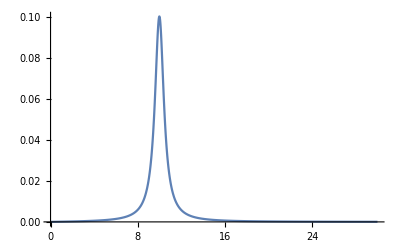

```mathematica
Plot[J[ω,{1,1,10},2],{ω,0,30},PlotRange->All]
```

```mathematica
Series[J[ω,{1,1,10},2],{ω,9,3}]//N
```

0.020362+0.0329436 (ω-9.)+0.0364176 (ω-9.)^2+0.0318241 (ω-9.)^3+O[ω-9.]^4

```mathematica
FindFit[Table[J[ω,{1,1,10},2],{ω,9-0.01,9+0.01,0.001}],a x^k+b,{a,b,k},x]
```

{a→0.000030917,b→0.0200058,k→1.01943}

```mathematica
NSolve[SeriesCoefficient[J[ω,{1,1,10},2],{ω,9,1}]/(0.000030917048369180245)==k*10^(k-1),k,Reals]
```

{{k→3.48533}}

```mathematica
kfunc[a_,ω0_,γ_,ωc_]:=1/Log[ω0]*ProductLog[(ω0*Log[ω0])/a*SeriesCoefficient[J[ω,{γ,ωc},1],{ω,ω0,1}]]
```

```mathematica
kfunc[0.00019994,10,0.1,1000]
```

3.46082

## Changing the spectral density

### Random covariance matrix

```mathematica
Randn[n_]:=Table[RandomReal[NormalDistribution[0,1]]+I RandomReal[NormalDistribution[0,1]],{i,n},{j,n}];

SΩ[n_Integer]:=Table[If[j==1+Floor[i/2]+Mod[i+1,2](n-1),1,0],{i,2n},{j,2n}]
```

```mathematica
rndcovn[nn_,maxsqz_:0.2,maxsqdet_:1.5]:=Module[
{try,symba,vecsqz,vecdet,cmtry},
(* maxsqz: max local squeezing, set to ≥0, reduce for more entangled states *)
(* maxsqzdet: max determinant^2, set to ≥1, increase for more mixed states, set to 1 for pure states *)
try=Randn[nn];
try[[1;;1]]=try[[1;;1]]/Sqrt[Chop[try[[1;;1]].ConjugateTranspose[try[[1;;1]]]][[1,1]]];
Do[
Do[try[[j;;j]]=try[[j;;j]]-(Chop[try[[j;;j]].ConjugateTranspose[try[[k;;k]]]][[1,1]])try[[k;;k]];
,{k,1,j-1}];
try[[j;;j]]=try[[j;;j]]/Sqrt[Chop[try[[j;;j]].ConjugateTranspose[try[[j;;j]]]][[1,1]]]
,{j,2,nn}];
try=Transpose[try];
symba=SΩ[nn].ArrayFlatten[({{Re[try], Im[try]}, {-Im[try], Re[try]}})].Transpose[SΩ[nn]];
vecsqz=Table[maxsqz Random[],{nn}];
vecdet=Table[(maxsqdet-1)Random[]+1,{nn}];
Return[1/2(symba.DiagonalMatrix[Table[vecdet[[Floor[(i+1)/2]]]*(vecsqz[[Floor[(i+1)/2]]])^((-1)^Mod[(i+1),2]),{i,2nn}]].Transpose[symba])]
]
rndcovn::usage="rndcovn[n] returns a random n-mode covariance matrix. The convention of min. sympl. eig. equals 1/2 is taken. Optional argument maxsqz determines the maximum local squeezing. setting it to larger values ≥ 0 allows for more entanglement (default maxsqz = 0.2). Optional argument maxsqdet is the maximum determinant squared. Setting it to 1 returns pure states. Setting it to ≥ 1 returns mixed states (default maxsqdet = 1.5).";
```

```mathematica
rndconvmatWithinFidelity[covarainceMatrix_,fidmin_,fidmax_]:=While[True,Module[{cov=rndcovn[1]},If[fidmin<Fidelity[2*covarainceMatrix,2*cov]&&Fidelity[2*covarainceMatrix,2*cov]<fidmax,Return[cov]]]]

rndconvmatWithinFidelity::usage="rndconvmatWithinFidelity[covarainceMatrix,fidmin,fidmax] returns a random covariance matrix within a chosen fidelity range (fidmin,fidmax) of a specified 2x2 covariance matrix.";

rndconvmatWithinFidelityPercent[covarainceMatrix_,fid_,percent_]:=While[True,Module[{cov=rndcovn[1]},If[fid*(1-percent/100)<Fidelity[2*covarainceMatrix,2*cov]&&Fidelity[2*covarainceMatrix,2*cov]<fid*(1+percent/100),Return[cov]]]]

rndconvmatWithinFidelityPercent::usage="rndconvmatWithinFidelityPercent[covarainceMatrix,fid,percent] returns a random covariance matrix within a chosen percentage of fid of a specified 2x2 covariance matrix.";
```

```mathematica
testcovn=rndcovn[1];

testcovn2=rndconvmatWithinFidelity[testcovn,0.5,0.51];

Fidelity[2*testcovn,2*testcovn2]

testcovn3=rndconvmatWithinFidelityPercent[testcovn,0.5,1];

Fidelity[2*testcovn,2*testcovn3]
```

0.503175

0.498716

Now just testing some properties of rndcovn

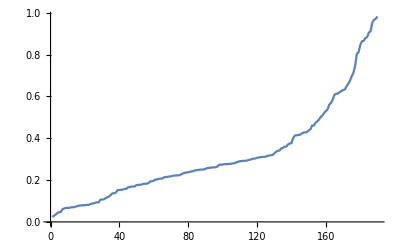

```mathematica
numStates=20;
covTable=Table[rndcovn[1],{i,1,0.5*numStates^2-numStates}];
covFids=Flatten[Table[Fidelity[2*covTable[[i]],2*covTable[[j]]],{i,1,numStates},{j,i+1,numStates}]];
(*covFidsOrderedIndices=Ordering[covFids];*)
ListLinePlot[Sort@covFids]
```

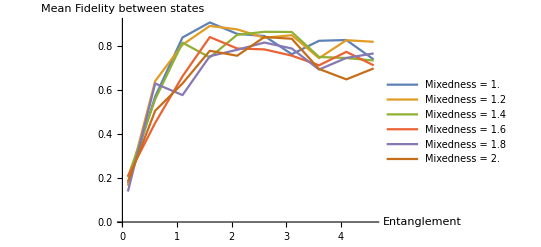

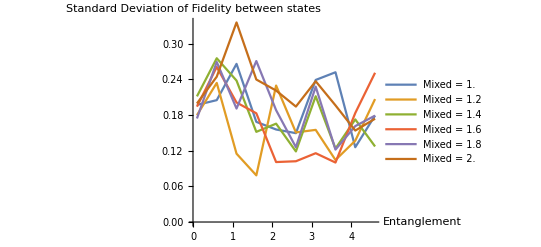

```mathematica
maxsqdetMax=2;
maxsqdetDiff=0.2;

maxsqzMax=5;
maxsqzDiff=0.5;

ListLinePlot[Table[{maxsqz,Module[{covTableTemp=Table[rndcovn[1,maxsqz,maxsqdet],{i,1,0.5*numStates^2-numStates}]},Mean[Flatten[Table[Fidelity[2*covTableTemp[[i]],2*covTableTemp[[j]]],{i,1,numStates},{j,i+1,numStates}]]]]},{maxsqdet,1,maxsqdetMax,maxsqdetDiff},{maxsqz,0.1,maxsqzMax,maxsqzDiff}],AxesLabel->{"Entanglement","Mean Fidelity between states"},PlotLegends->Table[StringForm["Mixedness = ``",maxsqdet],{maxsqdet,1,maxsqdetMax,maxsqdetDiff}]]

ListLinePlot[Table[{maxsqz,Module[{covTableTemp=Table[rndcovn[1,maxsqz,maxsqdet],{i,1,0.5*numStates^2-numStates}]},StandardDeviation[Flatten[Table[Fidelity[2*covTableTemp[[i]],2*covTableTemp[[j]]],{i,1,numStates},{j,i+1,numStates}]]]]},{maxsqdet,1,maxsqdetMax,maxsqdetDiff},{maxsqz,0.1,maxsqzMax,maxsqzDiff}],AxesLabel->{"Entanglement","Standard Deviation of Fidelity between states"},PlotLegends->Table[StringForm["Mixed = ``",maxsqdet],{maxsqdet,1,maxsqdetMax,maxsqdetDiff}]]
```

### Fidelity-based measure of non-Markovianity

Define a measure of the amount of non-Markovian dynamics by calculating the total ‘amount’ of decreasing fidelity. 

Note that since the fidelity between any two states is bounded by 0≤F(ρ_1,ρ_2)≤1, this measure cannot be greater than 1. (BUT can the most non-Markovian dynamics ever achieve this??)

```mathematica
NMFid[data_]:=Module[{fidDiffs=Differences[Chop[data[[All,2]],10^-3]]},Sum[If[fidDiffs[[i]]<0,Abs[fidDiffs[[i]]],0],{i,1,Length[fidDiffs]}]]
NMFid::usage="NMFid[data], where data is a table of times and their respective fidelities {{t_i},{fid_i}}, gives a measure of non-Markovianity by calculating ∑_(n, Δfid < 0) |fid[t_(n + 1)]-fid[t_n]|.";

NMFidSmooth[data_]:=Module[{func=Interpolation[Chop[data,10^-3]]},Quiet@NIntegrate[Abs[D[func[x],x]]*HeavisideTheta[-D[func[x],x]],{x,0,data[[-1,1]]}]]
NMFidSmooth::usage="NMFid[data], where data is a table of times and their respective fidelities {{t_i},{fid_i}}, gives a measure of non-Markovianity by calculating ∫_(∂_t) |∂_t  F|ⅆt of the interpolated data.";
```

In order to select a pair of states which will maximise the about of non-Markovianity, we require that the states are both pure and orthogonal (see Wissmann 2012). 

We can get covariances matrices corresponding to pure states by setting  the maximum determinant squared (maxsqdet) option in rndcovn to 1.

Orthogonality requires 𝒟(ρ_1,ρ_2)=1, where  𝒟(ρ_1,ρ_2)=1/2(‖ρ_1-ρ_2‖)_tr is the trace distance. The inequality
 1-√(F(ρ_1,ρ_2))≤ 𝒟(ρ_1,ρ_2)≤√(1-F(ρ_1,ρ_2)),
 
 where F denotes fidelity, means that we need F(ρ_1,ρ_2)=0, and we already have a function to calculate the fidelity between covariance matrices.

```mathematica
NMPurityFid[data_]:=Module[{purityDiffs=Differences[Chop[data[[All,2]]]]},Sum[If[purityDiffs[[i]]<0,Abs[purityDiffs[[i]]],0],{i,1,Length[purityDiffs]}]]
NMPurityFid::usage="NMPurityFid[data], where data is a table of times and their respective purities {{t_i},{fid_i}}, gives a measure of non-unital non-Markovianity by calculating ∑_(n, Δfid < 0) |μ[t_(n + 1)]-μ[t_n]|.";

NMPurityFidSmooth[data_]:=Module[{func=Interpolation[Chop[data]]},Quiet@NIntegrate[Abs[D[func[x],x]]*HeavisideTheta[-D[func[x],x]],{x,0,data[[-1,1]]}]]
NMPurityFidSmooth::usage="NMPurityFid[data], where data is a table of times and their respective purities {{t_i},{fid_i}}, gives a measure of non-unital non-Markovianity by calculating ∫_(∂_t) |∂_t  μ|ⅆt of the interpolated data.";
```

```mathematica
rndconvmatPurePerp[covarainceMatrix_,percent_]:=While[True,Module[{cov=rndcovn[1,0.2,1]},If[Chop[Fidelity[2*covarainceMatrix,2*cov]]<(percent/100),Return[cov]]]]
rndconvmatPurePerp::usage="rndconvmatPerp[covarainceMatrix,percent] returns a random pure covariance matrix orthogonal (within a percentage) of a specified 2x2 covariance matrix.";
```

```mathematica
testcovn=rndcovn[1,0.2,1]
```

{{9.57364,-7.68271},{-7.68271,6.19138}}

```mathematica
testcovn2=rndconvmatPurePerp[testcovn,1]
Fidelity[2*testcovn,2*testcovn2]//Chop
```

{{1288.32,1648.75},{1648.75,2110.02}}

0.00432292

For a pure state, a 2n×2n covariance matrix σ satisfies Det[σ]=2^(-2n) and (𝒥σ)^2=-1/4 𝕀_(2n) (see Marian 2012).

```mathematica
Det[testcovn]
Det[testcovn2]
```

0.25

0.25

```mathematica
MatrixPower[({{0, 1}, {-1, 0}}).testcovn,2]//Chop
MatrixPower[({{0, 1}, {-1, 0}}).testcovn2,2]//Chop
```

{{-0.25,0},{0,-0.25}}

{{-0.25,0},{0,-0.25}}

### Some fidelity and symplectic eigenvalue plots

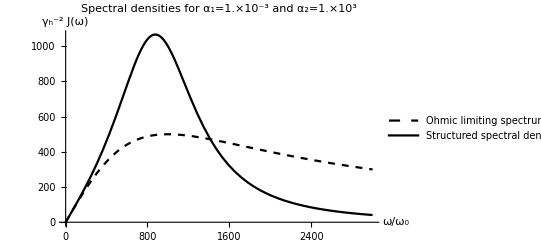

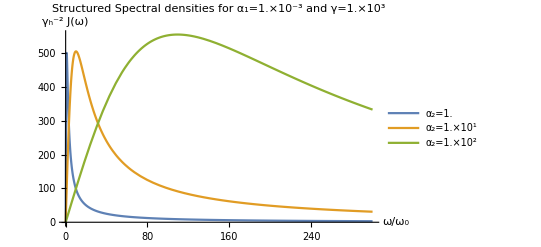

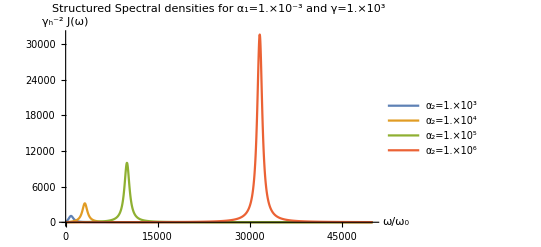

```mathematica
(* System properties *)
nω0=1;
nT=1;

α1=10^-3; (*Subscript[α, 1]=Subscript[γ, h]*) 
α2=10^3;
α2list1=Table[10^i,{i,0,2}];
α2list2=Table[10^i,{i,3,6}];

(* For Lorentz-Drude spectral density *)
nγLD=α1/(2*α2);
nωc=α2;

(* For Structured Lorentz-Drude spectral density *)
nγ=10^3;
nλ=Sqrt[α1*α2*nγ];
nωs=Sqrt[α2*nγ];

Plot[{α1^-2*J[ω,{nγLD,nωc},1],α1^-2*J[ω,{nγ,nλ,nωs},2]},{ω,0,3*α2},AxesLabel->{"ω/ω_0","γ_h^-2 J(ω)"},PlotStyle->{{Black,Dashed},Black},PlotLegends->{"Ohmic limiting spectrum","Structured spectral density"},PlotLabel->StringForm["Spectral densities for α_1=`` and α_2=``",ScientificForm[N[α1]],ScientificForm[N[α2]]]]

Plot[Evaluate@Table[α1^-2*J[ω,{nγ,Sqrt[α1*α2*nγ],Sqrt[α2*nγ]},2],{α2,α2list1}],{ω,0,3*α2list1[[-1]]},AxesLabel->{"ω/ω_0","γ_h^-2 J(ω)"},PlotLegends->Table[StringForm["α_2=``",ScientificForm[N[α2]]],{α2,α2list1}],PlotLabel->StringForm["Structured Spectral densities for α_1=`` and γ=``",ScientificForm[N[α1]],ScientificForm[N[nγ]]],PlotRange->All]

Plot[Evaluate@Table[α1^-2*J[ω,{nγ,Sqrt[α1*α2*nγ],Sqrt[α2*nγ]},2],{α2,α2list2}],{ω,0,0.05*α2list2[[-1]]},AxesLabel->{"ω/ω_0","γ_h^-2 J(ω)"},PlotLegends->Table[StringForm["α_2=``",ScientificForm[N[α2]]],{α2,α2list2}],PlotLabel->StringForm["Structured Spectral densities for α_1=`` and γ=``",ScientificForm[N[α1]],ScientificForm[N[nγ]]],PlotRange->All]
```

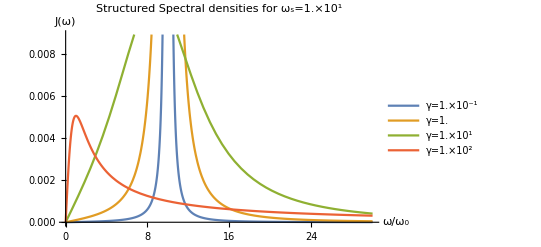

```mathematica
(* System properties *)
nω0=1;
nT=1;

(* For Structured Lorentz-Drude spectral density *)
nγlist=Table[10^i,{i,-1,2}];
nλ=1;
nωs=10;

Plot[Evaluate@Table[J[ω,{tγ,nλ,nωs},2],{tγ,nγlist}],{ω,0,3*nωs},AxesLabel->{"ω/ω_0","J(ω)"},PlotLegends->Table[StringForm["γ=``",ScientificForm[N[tγ]]],{tγ,nγlist}],PlotLabel->StringForm["Structured Spectral densities for ω_s=``",ScientificForm[N[nωs]]]]
```

```mathematica
nω0=1;
nT=1;

nγ=0.01;
nωc=1000;

xx0=0.5;pp0=0.5;xp0=0;

timescale=1*10^1;

tmax=10;
points=20;

fidtable=ParallelTable[{t,Fidelity[2*σcov[t*timescale,nT,nω0,{nγ,nωc},xx0,pp0,xp0,1]//Chop,2*acovarianceMatrix[nT,nω0,{nγ,nωc},1]]//Chop},{t,0,tmax,tmax/points}]//Chop;

tsymplecic=ParallelTable[{t,symplectic[σcov[t*timescale,nT,nω0,{nγ,nωc},xx0,pp0,xp0,1]]},{t,0,tmax,tmax/points}];
```

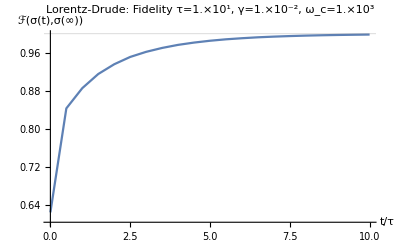

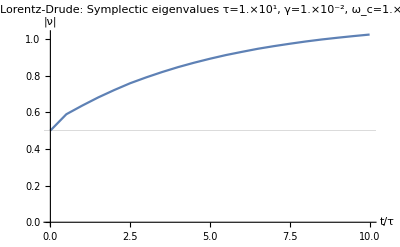

```mathematica
ListLinePlot[Re@fidtable,AxesLabel->{"t/τ","ℱ(σ(t),σ(∞))"},GridLines->{{},{1}},PlotLabel->StringForm["Lorentz-Drude: Fidelity\n τ=``, γ=``, ω_c=``",ScientificForm[N[timescale]],ScientificForm[N[nγ]],ScientificForm[N[nωc]]],PlotRange->All]

ListLinePlot[tsymplecic,AxesLabel->{"t/τ","|ν|"},GridLines->{{},{0.5}},PlotLabel->StringForm["Lorentz-Drude: Symplectic eigenvalues\n τ=``, γ=``, ω_c=``",ScientificForm[N[timescale]],ScientificForm[N[nγ]],ScientificForm[N[nωc]]],PlotRange->All]
```

```mathematica
rndconvmat=rndcovn[1];
xx0=rndconvmat[[1,1]];
xp0=rndconvmat[[1,2]];
pp0=rndconvmat[[2,2]];
rndconvmat // MatrixForm
```

(3.83031 | -2.72108
-2.72108 | 2.06537)

```mathematica
(* System properties *)
nω0=1;
nT=1;

α1=10^-3; (*Subscript[α, 1]=Subscript[γ, h]*) 
α2=10^3;

(* For Lorentz-Drude spectral density *)
nγLD=α1/(2*α2);
nωc=α2;

timescale=1*10^6;

-(Root[nω0^2 nωc+(nω0^2+2 nγLD nωc) #1+nωc #1^2+#1^3&,3]//N//Re)^-1

tmax=10;
points=20;
```

2.×10^6

```mathematica
fidtable1LD=ParallelTable[{t,Fidelity[2*σcov[t*timescale,nT,nω0,{nγLD,nωc},xx0,pp0,xp0,1]//Chop,2*acovarianceMatrix[nT,nω0,{nγLD,nωc},1]]//Chop},{t,0,tmax,tmax/points}]//Chop;

tsymplecic1LD=ParallelTable[{t,symplectic[σcov[t*timescale,nT,nω0,{nγLD,nωc},xx0,pp0,xp0,1]]},{t,0,tmax,tmax/points}];
```

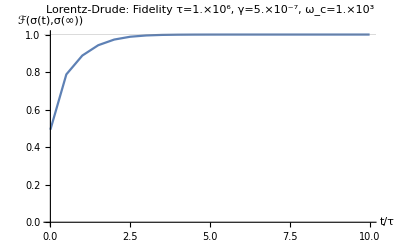

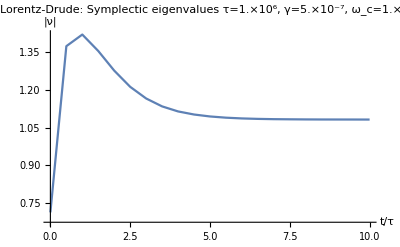

```mathematica
ListLinePlot[fidtable1LD,AxesLabel->{"t/τ","ℱ(σ(t),σ(∞))"},GridLines->{{},{1}},PlotLabel->StringForm["Lorentz-Drude: Fidelity\n τ=``, γ=``, ω_c=``",ScientificForm[N[timescale]],ScientificForm[N[nγLD]],ScientificForm[N[nωc]]],PlotRange->All]

ListLinePlot[tsymplecic1LD,AxesLabel->{"t/τ","|ν|"},GridLines->{{},{0.5}},PlotLabel->StringForm["Lorentz-Drude: Symplectic eigenvalues\n τ=``, γ=``, ω_c=``",ScientificForm[N[timescale]],ScientificForm[N[nγLD]],ScientificForm[N[nωc]]],PlotRange->All]
```

```mathematica
nω0=1;
nT=1;

α1=10^-3; (*Subscript[α, 1]=Subscript[γ, h]*) 
α2=10^3;

(* For Structured Lorentz-Drude spectral density *)
nγ=10^3;
nλ=Sqrt[α1*α2*nγ];
nωs=Sqrt[α2*nγ];

timescale=1*10^6;

tmax=10;
points=10;

fidtable1SLD=ParallelTable[{t,Fidelity[2*σcov[t*timescale,nT,nω0,{nγ,nλ,nωs},xx0,pp0,xp0,2],2*acovarianceMatrix[nT,nω0,{nγ,nλ,nωs},2]]//Chop},{t,0,tmax,tmax/points}]//Chop;
tsymplecic1SLD=ParallelTable[{t,symplectic[σcov[t*timescale,nT,nω0,{nγ,nλ,nωs},xx0,pp0,xp0,2]]},{t,0,tmax,tmax/points}];
```

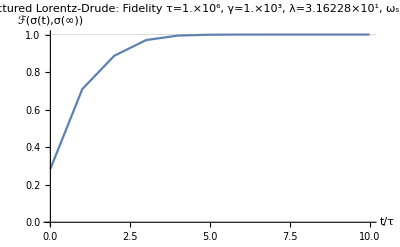

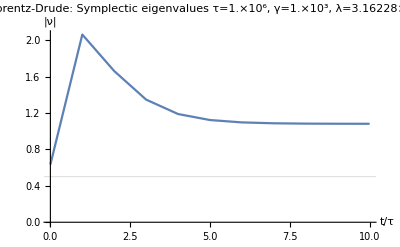

```mathematica
ListLinePlot[Re@fidtable1SLD,AxesLabel->{"t/τ","ℱ(σ(t),σ(∞))"},GridLines->{{},{1}},PlotLabel->StringForm["Structured Lorentz-Drude: Fidelity\n τ=``, γ=``, λ=``, ω_s=``",ScientificForm[N[timescale]],ScientificForm[N[nγ]],ScientificForm[N[nλ]],ScientificForm[N[nωs]]],PlotRange->All]

ListLinePlot[tsymplecic1SLD,AxesLabel->{"t/τ","|ν|"},GridLines->{{},{0.5}},PlotLabel->StringForm["Structured Lorentz-Drude: Symplectic eigenvalues\n τ=``, γ=``, λ=``, ω_s=``",ScientificForm[N[timescale]],ScientificForm[N[nγ]],ScientificForm[N[nλ]],ScientificForm[N[nωs]]],PlotRange->All]
```

### Searching for non-Markovianity

#### Lorentz-Drude

```mathematica
rndcovmat=rndcovn[1];

({{xx0, xp0}, {xp0, pp0}})=rndcovmat;

rndcovmat//MatrixForm

(* System properties *)
Jindex=1;
nω0=14.975;
nT=10;

nγ=9.999;
nωc=42.433;

nparamsLD={nγ,nωc};

τsystemListLD[nω0,nγ,nωc]
markovTestLD[nω0,nγ,nωc]

timescale=Max@τsystemListLD[nω0,nγ,nωc];

tmax=5;
points=30;
```

(0.396775 | -0.88229
-0.88229 | 3.04873)

{0.0706921,0.0707035,0.0707035}

0.333316

```mathematica
σcovLD=ParallelTable[σcov[t*timescale,nT,nω0,nparamsLD,xx0,pp0,xp0,Jindex]//Chop,{t,0,tmax,tmax/points}];
fidtableLD=ParallelTable[{(i-1)*tmax/points,Fidelity[2*σcovLD[[i]],2*acovarianceMatrix[nT,nω0,nparamsLD,Jindex]]},{i,1,points+1}];

tsymplecicLD=ParallelTable[{(i-1)*tmax/points,symplectic[σcovLD[[i]]]},{i,1,points+1}];
```

-Graphics-

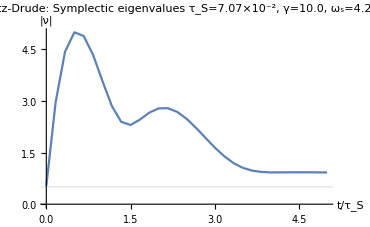

```mathematica
ListLinePlot[fidtableLD,AxesLabel->{"t/τ_S","ℱ(σ(t),σ(∞))"},GridLines->{{1/(nωc*timescale)},{1}},PlotLabel->StringForm["Lorentz-Drude: Fidelity \n τ_S=``, γ=``, ω_c=``",ScientificForm[SetPrecision[timescale,3]],ScientificForm[SetPrecision[nγ,3]],ScientificForm[SetPrecision[nωc,3]]],PlotRange->All,Epilog->Text["τ_C",{1/(nωc*timescale),Bottom},{0,-3},Background->White]]

ListLinePlot[tsymplecicLD,AxesLabel->{"t/τ_S","|ν|"},GridLines->{{},{0.5}},PlotLabel->StringForm["Lorentz-Drude: Symplectic eigenvalues\n τ_S=``, γ=``, ω_s=``",ScientificForm[SetPrecision[timescale,3]],ScientificForm[SetPrecision[nγ,3]],ScientificForm[SetPrecision[nωc,3]]],PlotRange->All]
```

#### Structured Lorentz-Drude

```mathematica
rndcovmat=rndcovn[1];

({{xx0, xp0}, {xp0, pp0}})=rndcovmat;

rndcovmat//MatrixForm

(* System properties *)
Jindex=2;
nω0=1.07467;
nT=1;

nγ=1.055;
nλ=1.06465;
nωs=1.41419;

nparamsSLD={nγ,nλ,nωs};

τsystemListSLD[nω0,nγ,nλ,nωs]
markovTestSLD[nω0,nγ,nλ,nωs]

timescale=Max@τsystemListSLD[nω0,nγ,nλ,nωs];

tmax=1.5;
points=30;
```

(0.0791153 | 0.0883915
0.0883915 | 4.33307)

{3.79146,3.79146,3.79148,3.79148}

0.499999

```mathematica
σcovSLD=ParallelTable[σcov[t*timescale,nT,nω0,nparamsSLD,xx0,pp0,xp0,Jindex]//Chop,{t,0,tmax,tmax/points}];
fidtableSLD=ParallelTable[{(i-1)*tmax/points,Fidelity[2*σcovSLD[[i]],2*acovarianceMatrix[nT,nω0,nparamsSLD,Jindex]]},{i,1,points+1}];

tsymplecicSLD=ParallelTable[{(i-1)*tmax/points,symplectic[σcovSLD[[i]]]},{i,1,points+1}];
```

-Graphics-

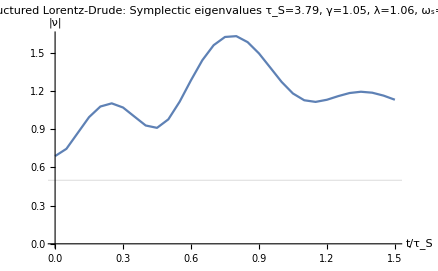

```mathematica
ListLinePlot[fidtableSLD,AxesLabel->{"t/τ_S","ℱ(σ(t),σ(∞))"},GridLines->{{2/(nγ*timescale)},{1}},PlotLabel->StringForm["Structured Lorentz-Drude: Fidelity \n τ_S=``, γ=``, λ=``, ω_s=``",ScientificForm[SetPrecision[timescale,3]],ScientificForm[SetPrecision[nγ,3]],ScientificForm[SetPrecision[nλ,3]],ScientificForm[SetPrecision[nωs,3]]],PlotRange->All,Epilog->Text["τ_C",{2/(nγ*timescale),Bottom},{0,-3},Background->White]]

ListLinePlot[tsymplecicSLD,AxesLabel->{"t/τ_S","|ν|"},GridLines->{{},{0.5}},PlotLabel->StringForm["Structured Lorentz-Drude: Symplectic eigenvalues\n τ_S=``, γ=``, λ=``, ω_s=``",ScientificForm[SetPrecision[timescale,3]],ScientificForm[SetPrecision[nγ,3]],ScientificForm[SetPrecision[nλ,3]],ScientificForm[SetPrecision[nωs,3]]],PlotRange->All]
```

### Fidelity between two different states with random initial conditions

#### Lorentz-Drude

```mathematica
fidmin=0.50;
fidmax=0.55;

rndcovmat1=rndcovn[1];
rndcovmat2=rndconvmatWithinFidelity[rndcovmat1,fidmin,fidmax];

({{xx01, xp01}, {xp01, pp01}})=rndcovmat1;
({{xx02, xp02}, {xp02, pp02}})=rndcovmat2;

(* System properties *)
Jindex=1;
nω0=1;
nT=1;

nγ=0.01;
nωc=1000;
nparamsLD={nγ,nωc};

τsystemListLD[nω0,nγ,nωc]
markovTestLD[nω0,nγ,nωc]

timescale=Max@τsystemListLD[nω0,nγ,nωc];

tmax=3;
points=20;
```

{0.00100002,99.9981,99.9981}

0.0000100002

```mathematica
σcovLD1=ParallelTable[σcov[t*timescale,nT,nω0,nparamsLD,xx01,pp01,xp01,Jindex]//Chop,{t,0,tmax,tmax/points}];
σcovLD2=ParallelTable[σcov[t*timescale,nT,nω0,nparamsLD,xx02,pp02,xp02,Jindex]//Chop,{t,0,tmax,tmax/points}];

fidtableLDrnd12=ParallelTable[{(i-1)*tmax/points,Fidelity[2*σcovLD1[[i]],2*σcovLD2[[i]]]},{i,1,points+1}];


fidtableLDrnd1=ParallelTable[{(i-1)*tmax/points,Fidelity[2*σcovLD1[[i]],2*acovarianceMatrix[nT,nω0,nparamsLD,Jindex]]},{i,1,points+1}];
fidtableLDrnd2=ParallelTable[{(i-1)*tmax/points,Fidelity[2*σcovLD2[[i]],2*acovarianceMatrix[nT,nω0,nparamsLD,Jindex]]},{i,1,points+1}];

tsymplecicLDrnd1=ParallelTable[{(i-1)*tmax/points,symplectic[σcovLD1[[i]]]},{i,1,points+1}];
tsymplecicLDrnd2=ParallelTable[{(i-1)*tmax/points,symplectic[σcovLD2[[i]]]},{i,1,points+1}];
```

```mathematica
ListLinePlot[{fidtableLDrnd1,fidtableLDrnd2},AxesLabel->{"t/τ_S","ℱ(σ_(1, 2)(t),σ(∞))"},GridLines->{{1/(nωc*timescale)},{1}},PlotLabel->StringForm["Lorentz-Drude: Fidelity\n τ_S=``, γ=``, ω_c=``",ScientificForm[SetPrecision[timescale,3]],ScientificForm[SetPrecision[nγ,3]],ScientificForm[SetPrecision[nωc,3]]],PlotRange->All,Epilog->Text["τ_C",{1/(nωc*timescale),Bottom},{0,-3},Background->White]]

ListLinePlot[fidtableLDrnd12,AxesLabel->{"t/τ_S","ℱ(σ_1(t),σ_2(t))"},GridLines->{{1/(nωc*timescale)},{1}},PlotLabel->StringForm["Lorentz-Drude: Fidelity between two random states\n τ_S=``, γ=``, ω_c=``",ScientificForm[SetPrecision[timescale,3]],ScientificForm[SetPrecision[nγ,3]],ScientificForm[SetPrecision[nωc,3]]],PlotRange->All,Epilog->Text["τ_C",{1/(nωc*timescale),Bottom},{0,-3},Background->White]]
```

-Graphics-

-Graphics-

```mathematica
(* System properties *)
Jindex=1;
nω0=1;
nT=1;

nγ=0.01;
nωc=1000;
nparamsLD={nγ,nωc};

τsystemListLD[nω0,nγ,nωc]
markovTestLD[nω0,nγ,nωc]

timescale=Max@τsystemListLD[nω0,nγ,nωc];

tmax=3;
points=20;

fidGap=0.2;
```

{0.00100002,99.9981,99.9981}

0.0000100002

```mathematica
σcovLDtable=ParallelTable[Module[{rndcovmat1temp=rndcovn[1]},rndcovmat2temp=rndconvmatWithinFidelity[rndcovmat1temp,fidmintemp,fidmintemp+fidGap];({{xx01temp, xp01temp}, {xp01temp, pp01temp}})=rndcovmat1temp;({{xx02temp, xp02temp}, {xp02temp, pp02temp}})=rndcovmat2temp;{σcov[t*timescale,nT,nω0,nparamsLD,xx01temp,pp01temp,xp01temp,Jindex],σcov[t*timescale,nT,nω0,nparamsLD,xx02temp,pp02temp,xp02temp,Jindex]}],{t,0,tmax,tmax/points},{fidmintemp,0,1-fidGap,fidGap}];
```

```mathematica
ListLinePlot[Table[ParallelTable[{(i-1)*tmax/points,Fidelity[2*σcovLDtable[[All,fidindex,1]][[i]],2*acovarianceMatrix[nT,nω0,nparamsLD,Jindex]]//Chop},{i,1,points+1}],{fidindex,1,1/fidGap}],AxesLabel->{"t/τ_S","ℱ(σ_i(t),σ(∞))"},GridLines->{{1/(nωc*timescale)},{1}},PlotLabel->StringForm["Lorentz-Drude: Fidelity\n τ_S=``, γ=``, ω_s=``",ScientificForm[SetPrecision[timescale,3]],ScientificForm[SetPrecision[nγ,3]],ScientificForm[SetPrecision[nωc,3]]],PlotRange->All,Epilog->Text["τ_C",{1/(nωc*timescale),Bottom},{0,-3},Background->White]]

ListLinePlot[Table[ParallelTable[{(i-1)*tmax/points,Fidelity[2*σcovLDtable[[All,fidindex,1]][[i]],2*σcovLDtable[[All,fidindex,2]][[i]]]//Chop},{i,1,points+1}],{fidindex,1,1/fidGap}],AxesLabel->{"t/τ_S","ℱ(σ_1(t),σ_2(t))"},GridLines->{{1/(nωc*timescale)},{1}},PlotLabel->StringForm["Lorentz-Drude: Fidelity between two random states\n τ_S=``, γ=``, ω_s=``",ScientificForm[SetPrecision[timescale,3]],ScientificForm[SetPrecision[nγ,3]],ScientificForm[SetPrecision[nωc,3]]],PlotRange->All,Epilog->Text["τ_C",{1/(nωc*timescale),Bottom},{0,-3},Background->White]]
```

-Graphics-

-Graphics-

#### Structured Lorentz-Drude

```mathematica
fidmin=0.50;
fidmax=0.55;

rndcovmat1=rndcovn[1];
rndcovmat2=rndconvmatWithinFidelity[rndcovmat1,fidmin,fidmax];

({{xx01, xp01}, {xp01, pp01}})=rndcovmat1;
({{xx02, xp02}, {xp02, pp02}})=rndcovmat2;

(* System properties *)
Jindex=2;
nω0=10;
nT=1;

nγ=1;
nλ=1;
nωs=100;
nparamsSLD={nγ,nλ,nωs};

τsystemListSLD[nω0,nγ,nλ,nωs]
markovTestSLD[nω0,nγ,nλ,nωs]

timescale=Max@τsystemListSLD[nω0,nγ,nλ,nωs];

tmax=3;
points=20;
```

{2.,2.,1.9602×10^8,1.9602×10^8}

1.0203×10^-8

```mathematica
σcovSLD1=ParallelTable[σcov[t*timescale,nT,nω0,nparamsSLD,xx01,pp01,xp01,Jindex]//Chop,{t,0,tmax,tmax/points}];
σcovSLD2=ParallelTable[σcov[t*timescale,nT,nω0,nparamsSLD,xx02,pp02,xp02,Jindex]//Chop,{t,0,tmax,tmax/points}];


fidtablerndSLDrnd12=ParallelTable[{(i-1)*tmax/points,Fidelity[2*σcovSLD1[[i]],2*σcovSLD2[[i]]]//Chop},{i,1,points+1}];


fidtablerndSLDrnd1=ParallelTable[{(i-1)*tmax/points,Fidelity[2*σcovSLD1[[i]],2*acovarianceMatrix[nT,nω0,nparamsSLD,Jindex]]//Chop},{i,1,points+1}];

fidtablerndSLDrnd2=ParallelTable[{(i-1)*tmax/points,Fidelity[2*σcovSLD2[[i]],2*acovarianceMatrix[nT,nω0,nparamsSLD,Jindex]]//Chop},{i,1,points+1}];


tsymplecicSLDrnd1=ParallelTable[{(i-1)*tmax/points,symplectic[σcovSLD1[[i]]]},{i,1,points+1}];

tsymplecicSLDrnd2=ParallelTable[{(i-1)*tmax/points,symplectic[σcovSLD2[[i]]]},{i,1,points+1}];
```

-Graphics-

-Graphics-

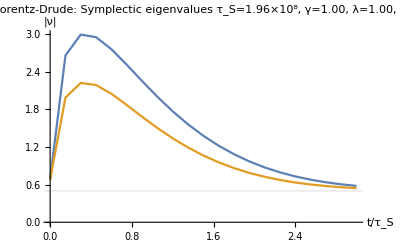

```mathematica
ListLinePlot[{fidtablerndSLDrnd1,fidtablerndSLDrnd2},AxesLabel->{"t/τ_S","ℱ(σ_(1, 2)(t),σ(∞))"},GridLines->{{2/(nγ*timescale)},{1}},PlotLabel->StringForm["Structured Lorentz-Drude: Fidelity\n τ_S=``, γ=``, λ=``, ω_s=``",ScientificForm[SetPrecision[timescale,3]],ScientificForm[SetPrecision[nγ,3]],ScientificForm[SetPrecision[nλ,3]],ScientificForm[SetPrecision[nωs,3]]],PlotRange->All,Epilog->Text["τ_C",{2/(nγ*timescale),Bottom},{0,-3},Background->White]]

ListLinePlot[fidtablerndSLDrnd12,AxesLabel->{"t/τ_S","ℱ(σ_1(t),σ_2(t))"},GridLines->{{2/(nγ*timescale)},{1}},PlotLabel->StringForm["Structured Lorentz-Drude: Fidelity between two random states\n τ_S=``, γ=``, λ=``, ω_s=``",ScientificForm[SetPrecision[timescale,3]],ScientificForm[SetPrecision[nγ,3]],ScientificForm[SetPrecision[nλ,3]],ScientificForm[SetPrecision[nωs,3]]],PlotRange->All,Epilog->Text["τ_C",{2/(nγ*timescale),Bottom},{0,-3},Background->White]]

ListLinePlot[{tsymplecicSLDrnd1,tsymplecicSLDrnd2},AxesLabel->{"t/τ_S","|ν|"},GridLines->{{},{0.5}},PlotLabel->StringForm["Structured Lorentz-Drude: Symplectic eigenvalues\n τ_S=``, γ=``, λ=``, ω_s=``",ScientificForm[SetPrecision[timescale,3]],ScientificForm[SetPrecision[nγ,3]],ScientificForm[SetPrecision[nλ,3]],ScientificForm[SetPrecision[nωs,3]]],PlotRange->All]
```

```mathematica
(* System properties *)
Jindex=2;
nω0=10;
nT=1;

nγ=1;
nλ=1;
nωs=100;
nparamsSLD={nγ,nλ,nωs};

τsystemListSLD[nω0,nγ,nλ,nωs]
markovTestSLD[nω0,nγ,nλ,nωs]

timescale=Max@τsystemListSLD[nω0,nγ,nλ,nωs];

tmax=3;
points=20;

fidGap=0.2;
```

{2.,2.,1.9602×10^8,1.9602×10^8}

1.0203×10^-8

```mathematica
σcovSLDtable=ParallelTable[Module[{rndcovmat1temp=rndcovn[1]},rndcovmat2temp=rndconvmatWithinFidelity[rndcovmat1temp,fidmintemp,fidmintemp+fidGap];({{xx01temp, xp01temp}, {xp01temp, pp01temp}})=rndcovmat1temp;({{xx02temp, xp02temp}, {xp02temp, pp02temp}})=rndcovmat2temp;{σcov[t*timescale,nT,nω0,nparamsSLD,xx01temp,pp01temp,xp01temp,Jindex],σcov[t*timescale,nT,nω0,nparamsSLD,xx02temp,pp02temp,xp02temp,Jindex]}],{t,0,tmax,tmax/points},{fidmintemp,0,1-fidGap,fidGap}];
```

```mathematica
ListLinePlot[Table[ParallelTable[{(i-1)*tmax/points,Fidelity[2*σcovSLDtable[[All,fidindex,1]][[i]],2*acovarianceMatrix[nT,nω0,nparamsSLD,Jindex]]//Chop},{i,1,points+1}],{fidindex,1,1/fidGap}],AxesLabel->{"t/τ_S","ℱ(σ_i(t),σ(∞))"},GridLines->{{2/(nγ*timescale)},{1}},PlotLabel->StringForm["Structured Lorentz-Drude: Fidelity\n τ_S=``, γ=``, λ=``, ω_s=``",ScientificForm[SetPrecision[timescale,3]],ScientificForm[SetPrecision[nγ,3]],ScientificForm[SetPrecision[nλ,3]],ScientificForm[SetPrecision[nωs,3]]],PlotRange->All,Epilog->Text["τ_C",{2/(nγ*timescale),Bottom},{0,-3},Background->White]]

ListLinePlot[Table[ParallelTable[{(i-1)*tmax/points,Fidelity[2*σcovSLDtable[[All,fidindex,1]][[i]],2*σcovSLDtable[[All,fidindex,2]][[i]]]//Chop},{i,1,points+1}],{fidindex,1,1/fidGap}],AxesLabel->{"t/τ_S","ℱ(σ_1(t),σ_2(t))"},GridLines->{{2/(nγ*timescale)},{1}},PlotLabel->StringForm["Structured Lorentz-Drude: Fidelity between two random states\n τ_S=``, γ=``, λ=``, ω_s=``",ScientificForm[SetPrecision[timescale,3]],ScientificForm[SetPrecision[nγ,3]],ScientificForm[SetPrecision[nλ,3]],ScientificForm[SetPrecision[nωs,3]]],PlotRange->All,Epilog->Text["τ_C",{2/(nγ*timescale),Bottom},{0,-3},Background->White]]
```

-Graphics-

-Graphics-

### For different α_(1,2)

```mathematica
SeedRandom[12345];
rndconvmat= rndcovn[1];
xx0=rndconvmat[[1,1]];
xp0=rndconvmat[[1,2]];
pp0=rndconvmat[[2,2]];
rndconvmat // MatrixForm
```

(4.33127 | 6.71647
6.71647 | 10.5083)

{{1/10,0.1},{1,1.},{10,9.99994},{100,99.9372},{1000,908.468}}

{{1/10,0.001},{1,0.01},{10,0.1},{100,1.},{1000,10.}}

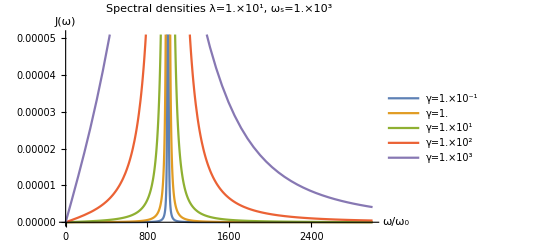

```mathematica
(* System properties *)
nω0=1;
nT=1;


(* For Structured Lorentz-Drude spectral density *)
γlist={10^-1,10^0,10^1,10^2,10^3};

nλ=10^1;
nωs=10^3;

Table[{γ,fwhmSLD[γ,nωs]//N},{γ,γlist}]

Table[{γ,nλ/nωs*γ//N},{γ,γlist}]

timescale=1*10^6;

tmax=50;
points=20;

Plot[Evaluate@Table[J[ω,{tγ,nλ,nωs},2],{tγ,γlist}],{ω,0,3*nωs},AxesLabel->{"ω/ω_0","J(ω)"},PlotLegends->Table[StringForm["γ=``",ScientificForm[N[tγ]]],{tγ,γlist}],PlotLabel->StringForm["Spectral densities\n λ=``, ω_s=``",ScientificForm[N[nλ]],ScientificForm[N[nωs]]]]
```

```mathematica
fidelitytableSLDγ=ParallelTable[{tγ,t,Fidelity[2*σcov[t*timescale,nT,nω0,{tγ,nλ,nωs},xx0,pp0,xp0,2]//Chop,2*acovarianceMatrix[nT,nω0,{tγ,nλ,nωs},2]]//Chop},{t,0,tmax,tmax/points},{tγ,γlist}];
```

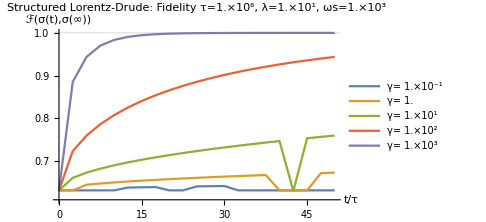

```mathematica
fidelitytableSLDγplots=ListLinePlot[Table[Re@fidelitytableSLDγ[[All,tγindex,2;;3]],{tγindex,1,Length[γlist]}],AxesLabel->{"t/τ","ℱ(σ(t),σ(∞))"},GridLines->{{},{1}},PlotLabel->StringForm["Structured Lorentz-Drude: Fidelity\n τ=``, λ=``, ωs=``",ScientificForm[N[timescale]],ScientificForm[N[nλ]],ScientificForm[N[nωs]]],PlotLegends->Table[StringForm["γ= ``",ScientificForm[N[γlist[[tγindex]]]]],{tγindex,1,Length[γlist]}],PlotRange->All,ImageSize->Medium]
```

{{1/100,0.01},{1/10,0.1},{1,1.},{10,9.99994},{100,99.9372}}

{{1/100,0.0001},{1/10,0.001},{1,0.01},{10,0.1},{100,1.}}

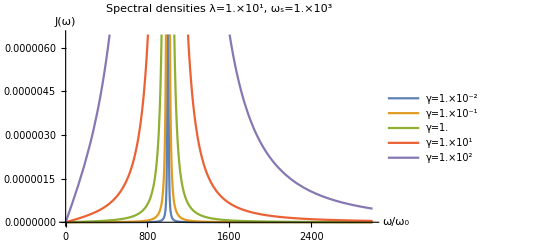

```mathematica
(* System properties *)
nω0=1;
nT=1;


(* For Structured Lorentz-Drude spectral density *)
γlist={10^-2,10^-1,10^0,10^1,10^2};

nλ=10^1;
nωs=10^3; (* CHANGE AS SMALLER *)

Table[{γ,fwhmSLD[γ,nωs]//N},{γ,γlist}]

Table[{γ,nλ/nωs*γ//N},{γ,γlist}]

timescale=1*10^6;

tmax=200;
points=50;

Plot[Evaluate@Table[J[ω,{tγ,nλ,nωs},2],{tγ,γlist}],{ω,0,3*nωs},AxesLabel->{"ω/ω_0","J(ω)"},PlotLegends->Table[StringForm["γ=``",ScientificForm[N[tγ]]],{tγ,γlist}],PlotLabel->StringForm["Spectral densities\n λ=``, ω_s=``",ScientificForm[N[nλ]],ScientificForm[N[nωs]]]]
```

```mathematica
fidelitytableSLDγ2=ParallelTable[{tγ,t,Fidelity[2*σcov[t*timescale,nT,nω0,{tγ,nλ,nωs},xx0,pp0,xp0,2]//Re,2*acovarianceMatrix[nT,nω0,{tγ,nλ,nωs},2]]//Re},{t,0,tmax,tmax/points},{tγ,γlist}];
```

$Aborted

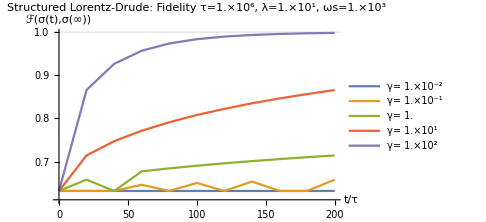

```mathematica
fidelitytableSLDγplots2=ListLinePlot[Table[Re@fidelitytableSLDγ2[[All,tγindex,2;;3]],{tγindex,1,Length[γlist]}],AxesLabel->{"t/τ","ℱ(σ(t),σ(∞))"},GridLines->{{},{1}},PlotLabel->StringForm["Structured Lorentz-Drude: Fidelity\n τ=``, λ=``, ωs=``",ScientificForm[N[timescale]],ScientificForm[N[nλ]],ScientificForm[N[nωs]]],PlotLegends->Table[StringForm["γ= ``",ScientificForm[N[γlist[[tγindex]]]]],{tγindex,1,Length[γlist]}],PlotRange->All,ImageSize->Medium]
```

{{1/10,0.1},{1,1.}}

{{1/10,0.001},{1,0.0001}}

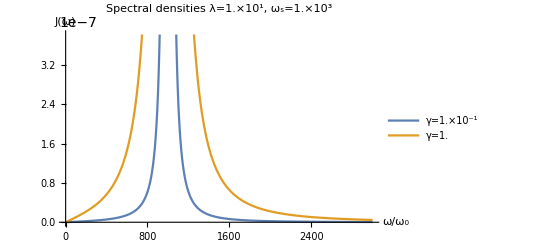

```mathematica
(* System properties *)
nω0=1;
nT=1;


(* For Structured Lorentz-Drude spectral density *)
γlist={10^-1,10^0};

nλ=10^1;
nωs=10^3;

Table[{γ,fwhmSLD[γ,nωs]//N},{γ,γlist}]

Table[{γ,nλ^2/nωs^2*1/fwhmSLD[γ,nωs]//N},{γ,γlist}]

timescale=1*10^10;

tmax=20;
points=50;

Plot[Evaluate@Table[J[ω,{tγ,nλ,nωs},2],{tγ,γlist}],{ω,0,3*nωs},AxesLabel->{"ω/ω_0","J(ω)"},PlotLegends->Table[StringForm["γ=``",ScientificForm[N[tγ]]],{tγ,γlist}],PlotLabel->StringForm["Spectral densities\n λ=``, ω_s=``",ScientificForm[N[nλ]],ScientificForm[N[nωs]]]]
```

```mathematica
fidelitytableSLDγ3=ParallelTable[{tγ,t,Fidelity[2*σcov[t*timescale,nT,nω0,{tγ,nλ,nωs},xx0,pp0,xp0,2]//Chop,2*acovarianceMatrix[nT,nω0,{tγ,nλ,nωs},2]]//Chop},{t,0,tmax,tmax/points},{tγ,γlist}];
```

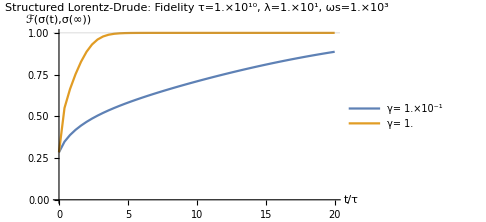

```mathematica
fidelitytableSLDγplots3=ListLinePlot[Table[Re@fidelitytableSLDγ3[[All,tγindex,2;;3]],{tγindex,1,Length[γlist]}],AxesLabel->{"t/τ","ℱ(σ(t),σ(∞))"},GridLines->{{},{1}},PlotLabel->StringForm["Structured Lorentz-Drude: Fidelity\n τ=``, λ=``, ωs=``",ScientificForm[N[timescale]],ScientificForm[N[nλ]],ScientificForm[N[nωs]]],PlotLegends->Table[StringForm["γ= ``",ScientificForm[N[γlist[[tγindex]]]]],{tγindex,1,Length[γlist]}],PlotRange->All,ImageSize->Medium]
```

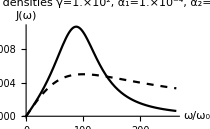
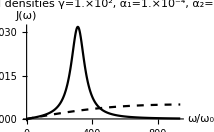
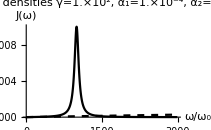
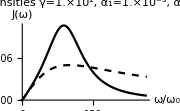
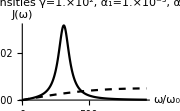
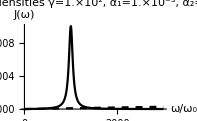
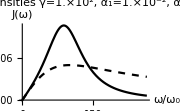
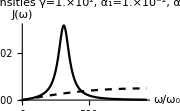
{{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}}

```mathematica
(* System properties *)
nω0=1;
nT=1;

α1list={10^-4,10^-3,10^-2}; 
α2list={10^2,10^3,10^4};

(* For Lorentz-Drude spectral density *)
(*nγ=α1/(2*α2);
nωc=α2;*)

(* For Structured Lorentz-Drude spectral density *)
γlist={10^2,10^3,10^4};

(*nλ=Sqrt[α1*α2*nγ];
nωs=Sqrt[α2*nγ];*)

timescale=1*10^6;

tmax=50;
points=10;

Table[Plot[{
J[ω,{tα1/(2*tα2),tα2},1],J[ω,{tγ,Sqrt[tα1*tα2*tγ],Sqrt[tα2*tγ]},2]},{ω,0,3*ωSLDmax[tγ,Sqrt[tα2*tγ]]},AxesLabel->{"ω/ω_0","J(ω)"},PlotStyle->{{Black,Dashed},Black},PlotLegends->{"Ohmic limiting spectrum","Structured spectral density"},PlotLabel->StringForm["Spectral densities\n γ=``, α_1=``, α_2=``",ScientificForm[N[tγ]],ScientificForm[N[tα1]],ScientificForm[N[tα2]]],PlotRange->All,ImageSize->Small],{tγ,γlist},{tα1,α1list},{tα2,α2list}]
```

```mathematica
fidelitytableLDfull=ParallelTable[{tα1,tα2,t,Fidelity[2*σcov[t*timescale,nT,nω0,{tα1/(2*tα2),tα2},xx0,pp0,xp0,1]//Chop,2*acovarianceMatrix[nT,nω0,{tα1/(2*tα2),tα2},1]]//Chop},{t,0,tmax,tmax/points},{tα1,α1list},{tα2,α2list}];

fidelitytableSLDfull=ParallelTable[{tγ,tα1,tα2,t,Fidelity[2*σcov[t*timescale,nT,nω0,{tγ,Sqrt[tα1*tα2*tγ],Sqrt[tα2*tγ]},xx0,pp0,xp0,2]//Chop,2*acovarianceMatrix[nT,nω0,{tγ,Sqrt[tα1*tα2*tγ],Sqrt[tα2*tγ]},2]]//Chop},{t,0,tmax,tmax/points},{tγ,γlist},{tα1,α1list},{tα2,α2list}];
```

```mathematica
fidelitytableLDfullplots=Table[ListLinePlot[Table[Re@fidelitytableLDfull[[All,tα1index,tα2index,3;;4]],{tα1index,1,Length[α1list]}],AxesLabel->{"t/τ","ℱ(σ(t),σ(∞))"},GridLines->{{},{1}},PlotLabel->StringForm["Lorentz-Drude: Fidelity\n τ=``, α_2=``",ScientificForm[N[timescale]],ScientificForm[N[α2list[[tα2index]]]]],PlotLegends->Table[StringForm["α_1= ``",ScientificForm[N[α1list[[tα1index]]]]],{tα1index,1,Length[α1list]}],PlotRange->All,ImageSize->Medium],{tα2index,1,Length[α2list]}]

fidelitytableSLDfullplots=Table[ListLinePlot[Table[Re@fidelitytableSLDfull[[All,tγindex,tα1index,tα2index,4;;5]],{tα1index,1,Length[α1list]}],AxesLabel->{"t/τ","ℱ(σ(t),σ(∞))"},GridLines->{{},{1}},PlotLabel->StringForm["Structured Lorentz-Drude: Fidelity\n τ=``, γ=``, α_2=``",ScientificForm[N[timescale]],ScientificForm[N[γlist[[tγindex]]]],ScientificForm[N[α2list[[tα2index]]]]],PlotLegends->Table[StringForm["α_1= ``",ScientificForm[N[α1list[[tα1index]]]]],{tα1index,1,Length[α1list]}],PlotRange->All,ImageSize->Medium],{tγindex,1,Length[γlist]},{tα2index,1,Length[α2list]}]
```

{-Graphics-,-Graphics-,-Graphics-}

{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
symplectictableSLDfull=ParallelTable[{tγ,tα1,tα2,t,symplectic[σcov[t*timescale,nT,nω0,{tγ,Sqrt[tα1*tα2*tγ],Sqrt[tα2*tγ]},xx0,pp0,xp0,2]//Chop]//Chop},{t,0,tmax,tmax/points},{tγ,γlist},{tα1,α1list},{tα2,α2list}];
```

```mathematica
symplectictableSLDfullplots=Table[ListLinePlot[Table[Re@symplectictableSLDfull[[All,tγindex,tα1index,tα2index,4;;5]],{tα1index,1,Length[α1list]}],AxesLabel->{"t/τ","|ν|"},GridLines->{{},{0.5}},PlotLabel->StringForm["Structured Lorentz-Drude: Symplectic eigenvalues\n τ=``, γ=``, α_2=``",ScientificForm[N[timescale]],ScientificForm[N[γlist[[tγindex]]]],ScientificForm[N[α2list[[tα2index]]]]],PlotLegends->Table[StringForm["α_1= ``",ScientificForm[N[α1list[[tα1index]]]]],{tα1index,1,Length[α1list]}],PlotRange->All,ImageSize->Medium],{tγindex,1,Length[γlist]},{tα2index,1,Length[α2list]}]
```

{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
α1list={10^-4,10^-3,10^-2}; 
α2list={10^2,10^3,10^4};
γlist={10^2,10^3,10^4};

Table[{γ,α2,α1,fwhmSLD[γ,Sqrt[α2*γ]]//N},{γ,γlist},{α2,α2list},{α1,α1list}]

Table[{γ,α2,α1,Sqrt[α1]/fwhmSLD[γ,Sqrt[α2*γ]]//N},{γ,γlist},{α2,α2list},{α1,α1list}]
```

{{{{100,100,1/10000,90.8468},{100,100,1/1000,90.8468},{100,100,1/100,90.8468}},{{100,1000,1/10000,99.3418},{100,1000,1/1000,99.3418},{100,1000,1/100,99.3418}},{{100,10000,1/10000,99.9372},{100,10000,1/1000,99.9372},{100,10000,1/100,99.9372}}},{{{1000,100,1/10000,328.532},{1000,100,1/1000,328.532},{1000,100,1/100,328.532}},{{1000,1000,1/10000,908.468},{1000,1000,1/1000,908.468},{1000,1000,1/100,908.468}},{{1000,10000,1/10000,993.418},{1000,10000,1/1000,993.418},{1000,10000,1/100,993.418}}},{{{10000,100,1/10000,349.365},{10000,100,1/1000,349.365},{10000,100,1/100,349.365}},{{10000,1000,1/10000,3285.32},{10000,1000,1/1000,3285.32},{10000,1000,1/100,3285.32}},{{10000,10000,1/10000,9084.68},{10000,10000,1/1000,9084.68},{10000,10000,1/100,9084.68}}}}

{{{{100,100,1/10000,0.000110075},{100,100,1/1000,0.000348089},{100,100,1/100,0.00110075}},{{100,1000,1/10000,0.000100663},{100,1000,1/1000,0.000318323},{100,1000,1/100,0.00100663}},{{100,10000,1/10000,0.000100063},{100,10000,1/1000,0.000316427},{100,10000,1/100,0.00100063}}},{{{1000,100,1/10000,0.0000304384},{1000,100,1/1000,0.0000962547},{1000,100,1/100,0.000304384}},{{1000,1000,1/10000,0.0000110075},{1000,1000,1/1000,0.0000348089},{1000,1000,1/100,0.000110075}},{{1000,10000,1/10000,0.0000100663},{1000,10000,1/1000,0.0000318323},{1000,10000,1/100,0.000100663}}},{{{10000,100,1/10000,0.0000286234},{10000,100,1/1000,0.000090515},{10000,100,1/100,0.000286234}},{{10000,1000,1/10000,3.04384×10^-6},{10000,1000,1/1000,9.62547×10^-6},{10000,1000,1/100,0.0000304384}},{{10000,10000,1/10000,1.10075×10^-6},{10000,10000,1/1000,3.48089×10^-6},{10000,10000,1/100,0.0000110075}}}}

```mathematica
nω0=1;
nT=1;

α1list={10^8,10^9,10^10}; 
α2list={10^0,10^1,10^2};

timescale=1*10^6;

tmax=50;
points=10;

Table[Plot[Evaluate@Table[{
J[ω,{tα1/(2*tα2),tα2},1]},{tα2,α2list}],{ω,0,3*100},AxesLabel->{"ω/ω_0","J(ω)"},PlotLegends->Table[StringForm["α_2=``",ScientificForm[N[tα2]]],{tα2,α1list}],PlotLabel->StringForm["Lorentz-Drude Spectral densities\n α_1=``",ScientificForm[N[tα1]]],PlotRange->All,ImageSize->Small],{tα1,α1list}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
fidelitytableLDfull2=ParallelTable[{tα1,tα2,t,Fidelity[2*σcov[t*timescale,nT,nω0,{tα1/(2*tα2),tα2},xx0,pp0,xp0,1]//Chop,2*acovarianceMatrix[nT,nω0,{tα1/(2*tα2),tα2},1]]//Chop},{t,0,tmax,tmax/points},{tα1,α1list},{tα2,α2list}];
```

```mathematica
fidelitytableLDfullplots2=Table[ListLinePlot[Table[Re@fidelitytableLDfull2[[All,tα1index,tα2index,3;;4]],{tα1index,1,Length[α1list]}],AxesLabel->{"t/τ","ℱ(σ(t),σ(∞))"},GridLines->{{},{1}},PlotLabel->StringForm["Lorentz-Drude: Fidelity\n τ=``, α_2=``",ScientificForm[N[timescale]],ScientificForm[N[α2list[[tα2index]]]]],PlotLegends->Table[StringForm["α_1= ``",ScientificForm[N[α1list[[tα1index]]]]],{tα1index,1,Length[α1list]}],PlotRange->All,ImageSize->Medium],{tα2index,1,Length[α2list]}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
rndconvmat=rndcovn[1];
xx0=rndconvmat[[1,1]];
xp0=rndconvmat[[1,2]];
pp0=rndconvmat[[2,2]];
rndconvmat // MatrixForm
```

(3.15664 | 0.873378
0.873378 | 0.351724)

```mathematica
(* System properties *)
nω0=1;
nT=1;

α1=10^-3; (*Subscript[α, 1]=Subscript[γ, h]*) 
α2list={0.1,1,10,10^2,10^3};

(* For Lorentz-Drude spectral density *)
nγ=α1/(2*α2);
nωc=α2;

(* For Structured Lorentz-Drude spectral density *)
nγ=10^3;
nλ=Sqrt[α1*α2*nγ];
nωs=Sqrt[α2*nγ];

Table[Plot[{α1^-2*J[ω,{α1/(2*α2),α2},1],α1^-2*J[ω,{nγ,Sqrt[α1*α2*nγ],Sqrt[α2*nγ]},2]},{ω,0,3000},AxesLabel->{"ω/ω_0","γ_h^-2 J(ω)"},PlotStyle->{{Black,Dashed},Black},PlotLegends->{"Ohmic limiting spectrum","Structured spectral density"},PlotLabel->StringForm["Spectral densities for α_1=`` and α_2=``",ScientificForm[N[α1]],ScientificForm[N[α2]]],PlotRange->All],{α2,α2list}]

timescale=1*10^6;

tmax=10;
points=10;

fidelitytableSLDfull3=ParallelTable[{t,Fidelity[2*σcov[t*timescale,nT,nω0,{nγ,Sqrt[α1*tα2*nγ],Sqrt[tα2*nγ]},xx0,pp0,xp0,2]//Chop,2*acovarianceMatrix[nT,nω0,{nγ,Sqrt[α1*tα2*nγ],Sqrt[tα2*nγ]},2]]//Chop},{t,0,tmax,tmax/points},{tα2,α2list}];
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

$Aborted

```mathematica
fidelitytableSLDfullplots3=Table[ListLinePlot[fidelitytableSLDfull3[[All,tα2index]]//Chop,AxesLabel->{"t/τ","ℱ(σ(t),σ(∞))"},GridLines->{{},{1}},PlotLabel->StringForm["Structured Lorentz-Drude: Fidelity\n τ=``, α_1=``",ScientificForm[N[timescale]],ScientificForm[N[α1]]],PlotLegends->StringForm["α_2= ``",ScientificForm[N[α2list[[tα2index]]]]],PlotRange->All,ImageSize->Medium],{tα2index,1,Length[α2list]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
fidelitytableSLDfull3[[All,1]]
```

{{0,0.484941},{1,0.427074+0.819607 ⅈ},{2,0.427074+0.819607 ⅈ},{3,0.427074+0.819607 ⅈ},{4,0.427074+0.819607 ⅈ},{5,0.427074+0.819607 ⅈ},{6,0.427074+0.819607 ⅈ},{7,0.427074+0.819607 ⅈ},{8,0.427074+0.819607 ⅈ},{9,0.427074+0.819607 ⅈ},{10,0.427074+0.819607 ⅈ}}

```mathematica
(* System properties *)
nω0=1;
nT=1;

α1=10^-3; (*Subscript[α, 1]=Subscript[γ, h]*) 
α2=0.1;


(* For Structured Lorentz-Drude spectral density *)
nγ=10^3;
nλ=Sqrt[α1*α2*nγ];
nωs=Sqrt[α2*nγ];

ListLinePlot[ParallelTable[{t,symplectic[σcov[t*timescale,nT,nω0,{nγ,nλ,nωs},xx0,pp0,xp0,2]]},{t,0,tmax,tmax/points}],AxesLabel->{"t/τ","|ν|"},GridLines->{{},{0.5}},PlotLabel->StringForm["Structured Lorentz-Drude: Symplectic eigenvalues\n τ=``, γ=``, λ=``, ω_s=``",ScientificForm[N[timescale]],ScientificForm[N[nγ]],ScientificForm[N[nλ]],ScientificForm[N[nωs]]],PlotRange->All]
```

-Graphics-

```mathematica
(* System properties *)
nω0=1;
nT=1;

α1=10^-3; (*Subscript[α, 1]=Subscript[γ, h]*) 
α2list={10^5,10^6};

(* For Lorentz-Drude spectral density *)
nγ=α1/(2*α2);
nωc=α2;

(* For Structured Lorentz-Drude spectral density *)
nγ=10^3;
nλ=Sqrt[α1*α2*nγ];
nωs=Sqrt[α2*nγ];

Table[Plot[{α1^-2*J[ω,{α1/(2*α2),α2},1],α1^-2*J[ω,{nγ,Sqrt[α1*α2*nγ],Sqrt[α2*nγ]},2]},{ω,0,3000},AxesLabel->{"ω/ω_0","γ_h^-2 J(ω)"},PlotStyle->{{Black,Dashed},Black},PlotLegends->{"Ohmic limiting spectrum","Structured spectral density"},PlotLabel->StringForm["Spectral densities for α_1=`` and α_2=``",ScientificForm[N[α1]],ScientificForm[N[α2]]],PlotRange->All],{α2,α2list}]

timescale=1*10^7;

tmax=50;
points=20;

fidelitytableSLDfull4=ParallelTable[{t,Fidelity[2*σcov[t*timescale,nT,nω0,{nγ,Sqrt[α1*tα2*nγ],Sqrt[tα2*nγ]},xx0,pp0,xp0,2]//Chop,2*acovarianceMatrix[nT,nω0,{nγ,Sqrt[α1*tα2*nγ],Sqrt[tα2*nγ]},2]]//Chop},{t,0,tmax,tmax/points},{tα2,α2list}];
```

{-Graphics-,-Graphics-}

```mathematica
fidelitytableSLDfullplots4=Table[ListLinePlot[fidelitytableSLDfull4[[All,tα2index]]//Chop,AxesLabel->{"t/τ","ℱ(σ(t),σ(∞))"},GridLines->{{},{1}},PlotLabel->StringForm["Structured Lorentz-Drude: Fidelity\n τ=``, α_1=``",ScientificForm[N[timescale]],ScientificForm[N[α1]]],PlotLegends->StringForm["α_2= ``",ScientificForm[N[α2list[[tα2index]]]]],PlotRange->All,ImageSize->Medium],{tα2index,1,Length[α2list]}]
```

{-Graphics-,-Graphics-}

### Full width at half maximum calculations

#### Lorentz - Drude FWHM

```mathematica
J[ω,{γ,ωc},1]
```

(2 γ ω ωc^2)/(ω^2+ωc^2)

```mathematica
Solve[D[J[ω,{γ,ωc},1],ω]==0,ω]
```

{{ω→-ωc},{ω→ωc}}

```mathematica
LDmax=J[ω,{γ,ωc},1] /. ω->ωc
```

γ ωc

```mathematica
{ωLDmin,ωLDplus}=ω /. Solve[J[ω,{γ,ωc},1] ==LDmax/2,ω];
```

```mathematica
Solve[J[ω,{γ,ωc},1] ==LDmax/2,ω,Reals];
```

```mathematica
fwhmLD=ωLDplus-ωLDmin//FullSimplify
```

2 √3 ωc

#### Structured Lorentz - Drude FWHM

```mathematica
Solve[D[J[ω,{γ,λ,ωs},2],ω]==0,ω]
```

{{ω→-√(1/6 (-γ^2+2 ωs^2)+1/6 √(γ^4-4 γ^2 ωs^2+16 ωs^4))},{ω→√(1/6 (-γ^2+2 ωs^2)+1/6 √(γ^4-4 γ^2 ωs^2+16 ωs^4))}}

```mathematica
nSLDmax=J[ω,{γ,λ,ωs},2] /. ω->√(1/6 (-γ^2+2 ωs^2)+1/6 √(γ^4-4 γ^2 ωs^2+16 ωs^4))
```

(γ λ^2 √(1/6 (-γ^2+2 ωs^2)+1/6 √(γ^4-4 γ^2 ωs^2+16 ωs^4)))/(γ^2 (1/6 (-γ^2+2 ωs^2)+1/6 √(γ^4-4 γ^2 ωs^2+16 ωs^4))+(-ωs^2+1/6 (-γ^2+2 ωs^2)+1/6 √(γ^4-4 γ^2 ωs^2+16 ωs^4))^2)

```mathematica
SLDmax[γ_,λ_,ωs_]:=((γ λ^2 √(1/6 (-γ^2+2 ωs^2)+1/6 √(γ^4-4 γ^2 ωs^2+16 ωs^4)))/(γ^2 (1/6 (-γ^2+2 ωs^2)+1/6 √(γ^4-4 γ^2 ωs^2+16 ωs^4))+(-ωs^2+1/6 (-γ^2+2 ωs^2)+1/6 √(γ^4-4 γ^2 ωs^2+16 ωs^4))^2))

ωSLDmax[γ_,ωs_]:=√(1/6 (-γ^2+2 ωs^2)+1/6 √(γ^4-4 γ^2 ωs^2+16 ωs^4))
```

```mathematica
{nωSLDmin,nωSLDplus}=ω /. Solve[J[ω,{γ,λ,ωs},2]==nSLDmax/2,ω];
```

```mathematica
nωSLDplus-nωSLDmin//FullSimplify
```

-Root[27 ωs^16+(16 γ^6 ωs^8-96 γ^4 ωs^10-276 γ^2 ωs^12+808 ωs^14) #1^2+(-224 γ^8 ωs^4+1792 γ^6 ωs^6-4318 γ^4 ωs^8+2936 γ^2 ωs^10-3340 ωs^12) #1^4+(16 γ^10-160 γ^8 ωs^2+204 γ^6 ωs^4+1336 γ^4 ωs^6-4780 γ^2 ωs^8+4632 ωs^10) #1^6+(59 γ^8-472 γ^6 ωs^2+588 γ^4 ωs^4+1424 γ^2 ωs^6-2206 ωs^8) #1^8+(124 γ^6-744 γ^4 ωs^2+1236 γ^2 ωs^4-488 ωs^6) #1^10+(162 γ^4-648 γ^2 ωs^2+756 ωs^4) #1^12+(108 γ^2-216 ωs^2) #1^14+27 #1^16&,3]+Root[27 ωs^16+(16 γ^6 ωs^8-96 γ^4 ωs^10-276 γ^2 ωs^12+808 ωs^14) #1^2+(-224 γ^8 ωs^4+1792 γ^6 ωs^6-4318 γ^4 ωs^8+2936 γ^2 ωs^10-3340 ωs^12) #1^4+(16 γ^10-160 γ^8 ωs^2+204 γ^6 ωs^4+1336 γ^4 ωs^6-4780 γ^2 ωs^8+4632 ωs^10) #1^6+(59 γ^8-472 γ^6 ωs^2+588 γ^4 ωs^4+1424 γ^2 ωs^6-2206 ωs^8) #1^8+(124 γ^6-744 γ^4 ωs^2+1236 γ^2 ωs^4-488 ωs^6) #1^10+(162 γ^4-648 γ^2 ωs^2+756 ωs^4) #1^12+(108 γ^2-216 ωs^2) #1^14+27 #1^16&,4]

```mathematica
fwhmSLD[γ_,ωs_]:=-Root[27 ωs^16+(16 γ^6 ωs^8-96 γ^4 ωs^10-276 γ^2 ωs^12+808 ωs^14) #1^2+(-224 γ^8 ωs^4+1792 γ^6 ωs^6-4318 γ^4 ωs^8+2936 γ^2 ωs^10-3340 ωs^12) #1^4+(16 γ^10-160 γ^8 ωs^2+204 γ^6 ωs^4+1336 γ^4 ωs^6-4780 γ^2 ωs^8+4632 ωs^10) #1^6+(59 γ^8-472 γ^6 ωs^2+588 γ^4 ωs^4+1424 γ^2 ωs^6-2206 ωs^8) #1^8+(124 γ^6-744 γ^4 ωs^2+1236 γ^2 ωs^4-488 ωs^6) #1^10+(162 γ^4-648 γ^2 ωs^2+756 ωs^4) #1^12+(108 γ^2-216 ωs^2) #1^14+27 #1^16&,3]+Root[27 ωs^16+(16 γ^6 ωs^8-96 γ^4 ωs^10-276 γ^2 ωs^12+808 ωs^14) #1^2+(-224 γ^8 ωs^4+1792 γ^6 ωs^6-4318 γ^4 ωs^8+2936 γ^2 ωs^10-3340 ωs^12) #1^4+(16 γ^10-160 γ^8 ωs^2+204 γ^6 ωs^4+1336 γ^4 ωs^6-4780 γ^2 ωs^8+4632 ωs^10) #1^6+(59 γ^8-472 γ^6 ωs^2+588 γ^4 ωs^4+1424 γ^2 ωs^6-2206 ωs^8) #1^8+(124 γ^6-744 γ^4 ωs^2+1236 γ^2 ωs^4-488 ωs^6) #1^10+(162 γ^4-648 γ^2 ωs^2+756 ωs^4) #1^12+(108 γ^2-216 ωs^2) #1^14+27 #1^16&,4]
fwhmSLD::usage="fwhmSLD[γ,ωs] gives the full width at half maximum (FWHM) of the structured Lorentz-Drude spectral density";
```

```mathematica
Asymptotic[SLDmax[γ,λ,ωs],γ->0]
```

λ^2/(γ ωs)

```mathematica
AsymptoticSolve[J[ω,{γ,λ,ωs},2]==λ^2/(2 γ ωs),ω,γ->0]
```

AsymptoticSolve::avars: Warning: Assumptions that involve the variables {γ,ω} are ignored.

{{ω→-1/2 ⅈ √3 γ-ωs},{ω→1/2 ⅈ √3 γ-ωs},{ω→-γ/2+ωs},{ω→γ/2+ωs}}

```mathematica
γlist=Table[10^i,{i,0,6}];
α2list=Table[10^i,{i,0,6}];

fwhmSLDarray=Table[fwhmSLD[γ,Sqrt[α2*γ]]//N,{γ,γlist},{α2,α2list}];

ListDensityPlot[fwhmSLDarray,PlotLegends->Automatic,FrameLabel->{"Log(γ)","Log(α_2)"},ScalingFunctions->"Log"]
```

-Graphics-

Set ω_s^2=γ α_2 to determine the Structured Lorentz-Drude FWMH for γ-> ∞

```mathematica
fwhmSLD[γ,Sqrt[γ α2]]//FullSimplify
```

-Root[27 α2^8 γ^8+(808 α2^7 γ^7-276 α2^6 γ^8-96 α2^5 γ^9+16 α2^4 γ^10) #1^2+(-3340 α2^6 γ^6+2936 α2^5 γ^7-4318 α2^4 γ^8+1792 α2^3 γ^9-224 α2^2 γ^10) #1^4+(4632 α2^5 γ^5-4780 α2^4 γ^6+1336 α2^3 γ^7+204 α2^2 γ^8-160 α2 γ^9+16 γ^10) #1^6+(-2206 α2^4 γ^4+1424 α2^3 γ^5+588 α2^2 γ^6-472 α2 γ^7+59 γ^8) #1^8+(-488 α2^3 γ^3+1236 α2^2 γ^4-744 α2 γ^5+124 γ^6) #1^10+(756 α2^2 γ^2-648 α2 γ^3+162 γ^4) #1^12+(-216 α2 γ+108 γ^2) #1^14+27 #1^16&,3]+Root[27 α2^8 γ^8+(808 α2^7 γ^7-276 α2^6 γ^8-96 α2^5 γ^9+16 α2^4 γ^10) #1^2+(-3340 α2^6 γ^6+2936 α2^5 γ^7-4318 α2^4 γ^8+1792 α2^3 γ^9-224 α2^2 γ^10) #1^4+(4632 α2^5 γ^5-4780 α2^4 γ^6+1336 α2^3 γ^7+204 α2^2 γ^8-160 α2 γ^9+16 γ^10) #1^6+(-2206 α2^4 γ^4+1424 α2^3 γ^5+588 α2^2 γ^6-472 α2 γ^7+59 γ^8) #1^8+(-488 α2^3 γ^3+1236 α2^2 γ^4-744 α2 γ^5+124 γ^6) #1^10+(756 α2^2 γ^2-648 α2 γ^3+162 γ^4) #1^12+(-216 α2 γ+108 γ^2) #1^14+27 #1^16&,4]

```mathematica
Asymptotic[27 α2^8 γ^8+(808 α2^7 γ^7-276 α2^6 γ^8-96 α2^5 γ^9+16 α2^4 γ^10) #1^2+(-3340 α2^6 γ^6+2936 α2^5 γ^7-4318 α2^4 γ^8+1792 α2^3 γ^9-224 α2^2 γ^10) #1^4+(4632 α2^5 γ^5-4780 α2^4 γ^6+1336 α2^3 γ^7+204 α2^2 γ^8-160 α2 γ^9+16 γ^10) #1^6+(-2206 α2^4 γ^4+1424 α2^3 γ^5+588 α2^2 γ^6-472 α2 γ^7+59 γ^8) #1^8+(-488 α2^3 γ^3+1236 α2^2 γ^4-744 α2 γ^5+124 γ^6) #1^10+(756 α2^2 γ^2-648 α2 γ^3+162 γ^4) #1^12+(-216 α2 γ+108 γ^2) #1^14+27 #1^16&[x],γ->Infinity]
```

ConditionalExpression[(16 x^6-224 x^4 α2^2+16 x^2 α2^4) γ^10, ]

```mathematica
Solve[(16 x^6-224 x^4 α2^2+16 x^2 α2^4)==0,x]
```

{{x→0},{x→0},{x→-2 α2-√3 α2},{x→2 α2-√3 α2},{x→-2 α2+√3 α2},{x→2 α2+√3 α2}}

```mathematica
(x/.Solve[(16 x^6-224 x^4 α2^2+16 x^2 α2^4)==0,x][[-1]])-x/.Solve[(16 x^6-224 x^4 α2^2+16 x^2 α2^4)==0,x][[-2]]
```

4 α2

Setting ω_s^2=γ α_2, the Structured Lorentz-Drude FWMH=4 α_2 for γ-> ∞

#### General s with exponential cut-off FWHM

```mathematica
J[ω,{s,γ,ωc},3]
```

1/2 ⅇ^(-ω/ωc) π γ ω^s ωc^(1-s)

```mathematica
Solve[D[J[ω,{s,γ,ωc},3],ω]==0,ω,Assumptions->s∈PositiveReals]
```

{{ω→ConditionalExpression[0, s>1]},{ω→s ωc}}

```mathematica
sExpmax=J[ω,{s,γ,ωc},3] /. ω->s ωc
```

1/2 ⅇ^-s π γ ωc^(1-s) (s ωc)^s

```mathematica
{ωsExpmin,ωsExpplus}=ω /. Solve[J[ω,{s,γ,ωc},3] ==sExpmax/2,ω];
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

ReplaceAll::reps: {Solve[1/2 ⅇ^(-ω/ωc) π γ ω^s ωc^(1-s)==1/4 ⅇ^-s π γ ωc^(1-s) (s ωc)^s,ω]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {ωsExpmin,ωsExpplus} and ω/.Solve[1/2 ⅇ^(-ω/ωc) π γ ω^s ωc^(1-s)==1/4 ⅇ^-s π γ ωc^(1-s) (s ωc)^s,ω] are not the same shape.

```mathematica
fwhmsExp=ωsExpplus-ωsExpmin//FullSimplify
```

```mathematica
Solve[J[ω,{s,γ,ωc},3] ==sExpmax/2/.s->1,ω]
```

{{ω→ConditionalExpression[-ωc ProductLog[-1/(2 ⅇ)], t∈ℝ]},{ω→ConditionalExpression[-ωc ProductLog[-1,-1/(2 ⅇ)], t∈ℝ]}}

```mathematica
ns=2;
Replace[ω,Normal[Solve[J[ω,{s,γ,ωc},3] ==sExpmax/2/.s->ns,ω]][[2]]]-Replace[ω,Normal[Solve[J[ω,{s,γ,ωc},3] ==sExpmax/2/.s->ns,ω]][[1]]]
```

2 ωc ProductLog[-1/(√2 ⅇ)]-2 ωc ProductLog[1/(√2 ⅇ)]

```mathematica
fwhmsExp[s_,ωc_]:=Replace[ω,Normal[Solve[J[ω,{s,γ,ωc},3] ==(1/2 ⅇ^-s π γ ωc^(1-s) (s ωc)^s)/2,ω]][[2]]]-Replace[ω,Normal[Solve[J[ω,{s,γ,ωc},3] ==(1/2 ⅇ^-s π γ ωc^(1-s) (s ωc)^s)/2,ω]][[1]]]//N//Abs
```

```mathematica
ListPlot[Table[{s,fwhmsExp[s,1000]},{s,1,10}],AxesLabel->{"s","FWHM"}]
```

-Graphics-

### Test stuff

```mathematica
(* System properties *)
nω0=1000;
nT=1;

α1=10^-3; (*Subscript[α, 1]=Subscript[γ, h]*) 
α2=10^3;

(* For Lorentz-Drude spectral density *)
nγ=α1/(2*α2);
nωc=α2;

(* For Structured Lorentz-Drude spectral density *)
nγ=10^3;
nλ=Sqrt[α1*α2*nγ];
nωs=Sqrt[α2*nγ];

acovarianceMatrix[nT,nω0,{nγ,nλ,nωs},2]//N //Chop//MatrixForm
acovarianceMatrix[nT,nω0,{nγ,nωc},1]//N//Chop//MatrixForm
```

(0.0005 | 0
0 | 500.)

(0.0005 | 0
0 | 500.)

## Redfield equation

### Setup

#### Functions and variables

The one-sided Fourier transform of the bath correlation function Γ(ω)is given by

Γ(ω)=∫_0^∞ ⅇ^ⅈωt⟨B(t)B(0)⟩ⅆt  =  1/2 γ(ω)+ⅈS(ω),

The decay rate γ(ω) and the Stark shift S(ω)can be expressed in terms of the spectral density,

γ(ω)= 2 J(ω)(1+n(ω))
S(ω)= -ℋ[J(ω)(1+n(ω))],

where ℋ denotes the Hilbert transform,

ℋ[f(ω)] := 1/π 𝒫∫_(-∞)^∞ (f(ω'))/(ω'-ω)ⅆω'.

In the following, Γ is used to express the decay rate instead of  γ, as γ is reserved for the dissipation strength of the spectral density.

```mathematica
Γ[ω_,T_,params_,JIndex_]:=2J[ω,params,JIndex](1+1/(ⅇ^(ω/T)-1))
Γ::usage="Γ[ω,T,params,JIndex] returns the decay rate for given frequency, temperature, and spectral density";
(*
S[ω_,T_,params_,JIndex_]:=-1/πNIntegrate[J[ωp,params,JIndex]/(ωp-ω)(1+1/(ⅇ^(ωp/T)-1)),{ωp,-∞,∞},Method->"PrincipalValue", Exclusions->{ω},AccuracyGoal->5,PrecisionGoal->6,WorkingPrecision->8,MaxRecursion->15]*)
S[ω_,T_,params_,JIndex_]:=0
S::usage="S[ω,T,params,JIndex] returns the Lamb + Stark shifts for given parameters";
```

In this notation, we have

Δ = Γ[-ω] - Γ[ω]
Σ = -Γ[-ω] - Γ[ω]
Δ' = S[-ω] - S[ω]
Σ'= -S[-ω] - S[ω]

so therefore,

Δ=-2J(ω_0)
Σ=-2J(ω_0)coth(ω_0/(2T))
Δ'=ℋ[J(ω_0)coth(ω_0/(2T))]
Σ'=ℋ[J(ω_0)]

```mathematica
fidelityCovAndSteady[ω0_,T_,params_,cov0_,tmax_,points_,EorR_,JIndex_]:=Module[{timescale,ωRed,xx0,xp0,pp0,σcovExact,fidtableExact,tsymplecicExact,σcovRed,fidtableRed,tsymplecicRed},
({{xx0, xp0}, {xp0, pp0}})=cov0;
(*If[JIndex==1,ωRed=Sqrt[ω0^2+2*params[[1]]*params[[2]]],If[JIndex==2,ωRed=Sqrt[ω0^2+(params[[2]]/params[[3]])^2],Print["Invalid JIndex"];Abort[]]];*)
ωRed=ω0; (* No counter-term *)

If[EorR=="E",
(* Exact *)
timescale=Max@τsystemList[ω0,params,JIndex];

σcovExact=ParallelTable[σcov[t*timescale,T,ω0,params,xx0,pp0,xp0,JIndex]//Chop,{t,0,tmax,tmax/points}];
fidtableExact=ParallelTable[{(i-1)*tmax/points,Fidelity[2*σcovExact[[i]],2*acovarianceMatrix[T,ω0,params,JIndex]]},{i,1,points+1}];
tsymplecicExact=ParallelTable[{(i-1)*tmax/points,symplectic[σcovExact[[i]]]},{i,1,points+1}];
(*puritytableLD1=ParallelTable[{(i-1)*tmax/points,purity[2*σcovLD1[[i]]]},{i,1,points+1}];*)

If[AnyTrue[tsymplecicExact[[All,2]][[2;;-1]],#<0.5&],Print[Style["EXACT SYSTEM IS UNPHYSICAL",15]],Print[Style["EXACT SYSTEM IS PHYSICAL",15]]];

Return[{fidtableExact,tsymplecicExact}]

,If[EorR=="R",
(* Redfield *)
timescale=Max@τsystemListRedfield[ωRed,T,params,JIndex];

σcovRed=ParallelTable[σcovRedfield[t*timescale,ωRed,T,params,xx0,pp0,xp0,JIndex]//Chop,{t,0,tmax,tmax/points}];
fidtableRed=ParallelTable[{(i-1)*tmax/points,Fidelity[2*σcovRed[[i]],2*σcovRedfieldSteadyState[ωRed,T,params,JIndex]]},{i,1,points+1}];
tsymplecicRed=ParallelTable[{(i-1)*tmax/points,symplectic[σcovRed[[i]]]},{i,1,points+1}];
(*puritytableLDred1=ParallelTable[{(i-1)*tmax/points,purity[2*σcovLDred1[[i]]]},{i,1,points+1}];*)

If[AnyTrue[tsymplecicRed[[All,2]][[2;;-1]],#<0.5&],Print[Style["REDFIELD SYSTEM IS UNPHYSICAL",15]],Print[Style["REDFIELD SYSTEM IS PHYSICAL",15]]];

Return[{fidtableRed,tsymplecicRed}]

,Print["Invalid EorR"];Abort[]]];
]
```

```mathematica
fidelityCov1Cov2[ω0_,T_,params_,cov01_,cov02_,tmax_,points_,EorR_,JIndex_]:=Module[{timescale,ωRed,xx01,xp01,pp01,xx02,xp02,pp02,σcovExact1,σcovExact2,fidtableExact12,tsymplecicExact1,tsymplecicExact2,σcovRed1,σcovRed2,fidtableRed12,tsymplecicRed1,tsymplecicRed2},
({{xx01, xp01}, {xp01, pp01}})=cov01;({{xx02, xp02}, {xp02, pp02}})=cov02;
(*If[JIndex==1,ωRed=Sqrt[ω0^2+2*params[[1]]*params[[2]]],If[JIndex==2,ωRed=Sqrt[ω0^2+(params[[2]]/params[[3]])^2],Print["Invalid JIndex"];Abort[]]];*)
ωRed=ω0; (* No counter-term *)


If[EorR=="E",
(* Exact *)
timescale=Max@τsystemList[ω0,params,JIndex];

σcovExact1=ParallelTable[σcov[t*timescale,T,ω0,params,xx01,pp01,xp01,JIndex]//Chop,{t,0,tmax,tmax/points}];
σcovExact2=ParallelTable[σcov[t*timescale,T,ω0,params,xx02,pp02,xp02,JIndex]//Chop,{t,0,tmax,tmax/points}];
fidtableExact12=ParallelTable[{(i-1)*tmax/points,Fidelity[2*σcovExact1[[i]],2*σcovExact2[[i]]]},{i,1,points+1}];
tsymplecicExact1=ParallelTable[{(i-1)*tmax/points,symplectic[σcovExact1[[i]]]},{i,1,points+1}];
tsymplecicExact2=ParallelTable[{(i-1)*tmax/points,symplectic[σcovExact2[[i]]]},{i,1,points+1}];
(*puritytableLD1=ParallelTable[{(i-1)*tmax/points,purity[2*σcovLD1[[i]]]},{i,1,points+1}];*)

If[AnyTrue[tsymplecicExact1[[All,2]][[2;;-1]],#<0.5&],Print[Style["EXACT SYSTEM 1 IS UNPHYSICAL",15]],Print[Style["EXACT SYSTEM 1 IS PHYSICAL",15]]];
If[AnyTrue[tsymplecicExact2[[All,2]][[2;;-1]],#<0.5&],Print[Style["EXACT SYSTEM 2 IS UNPHYSICAL",15]],Print[Style["EXACT SYSTEM 2 IS PHYSICAL",15]]];

Return[{fidtableExact12,tsymplecicExact1,tsymplecicExact2}]

,If[EorR=="R",
(* Redfield *)
timescale=Max@τsystemListRedfield[ωRed,T,params,JIndex];

σcovRed1=ParallelTable[σcovRedfield[t*timescale,ωRed,T,params,xx01,pp01,xp01,JIndex]//Chop,{t,0,tmax,tmax/points}];
σcovRed2=ParallelTable[σcovRedfield[t*timescale,ωRed,T,params,xx02,pp02,xp02,JIndex]//Chop,{t,0,tmax,tmax/points}];
fidtableRed12=ParallelTable[{(i-1)*tmax/points,Fidelity[2*σcovRed1[[i]],2*σcovRed2[[i]]]},{i,1,points+1}];
tsymplecicRed1=ParallelTable[{(i-1)*tmax/points,symplectic[σcovRed1[[i]]]},{i,1,points+1}];
tsymplecicRed2=ParallelTable[{(i-1)*tmax/points,symplectic[σcovRed2[[i]]]},{i,1,points+1}];
(*puritytableLDred1=ParallelTable[{(i-1)*tmax/points,purity[2*σcovLDred1[[i]]]},{i,1,points+1}];*)

If[AnyTrue[tsymplecicRed1[[All,2]][[2;;-1]],#<0.5&],Print[Style["REDFIELD SYSTEM 1 IS UNPHYSICAL",15]],Print[Style["REDFIELD SYSTEM 1 IS PHYSICAL",15]]];
If[AnyTrue[tsymplecicRed2[[All,2]][[2;;-1]],#<0.5&],Print[Style["REDFIELD SYSTEM 2 IS UNPHYSICAL",15]],Print[Style["REDFIELD SYSTEM 2 IS PHYSICAL",15]]];

Return[{fidtableRed12,tsymplecicRed1,tsymplecicRed2}]

,Print["Invalid EorR"];Abort[]]];
]
```

```mathematica
fidelityExactAndRed[ω0_,T_,params_,cov0_,tmax_,points_,JIndex_]:=Module[{timescale,ωRed,xx0,xp0,pp0,σcovExact,fidtableExactAndRed,tsymplecicExact,σcovRed,tsymplecicRed},
({{xx0, xp0}, {xp0, pp0}})=cov0;
(*If[JIndex==1,ωRed=Sqrt[ω0^2+2*params[[1]]*params[[2]]],If[JIndex==2,ωRed=Sqrt[ω0^2+(params[[2]]/params[[3]])^2],Print["Invalid JIndex"];Abort[]]];*)
ωRed=ω0; (* No counter-term *)


timescale=Min[Max@τsystemList[ω0,params,JIndex],Max@τsystemListRedfield[ωRed,T,params,JIndex]];

σcovExact=ParallelTable[σcov[t*timescale,T,ω0,params,xx0,pp0,xp0,JIndex]//Chop,{t,0,tmax,tmax/points}];
tsymplecicExact=ParallelTable[{(i-1)*tmax/points,symplectic[σcovExact[[i]]]},{i,1,points+1}];
(*puritytableLD1=ParallelTable[{(i-1)*tmax/points,purity[2*σcovLD1[[i]]]},{i,1,points+1}];*)

If[AnyTrue[tsymplecicExact[[All,2]][[2;;-1]],#<0.5&],Print[Style["EXACT SYSTEM IS UNPHYSICAL",15]],Print[Style["EXACT SYSTEM IS PHYSICAL",15]]];


σcovRed=ParallelTable[σcovRedfield[t*timescale,ωRed,T,params,xx0,pp0,xp0,JIndex]//Chop,{t,0,tmax,tmax/points}];
tsymplecicRed=ParallelTable[{(i-1)*tmax/points,symplectic[σcovRed[[i]]]},{i,1,points+1}];
(*puritytableLDred1=ParallelTable[{(i-1)*tmax/points,purity[2*σcovLDred1[[i]]]},{i,1,points+1}];*)

If[AnyTrue[tsymplecicRed[[All,2]][[2;;-1]],#<0.5&],Print[Style["REDFIELD SYSTEM IS UNPHYSICAL",15]],Print[Style["REDFIELD SYSTEM IS PHYSICAL",15]]];

fidtableExactAndRed=ParallelTable[{(i-1)*tmax/points,Fidelity[2*σcovExact[[i]],2*σcovRed[[i]]]},{i,1,points+1}];

Return[{fidtableExactAndRed,tsymplecicExact,tsymplecicRed}]

]
```

#### Derivation

```mathematica
Needs["Quantum`Notation`"]
SetQuantumAliases[];
```

Quantum`Notation` 
A Mathematica package for Quantum calculations in Dirac bra-ket notation
by José Luis Gómez-Muñoz

This add-on does NOT work properly with the debugger turned on. Therefore the debugger must NOT be checked in the Evaluation menu of Mathematica.
Execute SetQuantumAliases[] in order to use the keyboard to enter quantum objects in Dirac's notation
SetQuantumAliases[] must be executed again in each new notebook that is created, only one time per notebook.

MATHEMATICA 13.2.0 for Microsoft Windows (64-bit) (November 18, 2022)

QUANTUM version EN CONSTRUCCION

TODAY IS Mon 11 Sep 2023 14:21:56

```mathematica
{{"Quantum`Notation` \nA Mathematica package for Quantum calculations in Dirac bra-ket notation\nby José Luis Gómez-Muñoz\n\nThis add-on does NOT work properly with the debugger turned on. Therefore the debugger must NOT be checked in the Evaluation menu of Mathematica.\nExecute SetQuantumAliases[] in order to use the keyboard to enter quantum objects in Dirac's notation\nSetQuantumAliases[] must be executed again in each new notebook that is created, only one time per notebook."}, {"\nMATHEMATICA 13.2.0 for Microsoft Windows (64-bit) (November 18, 2022)"}, {"\nQUANTUM version EN CONSTRUCCION"}, {"\nTODAY IS Fri 8 Sep 2023 13:53:09"}}
```

Quantum`Notation` 
A Mathematica package for Quantum calculations in Dirac bra-ket notation
by José Luis Gómez-Muñoz

This add-on does NOT work properly with the debugger turned on. Therefore the debugger must NOT be checked in the Evaluation menu of Mathematica.
Execute SetQuantumAliases[] in order to use the keyboard to enter quantum objects in Dirac's notation
SetQuantumAliases[] must be executed again in each new notebook that is created, only one time per notebook.

MATHEMATICA 13.2.0 for Microsoft Windows (64-bit) (November 18, 2022)

QUANTUM version EN CONSTRUCCION

TODAY IS Fri 8 Sep 2023 13:53:09

```mathematica
SetQuantumObject[x,p];
⟦x,p⟧_-=ⅈ;
```

```mathematica
ClearAll[L,Ld]
```

```mathematica
L=1/2(x+ⅈ/ω p); 
Ld=1/2(x-ⅈ/ω p);
```

```mathematica
SetQuantumObject[L,Ld];
```

```mathematica
(*Hsys=(m ω^2)/2 x^2+p^2/(2m) ;*)
Hsys=ω^2/2 x^2+p^2/2 ;
```

```mathematica
A={L,Ld};
Ad={Ld,L};
Ω={ω,-ω};
```

```mathematica
ΔH=-ⅈ/2 Sum[(Γ[Ω⟦i⟧]/2+ⅈ S[Ω⟦i⟧])Ad[[j]]·A[[i]]-(Γ[Ω⟦i⟧]/2-ⅈ S[Ω⟦i⟧])Ad[[i]]·A[[j]],{i,2},{j,2}]//CommutatorExpand//Simplify
```

(2 S[-ω]-2 S[ω]+x·(4 x ω S[-ω]+4 x ω S[ω]+2 p (-Γ[-ω]+Γ[ω]))+ⅈ Γ[-ω]-ⅈ Γ[ω])/(8 ω)

```mathematica
ℛ[X_]:=ⅈ⟦Hsys+ΔH,X⟧_-+Sum[
(Γ[Ω⟦i⟧]/2+ⅈ S[Ω⟦i⟧])(Ad[[j]]·X·A[[i]]-1/2(X·Ad[[j]]·A[[i]]+Ad[[j]]·A[[i]]·X))+
(Γ[Ω⟦i⟧]/2-ⅈ S[Ω⟦i⟧])(Ad[[i]]·X·A[[j]]-1/2(X·Ad[[i]]·A[[j]]+Ad[[i]]·A[[j]]·X))
,{i,2},{j,2}]
```

```mathematica
ℛ[x]//CommutatorExpand//Simplify
ℛ[p]//CommutatorExpand//Simplify
```

p

-(2 x ω^3+2 x ω S[-ω]+2 x ω S[ω]-p Γ[-ω]+p Γ[ω])/(2 ω)

```mathematica
Collect[ℛ[p]//CommutatorExpand//Simplify,{x,p}]
```

-(x (2 ω^3+2 ω S[-ω]+2 ω S[ω]))/(2 ω)-(p (-Γ[-ω]+Γ[ω]))/(2 ω)

```mathematica
ℛ[x^2]//CommutatorExpand//Simplify
```

-ⅈ+2 x·p

```mathematica
ℛ[x^2]//CommutatorExpand//Simplify/.{x·p->ⅈ+p·x}
```

-ⅈ+2 x·p

```mathematica
ℛ[p^2]//CommutatorExpand//Simplify
```

(-2 ⅈ ω^3-2 ⅈ ω S[-ω]-2 ⅈ ω S[ω]+p·(-4 x ω (ω^2+S[-ω]+S[ω])+2 p Γ[-ω]-2 p Γ[ω])+ω Γ[-ω]+ω Γ[ω])/(2 ω)

```mathematica
Collect[ℛ[p^2]//CommutatorExpand//Expand,{x^2,p^2,x·p,p·x}]
```

-ⅈ ω^2-ⅈ S[-ω]-ⅈ S[ω]+(-2 ω^2-2 S[-ω]-2 S[ω]) p·x+Γ[-ω]/2+Γ[ω]/2+p^2 (Γ[-ω]/ω-Γ[ω]/ω)

```mathematica
ℛ[x·p+p·x]//CommutatorExpand//Simplify
```

(4 p^2 ω-2 S[-ω]+2 S[ω]-2 (2 x ω^3+2 x ω S[-ω]+2 x ω S[ω]-p Γ[-ω]+p Γ[ω])·x+ⅈ Γ[-ω]-ⅈ Γ[ω])/(2 ω)

```mathematica
Collect[ℛ[x·p+p·x]//CommutatorExpand//Expand,{x^2,p^2,x·p,p·x}]
```

2 p^2-S[-ω]/ω+x^2 (-2 ω^2-2 S[-ω]-2 S[ω])+S[ω]/ω+(ⅈ Γ[-ω])/(2 ω)-(ⅈ Γ[ω])/(2 ω)+p·x (Γ[-ω]/ω-Γ[ω]/ω)

#### Canonical form of Redfield equation and decay rate measure of non-Markovianity

```mathematica
ClearAll[A,Ad]
```

```mathematica
A[-ω]:=Ad[ω]
Ad[-ω]:=A[ω]
```

```mathematica
SetQuantumObject[A,Ad];
```

```mathematica
𝒟[X_]:=Sum[
(Γ[Ω⟦i⟧]/2+ⅈ S[Ω⟦i⟧]+Γ[Ω⟦j⟧]/2-ⅈ S[Ω⟦j⟧])(A[Ω⟦i⟧]·X·Ad[Ω⟦j⟧]-1/2(X·Ad[Ω⟦j⟧]·A[Ω⟦i⟧]+Ad[Ω⟦j⟧]·A[Ω⟦i⟧]·X))
,{i,2},{j,2}]
```

```mathematica
ClearAll[o]
```

```mathematica
SetQuantumObject[o];
```

```mathematica
𝒟[o]
```

(Ad[ω]·o·A[ω]+1/2 (-A[ω]·Ad[ω]·o-o·A[ω]·Ad[ω])) Γ[-ω]+(1/2 (-Ad[ω]^2·o-o·Ad[ω]^2)+Ad[ω]·o·Ad[ω]) (ⅈ S[-ω]-ⅈ S[ω]+Γ[-ω]/2+Γ[ω]/2)+(1/2 (-A[ω]^2·o-o·A[ω]^2)+A[ω]·o·A[ω]) (-ⅈ S[-ω]+ⅈ S[ω]+Γ[-ω]/2+Γ[ω]/2)+(1/2 (-Ad[ω]·A[ω]·o-o·Ad[ω]·A[ω])+A[ω]·o·Ad[ω]) Γ[ω]

```mathematica
d[i_,j_]:=Γ[Ω⟦i⟧]/2+ⅈ S[Ω⟦i⟧]+Γ[Ω⟦j⟧]/2-ⅈ S[Ω⟦j⟧]
```

```mathematica
dmat=Table[d[i,j],{i,2},{j,2}];
```

```mathematica
dmat//MatrixForm
```

(Γ[ω] | -ⅈ S[-ω]+ⅈ S[ω]+Γ[-ω]/2+Γ[ω]/2
ⅈ S[-ω]-ⅈ S[ω]+Γ[-ω]/2+Γ[ω]/2 | Γ[-ω])

```mathematica
Eigenvalues[dmat]
```

{1/2 (Γ[-ω]+Γ[ω]-√2 √(2 S[-ω]^2-4 S[-ω] S[ω]+2 S[ω]^2+Γ[-ω]^2+Γ[ω]^2)),1/2 (Γ[-ω]+Γ[ω]+√2 √(2 S[-ω]^2-4 S[-ω] S[ω]+2 S[ω]^2+Γ[-ω]^2+Γ[ω]^2))}

Δ = Γ[-ω] - Γ[ω]
Σ = -Γ[-ω] - Γ[ω]
Δ' = S[-ω] - S[ω]
Σ'= -S[-ω] - S[ω]

```mathematica
dmat2=({{-(Δ+Σ)/2, -ⅈ Δp-Σ/2}, {ⅈ Δp-Σ/2, (Δ-Σ)/2}})
```

{{1/2 (-Δ-Σ),-ⅈ Δp-Σ/2},{ⅈ Δp-Σ/2,(Δ-Σ)/2}}

```mathematica
Eigenvalues[dmat2]
```

{1/2 (-Σ-√(Δ^2+4 Δp^2+Σ^2)),1/2 (-Σ+√(Δ^2+4 Δp^2+Σ^2))}

```mathematica
Eigenvectors[dmat2]
```

{{(ⅈ (Δ+√(Δ^2+4 Δp^2+Σ^2)))/(2 Δp+ⅈ Σ),1},{-(ⅈ (-Δ+√(Δ^2+4 Δp^2+Σ^2)))/(2 Δp+ⅈ Σ),1}}

Checking these are unitary matrices

```mathematica
u=Normalize/@ Eigenvectors[dmat2]
```

{{(ⅈ (Δ+√(Δ^2+4 Δp^2+Σ^2)))/((2 Δp+ⅈ Σ) √(1+Abs[(Δ+√(Δ^2+4 Δp^2+Σ^2))/(2 Δp+ⅈ Σ)]^2)),1/(√(1+Abs[(Δ+√(Δ^2+4 Δp^2+Σ^2))/(2 Δp+ⅈ Σ)]^2))},{-(ⅈ (-Δ+√(Δ^2+4 Δp^2+Σ^2)))/((2 Δp+ⅈ Σ) √(1+Abs[(-Δ+√(Δ^2+4 Δp^2+Σ^2))/(2 Δp+ⅈ Σ)]^2)),1/(√(1+Abs[(-Δ+√(Δ^2+4 Δp^2+Σ^2))/(2 Δp+ⅈ Σ)]^2))}}

```mathematica
Assuming[{Δ,Δp,Σ,Σp}∈Reals,Simplify[u.ConjugateTranspose[u]]]
```

{{(2 (Δ^2+4 Δp^2+Σ^2+Δ √(Δ^2+4 Δp^2+Σ^2)))/((2 Δp-ⅈ Σ) (2 Δp+ⅈ Σ) (1+((Δ+√(Δ^2+4 Δp^2+Σ^2))^2)/Abs[2 Δp+ⅈ Σ]^2)),0},{0,(2 (Δ^2+4 Δp^2+Σ^2-Δ √(Δ^2+4 Δp^2+Σ^2)))/((2 Δp-ⅈ Σ) (2 Δp+ⅈ Σ) (1+((Δ-√(Δ^2+4 Δp^2+Σ^2))^2)/Abs[2 Δp+ⅈ Σ]^2))}}

```mathematica
ComplexExpand[(2 (Δ^2+4 Δp^2+Σ^2+Δ √(Δ^2+4 Δp^2+Σ^2)))/((2 Δp-ⅈ Σ) (2 Δp+ⅈ Σ) (1+((Δ+√(Δ^2+4 Δp^2+Σ^2))^2)/Abs[2 Δp+ⅈ Σ]^2))]//FullSimplify
ComplexExpand[(2 (Δ^2+4 Δp^2+Σ^2-Δ √(Δ^2+4 Δp^2+Σ^2)))/((2 Δp-ⅈ Σ) (2 Δp+ⅈ Σ) (1+((Δ-√(Δ^2+4 Δp^2+Σ^2))^2)/Abs[2 Δp+ⅈ Σ]^2))]//FullSimplify
```

1

1

```mathematica
nonMarkovRed[ω_,T_,params_,JIndex_]:=Module[{Δ,Σ,Δp,Σp},
Δ=Γ[-ω,T,params,JIndex]-Γ[ω,T,params,JIndex];
Σ=-Γ[-ω,T,params,JIndex]-Γ[ω,T,params,JIndex];
Δp=S[-ω,T,params,JIndex]-S[ω,T,params,JIndex];
Σp=-S[-ω,T,params,JIndex]-S[ω,T,params,JIndex];1/2 (Σ+√(Δ^2+4 Δp^2+Σ^2))]
```

```mathematica
(* For Lorentz-Drude spectral density *)
nω0=1;
nT=1;

nγ=0.01;
nωc=100;

paramsLD={nγ,nωc};

(*Need to shift frequency to prevent the state diverging with the Redfield equation*)
nω=Sqrt[nω0^2+2 nγ nωc];

markovTestLD[nω0,nγ,nωc]
nonMarkovRed[nω,nT,paramsLD,1]
```

0.00010001

0.0443531

#### Canonical form of time-dependent Redfield equation and decay rate measure of non - Markovianity

Recall that

∫_0^∞ ⟨B(s)B(0)⟩ⅇ^ⅈωs ⅆs= 1/2 Γ[ω]+ⅈS[ω].

For time-dependent Redfield equation, we have instead

∫_0^t ⟨B(s)B(0)⟩ⅇ^ⅈωs ⅆs= 1/2 Γ[ω,t]+ⅈS[ω,t].

```mathematica
timedepdmat=({{Γ[ω,t], -ⅈ S[-ω,t]+ⅈ S[ω,t]+Γ[-ω,t]/2+Γ[ω,t]/2}, {ⅈ S[-ω,t]-ⅈ S[ω,t]+Γ[-ω,t]/2+Γ[ω,t]/2, Γ[-ω,t]}});
```

```mathematica
Eigenvalues[timedepdmat]
```

{1/2 (Γ[-ω,t]+Γ[ω,t]-√2 √(2 S[-ω,t]^2-4 S[-ω,t] S[ω,t]+2 S[ω,t]^2+Γ[-ω,t]^2+Γ[ω,t]^2)),1/2 (Γ[-ω,t]+Γ[ω,t]+√2 √(2 S[-ω,t]^2-4 S[-ω,t] S[ω,t]+2 S[ω,t]^2+Γ[-ω,t]^2+Γ[ω,t]^2))}

```mathematica
decayratesNum[ω_,t_,T_,params_,Jindex_]:=1/π NIntegrate[J[ωp,params,Jindex]/(1-Exp[-ωp/T])*Exp[ⅈ*s*(ω-ωp)],{ωp,-Infinity,Infinity},{s,0,t},AccuracyGoal->5,PrecisionGoal->8]
```

```mathematica
decayrates[ω_,t_,T_,params_,JIndex_]:=NIntegrate[If[JIndex==1,BathCorrelatorAnalyticalJLorentzDrude2[tp,T,params[[1]],params[[2]]],If[JIndex==2,BathCorrelatorReAnalyticalJStructuredLorentzDrude[t*timescale,nT,params[[1]],params[[2]],params[[3]]],Print["Invalid JIndex"];Abort[]]]*Exp[ⅈ*tp*ω],{tp,0,t}]
```

```mathematica
nonMarkovRedTime[ω_,t_,T_,params_,JIndex_]:=Module[{Γplus,Splus,Γminus,Sminus},
{Γplus,Splus}=ReIm[decayrates[ω,t,T,params,JIndex]];
{Γminus,Sminus}=ReIm[decayrates[-ω,t,T,params,JIndex]];1/2 (-2*Γminus-2*Γplus+√2 √(2 Sminus^2-4 Sminus Splus+2 Splus^2+4*Γminus^2+4*Γplus^2))]
```

```mathematica
nω=1;
nt=1;
nT=3;

nγ=0.1;
nωc=100;
nparams={nγ,nωc};
```

```mathematica
decayratesNum[nω,nt,nT,nparams,1]
```

0.705475-10.1416 ⅈ

```mathematica
0.5*Γ[nω,nT,nparams,1]
S[nω,nT,nparams,1]
```

0.705475

-10.14156

```mathematica
decayrates[nω,nt,nT,nparams,1]
```

0.705475-10.1416 ⅈ

```mathematica
nonMarkovRedTime[nω,nt,nT,nparams,1]
```

0.0490837

```mathematica
nonMarkovRed[nω,nT,nparams,1]
```

0.0490837

```mathematica
ListLinePlot[ParallelTable[{t,nonMarkovRedTime[nω,t,nT,{nγ,nωc},1]},{t,0,nt,nt/50}],GridLines->{{},{nonMarkovRed[nω,nT,nparams,1]}},AxesLabel->{"t","NMRed(t)"}]
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

-Graphics-

```mathematica
ListLinePlot[Table[{i,nonMarkovRed[nω,nT,{nγ,10^i},1]},{i,0,10}],AxesLabel->{"ln(ω_c)","NM"}]
```

-Graphics-

#### Dynamics

```mathematica
ClearAll[x2Red,xpRed,p2Red,xx0,xp0,pp0]
```

```mathematica
eqnsRedfield={x2Red'[t]==xpRed[t],p2Red'[t]==Δ/ω*p2Red[t]-(ω^2-Σp)*xpRed[t]-Σ/2,xpRed'[t]==-2(ω^2-Σp)*x2Red[t]+2*p2Red[t]+Δ/(2*ω)*xpRed[t]-Δp/ω,x2Red[0]==xx0,xpRed[0]==2*xp0,p2Red[0]==pp0};
```

```mathematica
solsRedfield=DSolve[eqnsRedfield,{x2Red[t],xpRed[t],p2Red[t]},t];
```

```mathematica
{x2Red[t],xpRed[t],p2Red[t]}=Simplify[{x2Red[t],xpRed[t],p2Red[t]}/.Flatten[solsRedfield]];
```

```mathematica
x2Red[t]//FullSimplify
xpRed[t]//FullSimplify
p2Red[t] //FullSimplify
```

-1/(4 Δ ω (-Σp+ω^2) (Δ^2+16 ω^2 (Σp-ω^2)))ⅇ^(-(t (Δ+√(Δ^2+16 Σp ω^2-16 ω^4)))/(2 ω)) (2 ⅇ^((t (Δ+√(Δ^2+16 Σp ω^2-16 ω^4)))/(2 ω)) (-Δ Δp+Σ ω^2) (-Δ^2+16 ω^2 (-Σp+ω^2))+16 ⅇ^((t (2 Δ+√(Δ^2+16 Σp ω^2-16 ω^4)))/(2 ω)) ω^2 (-Σp+ω^2) (-xp0 Δ^2-2 Σ ω^2+Δ (Δp+2 ω (pp0-xx0 Σp+xx0 ω^2)))-ⅇ^((t Δ)/ω) Δ (Δ^2 (Δp+2 xx0 ω (-Σp+ω^2))+Δ (-Σ ω^2+8 xp0 ω^2 (Σp-ω^2)+(Δp-2 xx0 Σp ω+2 xx0 ω^3) √(Δ^2+16 Σp ω^2-16 ω^4))-ω^2 (Σ √(Δ^2+16 Σp ω^2-16 ω^4)-8 (Σp-ω^2) (Δp+xp0 √(Δ^2+16 Σp ω^2-16 ω^4)-2 ω (pp0+xx0 (Σp-ω^2)))))+ⅇ^((t (Δ+√(Δ^2+16 Σp ω^2-16 ω^4)))/ω) Δ (-Δ^2 (Δp+2 xx0 ω (-Σp+ω^2))+Δ (Σ ω^2+8 xp0 ω^2 (-Σp+ω^2)+(Δp-2 xx0 Σp ω+2 xx0 ω^3) √(Δ^2+16 Σp ω^2-16 ω^4))+ω^2 (-Σ √(Δ^2+16 Σp ω^2-16 ω^4)+8 (Σp-ω^2) (-Δp+xp0 √(Δ^2+16 Σp ω^2-16 ω^4)+2 ω (pp0+xx0 (Σp-ω^2))))))

-1/((Σp-ω^2) (Δ^2+16 ω^2 (Σp-ω^2)))ⅇ^(-(t (Δ+√(Δ^2+16 Σp ω^2-16 ω^4)))/(2 ω)) (-Σp+ω^2) (2 ⅇ^((t (2 Δ+√(Δ^2+16 Σp ω^2-16 ω^4)))/(2 ω)) (xp0 Δ^2+2 Σ ω^2-Δ (Δp+2 ω (pp0-xx0 Σp+xx0 ω^2)))+ⅇ^((t (Δ+√(Δ^2+16 Σp ω^2-16 ω^4)))/ω) (-2 Σ ω^2-Δp √(Δ^2+16 Σp ω^2-16 ω^4)+Δ (Δp+2 ω (pp0-xx0 Σp+xx0 ω^2))+2 ω (8 xp0 ω (Σp-ω^2)+(pp0+xx0 Σp-xx0 ω^2) √(Δ^2+16 Σp ω^2-16 ω^4)))+ⅇ^((t Δ)/ω) (Δp √(Δ^2+16 Σp ω^2-16 ω^4)-2 ω (Σ ω+8 xp0 ω (-Σp+ω^2)+(pp0+xx0 Σp-xx0 ω^2) √(Δ^2+16 Σp ω^2-16 ω^4))+Δ (Δp+2 ω (pp0+xx0 (-Σp+ω^2)))))

1/(4 (Δ^3+16 Δ ω^2 (Σp-ω^2)))ⅇ^(-(t (Δ+√(Δ^2+16 Σp ω^2-16 ω^4)))/(2 ω)) (2 ⅇ^((t (Δ+√(Δ^2+16 Σp ω^2-16 ω^4)))/(2 ω)) Σ ω (Δ^2+16 ω^2 (Σp-ω^2))-16 ⅇ^((t (2 Δ+√(Δ^2+16 Σp ω^2-16 ω^4)))/(2 ω)) ω (-Σp+ω^2) (-xp0 Δ^2-2 Σ ω^2+Δ (Δp+2 ω (pp0-xx0 Σp+xx0 ω^2)))+ⅇ^((t (Δ+√(Δ^2+16 Σp ω^2-16 ω^4)))/ω) Δ (2 pp0 (Δ^2+8 Σp ω^2-8 ω^4+Δ √(Δ^2+16 Σp ω^2-16 ω^4))+ω (-Δ (Σ-8 xp0 Σp+8 xp0 ω^2)-Σ √(Δ^2+16 Σp ω^2-16 ω^4)+8 (Σp-ω^2) (-Δp+2 xx0 Σp ω-2 xx0 ω^3+xp0 √(Δ^2+16 Σp ω^2-16 ω^4))))+ⅇ^((t Δ)/ω) Δ (2 pp0 (Δ^2+8 Σp ω^2-8 ω^4-Δ √(Δ^2+16 Σp ω^2-16 ω^4))+ω (-Δ (Σ-8 xp0 Σp+8 xp0 ω^2)+Σ √(Δ^2+16 Σp ω^2-16 ω^4)-8 (Σp-ω^2) (Δp-2 xx0 Σp ω+2 xx0 ω^3+xp0 √(Δ^2+16 Σp ω^2-16 ω^4)))))

```mathematica
x2Redfield[t_,ω_,T_,params_,xx0_,pp0_,xp0_,JIndex_]:=Module[{Δ,Σ,Δp,Σp},
Δ=Γ[-ω,T,params,JIndex]-Γ[ω,T,params,JIndex];
Σ=-Γ[-ω,T,params,JIndex]-Γ[ω,T,params,JIndex];
Δp=S[-ω,T,params,JIndex]-S[ω,T,params,JIndex];
Σp=-S[-ω,T,params,JIndex]-S[ω,T,params,JIndex];

-1/(4 Δ ω (-Σp+ω^2) (Δ^2+16 ω^2 (Σp-ω^2)))ⅇ^(-(t (Δ+√(Δ^2+16 Σp ω^2-16 ω^4)))/(2 ω)) (2 ⅇ^((t (Δ+√(Δ^2+16 Σp ω^2-16 ω^4)))/(2 ω)) (-Δ Δp+Σ ω^2) (-Δ^2+16 ω^2 (-Σp+ω^2))+16 ⅇ^((t (2 Δ+√(Δ^2+16 Σp ω^2-16 ω^4)))/(2 ω)) ω^2 (-Σp+ω^2) (-xp0 Δ^2-2 Σ ω^2+Δ (Δp+2 ω (pp0-xx0 Σp+xx0 ω^2)))-ⅇ^((t Δ)/ω) Δ (Δ^2 (Δp+2 xx0 ω (-Σp+ω^2))+Δ (-Σ ω^2+8 xp0 ω^2 (Σp-ω^2)+(Δp-2 xx0 Σp ω+2 xx0 ω^3) √(Δ^2+16 Σp ω^2-16 ω^4))-ω^2 (Σ √(Δ^2+16 Σp ω^2-16 ω^4)-8 (Σp-ω^2) (Δp+xp0 √(Δ^2+16 Σp ω^2-16 ω^4)-2 ω (pp0+xx0 (Σp-ω^2)))))+ⅇ^((t (Δ+√(Δ^2+16 Σp ω^2-16 ω^4)))/ω) Δ (-Δ^2 (Δp+2 xx0 ω (-Σp+ω^2))+Δ (Σ ω^2+8 xp0 ω^2 (-Σp+ω^2)+(Δp-2 xx0 Σp ω+2 xx0 ω^3) √(Δ^2+16 Σp ω^2-16 ω^4))+ω^2 (-Σ √(Δ^2+16 Σp ω^2-16 ω^4)+8 (Σp-ω^2) (-Δp+xp0 √(Δ^2+16 Σp ω^2-16 ω^4)+2 ω (pp0+xx0 (Σp-ω^2))))))]

xpRedfield[t_,ω_,T_,params_,xx0_,pp0_,xp0_,JIndex_]:=Module[{Δ,Σ,Δp,Σp},
Δ=Γ[-ω,T,params,JIndex]-Γ[ω,T,params,JIndex];
Σ=-Γ[-ω,T,params,JIndex]-Γ[ω,T,params,JIndex];
Δp=S[-ω,T,params,JIndex]-S[ω,T,params,JIndex];
Σp=-S[-ω,T,params,JIndex]-S[ω,T,params,JIndex];

-1/((Σp-ω^2) (Δ^2+16 ω^2 (Σp-ω^2)))ⅇ^(-(t (Δ+√(Δ^2+16 Σp ω^2-16 ω^4)))/(2 ω)) (-Σp+ω^2) (2 ⅇ^((t (2 Δ+√(Δ^2+16 Σp ω^2-16 ω^4)))/(2 ω)) (xp0 Δ^2+2 Σ ω^2-Δ (Δp+2 ω (pp0-xx0 Σp+xx0 ω^2)))+ⅇ^((t (Δ+√(Δ^2+16 Σp ω^2-16 ω^4)))/ω) (-2 Σ ω^2-Δp √(Δ^2+16 Σp ω^2-16 ω^4)+Δ (Δp+2 ω (pp0-xx0 Σp+xx0 ω^2))+2 ω (8 xp0 ω (Σp-ω^2)+(pp0+xx0 Σp-xx0 ω^2) √(Δ^2+16 Σp ω^2-16 ω^4)))+ⅇ^((t Δ)/ω) (Δp √(Δ^2+16 Σp ω^2-16 ω^4)-2 ω (Σ ω+8 xp0 ω (-Σp+ω^2)+(pp0+xx0 Σp-xx0 ω^2) √(Δ^2+16 Σp ω^2-16 ω^4))+Δ (Δp+2 ω (pp0+xx0 (-Σp+ω^2)))))]

p2Redfield[t_,ω_,T_,params_,xx0_,pp0_,xp0_,JIndex_]:=Module[{Δ,Σ,Δp,Σp},
Δ=Γ[-ω,T,params,JIndex]-Γ[ω,T,params,JIndex];
Σ=-Γ[-ω,T,params,JIndex]-Γ[ω,T,params,JIndex];
Δp=S[-ω,T,params,JIndex]-S[ω,T,params,JIndex];
Σp=-S[-ω,T,params,JIndex]-S[ω,T,params,JIndex];

1/(4 (Δ^3+16 Δ ω^2 (Σp-ω^2)))ⅇ^(-(t (Δ+√(Δ^2+16 Σp ω^2-16 ω^4)))/(2 ω)) (2 ⅇ^((t (Δ+√(Δ^2+16 Σp ω^2-16 ω^4)))/(2 ω)) Σ ω (Δ^2+16 ω^2 (Σp-ω^2))-16 ⅇ^((t (2 Δ+√(Δ^2+16 Σp ω^2-16 ω^4)))/(2 ω)) ω (-Σp+ω^2) (-xp0 Δ^2-2 Σ ω^2+Δ (Δp+2 ω (pp0-xx0 Σp+xx0 ω^2)))+ⅇ^((t (Δ+√(Δ^2+16 Σp ω^2-16 ω^4)))/ω) Δ (2 pp0 (Δ^2+8 Σp ω^2-8 ω^4+Δ √(Δ^2+16 Σp ω^2-16 ω^4))+ω (-Δ (Σ-8 xp0 Σp+8 xp0 ω^2)-Σ √(Δ^2+16 Σp ω^2-16 ω^4)+8 (Σp-ω^2) (-Δp+2 xx0 Σp ω-2 xx0 ω^3+xp0 √(Δ^2+16 Σp ω^2-16 ω^4))))+ⅇ^((t Δ)/ω) Δ (2 pp0 (Δ^2+8 Σp ω^2-8 ω^4-Δ √(Δ^2+16 Σp ω^2-16 ω^4))+ω (-Δ (Σ-8 xp0 Σp+8 xp0 ω^2)+Σ √(Δ^2+16 Σp ω^2-16 ω^4)-8 (Σp-ω^2) (Δp-2 xx0 Σp ω+2 xx0 ω^3+xp0 √(Δ^2+16 Σp ω^2-16 ω^4)))))]
```

```mathematica
σcovRedfield[t_,ω_,T_,params_,xx0_,pp0_,xp0_,JIndex_]:=Module[{Δ,Σ,Δp,Σp},
Δ=Γ[-ω,T,params,JIndex]-Γ[ω,T,params,JIndex];
Σ=-Γ[-ω,T,params,JIndex]-Γ[ω,T,params,JIndex];
Δp=S[-ω,T,params,JIndex]-S[ω,T,params,JIndex];
Σp=-S[-ω,T,params,JIndex]-S[ω,T,params,JIndex];

({{x2Redfield[t,ω,T,params,xx0,pp0,xp0,JIndex], 1/2*xpRedfield[t,ω,T,params,xx0,pp0,xp0,JIndex]}, {1/2*xpRedfield[t,ω,T,params,xx0,pp0,xp0,JIndex], p2Redfield[t,ω,T,params,xx0,pp0,xp0,JIndex]}})]
σcovRedfield::usage="σcovRedfield[t,ω,T,params,xx0,pp0,xp0,JIndex] is the covariance matrix σ_ij=1/2{R_i,R_j}_+ where R=(x p)^T, derived from the Redfield equation";
```

```mathematica
σcovRedfieldTime[t_,ω_,T_,params_,xx0_,pp0_,xp0_,JIndex_]:=Module[{Γplus,Splus,Γminus,Sminus,Δ,Σ,Δp,Σp},
Γplus[tt_]:=Re[decayrates[ω,tt,T,params,JIndex]];
Sminus[tt_]:=Im[decayrates[-ω,tt,T,params,JIndex]];
Γplus[tt_]:=Re[decayrates[ω,tt,T,params,JIndex]];
Sminus[tt_]:=Im[decayrates[-ω,tt,T,params,JIndex]];

Δ[tt_]:=2(Γminus[tt]-Γplus[tt]);
Σ[tt_]:=2(-Γminus[tt]-Γplus[tt]);
Δp[tt_]:=Sminus[tt]-Splus[tt];
Σp[tt_]:=-Sminus[tt]-Splus[tt];

NDSolve[{x2Red'[tt]==xpRed[tt],p2Red'[tt]==Δ[tt]/ω*p2Red[tt]-(ω^2-Σp[tt])*xpRed[tt]-Σ[tt]/2,xpRed'[tt]==-2(ω^2-Σp[tt])*x2Red[tt]+2*p2Red[tp]+Δ[tt]/(2*ω)*xpRed[t]-Δp[tt]/ω,x2Red[0]==xx0,xpRed[0]==2*xp0,p2Red[0]==pp0},{x2Red,xpRed,p2Red},{tt,0,t}]]
```

```mathematica
σcovRedfieldTime[1,nω,nT,nparams,xx0,pp0,xp0,1]
```

NIntegrate::nlim: tp = tt is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NDSolve::underdet: There are more dependent variables, {p2Red[tt],Splus$1258107[tt],x2Red[tt],xpRed[tt],Γminus$1258107[tt]}, than equations, so the system is underdetermined.

General::stop: Further output of NDSolve::underdet will be suppressed during this calculation.

NDSolve[{x2Red'[tt]==xpRed[tt],p2Red'[tt]==Re[NIntegrate[If[1==1,BathCorrelatorAnalyticalJLorentzDrude2[tp,3,{0.1,100}⟦1⟧,{0.1,100}⟦2⟧],If[1==2,BathCorrelatorReAnalyticalJStructuredLorentzDrude[tt timescale,nT,{0.1,100}⟦1⟧,{0.1,100}⟦2⟧,{0.1,100}⟦3⟧],Print[Invalid JIndex];Abort[]]] Exp[ⅈ tp],{tp,0,tt}]]-(1+Im[NIntegrate[If[1==1,BathCorrelatorAnalyticalJLorentzDrude2[tp,3,{0.1,100}⟦1⟧,{0.1,100}⟦2⟧],If[1==2,BathCorrelatorReAnalyticalJStructuredLorentzDrude[tt timescale,nT,{0.1,100}⟦1⟧,{0.1,100}⟦2⟧,{0.1,100}⟦3⟧],Print[Invalid JIndex];Abort[]]] Exp[ⅈ tp (-1)],{tp,0,tt}]]+Splus$1258107[tt]) xpRed[tt]+Γminus$1258107[tt]+2 p2Red[tt] (-Re[NIntegrate[If[1==1,BathCorrelatorAnalyticalJLorentzDrude2[tp,3,{0.1,100}⟦1⟧,{0.1,100}⟦2⟧],If[1==2,BathCorrelatorReAnalyticalJStructuredLorentzDrude[tt timescale,nT,{0.1,100}⟦1⟧,{0.1,100}⟦2⟧,{0.1,100}⟦3⟧],Print[Invalid JIndex];Abort[]]] Exp[ⅈ tp],{tp,0,tt}]]+Γminus$1258107[tt]),xpRed'[tt]==-Im[NIntegrate[If[1==1,BathCorrelatorAnalyticalJLorentzDrude2[tp,3,{0.1,100}⟦1⟧,{0.1,100}⟦2⟧],If[1==2,BathCorrelatorReAnalyticalJStructuredLorentzDrude[tt timescale,nT,{0.1,100}⟦1⟧,{0.1,100}⟦2⟧,{0.1,100}⟦3⟧],Print[Invalid JIndex];Abort[]]] Exp[ⅈ tp (-1)],{tp,0,tt}]]+2 p2Red[tp]+Splus$1258107[tt]-2 (1+Im[NIntegrate[If[1==1,BathCorrelatorAnalyticalJLorentzDrude2[tp,3,{0.1,100}⟦1⟧,{0.1,100}⟦2⟧],If[1==2,BathCorrelatorReAnalyticalJStructuredLorentzDrude[tt timescale,nT,{0.1,100}⟦1⟧,{0.1,100}⟦2⟧,{0.1,100}⟦3⟧],Print[Invalid JIndex];Abort[]]] Exp[ⅈ tp (-1)],{tp,0,tt}]]+Splus$1258107[tt]) x2Red[tt]+xpRed[1] (-Re[NIntegrate[If[1==1,BathCorrelatorAnalyticalJLorentzDrude2[tp,3,{0.1,100}⟦1⟧,{0.1,100}⟦2⟧],If[1==2,BathCorrelatorReAnalyticalJStructuredLorentzDrude[tt timescale,nT,{0.1,100}⟦1⟧,{0.1,100}⟦2⟧,{0.1,100}⟦3⟧],Print[Invalid JIndex];Abort[]]] Exp[ⅈ tp],{tp,0,tt}]]+Γminus$1258107[tt]),x2Red[0]==2.57172,xpRed[0]==-8.12115,p2Red[0]==6.62853},{x2Red,xpRed,p2Red},{tt,0,1}]

#### Steady-State

```mathematica
ClearAll[x2RedSS,xpRedSS,p2RedSS]
```

```mathematica
eqnsRedfieldSteadyState={0==xpRedSS,0==Δ/ω*p2RedSS-(ω^2-Σp)*xpRedSS-Σ/2,0==-2(ω^2-Σp)*x2RedSS+2*p2RedSS+Δ/(2*ω)*xpRedSS-Δp/ω};
```

```mathematica
solsRedfieldSS=Solve[eqnsRedfieldSteadyState,{x2RedSS,xpRedSS,p2RedSS}];
```

```mathematica
Simplify[{x2RedSS,xpRedSS,p2RedSS}/.Flatten[solsRedfieldSS]]
```

{(Δ Δp-Σ ω^2)/(2 Δ Σp ω-2 Δ ω^3),0,(Σ ω)/(2 Δ)}

This can also be written as

 <x^2>=ω_0/(2(ω_0^2-Σ'))(coth[ω_0/(2T)]-Δ'/ω_0^2),  <{x,p}> = 0,  <p^2>=ω_0/2 coth[ω_0/(2T)]

```mathematica
σcovRedfieldSteadyState[ω_,T_,params_,JIndex_]:=Module[{Δ,Σ,Δp,Σp},
Δ=Γ[-ω,T,params,JIndex]-Γ[ω,T,params,JIndex];
Σ=-Γ[-ω,T,params,JIndex]-Γ[ω,T,params,JIndex];
Δp=S[-ω,T,params,JIndex]-S[ω,T,params,JIndex];
Σp=-S[-ω,T,params,JIndex]-S[ω,T,params,JIndex];

({{(Δ Δp-Σ ω^2)/(2 Δ Σp ω-2 Δ ω^3), 0}, {0, (Σ ω)/(2 Δ)}})]
σcovRedfieldSteadyState::usage="σcovRedfieldSteadyState[ω,T,params,JIndex] is the steady-state covariance matrix σ_ij=1/2{R_i,R_j}_+ where R=(x p)^T, derived from the Redfield equation";
```

### Poles and timescales

```mathematica
τsystemListJList[ω0_,params_]:=Module[{args=Join[{ω0},params]},{τsystemListLD@@ args,τsystemListSLD@@ args}]

τsystemList[ω0_,params_,Jindex_]:=τsystemListJList[ω0,params][[Jindex]]

τsystemList::usage="τsystemList[ω0,params,Jindex] gives a list of the system time-scales for different spectral densities";
```

```mathematica
polesRedfield[ω_,T_,params_,Jindex_]:=Module[{Δ,Σp},
Δ=Γ[-ω,T,params,Jindex]-Γ[ω,T,params,Jindex];
Σp=-S[-ω,T,params,Jindex]-S[ω,T,params,Jindex];
{Δ/(2 ω),(Δ+√(Δ^2+16 Σp ω^2-16 ω^4))/(2 ω),(Δ-√(Δ^2+16 Σp ω^2-16 ω^4))/(2 ω)}]

polesRedfield::usage="polesRedfield[ω,T,params,Jindex] returns the poles of the propagator for the full Redfield equation";
```

```mathematica
τsystemListRedfield[ω_,T_,params_,Jindex_]:=Module[{Δ,Σp},
Δ=Γ[-ω,T,params,Jindex]-Γ[ω,T,params,Jindex];
Σp=-S[-ω,T,params,Jindex]-S[ω,T,params,Jindex];-N@((Re@{Δ/(2 ω),(Δ+√(Δ^2+16 Σp ω^2-16 ω^4))/(2 ω),(Δ-√(Δ^2+16 Σp ω^2-16 ω^4))/(2 ω)})^-1)]
```

```mathematica
nω0=2;
nT=1;

nγ=0.01;
nωc=100;

paramsLD={nγ,nωc};

nω=Sqrt[nω0^2+2 nγ nωc];

nω0^2>=nγ nωc
polesRedfield[nω,nT,paramsLD,1]
τsystemListRedfield[nω,nT,paramsLD,1]
```

True

{-0.019988,-0.019988+4.00055 ⅈ,-0.019988-4.00055 ⅈ}

{50.03,50.03,50.03}

```mathematica
nω0=2;
nT=1;

nγ=0.1;
nωc=100;

paramsLD={nγ,nωc};

nω=Sqrt[nω0^2+2 nγ nωc];

nω0^2>=nγ nωc
polesRedfield[nω,nT,paramsLD,1]
τsystemListRedfield[nω,nT,paramsLD,1]
```

False

{-0.199521,-0.199521+4.01892 ⅈ,-0.199521-4.01892 ⅈ}

{5.012,5.012,5.012}

In order to prevent states diverging in time,√(Δ^2+16 Σ' ω^2-16 ω^4) must be purely imaginary. This means that the system timescale will be given by Δ/(2ω).

We will prove that Δ^2+16 Σ' ω^2-16 ω^4<0 for the renormalized frequency ω_0^2->ω_0^2+ω_R^2.

```mathematica
1/π Integrate[J[ωp,{γ,ωc},1]/(ωp-ω),{ωp,-∞,∞},PrincipalValue->True]
```

(2 γ ωc^3)/(ω^2+ωc^2)

```mathematica
Δ^2+16 Σp ω^2-16 ω^4/.{Δ->-2 J[Sqrt[ω0^2+2γ ωc],{γ,ωc},1],Σp->(2 γ ωc^3)/(ω0^2+2γ ωc+ωc^2),ω->Sqrt[ω0^2+2γ ωc]}//Expand//FullSimplify
```

-(16 (ω0^2+2 γ ωc) (ω0^6+2 ω0^4 ωc (3 γ+ωc)+γ^2 ωc^3 (8 γ+3 ωc)+ω0^2 ωc^2 (12 γ^2+6 γ ωc+ωc^2)))/((ω0^2+ωc (2 γ+ωc))^2)

```mathematica
Simplify[Δ^2+16 Σp ω^2-16 ω^4<0/.{Δ->-2 J[ω,{γ,ωc},1],Σp->(2 γ ωc^3)/(ω^2+ωc^2)}/.ω->Sqrt[ω0^2+2γ ωc],Assumptions->{{ω0,γ,ωc}∈PositiveReals}]
```

True

```mathematica
ΣsLD[ω_,γ_,ωc_]:=(2 γ ωc^3)/(ω^2+ωc^2)
```

```mathematica
nω0=1;
nωc=5;

ωshift[ω0_,γ_,ωc_]:=Sqrt[ω0^2+2*γ*ωc];
```

```mathematica
Plot[{1,√((ωshift[nω0,γ,nωc])^2-ΣsLD[ωshift[nω0,γ,nωc],γ,nωc]),√(nω0^2-ΣsLD[nω0,γ,nωc])},{γ,0,0.5},PlotLegends->{"1","Renormalized frequency","Bare frequency"}]
```

-Graphics-

Trying for general s with exponential cut-off

```mathematica
1/π Integrate[J[-ωp,{s,γ,ωc},3]/(ωp-ω),{ωp,-∞,0},PrincipalValue->True,Assumptions->{{s,γ,ωc}∈PositiveReals,ω∈PositiveReals}]+1/π Integrate[J[ωp,{s,γ,ωc},3]/(ωp-ω),{ωp,0,∞},PrincipalValue->True,Assumptions->{{s,γ,ωc}∈PositiveReals,ω∈PositiveReals}]//FullSimplify
```

1/2 ⅇ^(-ω/ωc) γ ωc (ⅈ π (ω/ωc)^s+(ExpIntegralE[1+s,-ω/ωc]-ⅇ^((2 ω)/ωc) ExpIntegralE[1+s,ω/ωc]) Gamma[1+s])

```mathematica
FullSimplify[Δ^2+16 Σp ω^2-16 ω^4<0/.{Δ->-2 J[ω,{s,γ,ωc},3],Σp->1/2 ⅇ^(-ω/ωc) γ ωc (ⅈ π (ω/ωc)^s+(ExpIntegralE[1+s,-ω/ωc]-ⅇ^((2 ω)/ωc) ExpIntegralE[1+s,ω/ωc]) Gamma[1+s])}/.ω->Sqrt[ω0^2+γ ωc Gamma[s]],Assumptions->{{ω0,γ,ωc}∈PositiveReals,s∈PositiveReals}]
```

-16 (ω0^2+γ ωc Gamma[s])^2+ⅇ^(-(2 √(ω0^2+γ ωc Gamma[s]))/ωc) π^2 γ^2 ωc^(2-2 s) (ω0^2+γ ωc Gamma[s])^s+8 ⅇ^(-(√(ω0^2+γ ωc Gamma[s]))/ωc) γ ωc (ω0^2+γ ωc Gamma[s]) (ⅈ π ((√(ω0^2+γ ωc Gamma[s]))/ωc)^s+(ExpIntegralE[1+s,-(√(ω0^2+γ ωc Gamma[s]))/ωc]-ⅇ^((2 √(ω0^2+γ ωc Gamma[s]))/ωc) ExpIntegralE[1+s,(√(ω0^2+γ ωc Gamma[s]))/ωc]) Gamma[1+s])<0

```mathematica
Simplify[Δ^2+16 Σp ω^2-16 ω^4<0/.{Δ->-2 J[ω,{s,γ,ωc},3],Σp->1/2 ⅇ^(-ω/ωc) γ ωc (ⅈ π (ω/ωc)^s+(ExpIntegralE[1+s,-ω/ωc]-ⅇ^((2 ω)/ωc) ExpIntegralE[1+s,ω/ωc]) Gamma[1+s])}/.ω->Sqrt[ω0^2+γ ωc Gamma[s]]/.{s->1},Assumptions->{ω0,γ,ωc}∈PositiveReals]
```

(ω0^2+γ ωc) (ⅇ^(-(2 √(ω0^2+γ ωc))/ωc) π^2 γ^2-16 (ω0^2+γ ωc)+8 ⅇ^(-(√(ω0^2+γ ωc))/ωc) γ (ⅈ π √(ω0^2+γ ωc)+ωc ExpIntegralE[2,-(√(ω0^2+γ ωc))/ωc]-ⅇ^((2 √(ω0^2+γ ωc))/ωc) ωc ExpIntegralE[2,(√(ω0^2+γ ωc))/ωc]))<0

### Plots

#### Lorentz-Drude

```mathematica
rndcovmat=rndcovn[1];
({{xx0, xp0}, {xp0, pp0}})=rndcovmat;
rndcovmat // MatrixForm
```

(3.94738 | 1.23247
1.23247 | 0.487114)

```mathematica
(* For Lorentz-Drude spectral density *)
nω0=1;
nT=1;

nγ=0.01;
nωc=100;

paramsLD={nγ,nωc};

(*Need to shift frequency to prevent the state diverging with the Redfield equation*)
nω=Sqrt[nω0^2+2 nγ nωc];

τsystemListLD[nω0,nγ,nωc]
τsystemListRedfield[nω,nT,paramsLD,1]
markovTestLD[nω0,nγ,nωc]
markovTestTempLD[nT,nω0,nγ,nωc]
nonMarkovRed[nω,nT,paramsLD,1]
```

{0.010002,99.99,99.99}

{50.015,50.015,50.015}

0.00010001

0.00159171

0.0443531

```mathematica
timescale=Max@τsystemListLD[nω0,nγ,nωc];

tmax=3;
points=30;

σxxLDTable=ParallelTable[{t,σxx[t*timescale,nT,nω0,paramsLD,xx0,pp0,xp0,1]//Quiet},{t,0,tmax,tmax/points}];
σxxRedfieldLDTable=ParallelTable[{t,σcovRedfield[t*timescale,nω,nT,paramsLD,xx0,pp0,xp0,1][[1,1]]//Chop},{t,0,tmax,tmax/points}];

σxxLDSteadyState=N[acovarianceMatrix[nT,nω0,paramsLD,1][[1,1]]//Quiet];
σxxLDSteadyStateTable=Table[{t,σxxLDSteadyState},{t,0,tmax,tmax/points}];

σxxRedfieldLDSteadyState=σcovRedfieldSteadyState[nω,nT,paramsLD,1][[1,1]];
σxxRedfieldLDSteadyStateTable=Table[{t,σxxRedfieldLDSteadyState},{t,0,tmax,tmax/points}];
```

```mathematica
ListLinePlot[{σxxLDTable,σxxLDSteadyStateTable,σxxRedfieldLDTable,σxxRedfieldLDSteadyStateTable},AxesLabel->{"t/τ_S","σ_xx"},PlotLegends->{"σ_xx(t)","σ_xx(∞)","σ_xx^(Redfield)(t)","σ_xx^(Redfield)(∞)"},PlotLabel->StringForm["Lorentz-Drude: σ_xx \n τ_S=``, γ=``, ω_c=``",ScientificForm[timescale,3],ScientificForm[nγ,3],ScientificForm[nωc,3]],PlotRange->All]
```

-Graphics-

```mathematica
(* For Lorentz-Drude spectral density *)
nω0=1;
nT=1;

nγ=0.1;
nωc=1000;

paramsLD={nγ,nωc};

(*Need to shift frequency to prevent the state diverging with the Redfield equation*)
nω=Sqrt[nω0^2+2 nγ nωc];

τsystemListLD[nω0,nγ,nωc]
τsystemListRedfield[nω,nT,paramsLD,1]
markovTestLD[nω0,nγ,nωc]
markovTestTempLD[nT,nω0,nγ,nωc]
nonMarkovRed[nω,nT,paramsLD,1]

tmax=10;
points=100;
```

{0.0100201,9.98096,9.98096}

{5.0105,5.0105,5.0105}

0.00100191

0.0159458

1.20113

```mathematica
{fidLD12E,tsympLD12E1,tsympLD12E2}=fidelityCov1Cov2[nω0,nT,paramsLD,rndcovmat1,rndcovmat2,tmax,points,"E",1];
{fidLD12R,tsympLD12R1,tsympLD12R2}=fidelityCov1Cov2[nω0,nT,paramsLD,rndcovmat1,rndcovmat2,tmax,points,"R",1];
```

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

```mathematica
ListLinePlot[fidLD12E,Frame->True,Axes->False,FrameLabel->{"t/((τ^(E))_S)","F(σ_1(t),σ_2(t))"},GridLines->{{1/(nωc*Max@τsystemListLD[nω0,nγ,nωc])},{1}},FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8]
ListLinePlot[fidLD12R,Frame->True,Axes->False,FrameLabel->{"t/((τ^(R))_S)","F(σ_1(t),σ_2(t))"},GridLines->{{2/(nωc*Max@τsystemListRedfield[nω,nT,paramsLD,1])},{1}},FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8]
```

-Graphics-

-Graphics-

```mathematica
NMFid[fidLD12E]
NMFid[fidLD12R]
```

0.0123825

0.00167136

```mathematica
ListLinePlot[fidLD1E,Frame->True,Axes->False,FrameLabel->{"t/((τ^(E))_S)","F(σ(t),σ(∞))"},GridLines->{{1/(nωc*Max@τsystemListLD[nω0,nγ,nωc])},{1}},FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8]
ListLinePlot[fidLD1R,Frame->True,Axes->False,FrameLabel->{"t/((τ^(R))_S)","F(σ(t),σ(∞))"},GridLines->{{2/(nωc*Max@τsystemListRedfield[nω,nT,paramsLD,1])},{1}},FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8]
```

-Graphics-

-Graphics-

```mathematica
Grid[{{"Exact",SpanFromLeft,"Redfield",SpanFromLeft, "Ratio",SpanFromLeft},{"Discrete","Smooth","Discrete","Smooth","Discrete","Smooth"},{AccountingForm[NMFid[fidtableLD1],3],AccountingForm[NMFidSmooth[fidtableLD1],3],AccountingForm[NMFid[fidtableLDred1],3],AccountingForm[NMFidSmooth[fidtableLDred1],3],AccountingForm[NMFid[fidtableLD1]/NMFid[fidtableLDred1],3],AccountingForm[NMFidSmooth[fidtableLD1]/NMFidSmooth[fidtableLDred1],3]}},Frame->All,Background->{{None,None},{Gray,LightGray,None}}]
```

Power::infy: Infinite expression 1/0 encountered.

Power::infy: Infinite expression 1/0. encountered.

Exact |  | Redfield |  | Ratio | 
Discrete | Smooth | Discrete | Smooth | Discrete | Smooth
0.00724 | 0.00847 | 0 | 0. | ComplexInfinity | ComplexInfinity

```mathematica
NMFid[fidelityCovAndSteady[nω0,nT,paramsLD,rndconvmatWithinFidelityPercent[rndcovmat,0.2,1],tmax,points,"E",1][[1]]]
```

EXACT SYSTEM IS PHYSICAL

0.000112797

```mathematica
Table[{fid,NMFid[fidelityCovAndSteady[nω0,nT,paramsLD,rndconvmatWithinFidelityPercent[rndcovmat,fid,1],tmax,points,"E",1][[1]]]},{fid,0,1,1/2}]
```

$Aborted

```mathematica
ListLinePlot[Table[{fid,NMFid[fidelityCovAndSteady[nω0,nT,paramsLD,rndconvmatWithinFidelityPercent[rndcovmat,fid,1],tmax,points,"E",1][[1]]]},{fid,0,1,1/2}],AxesLabel->{"Fid","NM"}]
```

Less::nord: Invalid comparison with 0.0000465394+2.9088×10^-10 ⅈ attempted.

$Aborted

```mathematica
rndcovmat1=rndcovn[1,0.2,1];
({{xx01, xp01}, {xp01, pp01}})=rndcovmat1;
rndcovmat1 // MatrixForm

rndcovmat2=rndconvmatPurePerp[rndcovmat1,1];
({{xx02, xp02}, {xp02, pp02}})=rndcovmat2;
rndcovmat2 // MatrixForm
```

(9.95289 | 1.76118
1.76118 | 0.336763)

(3289.91 | -2869.06
-2869.06 | 2502.04)

Check that the states are pure and orthogonal. For a pure state, a covariance matrix σ should have μ=1/(√(det(σ)))=1 and (𝒥σ)^2=-1/4 𝕀_2, and orthogonality requires F(ρ_1,ρ_2)=0.

```mathematica
purity[2*rndcovmat1]
purity[2*rndcovmat2]

MatrixPower[({{0, 1}, {-1, 0}}).rndcovmat1,2]//Chop//MatrixForm
MatrixPower[({{0, 1}, {-1, 0}}).rndcovmat2,2]//Chop//MatrixForm

Fidelity[2*rndcovmat1,2*rndcovmat2]//Chop
```

1.

1.

(-0.25 | 0
0 | -0.25)

(-0.25 | 0
0 | -0.25)

0.00526193

```mathematica
(* For Lorentz-Drude spectral density *)
nω0=5.097;
nT=1;

nγ=4.957;
nωc=6.064;

paramsLD={nγ,nωc};

(*Need to shift frequency to prevent the state diverging with the Redfield equation*)
nω=Sqrt[nω0^2+2 nγ nωc];

τsystemListLD[nω0,nγ,nωc]
τsystemListRedfield[nω,nT,paramsLD,1]
markovTestLD[nω0,nγ,nωc]
nonMarkovRed[nω,nT,paramsLD,1]
```

{0.494643,0.494763,0.494763}

{0.337038,0.337038,0.337038}

0.333306

12.5711

```mathematica
tmax=10;
points=50;

(* Exact *)
timescaleExact=Max@τsystemListLD[nω0,nγ,nωc];

σcovLDNonMarkov1=ParallelTable[σcov[t*timescaleExact,nT,nω0,paramsLD,xx01,pp01,xp01,1]//Chop,{t,0,tmax,tmax/points}];
σcovLDNonMarkov2=ParallelTable[σcov[t*timescaleExact,nT,nω0,paramsLD,xx02,pp02,xp02,1]//Chop,{t,0,tmax,tmax/points}];

fidtableLDNonMarkov1=ParallelTable[{(i-1)*tmax/points,Fidelity[2*σcovLDNonMarkov1[[i]],2*acovarianceMatrix[nT,nω0,paramsLD,1]]},{i,1,points+1}];
fidtableLDNonMarkov2=ParallelTable[{(i-1)*tmax/points,Fidelity[2*σcovLDNonMarkov2[[i]],2*acovarianceMatrix[nT,nω0,paramsLD,1]]},{i,1,points+1}];
fidtableLDNonMarkov12=ParallelTable[{(i-1)*tmax/points,Fidelity[2*σcovLDNonMarkov1[[i]],2*σcovLDNonMarkov2[[i]]]},{i,1,points+1}];

tsymplecicLDNonMarkov1=ParallelTable[{(i-1)*tmax/points,symplectic[σcovLDNonMarkov1[[i]]]},{i,1,points+1}];
tsymplecicLDNonMarkov2=ParallelTable[{(i-1)*tmax/points,symplectic[σcovLDNonMarkov2[[i]]]},{i,1,points+1}];

puritytableLDNonMarkov1=ParallelTable[{(i-1)*tmax/points,purity[2*σcovLDNonMarkov1[[i]]]},{i,1,points+1}];
puritytableLDNonMarkov2=ParallelTable[{(i-1)*tmax/points,purity[2*σcovLDNonMarkov2[[i]]]},{i,1,points+1}];

(* Redfield *)
timescaleRed=Max@τsystemListRedfield[nω,nT,paramsLD,1];

σcovLDredNonMarkov1=ParallelTable[σcovRedfield[t*timescaleRed,nω,nT,paramsLD,xx01,pp01,xp01,1]//Chop,{t,0,tmax,tmax/points}];
σcovLDredNonMarkov2=ParallelTable[σcovRedfield[t*timescaleRed,nω,nT,paramsLD,xx02,pp02,xp02,1]//Chop,{t,0,tmax,tmax/points}];

fidtableLDredNonMarkov1=ParallelTable[{(i-1)*tmax/points,Fidelity[2*σcovLDredNonMarkov1[[i]],2*σcovRedfieldSteadyState[nω,nT,paramsLD,1]]},{i,1,points+1}];
fidtableLDredNonMarkov2=ParallelTable[{(i-1)*tmax/points,Fidelity[2*σcovLDredNonMarkov2[[i]],2*σcovRedfieldSteadyState[nω,nT,paramsLD,1]]},{i,1,points+1}];
fidtableLDredNonMarkov12=ParallelTable[{(i-1)*tmax/points,Fidelity[2*σcovLDredNonMarkov1[[i]],2*σcovLDredNonMarkov2[[i]]]},{i,1,points+1}];

tsymplecicLDredNonMarkov1=ParallelTable[{(i-1)*tmax/points,symplectic[σcovLDredNonMarkov1[[i]]]},{i,1,points+1}];
tsymplecicLDredNonMarkov2=ParallelTable[{(i-1)*tmax/points,symplectic[σcovLDredNonMarkov2[[i]]]},{i,1,points+1}];

puritytableLDredNonMarkov1=ParallelTable[{(i-1)*tmax/points,purity[2*σcovLDredNonMarkov1[[i]]]},{i,1,points+1}];
puritytableLDredNonMarkov2=ParallelTable[{(i-1)*tmax/points,purity[2*σcovLDredNonMarkov2[[i]]]},{i,1,points+1}];

(* The following checks if any of the symplectic eigenvalues are less than 0.5, and if so displays the fact that the evolution is unphysical (or if it is physical). The [[2;;-1]] just ignores the first element of the list, which should always be 0.5 but sometimes is slightly less (like 0.4999) which Mathematica gets upset about.*)
If[AnyTrue[tsymplecicLDNonMarkov1[[All,2]][[2;;-1]],#<0.5&],Print[Style["EXACT SYSTEM 1 IS UNPHYSICAL",15]],Print[Style["EXACT SYSTEM 1 IS PHYSICAL",15]]]
If[AnyTrue[tsymplecicLDNonMarkov2[[All,2]][[2;;-1]],#<0.5&],Print[Style["EXACT SYSTEM 2 IS UNPHYSICAL",15]],Print[Style["EXACT SYSTEM 2 IS PHYSICAL",15]]]
If[AnyTrue[tsymplecicLDredNonMarkov1[[All,2]][[2;;-1]],#<0.5&],Print[Style["REDFIELD SYSTEM 1 IS UNPHYSICAL",15]],Print[Style["REDFIELD SYSTEM 1 IS PHYSICAL",15]]]
If[AnyTrue[tsymplecicLDredNonMarkov2[[All,2]][[2;;-1]],#<0.5&],Print[Style["REDFIELD SYSTEM 2 IS UNPHYSICAL",15]],Print[Style["REDFIELD SYSTEM 2 IS PHYSICAL",15]]]
```

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

```mathematica
fidtableLDNonMarkov1Plot=ListLinePlot[fidtableLDNonMarkov1,AxesLabel->{"t/τ_S","ℱ(σ_1(t),σ_1(∞))"},GridLines->{{1/(nωc*timescaleExact)},{1}},PlotLabel->StringForm["Lorentz-Drude\nFidelity\n τ_S=``, γ=``, ω_c=``",ScientificForm[timescaleExact,3],ScientificForm[nγ,3],ScientificForm[nωc,3]],PlotRange->All];
fidtableLDNonMarkov2Plot=ListLinePlot[fidtableLDNonMarkov2,AxesLabel->{"t/τ_S","ℱ(σ_2(t),σ_2(∞))"},GridLines->{{1/(nωc*timescaleExact)},{1}},PlotLabel->StringForm["Lorentz-Drude\nFidelity\n τ_S=``, γ=``, ω_c=``",ScientificForm[timescaleExact,3],ScientificForm[nγ,3],ScientificForm[nωc,3]],PlotRange->All];

fidtableLDNonMarkov12Plot=ListLinePlot[fidtableLDNonMarkov12,AxesLabel->{"t/τ_S","ℱ(σ_1(t),σ_2(t))"},GridLines->{{1/(nωc*timescaleExact)},{1}},PlotLabel->StringForm["Lorentz-Drude\nFidelity\n τ_S=``, γ=``, ω_c=``",ScientificForm[timescaleExact,3],ScientificForm[nγ,3],ScientificForm[nωc,3]],PlotRange->All];

fidtableLDRedNonMarkov1Plot=ListLinePlot[fidtableLDredNonMarkov1,AxesLabel->{"t/τ_S","ℱ(σ_1(t),σ_1(∞))"},GridLines->{{1/(nωc*timescaleExact)},{1}},PlotLabel->StringForm["(Redfield) Lorentz-Drude\nFidelity\n τ_S=``, γ=``, ω_c=``",ScientificForm[timescaleExact,3],ScientificForm[nγ,3],ScientificForm[nωc,3]],PlotRange->All];
fidtableLDRedNonMarkov2Plot=ListLinePlot[fidtableLDredNonMarkov2,AxesLabel->{"t/τ_S","ℱ(σ_2(t),σ_2(∞))"},GridLines->{{1/(nωc*timescaleExact)},{1}},PlotLabel->StringForm["(Redfield) Lorentz-Drude\nFidelity\n τ_S=``, γ=``, ω_c=``",ScientificForm[timescaleExact,3],ScientificForm[nγ,3],ScientificForm[nωc,3]],PlotRange->All];
fidtableLDRedNonMarkov12Plot=ListLinePlot[fidtableLDredNonMarkov12,AxesLabel->{"t/τ_S","ℱ(σ_1(t),σ_2(t))"},GridLines->{{1/(nωc*timescaleExact)},{1}},PlotLabel->StringForm["(Redfield) Lorentz-Drude\nFidelity\n τ_S=``, γ=``, ω_c=``",ScientificForm[timescaleExact,3],ScientificForm[nγ,3],ScientificForm[nωc,3]],PlotRange->All];

tsymplecicLDNonMarkov1Plot=ListLinePlot[tsymplecicLDNonMarkov1,AxesLabel->{"t/τ_S","|ν^(1)|"},GridLines->{{},{0.5}},PlotLabel->StringForm["Lorentz-Drude\nSymplectic eigenvalues\n τ_S=``, γ=``, ω_s=``",ScientificForm[timescaleExact,3],ScientificForm[nγ,3],ScientificForm[nωc,3]],PlotRange->All];
tsymplecicLDNonMarkov2Plot=ListLinePlot[tsymplecicLDNonMarkov2,AxesLabel->{"t/τ_S","|ν^(2)|"},GridLines->{{},{0.5}},PlotLabel->StringForm["Lorentz-Drude\nSymplectic eigenvalues\n τ_S=``, γ=``, ω_s=``",ScientificForm[timescaleExact,3],ScientificForm[nγ,3],ScientificForm[nωc,3]],PlotRange->All];

tsymplecicLDRedNonMarkov1Plot=ListLinePlot[tsymplecicLDredNonMarkov1,AxesLabel->{"t/τ_S","|ν^(1)|"},GridLines->{{},{0.5}},PlotLabel->StringForm["(Redfield) Lorentz-Drude\nSymplectic eigenvalues\n τ_S=``, γ=``, ω_s=``",ScientificForm[timescaleExact,3],ScientificForm[nγ,3],ScientificForm[nωc,3]],PlotRange->All];
tsymplecicLDRedNonMarkov2Plot=ListLinePlot[tsymplecicLDredNonMarkov2,AxesLabel->{"t/τ_S","|ν^(2)|"},GridLines->{{},{0.5}},PlotLabel->StringForm["(Redfield) Lorentz-Drude\nSymplectic eigenvalues\n τ_S=``, γ=``, ω_s=``",ScientificForm[timescaleExact,3],ScientificForm[nγ,3],ScientificForm[nωc,3]],PlotRange->All];


purityLDNonMarkov1Plot=ListLinePlot[puritytableLDredNonMarkov1,AxesLabel->{"t/τ_S","μ^(1)"},PlotLabel->StringForm["Lorentz-Drude\nPurity\n τ_S=``, γ=``, ω_s=``",ScientificForm[timescaleExact,3],ScientificForm[nγ,3],ScientificForm[nωc,3]],PlotRange->All];
purityLDNonMarkov2Plot=ListLinePlot[puritytableLDredNonMarkov2,AxesLabel->{"t/τ_S","μ^(2)"},PlotLabel->StringForm["Lorentz-Drude\nPurity\n τ_S=``, γ=``, ω_s=``",ScientificForm[timescaleExact,3],ScientificForm[nγ,3],ScientificForm[nωc,3]],PlotRange->All];

purityLDRedNonMarkov1Plot=ListLinePlot[puritytableLDredNonMarkov1,AxesLabel->{"t/τ_S","μ^(1)"},PlotLabel->StringForm["(Redfield) Lorentz-Drude\nPurity\n τ_S=``, γ=``, ω_s=``",ScientificForm[timescaleExact,3],ScientificForm[nγ,3],ScientificForm[nωc,3]],PlotRange->All];
purityLDRedNonMarkov2Plot=ListLinePlot[puritytableLDredNonMarkov2,AxesLabel->{"t/τ_S","μ^(2)"},PlotLabel->StringForm["(Redfield) Lorentz-Drude\nPurity\n τ_S=``, γ=``, ω_s=``",ScientificForm[timescaleExact,3],ScientificForm[nγ,3],ScientificForm[nωc,3]],PlotRange->All];



GraphicsRow[{fidtableLDNonMarkov12Plot,fidtableLDRedNonMarkov12Plot},ImageSize->Scaled[0.8]]
GraphicsRow[{fidtableLDNonMarkov1Plot,fidtableLDRedNonMarkov1Plot},ImageSize->Scaled[0.6]]
GraphicsRow[{fidtableLDNonMarkov2Plot,fidtableLDRedNonMarkov2Plot},ImageSize->Scaled[0.6]]

GraphicsRow[{tsymplecicLDNonMarkov1Plot,tsymplecicLDNonMarkov2Plot},ImageSize->Scaled[0.6]]
GraphicsRow[{tsymplecicLDRedNonMarkov1Plot,tsymplecicLDRedNonMarkov2Plot},ImageSize->Scaled[0.6]]

GraphicsRow[{purityLDNonMarkov1Plot,purityLDNonMarkov2Plot},ImageSize->Scaled[0.6]]
GraphicsRow[{purityLDRedNonMarkov1Plot,purityLDRedNonMarkov2Plot},ImageSize->Scaled[0.6]]
```

-Graphics-

-Graphics-

-Graphics-

«4 more identical outputs»

```mathematica
Print[Style["Between 1 and 2",Bold,15]]
Grid[{{"Exact",SpanFromLeft,"Redfield",SpanFromLeft, "Ratio",SpanFromLeft},{"Discrete","Smooth","Discrete","Smooth","Discrete","Smooth"},{AccountingForm[NMFid[fidtableLDNonMarkov12],3],AccountingForm[NMFidSmooth[fidtableLDNonMarkov12],3],AccountingForm[NMFid[fidtableLDredNonMarkov12],3],AccountingForm[NMFidSmooth[fidtableLDredNonMarkov12],3],AccountingForm[NMFid[fidtableLDNonMarkov12]/NMFid[fidtableLDredNonMarkov12],3],AccountingForm[NMFidSmooth[fidtableLDNonMarkov12]/NMFidSmooth[fidtableLDredNonMarkov12],3]}},Frame->All,Background->{{None,None},{Gray,LightGray,None}}]

Print[Style["Between 1 and steady",Bold,15]]
Grid[{{"Exact",SpanFromLeft,"Redfield",SpanFromLeft, "Ratio",SpanFromLeft},{"Discrete","Smooth","Discrete","Smooth","Discrete","Smooth"},{AccountingForm[NMFid[fidtableLDNonMarkov1],3],AccountingForm[NMFidSmooth[fidtableLDNonMarkov1],3],AccountingForm[NMFid[fidtableLDredNonMarkov1],3],AccountingForm[NMFidSmooth[fidtableLDredNonMarkov1],3],AccountingForm[NMFid[fidtableLDNonMarkov1]/NMFid[fidtableLDredNonMarkov1],3],AccountingForm[NMFidSmooth[fidtableLDNonMarkov1]/NMFidSmooth[fidtableLDredNonMarkov1],3]}},Frame->All,Background->{{None,None},{Gray,LightGray,None}}]

Print[Style["Between 2 and steady",Bold,15]]
Grid[{{"Exact",SpanFromLeft,"Redfield",SpanFromLeft, "Ratio",SpanFromLeft},{"Discrete","Smooth","Discrete","Smooth","Discrete","Smooth"},{AccountingForm[NMFid[fidtableLDNonMarkov2],3],AccountingForm[NMFidSmooth[fidtableLDNonMarkov2],3],AccountingForm[NMFid[fidtableLDredNonMarkov2],3],AccountingForm[NMFidSmooth[fidtableLDredNonMarkov2],3],AccountingForm[NMFid[fidtableLDNonMarkov2]/NMFid[fidtableLDredNonMarkov2],3],AccountingForm[NMFidSmooth[fidtableLDNonMarkov2]/NMFidSmooth[fidtableLDredNonMarkov2],3]}},Frame->All,Background->{{None,None},{Gray,LightGray,None}}]
```

Between 1 and 2

Exact |  | Redfield |  | Ratio | 
Discrete | Smooth | Discrete | Smooth | Discrete | Smooth
0.0602 | 0.0666 | 0.000102 | 0.00193 | 589. | 34.5

Between 1 and steady

Exact |  | Redfield |  | Ratio | 
Discrete | Smooth | Discrete | Smooth | Discrete | Smooth
0.0384 | 0.0435 | 0.00563 | 0.0078 | 6.82 | 5.58

Between 2 and steady

Exact |  | Redfield |  | Ratio | 
Discrete | Smooth | Discrete | Smooth | Discrete | Smooth
0.0544 | 0.0636 | 0.000416 | 0.00191 | 131. | 33.2

```mathematica
rndcovmat1=rndcovn[1,0.2,1];
({{xx01, xp01}, {xp01, pp01}})=rndcovmat1;
rndcovmat1 // MatrixForm

rndcovmat2=rndconvmatPurePerp[rndcovmat1,1];
({{xx02, xp02}, {xp02, pp02}})=rndcovmat2;
rndcovmat2 // MatrixForm
```

(7.12099 | -3.35966
-3.35966 | 1.62019)

(463.916 | 704.731
704.731 | 1070.55)

```mathematica
purity[2*rndcovmat1]
purity[2*rndcovmat2]

MatrixPower[({{0, 1}, {-1, 0}}).rndcovmat1,2]//Chop//MatrixForm
MatrixPower[({{0, 1}, {-1, 0}}).rndcovmat2,2]//Chop//MatrixForm

Fidelity[2*rndcovmat1,2*rndcovmat2]//Chop
```

1.

1.

(-0.25 | 0
0 | -0.25)

(-0.25 | 0
0 | -0.25)

0.00873343

```mathematica
(* For Lorentz-Drude spectral density *)
nω0=1;
nT=1;

nγ=1;
nωc=2;

paramsLD={nγ,nωc};

(*Need to shift frequency to prevent the state diverging with the Redfield equation*)
nω=Sqrt[nω0^2+2 nγ nωc];

τsystemListLD[nω0,nγ,nωc]
τsystemListRedfield[nω,nT,paramsLD,1]
markovTestLD[nω0,nγ,nωc]
markovTestTempLD[nT,nω0,nγ,nωc]
nonMarkovRed[nω,nT,paramsLD,1]

tmax=10;
points=50;
```

{2.14214,1.30448,1.30448}

{1.125,1.125,1.125}

0.233412

0.233412

1.0920037

```mathematica
{fid12E,testsymp1E,testsymp2E}=fidelityCov1Cov2[nω0,nT,paramsLD,rndcovmat1,rndcovmat2,tmax,points,"E",1];
{fid12R,testsymp1R,testsymp2R}=fidelityCov1Cov2[nω0,nT,paramsLD,rndcovmat1,rndcovmat2,tmax,points,"R",1];
```

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

```mathematica
ListLinePlot[fid12E,PlotRange->All,Frame->True,Axes->False,FrameLabel->{"t/((τ^(E))_S)","ℱ(σ(t),σ(∞))"},GridLines->{{1/(nωc*Max@τsystemListLD[nω0,nγ,nωc])},{1}},FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8]
ListLinePlot[fid12R,PlotRange->All,Frame->True,Axes->False,FrameLabel->{"t/((τ^(R))_S)","ℱ(σ(t),σ(∞))"},GridLines->{{2/(nωc*Max@τsystemListRedfield[nω,nT,paramsLD,1])},{1}},FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8]
```

-Graphics-

-Graphics-

```mathematica
Grid[{{"Exact",SpanFromLeft,"Redfield",SpanFromLeft, "Ratio",SpanFromLeft},{"Discrete","Smooth","Discrete","Smooth","Discrete","Smooth"},{AccountingForm[NMFid[fid12E],3],AccountingForm[NMFidSmooth[fid12E],3],AccountingForm[NMFid[fid12R],3],AccountingForm[NMFidSmooth[fid12R],3],AccountingForm[NMFid[fid12E]/NMFid[fid12R],3],AccountingForm[NMFidSmooth[fid12E]/NMFidSmooth[fid12R],3]}},Frame->All,Background->{{None,None},{Gray,LightGray,None}}]
```

Exact |  | Redfield |  | Ratio | 
Discrete | Smooth | Discrete | Smooth | Discrete | Smooth
0.135 | 0.149 | 0.00717 | 0.00803 | 18.8 | 18.6

```mathematica
Plot[markovTestLD[nω0,γ,nωc],{γ,0,1},FrameLabel->{"γ","τ_c/τ_s"},Frame->True,Axes->False,FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8,RotateLabel->False]
```

-Graphics-

```mathematica
ListLinePlot[Table[{γ,nonMarkovRed[nω,nT,{γ,nωc},1]},{γ,0,1,1}],AxesLabel->{"γ","NM"},PlotRange->{{0,All},All}]
```

-Graphics-

```mathematica
γlist=Table[γ,{γ,0.001,1,(1-0.001)/20}];
```

```mathematica
fid12EtableLD=Table[fidelityCov1Cov2[nω0,nT,{tγ,nωc},rndcovmat1,rndcovmat2,tmax,points,"E",1][[1]],{tγ,γlist}];
fid12RtableLD=Table[fidelityCov1Cov2[nω0,nT,{tγ,nωc},rndcovmat1,rndcovmat2,tmax,points,"R",1][[1]],{tγ,γlist}];
```

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

```mathematica
ListLinePlot[Table[{γlist[[i]],NMFid[fid12EtableLD[[i]]]},{i,1,Length[γlist]}],FrameLabel->{"γ","𝒩_fid"},Frame->True,Axes->False,FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8]
ListLinePlot[Table[{γlist[[i]],NMFid[fid12RtableLD[[i]]]},{i,1,Length[γlist]}],FrameLabel->{"γ","𝒩_fid"},Frame->True,Axes->False,FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8]
```

-Graphics-

-Graphics-

```mathematica
ListLinePlot[Table[{γlist[[i]],NMFidSmooth[fid12EtableLD[[i]]]},{i,1,Length[γlist]}],FrameLabel->{"γ","𝒩_fid^(E)"},Frame->True,Axes->False,FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8]

ListLinePlot[Table[{γlist[[i]],NMFidSmooth[fid12RtableLD[[i]]]},{i,1,Length[γlist]}],FrameLabel->{"γ","𝒩_fid^(R)"},Frame->True,Axes->False,FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8]

ListLinePlot[Table[{γlist[[i]],NMFidSmooth[fid12EtableLD[[i]]]/NMFidSmooth[fid12RtableLD[[i]]]},{i,1,Length[γlist]}],FrameLabel->{"γ","𝒩_fid^(E)/𝒩_fid^(R)"},Frame->True,Axes->False,FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8]//Quiet
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
ListLinePlot[Table[{γlist[[i]],NMFidSmooth[fid12EtableLD[[i]]]},{i,1,8}],FrameLabel->{"γ","𝒩_fid^(E)"},Frame->True,Axes->False,FrameStyle->Directive[14,"Helvetica"],
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8]
```

-Graphics-

```mathematica
ListLinePlot[Table[fid12EtableLD[[i]],{i,1,Length[γlist]}],AxesLabel->{"γ","Fid"}]
ListLinePlot[Table[fid12RtableLD[[i]],{i,1,Length[γlist]}],AxesLabel->{"γ","Fid"}]
```

-Graphics-

-Graphics-

```mathematica
Grid[Join[{{"Exact",SpanFromLeft,"Redfield",SpanFromLeft, "Ratio",SpanFromLeft},{"Discrete","Smooth","Discrete","Smooth","Discrete","Smooth"}},Table[{AccountingForm[NMFid[fid12EtableLD[[i]]],3],AccountingForm[NMFidSmooth[fid12EtableLD[[i]]],3],AccountingForm[NMFid[fid12RtableLD[[i]]],3],AccountingForm[NMFidSmooth[fid12RtableLD[[i]]],3],AccountingForm[NMFid[fid12EtableLD[[i]]]/NMFid[fid12RtableLD[[i]]],3],AccountingForm[NMFidSmooth[fid12EtableLD[[i]]]/NMFidSmooth[fid12RtableLD[[i]]],3]},{i,1,Length[γlist]}]],Frame->All,Background->{{None,None},{Gray,LightGray,None}}]//Quiet
```

Exact |  | Redfield |  | Ratio | 
Discrete | Smooth | Discrete | Smooth | Discrete | Smooth
0 | 0. | 0 | 0. | Indeterminate | Indeterminate
0 | 0. | 0 | 0. | Indeterminate | Indeterminate
0 | 0. | 0 | 0. | Indeterminate | Indeterminate
0 | 0.000708 | 0 | 0.00073 | Indeterminate | 0.969
0 | 0.0000926 | 0 | 0.00137 | Indeterminate | 0.0676
0 | 0.00106 | 0 | 0.00166 | Indeterminate | 0.642
0.000485 | 0.00836 | 0.00000433 | 0.00197 | 112. | 4.24
0.00506 | 0.0112 | 0.000683 | 0.00313 | 7.4 | 3.56
0.0169 | 0.0183 | 0.00244 | 0.00457 | 6.92 | 4.
0.0183 | 0.0241 | 0.000823 | 0.00403 | 22.3 | 5.99
0.017 | 0.0286 | 0.00156 | 0.00458 | 10.9 | 6.24
0.032 | 0.0428 | 0.000153 | 0.0041 | 209. | 10.4
0.0537 | 0.0606 | 0.00201 | 0.00509 | 26.7 | 11.9
0.079 | 0.0839 | 0.00269 | 0.0055 | 29.4 | 15.3
0.0867 | 0.106 | 0.00403 | 0.00595 | 21.5 | 17.8
0.166 | 0.175 | 0.0038 | 0.00645 | 43.6 | 27.2
0.181 | 0.205 | 0.00317 | 0.00613 | 57.2 | 33.4
0.246 | 0.266 | 0.00738 | 0.00758 | 33.4 | 35.1
0.412 | 0.447 | 0.00278 | 0.00717 | 148. | 62.4
0.624 | 0.663 | 0.00316 | 0.0072 | 198. | 92.1
0.135 | 0.149 | 0.00717 | 0.00803 | 18.8 | 18.6

```mathematica
Grid[Prepend[Transpose@Join[{{"Exact","Redfield", "Ratio"}},Table[{AccountingForm[NMFid[fid12EtableLD[[i]]],2],AccountingForm[NMFidSmooth[fid12RtableLD[[i]]],2],AccountingForm[NMFidSmooth[fid12EtableLD[[i]]]/NMFidSmooth[fid12RtableLD[[i]]],2]},{i,1,Length[γlist]}]],Join[{" γ "},Table[AccountingForm[γ,2],{γ,γlist}]]],Frame->All,Background->{{None,None},{LightGray,None}}]//Quiet
```

γ  | 0.001 | 0.051 | 0.1 | 0.15 | 0.2 | 0.25 | 0.3 | 0.35 | 0.4 | 0.45 | 0.5 | 0.55 | 0.6 | 0.65 | 0.7 | 0.75 | 0.8 | 0.85 | 0.9 | 0.95 | 1.
Exact | 0 | 0 | 0 | 0 | 0 | 0 | 0.00048 | 0.0051 | 0.017 | 0.018 | 0.017 | 0.032 | 0.054 | 0.079 | 0.087 | 0.17 | 0.18 | 0.25 | 0.41 | 0.62 | 0.14
Redfield | 0. | 0. | 0. | 0.00073 | 0.0014 | 0.0017 | 0.002 | 0.0031 | 0.0046 | 0.004 | 0.0046 | 0.0041 | 0.0051 | 0.0055 | 0.006 | 0.0065 | 0.0061 | 0.0076 | 0.0072 | 0.0072 | 0.008
Ratio | Indeterminate | Indeterminate | Indeterminate | 0.97 | 0.068 | 0.64 | 4.2 | 3.6 | 4. | 6. | 6.2 | 10. | 12. | 15. | 18. | 27. | 33. | 35. | 62. | 92. | 19.

```mathematica
fidEandRTableLD1=Table[fidelityExactAndRed[nω0,nT,{tγ,nωc},rndcovmat1,tmax,points,1][[1]],{tγ,γlist}];
fidEandRTableLD2=Table[fidelityExactAndRed[nω0,nT,{tγ,nωc},rndcovmat2,tmax,points,1][[1]],{tγ,γlist}];
```

EXACT SYSTEM IS PHYSICAL

REDFIELD SYSTEM IS PHYSICAL

```mathematica
ListLinePlot[Evaluate@Table[fidEandRTableLD1[[i]],{i,1,Length[γlist]}],AxesLabel->{"t","Fidelity between Exact and Redfield"},PlotLegends->Table[StringForm["γ= ``",AccountingForm[N@γ,2]],{γ,γlist}],PlotRange->All]
```

-Graphics-

```mathematica
ListLinePlot[Evaluate@Table[fidEandRTableLD1[[i]],{i,{1,2,4,6,15,21}}],FrameLabel->{"t/τ_S","F(σ^(E)(t),σ^(R)(t))"},PlotLegends->Table[StringForm["γ= ``",AccountingForm[γlist[[i]],1]],{i,{1,2,4,6,15,21}}],Frame->True,Axes->False,FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8]
```

-Graphics-

```mathematica
Mean/@fidEandRTableLD1[[All,All,2]]//Chop
```

{1.,0.998746,0.996381,0.993368,0.990117,0.986754,0.983255,0.97964,0.975906,0.972061,0.968117,0.96408,0.95996,0.955771,0.951531,0.947258,0.942972,0.938692,0.934436,0.930221,0.926063}

```mathematica
ListLinePlot[Evaluate@Table[fidEandRTableLD2[[i]],{i,1,Length[γlist]}],FrameLabel->{"t/τ_S","F(σ^(E)(t),σ^(R)(t))"},PlotLegends->Table[StringForm["γ= ``",AccountingForm[γ,2]],{γ,γlist}],Frame->True,Axes->False,FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8]
```

-Graphics-

```mathematica
ListLinePlot[Evaluate@Table[fidEandRTableLD2[[i]],{i,{1,2,3,14,21}}],FrameLabel->{"t/τ_S","F(σ^(E)(t),σ^(R)(t))"},PlotLegends->Table[StringForm["γ= ``",AccountingForm[γlist[[i]],1]],{i,{1,2,3,14,21}}],Frame->True,Axes->False,FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8]
```

-Graphics-

```mathematica
Mean/@fidEandRTableLD2[[All,All,2]]//Chop
```

{0.999941,0.926718,0.844698,0.78078,0.739655,0.713903,0.684202,0.667197,0.652529,0.649357,0.651952,0.633632,0.591328+1.2609×10^-10 ⅈ,0.54865,0.521618,0.505514,0.492322,0.48153,0.473417,0.467082,0.46129}

#### Structured Lorentz-Drude

```mathematica
rndcovmat=rndcovn[1];
({{xx0, xp0}, {xp0, pp0}})=rndcovmat;
rndcovmat // MatrixForm
```

(5.97809 | 7.37131
7.37131 | 9.1708)

```mathematica
(* For Structurd Lorentz-Drude spectral density *)
nω0=1;
nT=1;

nλ=2;
nγ=3;
nωs=4;

(*Need to shift frequency to prevent the state diverging with the Redfield equation*)
nω=Sqrt[nω0^2+nλ^2/nωs^2];

paramsSLD={nγ,nλ,nωs};

τsystemListSLD[nω0,nγ,nλ,nωs]
τsystemListRedfield[nω,nT,paramsSLD,2]//N
markovTestSLD[nω0,nγ,nλ,nωs]
```

{0.678182,0.678182,39.2639,39.2639}

{19.0677,19.0677,19.0677}

0.0169791

```mathematica
timescale=Max@τsystemListSLD[nω0,nγ,nλ,nωs];

tmax=3;
points=30;

σxxSLDTable=ParallelTable[{t,σxx[t*timescale,nT,nω0,paramsSLD,xx0,pp0,xp0,2]//Quiet},{t,0,tmax,tmax/points}];
σxxRedfieldSLDTable=ParallelTable[{t,x2Redfield[t*timescale,nω,nT,paramsSLD,xx0,pp0,xp0,2]//Chop},{t,0,tmax,tmax/points}];

σxxSLDSteadyState=N[acovarianceMatrix[nT,nω0,paramsSLD,2][[1,1]]//Quiet];
σxxSLDSteadyStateTable=Table[{t,σxxSLDSteadyState},{t,0,tmax,tmax/points}];

σxxRedfieldSLDSteadyState=σcovRedfieldSteadyState[nω,nT,paramsSLD,2][[1,1]];
σxxRedfieldSLDSteadyStateTable=Table[{t,σxxRedfieldSLDSteadyState},{t,0,tmax,tmax/points}];
```

```mathematica
ListLinePlot[{σxxSLDTable,σxxSLDSteadyStateTable,σxxRedfieldSLDTable,σxxRedfieldSLDSteadyStateTable},AxesLabel->{"t/τ_S","σ_xx"},PlotLegends->{"σ_xx(t)","σ_xx(∞)","σ_xx^(Redfield)(t)","σ_xx^(Redfield)(∞)"},PlotLabel->StringForm["Structured Lorentz-Drude: σ_xx \n τ_S=``, γ=``, λ=``, ω_s=``",ScientificForm[timescale,3],ScientificForm[nγ,3],ScientificForm[nλ,3],ScientificForm[nωs,3]],PlotRange->All]
```

-Graphics-

```mathematica
timescale=Max@τsystemListSLD[nω0,nγ,nλ,nωs];

tmax=3;
points=30;


(* Exact *)
σcovSLD1=ParallelTable[σcov[t*timescale,nT,nω0,paramsSLD,xx0,pp0,xp0,2]//Chop,{t,0,tmax,tmax/points}];
fidtableSLD1=ParallelTable[{(i-1)*tmax/points,Fidelity[2*σcovSLD1[[i]],2*acovarianceMatrix[nT,nω0,paramsSLD,2]]},{i,1,points+1}];
tsymplecicSLD1=ParallelTable[{(i-1)*tmax/points,symplectic[σcovSLD1[[i]]]},{i,1,points+1}];

(* Redfield *)
σcovSLDred1=ParallelTable[σcovRedfield[t*timescale,nω,nT,paramsSLD,xx0,pp0,xp0,2]//Chop,{t,0,tmax,tmax/points}];
fidtableSLDred1=ParallelTable[{(i-1)*tmax/points,Fidelity[2*σcovSLDred1[[i]],2*σcovRedfieldSteadyState[nω,nT,paramsSLD,2]]},{i,1,points+1}];
tsymplecicSLDred1=ParallelTable[{(i-1)*tmax/points,symplectic[σcovSLDred1[[i]]]},{i,1,points+1}];
```

```mathematica
fidtableSLDPlot1=ListLinePlot[fidtableSLD1,AxesLabel->{"t/τ_S","ℱ(σ(t),σ(∞))"},GridLines->{{2/(nγ*timescale)},{1}},PlotLabel->StringForm["Structured Lorentz-Drude\nFidelity\nτ_S=``, γ=``, λ=``, ω_s=``",ScientificForm[timescale,3],ScientificForm[nγ,3],ScientificForm[nλ,3],ScientificForm[nωs,3]],PlotRange->All];

fidtableSLDRedPlot1=ListLinePlot[fidtableSLDred1,AxesLabel->{"t/τ_S","ℱ(σ(t),σ(∞))"},GridLines->{{2/(nγ*timescale)},{1}},PlotLabel->StringForm["(Redfield) Structured Lorentz-Drude\nFidelity\nτ_S=``, γ=``, λ=``, ω_s=``",ScientificForm[timescale,3],ScientificForm[nγ,3],ScientificForm[nλ,3],ScientificForm[nωs,3]],PlotRange->All];

tsymplecicSLDPlot1=ListLinePlot[tsymplecicSLD1,AxesLabel->{"t/τ_S","|ν|"},GridLines->{{},{0.5}},PlotLabel->StringForm["Structured Lorentz-Drude\nSymplectic eigenvalues\nτ_S=``, γ=``, λ=``, ω_s=``",ScientificForm[timescale,3],ScientificForm[nγ,3],ScientificForm[nλ,3],ScientificForm[nωs,3]],PlotRange->All];

tsymplecicSLDRedPlot1=ListLinePlot[tsymplecicSLDred1,AxesLabel->{"t/τ_S","|ν|"},GridLines->{{},{0.5}},PlotLabel->StringForm["(Redfield) Structured Lorentz-Drude\nSymplectic eigenvalues\nτ_S=``, γ=``, λ=``, ω_s=``",ScientificForm[timescale,3],ScientificForm[nγ,3],ScientificForm[nλ,3],ScientificForm[nωs,3]],PlotRange->All];

GraphicsRow[{fidtableSLDPlot1,fidtableSLDRedPlot1},ImageSize->Scaled[0.8]]

GraphicsRow[{tsymplecicSLDPlot1,tsymplecicSLDRedPlot1},ImageSize->Scaled[0.6]]
```

-Graphics-

-Graphics-

```mathematica
Print[StringForm["Exact NM:\nDiscrete=``, Smooth=``",AccountingForm[NMFid[fidtableSLD1],3],AccountingForm[NMFidSmooth[fidtableSLD1],3]]]
Print[StringForm["Redfield NM:\nDiscrete=``, Smooth=``",AccountingForm[NMFid[fidtableSLDred1],3],AccountingForm[NMFidSmooth[fidtableSLDred1],3]]]
```

Exact NM:
Discrete=0, Smooth=0.

Redfield NM:
Discrete=0, Smooth=0.

```mathematica
paramsSLD={0.1,2,1};
```

```mathematica
{fid1E,testsymp1E}=fidelityCovAndSteady[nω0,nT,paramsSLD,rndcovmat,tmax,points,"E",2];
{fid1R,testsymp1R}=fidelityCovAndSteady[nω0,nT,paramsSLD,rndcovmat,tmax,points,"R",2];
```

EXACT SYSTEM IS PHYSICAL

REDFIELD SYSTEM IS PHYSICAL

```mathematica
ListLinePlot[fid1E,PlotRange->All]
ListLinePlot[fid1R,PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Print[StringForm["Exact NM:\nDiscrete=``, Smooth=``",AccountingForm[NMFid[fid1E],3],AccountingForm[NMFidSmooth[fid1E],3]]]
Print[StringForm["Redfield NM:\nDiscrete=``, Smooth=``",AccountingForm[NMFid[fid1R],3],AccountingForm[NMFidSmooth[fid1R],3]]]
```

Exact NM:
Discrete=0, Smooth=0.

Redfield NM:
Discrete=0, Smooth=0.

```mathematica
rndcovmat1=rndcovn[1,0.2,1];
({{xx01, xp01}, {xp01, pp01}})=rndcovmat1;
rndcovmat1 // MatrixForm

rndcovmat2=rndconvmatPurePerp[rndcovmat1,1];
({{xx02, xp02}, {xp02, pp02}})=rndcovmat2;
rndcovmat2 // MatrixForm
```

(1.04663 | 1.4002
1.4002 | 2.11206)

(3372.61 | -1325.64
-1325.64 | 521.059)

Check that the states are pure and orthogonal. For a pure state, a covariance matrix σ should have μ=1/(√(det(σ)))=1 and (𝒥σ)^2=-1/4 𝕀_2, and orthogonality requires F(ρ_1,ρ_2)=0.

```mathematica
purity[2*rndcovmat1]
purity[2*rndcovmat2]

MatrixPower[({{0, 1}, {-1, 0}}).rndcovmat1,2]//Chop//MatrixForm
MatrixPower[({{0, 1}, {-1, 0}}).rndcovmat2,2]//Chop//MatrixForm

Fidelity[2*rndcovmat1,2*rndcovmat2]//Chop
```

1.

1.

(-0.25 | 0
0 | -0.25)

(-0.25 | 0
0 | -0.25)

0.00937353

```mathematica
(* For Structured Lorentz-Drude spectral density *)
nω0=10;
nT=1;

nλ=1;
nγ=0.1;
nωs=10;

(*Need to shift frequency to prevent the state diverging with the Redfield equation*)
nω=Sqrt[nω0^2+nλ^2/nωs^2];

paramsSLD={nγ,nλ,nωs};

τsystemListSLD[nω0,nγ,nλ,nωs]
τsystemListRedfield[nω,nT,paramsSLD,2]//N
markovTestTempSLD[nT,nω0,nγ,nλ,nωs]
nonMarkovRed[nω,nT,paramsSLD,2]

tmax=20;
points=50;
```

{39.7134,39.7134,40.2908,40.2908}

{10.002,10.002,10.002}

0.496392

0.41418

```mathematica
{fid12E,testsymp1E,testsymp2E}=fidelityCov1Cov2[nω0,nT,paramsSLD,rndcovmat1,rndcovmat2,tmax,points,"E",2];
{fid12R,testsymp1R,testsymp2R}=fidelityCov1Cov2[nω0,nT,paramsSLD,rndcovmat1,rndcovmat2,tmax,points,"R",2];
```

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

```mathematica
ListLinePlot[fid12E,PlotRange->All,Frame->True,Axes->False,FrameLabel->{"t/((τ^(E))_S)","ℱ(σ(t),σ(∞))"},GridLines->{{2/(nγ*Max@τsystemListSLD[nω0,nγ,nλ,nωs])},{1}},FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8]
ListLinePlot[fid12R,PlotRange->All,Frame->True,Axes->False,FrameLabel->{"t/((τ^(R))_S)","ℱ(σ(t),σ(∞))"},GridLines->{{2/(nγ*Max@τsystemListRedfield[nω,nT,paramsSLD,2])},{1}},FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8]
```

-Graphics-

-Graphics-

```mathematica
Grid[{{"Exact",SpanFromLeft,"Redfield",SpanFromLeft, "Ratio",SpanFromLeft},{"Discrete","Smooth","Discrete","Smooth","Discrete","Smooth"},{AccountingForm[NMFid[fid12E],3],AccountingForm[NMFidSmooth[fid12E],3],AccountingForm[NMFid[fid12R],3],AccountingForm[NMFidSmooth[fid12R],3],AccountingForm[NMFid[fid12E]/NMFid[fid12R],3],AccountingForm[NMFidSmooth[fid12E]/NMFidSmooth[fid12R],3]}},Frame->All,Background->{{None,None},{Gray,LightGray,None}}]
```

Power::infy: Infinite expression 1/0 encountered.

Power::infy: Infinite expression 1/0. encountered.

Exact |  | Redfield |  | Ratio | 
Discrete | Smooth | Discrete | Smooth | Discrete | Smooth
0.757 | 0.853 | 0 | 0. | ComplexInfinity | ComplexInfinity

```mathematica
(* Exact *)
timescale=Max@τsystemListSLD[nω0,nγ,nλ,nωs];

σcovSLDNonMarkov1=ParallelTable[σcov[t*timescale,nT,nω0,paramsSLD,xx01,pp01,xp01,2]//Chop,{t,0,tmax,tmax/points}];
tsymplecicSLDNonMarkov1=ParallelTable[{(i-1)*tmax/points,symplectic[σcovSLDNonMarkov1[[i]]]},{i,1,points+1}];


(* Redfield *)

σcovSLDredNonMarkov1=ParallelTable[σcovRedfield[t*timescale,nω,nT,paramsSLD,xx01,pp01,xp01,2]//Chop,{t,0,tmax,tmax/points}];
tsymplecicSLDredNonMarkov1=ParallelTable[{(i-1)*tmax/points,symplectic[σcovSLDredNonMarkov1[[i]]]},{i,1,points+1}];


fidtableExactAndRedSLD=ParallelTable[{(i-1)*tmax/points,Fidelity[2*σcovSLDNonMarkov1[[i]],2*σcovSLDredNonMarkov1[[i]]]},{i,1,points+1}];

If[AnyTrue[tsymplecicSLDNonMarkov1[[All,2]][[2;;-1]],#<0.5&],Print[Style["EXACT SYSTEM 1 IS UNPHYSICAL",15]],Print[Style["EXACT SYSTEM 1 IS PHYSICAL",15]]]

If[AnyTrue[tsymplecicSLDredNonMarkov1[[All,2]][[2;;-1]],#<0.5&],Print[Style["REDFIELD SYSTEM 2 IS UNPHYSICAL",15]],Print[Style["REDFIELD SYSTEM 2 IS PHYSICAL",15]]]
```

EXACT SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

```mathematica
ListLinePlot[fidtableExactAndRedSLD,PlotRange->All,Frame->True,Axes->False,FrameLabel->{"t/τ_S","ℱ[σ^(E)(t),σ^(R)(t)]"},GridLines->{{2/(nγ*Max@τsystemListSLD[nω0,nγ,nλ,nωs])},{1}},FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],AspectRatio->0.8]
```

-Graphics-

```mathematica
ListLinePlot[fidelityExactAndRed[nω0,nT,{nγ,nλ,nωs},rndcovmat1,tmax,points,2]⟦1⟧,PlotRange->All]
```

EXACT SYSTEM IS PHYSICAL

REDFIELD SYSTEM IS PHYSICAL

-Graphics-

```mathematica
Plot[markovTestSLD[nω0,γ,nλ,nωs],{γ,0,2},FrameLabel->{"Γ","τ_c/τ_s"},Frame->True,Axes->False,FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8,RotateLabel->False]
```

-Graphics-

```mathematica
Plot[markovTestSLD[ω0,nγ,nλ,nωs],{ω0,5,15},FrameLabel->{"ω_0","τ_c/τ_s"},Frame->True,Axes->False,FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8,RotateLabel->False]
```

-Graphics-

```mathematica
ListLinePlot[Table[{γ,nonMarkovRed[nω,nT,{γ,nλ,nωs},2]},{γ,0.1,2,0.01}],AxesLabel->{"γ","NM"},PlotRange->{{0,All},All}]
```

-Graphics-

```mathematica
ListLinePlot[Table[{ω0,nonMarkovRed[Sqrt[ω0^2+nλ^2/nωs^2],nT,{nγ,nλ,nωs},2]},{ω0,8,12,0.1}],AxesLabel->{"ω_0","NM"},PlotRange->All]
```

-Graphics-

```mathematica
ListLinePlot[Table[{ωs,nonMarkovRed[Sqrt[nω0^2+nλ^2/ωs^2],nT,{nγ,nλ,ωs},2]},{ωs,8,12,0.1}],AxesLabel->{"ω_s","NM"},PlotRange->All]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

-Graphics-

```mathematica
γlist=Table[γ,{γ,0.01,0.1,(0.1-0.01)/5}];
```

```mathematica
fid12Etable=Table[fidelityCov1Cov2[nω0,nT,{tγ,nλ,nωs},rndcovmat1,rndcovmat2,tmax,points,"E",2][[1]],{tγ,γlist}];
fid12Rtable=Table[fidelityCov1Cov2[nω0,nT,{tγ,nλ,nωs},rndcovmat1,rndcovmat2,tmax,points,"R",2][[1]],{tγ,γlist}];
```

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

```mathematica
ListLinePlot[Evaluate@Table[fid12Etable[[i]],{i,1,Length[γlist]}],AxesLabel->{"t","Fid"},PlotLegends->Table[StringForm["γ= ``",AccountingForm[γ,3]],{γ,γlist}]]
ListLinePlot[Evaluate@Table[fid12Rtable[[i]],{i,1,Length[γlist]}],AxesLabel->{"t","Fid"},PlotLegends->Table[StringForm["γ= ``",AccountingForm[γ,3]],{γ,γlist}]]
```

-Graphics-

-Graphics-

```mathematica
τsystemList[nω0,{γlist[[1]],nλ,nωs},2]
τsystemListRedfield[nω,nT,{γlist[[1]],nλ,nωs},2]
```

{398.003,398.003,402.018,402.018}

{1.0101,1.0101,1.0101}

```mathematica
ListLinePlot[Table[{γlist[[i]],NMFid[fid12Etable[[i]]]},{i,1,Length[γlist]}],FrameLabel->{"Γ","𝒩_fid"},Frame->True,Axes->False,FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8]
ListLinePlot[Table[{γlist[[i]],NMFid[fid12Rtable[[i]]]},{i,1,Length[γlist]}],FrameLabel->{"Γ","𝒩_fid"},Frame->True,Axes->False,FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8]
```

-Graphics-

-Graphics-

```mathematica
ListLinePlot[Table[{γlist[[i]],NMFid[fid12Etable[[i]]]},{i,1,Length[γlist]}],AxesLabel->{"γ","NM"}]
ListLinePlot[Table[{γlist[[i]],NMFid[fid12Rtable[[i]]]},{i,1,Length[γlist]}],AxesLabel->{"γ","NM"}]
```

-Graphics-

-Graphics-

```mathematica
ListLinePlot[Table[{γlist[[i]],NMFidSmooth[fid12Etable[[i]]]},{i,1,Length[γlist]}],AxesLabel->{"γ","NM"}]
ListLinePlot[Table[{γlist[[i]],NMFidSmooth[fid12Rtable[[i]]]},{i,1,Length[γlist]}],AxesLabel->{"γ","NM"}]
```

-Graphics-

-Graphics-

```mathematica
Grid[Join[{{"Exact",SpanFromLeft,"Redfield",SpanFromLeft, "Ratio",SpanFromLeft},{"Discrete","Smooth","Discrete","Smooth","Discrete","Smooth"}},Table[{AccountingForm[NMFid[fid12Etable[[i]]],3],AccountingForm[NMFidSmooth[fid12Etable[[i]]],3],AccountingForm[NMFid[fid12Rtable[[i]]],3],AccountingForm[NMFidSmooth[fid12Rtable[[i]]],3],AccountingForm[NMFid[fid12Etable[[i]]]/NMFid[fid12Rtable[[i]]],3],AccountingForm[NMFidSmooth[fid12Etable[[i]]]/NMFidSmooth[fid12Rtable[[i]]],3]},{i,1,Length[γlist]}]],Frame->All,Background->{{None,None},{Gray,LightGray,None}}]//Quiet
```

Exact |  | Redfield |  | Ratio | 
Discrete | Smooth | Discrete | Smooth | Discrete | Smooth
0.865 | 0.896 | 0 | 0. | ComplexInfinity | ComplexInfinity
0.363 | 0.378 | 0 | 0. | ComplexInfinity | ComplexInfinity
0.546 | 0.55 | 0 | 0. | ComplexInfinity | ComplexInfinity
0.658 | 0.691 | 0 | 0. | ComplexInfinity | ComplexInfinity
0.526 | 0.576 | 0 | 0. | ComplexInfinity | ComplexInfinity
0.839 | 0.913 | 0 | 0. | ComplexInfinity | ComplexInfinity

```mathematica
tmax=100;
fidEandRTable1=Table[fidelityExactAndRed[nω0,nT,{tγ,nλ,nωs},rndcovmat1,tmax,points,2][[1]],{tγ,γlist}];
fidEandRTable2=Table[fidelityExactAndRed[nω0,nT,{tγ,nλ,nωs},rndcovmat2,tmax,points,2][[1]],{tγ,γlist}];
```

EXACT SYSTEM IS PHYSICAL

REDFIELD SYSTEM IS PHYSICAL

EXACT SYSTEM IS PHYSICAL

REDFIELD SYSTEM IS PHYSICAL

EXACT SYSTEM IS PHYSICAL

REDFIELD SYSTEM IS PHYSICAL

EXACT SYSTEM IS PHYSICAL

REDFIELD SYSTEM IS PHYSICAL

EXACT SYSTEM IS PHYSICAL

REDFIELD SYSTEM IS PHYSICAL

EXACT SYSTEM IS PHYSICAL

REDFIELD SYSTEM IS PHYSICAL

EXACT SYSTEM IS PHYSICAL

REDFIELD SYSTEM IS PHYSICAL

EXACT SYSTEM IS PHYSICAL

REDFIELD SYSTEM IS PHYSICAL

EXACT SYSTEM IS PHYSICAL

REDFIELD SYSTEM IS PHYSICAL

EXACT SYSTEM IS PHYSICAL

REDFIELD SYSTEM IS PHYSICAL

EXACT SYSTEM IS PHYSICAL

REDFIELD SYSTEM IS PHYSICAL

EXACT SYSTEM IS PHYSICAL

REDFIELD SYSTEM IS PHYSICAL

```mathematica
ListLinePlot[Evaluate@Table[fidEandRTable1[[i]],{i,1,Length[γlist]}],FrameLabel->{"t/τ_S","F(σ^(E)(t),σ^(R)(t))"},PlotLegends->Table[StringForm["γ= ``",AccountingForm[γ,3]],{γ,γlist}],Frame->True,Axes->False,FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8,RotateLabel->False]
```

-Graphics-

```mathematica
ListLinePlot[Evaluate@Table[fidEandRTable1[[i]],{i,{1,2,6}}],FrameLabel->{"t/τ_S","F(σ^(E)(t),σ^(R)(t))"},PlotLegends->Table[StringForm["γ= ``",AccountingForm[γlist[[i]],1]],{i,{1,2,6}}],Frame->True,Axes->False,FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8,RotateLabel->False]
```

-Graphics-

```mathematica
ListLinePlot[Evaluate@Table[fidEandRTable2[[i]],{i,2,Length[γlist]}],AxesLabel->{"t","Fidelity between Exact and Redfield"},PlotLegends->Table[StringForm["γ= ``",AccountingForm[γ,3]],{γ,γlist[[2;;-1]]}],PlotRange->All]
```

-Graphics-

```mathematica
Mean/@fidEandRTable[[All,All,2]]
```

{0.968885,0.999603,0.999968,0.999992,0.999996,0.999997}

```mathematica
tmax=300;
{fidEandR,sympE,sympR}=fidelityExactAndRed[nω0,nT,{0.01,nλ,nωs},rndcovmat1,tmax,points,2];
```

EXACT SYSTEM IS PHYSICAL

REDFIELD SYSTEM IS PHYSICAL

```mathematica
ListLinePlot[fidEandR,PlotRange->All]
```

-Graphics-

### Plots (No Lamb-Stark shift and counter-term)

#### Lorentz-Drude

```mathematica
rndcovmat=rndcovn[1];
({{xx0, xp0}, {xp0, pp0}})=rndcovmat;
rndcovmat // MatrixForm
```

(3.06111 | -1.08971
-1.08971 | 0.533311)

```mathematica
(* For Lorentz-Drude spectral density *)
nω0=1;
nT=1;

nγ=0.1;
nωc=10000;

paramsLD={nγ,nωc};

τsystemListLD[nω0,nγ,nωc]
τsystemListRedfield[nω0,nT,paramsLD,1]
markovTestLD[nω0,nγ,nωc]
markovTestTempLD[nT,nω0,nγ,nωc]
nonMarkovRed[nω0,nT,paramsLD,1]
```

{0.000100002,9.9998,9.9998}

{5.,5.,5.}

0.0000100002

0.0159158

0.0439774

```mathematica
timescale=Max@τsystemListLD[nω0,nγ,nωc];

tmax=3;
points=30;

σxxLDTable2=ParallelTable[{t,σxx[t*timescale,nT,nω0,paramsLD,xx0,pp0,xp0,1]//Quiet},{t,0,tmax,tmax/points}];
σxxRedfieldLDTable2=ParallelTable[{t,σcovRedfield[t*timescale,nω0,nT,paramsLD,xx0,pp0,xp0,1][[1,1]]//Chop},{t,0,tmax,tmax/points}];

σxxLDSteadyState2=N[acovarianceMatrix[nT,nω0,paramsLD,1][[1,1]]//Quiet];
σxxLDSteadyStateTable2=Table[{t,σxxLDSteadyState2},{t,0,tmax,tmax/points}];

σxxRedfieldLDSteadyState2=σcovRedfieldSteadyState[nω0,nT,paramsLD,1][[1,1]];
σxxRedfieldLDSteadyStateTable2=Table[{t,σxxRedfieldLDSteadyState2},{t,0,tmax,tmax/points}];
```

```mathematica
ListLinePlot[{σxxLDTable2,σxxLDSteadyStateTable2,σxxRedfieldLDTable2,σxxRedfieldLDSteadyStateTable2},AxesLabel->{"t/τ_S","σ_xx"},PlotLegends->{"σ_xx(t)","σ_xx(∞)","σ_xx^(Redfield)(t)","σ_xx^(Redfield)(∞)"},PlotLabel->StringForm["Lorentz-Drude: σ_xx \n τ_S=``, γ=``, ω_c=``",ScientificForm[timescale,3],ScientificForm[nγ,3],ScientificForm[nωc,3]],PlotRange->All]
```

-Graphics-

```mathematica
(* For Lorentz-Drude spectral density *)
nω0=1;
nT=1;

nγ=0.1;
nωc=10000;

paramsLD={nγ,nωc};

τsystemListLD[nω0,nγ,nωc]
τsystemListRedfield[nω,nT,paramsLD,1]
markovTestLD[nω0,nγ,nωc]
markovTestTempLD[nT,nω0,nγ,nωc]
nonMarkovRed[nω0,nT,paramsLD,1]

tmax=5;
points=100;
```

{0.000100002,9.9998,9.9998}

{5.00001,5.00001,5.00001}

0.0000100002

0.0159158

0.0439774

```mathematica
{fidLDEnoLS,tsympLDEnoLS}=fidelityCovAndSteady[nω0,nT,paramsLD,rndcovmat1,3,points,"E",1];
{fidLDRnoLS,tsympLDRnoLS}=fidelityCovAndSteady[nω0,nT,paramsLD,rndcovmat1,tmax,points,"R",1];
```

EXACT SYSTEM IS PHYSICAL

REDFIELD SYSTEM IS PHYSICAL

```mathematica
ListLinePlot[fidLDEnoLS,Frame->True,Axes->False,FrameLabel->{"t/((τ^(E))_S)","F(σ(t),σ(∞))"},GridLines->{{1/(nωc*Max@τsystemListLD[nω0,nγ,nωc])},{1}},FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8]
ListLinePlot[fidLDRnoLS,Frame->True,Axes->False,FrameLabel->{"t/((τ^(R))_S)","F(σ(t),σ(∞))"},GridLines->{{2/(nωc*Max@τsystemListRedfield[nω0,nT,paramsLD,1])},{1}},FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8]
```

-Graphics-

-Graphics-

```mathematica
NMFid[fidLDEnoLS]
NMFid[fidLDRnoLS]
```

0.0731995

3.68592×10^-6

```mathematica
{fidLD12EnoLS,tsympLD12E1noLS,tsympLD12E2noLS}=fidelityCov1Cov2[nω0,nT,paramsLD,rndcovmat1,rndcovmat2,tmax,points,"E",1];
{fidLD12RnoLS,tsympLD12R1noLS,tsympLD12R2noLS}=fidelityCov1Cov2[nω0,nT,paramsLD,rndcovmat1,rndcovmat2,tmax,points,"R",1];
```

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

```mathematica
ListLinePlot[fidLD12EnoLS,Frame->True,Axes->False,FrameLabel->{"t/((τ^(E))_S)","F(σ_1(t),σ_2(t))"},GridLines->{{1/(nωc*Max@τsystemListLD[nω0,nγ,nωc])},{1}},FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8]
ListLinePlot[fidLD12RnoLS,Frame->True,Axes->False,FrameLabel->{"t/((τ^(R))_S)","F(σ_1(t),σ_2(t))"},GridLines->{{2/(nωc*Max@τsystemListRedfield[nω0,nT,paramsLD,1])},{1}},FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8]
```

-Graphics-

-Graphics-

```mathematica
rndcovmat1=rndcovn[1,0.2,1];
({{xx01, xp01}, {xp01, pp01}})=rndcovmat1;
rndcovmat1 // MatrixForm

rndcovmat2=rndconvmatPurePerp[rndcovmat1,1];
({{xx02, xp02}, {xp02, pp02}})=rndcovmat2;
rndcovmat2 // MatrixForm
```

(0.147931 | 0.398868
0.398868 | 2.76545)

(7745.25 | 6418.31
6418.31 | 5318.7)

Check that the states are pure and orthogonal. For a pure state, a covariance matrix σ should have μ=1/(√(det(σ)))=1 and (𝒥σ)^2=-1/4 𝕀_2, and orthogonality requires F(ρ_1,ρ_2)=0.

```mathematica
purity[2*rndcovmat1]
purity[2*rndcovmat2]

MatrixPower[({{0, 1}, {-1, 0}}).rndcovmat1,2]//Chop//MatrixForm
MatrixPower[({{0, 1}, {-1, 0}}).rndcovmat2,2]//Chop//MatrixForm

Fidelity[2*rndcovmat1,2*rndcovmat2]//Chop
```

1.

1.

(-0.25 | 0
0 | -0.25)

(-0.25 | 0
0 | -0.25)

0.00765026

```mathematica
(* For Lorentz-Drude spectral density *)
nω0=1;
nT=1;

nγ=1;
nωc=2;

paramsLD={nγ,nωc};

τsystemListLD[nω0,nγ,nωc]
τsystemListRedfield[nω0,nT,paramsLD,1]
markovTestLD[nω0,nγ,nωc]
markovTestTempLD[nT,nω0,nγ,nωc]
nonMarkovRed[nω0,nT,paramsLD,1]//N

tmax=5;
points=50;
```

{2.14214,1.30448,1.30448}

{0.625,0.625,0.625}

0.233412

0.233412

0.351819

```mathematica
{fid12E,testsymp1E,testsymp2E}=fidelityCov1Cov2[nω0,nT,paramsLD,rndcovmat1,rndcovmat2,tmax,points,"E",1];
{fid12R,testsymp1R,testsymp2R}=fidelityCov1Cov2[nω0,nT,paramsLD,rndcovmat1,rndcovmat2,tmax,points,"R",1];
```

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

```mathematica
ListLinePlot[fid12E,PlotRange->All,Frame->True,Axes->False,FrameLabel->{"t/((τ^(E))_S)","ℱ(σ(t),σ(∞))"},GridLines->{{1/(nωc*Max@τsystemListLD[nω0,nγ,nωc])},{1}},FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8]
ListLinePlot[fid12R,PlotRange->All,Frame->True,Axes->False,FrameLabel->{"t/((τ^(R))_S)","ℱ(σ(t),σ(∞))"},GridLines->{{2/(nωc*Max@τsystemListRedfield[nω,nT,paramsLD,1])},{1}},FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8]
```

-Graphics-

-Graphics-

```mathematica
Grid[{{"Exact",SpanFromLeft,"Redfield",SpanFromLeft, "Ratio",SpanFromLeft},{"Discrete","Smooth","Discrete","Smooth","Discrete","Smooth"},{AccountingForm[NMFid[fid12E],3],AccountingForm[NMFidSmooth[fid12E],3],AccountingForm[NMFid[fid12R],3],AccountingForm[NMFidSmooth[fid12R],3],AccountingForm[NMFid[fid12E]/NMFid[fid12R],3],AccountingForm[NMFidSmooth[fid12E]/NMFidSmooth[fid12R],3]}},Frame->All,Background->{{None,None},{Gray,LightGray,None}}]
```

Exact |  | Redfield |  | Ratio | 
Discrete | Smooth | Discrete | Smooth | Discrete | Smooth
0.135 | 0.149 | 0.00717 | 0.00803 | 18.8 | 18.6

```mathematica
Plot[markovTestLD[nω0,γ,nωc],{γ,0,1},FrameLabel->{"γ","τ_c/τ_s"},Frame->True,Axes->False,FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8,RotateLabel->False]
```

-Graphics-

```mathematica
ListLinePlot[Table[{γ,nonMarkovRed[nω0,nT,{γ,nωc},1]},{γ,0,1,1}],AxesLabel->{"γ","NM"},PlotRange->{{0,All},All}]
```

-Graphics-

```mathematica
γlist=Table[γ,{γ,0.001,1,(1-0.001)/20}];
```

```mathematica
fidEtableLDnoLS=Table[fidelityCovAndSteady[nω0,nT,{tγ,nωc},rndcovmat,tmax,points,"E",1][[1]],{tγ,γlist}];
fidRtableLDnoLS=Table[fidelityCovAndSteady[nω0,nT,{tγ,nωc},rndcovmat,tmax,points,"R",1][[1]],{tγ,γlist}];
```

```mathematica
ListLinePlot[Table[{γlist[[i]],NMFid[fidEtableLDnoLS[[i]]]},{i,1,Length[γlist]}],FrameLabel->{"γ","𝒩_fid"},Frame->True,Axes->False,FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8]
ListLinePlot[Table[{γlist[[i]],NMFid[fidRtableLDnoLS[[i]]]},{i,1,Length[γlist]}],FrameLabel->{"γ","𝒩_fid"},Frame->True,Axes->False,FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8]
```

-Graphics-

-Graphics-

```mathematica
ListLinePlot[Table[fidEtableLDnoLS[[i]],{i,1,Length[γlist]}],AxesLabel->{"γ","Fid"},PlotRange->All]
ListLinePlot[Table[fidRtableLDnoLS[[i]],{i,1,Length[γlist]}],AxesLabel->{"γ","Fid"},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
fid12EtableLDnoLS=Table[fidelityCov1Cov2[nω0,nT,{tγ,nωc},rndcovmat1,rndcovmat2,tmax,points,"E",1][[1]],{tγ,γlist}];
fid12RtableLDnoLS=Table[fidelityCov1Cov2[nω0,nT,{tγ,nωc},rndcovmat1,rndcovmat2,tmax,points,"R",1][[1]],{tγ,γlist}];
```

```mathematica
ListLinePlot[Table[{γlist[[i]],NMFid[fid12EtableLDnoLS[[i]]]},{i,1,Length[γlist]}],FrameLabel->{"γ","𝒩_fid"},Frame->True,Axes->False,FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8]
ListLinePlot[Table[{γlist[[i]],NMFid[fid12RtableLDnoLS[[i]]]},{i,1,Length[γlist]}],FrameLabel->{"γ","𝒩_fid"},Frame->True,Axes->False,FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8]
ListLinePlot[Table[{γlist[[i]],NMFidSmooth[fid12EtableLDnoLS[[i]]]/NMFidSmooth[fid12RtableLDnoLS[[i]]]},{i,1,Length[γlist]}],FrameLabel->{"γ","𝒩_fid^(E)/𝒩_fid^(R)"},Frame->True,Axes->False,FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8]//Quiet
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
ListLinePlot[Table[{γlist[[i]],NMFidSmooth[fid12EtableLDnoLS[[i]]]},{i,1,Length[γlist]}],FrameLabel->{"γ","𝒩_fid"},Frame->True,Axes->False,FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8]
ListLinePlot[Table[{γlist[[i]],NMFidSmooth[fid12RtableLDnoLS[[i]]]},{i,1,Length[γlist]}],FrameLabel->{"γ","𝒩_fid"},Frame->True,Axes->False,FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8]

ListLinePlot[Table[{γlist[[i]],NMFidSmooth[fid12EtableLDnoLS[[i]]]/NMFidSmooth[fid12RtableLDnoLS[[i]]]},{i,1,Length[γlist]}],FrameLabel->{"γ","𝒩_fid^(E)/𝒩_fid^(R)"},Frame->True,Axes->False,FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8]//Quiet
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Grid[Join[{{"Exact",SpanFromLeft,"Redfield",SpanFromLeft, "Ratio",SpanFromLeft},{"Discrete","Smooth","Discrete","Smooth","Discrete","Smooth"}},Table[{AccountingForm[NMFid[fid12EtableLDnoLS[[i]]],3],AccountingForm[NMFidSmooth[fid12EtableLDnoLS[[i]]],3],AccountingForm[NMFid[fid12RtableLDnoLS[[i]]],3],AccountingForm[NMFidSmooth[fid12RtableLDnoLS[[i]]],3],AccountingForm[NMFid[fid12EtableLDnoLS[[i]]]/NMFid[fid12RtableLDnoLS[[i]]],3],AccountingForm[NMFidSmooth[fid12EtableLDnoLS[[i]]]/NMFidSmooth[fid12RtableLDnoLS[[i]]],3]},{i,1,Length[γlist]}]],Frame->All,Background->{{None,None},{Gray,LightGray,None}}]//Quiet
```

Exact |  | Redfield |  | Ratio | 
Discrete | Smooth | Discrete | Smooth | Discrete | Smooth
0 | 0. | 0 | 0. | Indeterminate | Indeterminate
0 | 0. | 0 | 0.00031 | Indeterminate | 0.
0 | 0.00113 | 0 | 0.0000101 | Indeterminate | 112.
0 | 0.00158 | 0 | 0.0000102 | Indeterminate | 154.
0.00106 | 0.00419 | 0 | 0.0000277 | ComplexInfinity | 151.
0.00517 | 0.00892 | 0 | 0.0000372 | ComplexInfinity | 240.
0.00919 | 0.0126 | 0 | 0.0000677 | ComplexInfinity | 186.
0.0142 | 0.0165 | 0 | 0.000119 | ComplexInfinity | 139.
0.0163 | 0.021 | 0.0000891 | 0.000291 | 183. | 72.3
0.0237 | 0.0288 | 0.0000655 | 0.000248 | 362. | 116.
0.0328 | 0.0351 | 0.0000757 | 0.000209 | 432. | 168.
0.0421 | 0.0453 | 0.0000669 | 0.000171 | 629. | 264.
0.0583 | 0.0596 | 0.0000598 | 0.000137 | 974. | 435.
0.0712 | 0.0736 | 0.0000502 | 0.000106 | 1420. | 695.
0.0879 | 0.0896 | 0.0000475 | 0.0000705 | 1850. | 1270.
0.103 | 0.107 | 0.0000452 | 0.0000452 | 2270. | 2370.
0.124 | 0.13 | 0.000128 | 0.000243 | 975. | 534.
0.142 | 0.155 | 0.000125 | 0.000226 | 1140. | 688.
0.166 | 0.182 | 0.000122 | 0.00021 | 1360. | 870.
0.205 | 0.216 | 0.00012 | 0.000194 | 1710. | 1120.
0.249 | 0.253 | 0.000118 | 0.000178 | 2120. | 1420.

```mathematica
fidEandRTableLD1noLS=Table[fidelityExactAndRed[nω0,nT,{tγ,nωc},rndcovmat1,tmax,points,1][[1]],{tγ,γlist}];
fidEandRTableLD2noLS=Table[fidelityExactAndRed[nω0,nT,{tγ,nωc},rndcovmat2,tmax,points,1][[1]],{tγ,γlist}];
```

```mathematica
ListLinePlot[Evaluate@Table[fidEandRTableLD1noLS[[i]],{i,1,Length[γlist]}],AxesLabel->{"t","Fidelity between Exact and Redfield"},PlotLegends->Table[StringForm["γ= ``",AccountingForm[N@γ,2]],{γ,γlist}],PlotRange->All]
```

-Graphics-

```mathematica
ListLinePlot[Evaluate@Table[fidEandRTableLD1noLS[[i]],{i,{1,2,4,6,15,21}}],FrameLabel->{"t/τ_S","F(σ^(E)(t),σ^(R)(t))"},PlotLegends->Table[StringForm["γ= ``",AccountingForm[γlist[[i]],1]],{i,{1,2,4,6,15,21}}],Frame->True,Axes->False,FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8]
```

-Graphics-

```mathematica
paramsLD
```

{1,2}

```mathematica
acovarianceMatrix[nT,nω0,{1,2},1]//N
σcovRedfieldSteadyState[nω0,nT,{1,2},1]//N
```

{{0.0495333+0. ⅈ,0.},{0.,5.08982+0. ⅈ}}

{{0.0500045,0.},{0.,5.00045}}

```mathematica
Mean/@fidEandRTableLD1noLS[[All,All,2]]//Chop
```

{0.996265,0.996364,0.996411,0.996418,0.996387,0.996307,0.99618,0.995954,0.995574+0.0000440417 ⅈ,0.995357+0.000205102 ⅈ,0.995012+0.000258508 ⅈ,0.994584+0.000287029 ⅈ,0.994101+0.000303636 ⅈ,0.993559+0.000313533 ⅈ,0.992941+0.000319297 ⅈ,0.992223+0.000322394 ⅈ,0.991286+0.000421736 ⅈ,0.99057+0.000618409 ⅈ,0.989791+0.000707604 ⅈ,0.988964+0.000765041 ⅈ,0.9881+0.000805233 ⅈ}

```mathematica
ListLinePlot[Evaluate@Table[fidEandRTableLD2noLS[[i]],{i,1,Length[γlist]}],FrameLabel->{"t/τ_S","F(σ^(E)(t),σ^(R)(t))"},PlotLegends->Table[StringForm["γ= ``",AccountingForm[γ,2]],{γ,γlist}],Frame->True,Axes->False,FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8]
```

-Graphics-

```mathematica
ListLinePlot[Evaluate@Table[fidEandRTableLD2noLS[[i]],{i,{1,2,3,14,21}}],FrameLabel->{"t/τ_S","F(σ^(E)(t),σ^(R)(t))"},PlotLegends->Table[StringForm["γ= ``",AccountingForm[γlist[[i]],1]],{i,{1,2,3,14,21}}],Frame->True,Axes->False,FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8]
```

-Graphics-

```mathematica
Mean/@fidEandRTableLD2[[All,All,2]]//Chop
```

{0.999941,0.926718,0.844698,0.78078,0.739655,0.713903,0.684202,0.667197,0.652529,0.649357,0.651952,0.633632,0.591328+1.2609×10^-10 ⅈ,0.54865,0.521618,0.505514,0.492322,0.48153,0.473417,0.467082,0.46129}

#### Structured Lorentz-Drude

```mathematica
rndcovmat=rndcovn[1];
({{xx0, xp0}, {xp0, pp0}})=rndcovmat;
rndcovmat // MatrixForm
```

(5.97809 | 7.37131
7.37131 | 9.1708)

```mathematica
(* For Structurd Lorentz-Drude spectral density *)
nω0=1;
nT=1;

nλ=2;
nγ=3;
nωs=4;

paramsSLD={nγ,nλ,nωs};

τsystemListSLD[nω0,nγ,nλ,nωs]
τsystemListRedfield[nω0,nT,paramsSLD,2]//N
markovTestSLD[nω0,nγ,nλ,nωs]
```

{0.678182,0.678182,39.2639,39.2639}

{19.5,19.5,19.5}

0.0169791

```mathematica
timescale=Max@τsystemListSLD[nω0,nγ,nλ,nωs];

tmax=3;
points=30;

σxxSLDTable2=ParallelTable[{t,σxx[t*timescale,nT,nω0,paramsSLD,xx0,pp0,xp0,2]//Quiet},{t,0,tmax,tmax/points}];
σxxRedfieldSLDTable2=ParallelTable[{t,x2Redfield[t*timescale,nω0,nT,paramsSLD,xx0,pp0,xp0,2]//Chop},{t,0,tmax,tmax/points}];

σxxSLDSteadyState2=N[acovarianceMatrix[nT,nω0,paramsSLD,2][[1,1]]//Quiet];
σxxSLDSteadyStateTable2=Table[{t,σxxSLDSteadyState2},{t,0,tmax,tmax/points}];

σxxRedfieldSLDSteadyState2=σcovRedfieldSteadyState[nω0,nT,paramsSLD,2][[1,1]];
σxxRedfieldSLDSteadyStateTable2=Table[{t,σxxRedfieldSLDSteadyState2},{t,0,tmax,tmax/points}];
```

```mathematica
ListLinePlot[{σxxSLDTable2,σxxSLDSteadyStateTable2,σxxRedfieldSLDTable2,σxxRedfieldSLDSteadyStateTable2},AxesLabel->{"t/τ_S","σ_xx"},PlotLegends->{"σ_xx(t)","σ_xx(∞)","σ_xx^(Redfield)(t)","σ_xx^(Redfield)(∞)"},PlotLabel->StringForm["Structured Lorentz-Drude: σ_xx \n τ_S=``, γ=``, λ=``, ω_s=``",ScientificForm[timescale,3],ScientificForm[nγ,3],ScientificForm[nλ,3],ScientificForm[nωs,3]],PlotRange->All]
```

-Graphics-

```mathematica
{fid1E,testsymp1E}=fidelityCovAndSteady[nω0,nT,paramsSLD,rndcovmat,tmax,points,"E",2];
{fid1R,testsymp1R}=fidelityCovAndSteady[nω0,nT,paramsSLD,rndcovmat,tmax,points,"R",2];
```

EXACT SYSTEM IS PHYSICAL

REDFIELD SYSTEM IS PHYSICAL

```mathematica
ListLinePlot[fid1E,PlotRange->All]
ListLinePlot[fid1R,PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Print[StringForm["Exact NM:\nDiscrete=``, Smooth=``",AccountingForm[NMFid[fid1E],3],AccountingForm[NMFidSmooth[fid1E],3]]]
Print[StringForm["Redfield NM:\nDiscrete=``, Smooth=``",AccountingForm[NMFid[fid1R],3],AccountingForm[NMFidSmooth[fid1R],3]]]
```

Exact NM:
Discrete=0, Smooth=0.

Redfield NM:
Discrete=0, Smooth=0.

```mathematica
rndcovmat1=rndcovn[1,0.2,1];
({{xx01, xp01}, {xp01, pp01}})=rndcovmat1;
rndcovmat1 // MatrixForm

rndcovmat2=rndconvmatPurePerp[rndcovmat1,1];
({{xx02, xp02}, {xp02, pp02}})=rndcovmat2;
rndcovmat2 // MatrixForm
```

(7.70984 | 4.771
4.771 | 2.98481)

(1525.1 | -674.529
-674.529 | 298.334)

Check that the states are pure and orthogonal. For a pure state, a covariance matrix σ should have μ=1/(√(det(σ)))=1 and (𝒥σ)^2=-1/4 𝕀_2, and orthogonality requires F(ρ_1,ρ_2)=0.

```mathematica
purity[2*rndcovmat1]
purity[2*rndcovmat2]

MatrixPower[({{0, 1}, {-1, 0}}).rndcovmat1,2]//Chop//MatrixForm
MatrixPower[({{0, 1}, {-1, 0}}).rndcovmat2,2]//Chop//MatrixForm

Fidelity[2*rndcovmat1,2*rndcovmat2]//Chop
```

1.

1.

(-0.25 | 0
0 | -0.25)

(-0.25 | 0
0 | -0.25)

0.00867465

```mathematica
(* For Structured Lorentz-Drude spectral density *)
nω0=10;
nT=1;

nλ=1;
nγ=0.01;
nωs=10;

paramsSLD={nγ,nλ,nωs};

τsystemListSLD[nω0,nγ,nλ,nωs]
τsystemListRedfield[nω0,nT,paramsSLD,2]//N
markovTestTempSLD[nT,nω0,nγ,nλ,nωs]
nonMarkovRed[nω0,nT,paramsSLD,2]

tmax=20;
points=50;
```

{398.003,398.003,402.018,402.018}

{1.,1.,1.}

0.497491

4.14187

```mathematica
{fid12EnoLS,testsymp1EnoLS,testsymp2EnoLS}=fidelityCov1Cov2[nω0,nT,paramsSLD,rndcovmat1,rndcovmat2,tmax,points,"E",2];
{fid12RnoLS,testsymp1RnoLS,testsymp2RnoLS}=fidelityCov1Cov2[nω0,nT,paramsSLD,rndcovmat1,rndcovmat2,tmax,points,"R",2];
```

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

```mathematica
ListLinePlot[fid12EnoLS,PlotRange->All,Frame->True,Axes->False,FrameLabel->{"t/((τ^(E))_S)","ℱ(σ1(t),σ2(t))"},GridLines->{{2/(nγ*Max@τsystemListSLD[nω0,nγ,nλ,nωs])},{1}},FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8]
ListLinePlot[fid12RnoLS,PlotRange->All,Frame->True,Axes->False,FrameLabel->{"t/((τ^(R))_S)","ℱ(σ1(t),σ2(t))"},GridLines->{{2/(nγ*Max@τsystemListRedfield[nω,nT,paramsSLD,2])},{1}},FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8]
```

-Graphics-

-Graphics-

```mathematica
Grid[{{"Exact",SpanFromLeft,"Redfield",SpanFromLeft, "Ratio",SpanFromLeft},{"Discrete","Smooth","Discrete","Smooth","Discrete","Smooth"},{AccountingForm[NMFid[fid12EnoLS],3],AccountingForm[NMFidSmooth[fid12EnoLS],3],AccountingForm[NMFid[fid12RnoLS],3],AccountingForm[NMFidSmooth[fid12RnoLS],3],AccountingForm[NMFid[fid12EnoLS]/NMFid[fid12RnoLS],3],AccountingForm[NMFidSmooth[fid12EnoLS]/NMFidSmooth[fid12RnoLS],3]}},Frame->All,Background->{{None,None},{Gray,LightGray,None}}]//Quiet
```

Exact |  | Redfield |  | Ratio | 
Discrete | Smooth | Discrete | Smooth | Discrete | Smooth
0.213 | 0.223 | 0 | 0.0104 | ComplexInfinity | 21.4

```mathematica
Plot[markovTestSLD[nω0,γ,nλ,nωs],{γ,0,2},FrameLabel->{"Γ","τ_c/τ_s"},Frame->True,Axes->False,FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8,RotateLabel->False]
```

-Graphics-

```mathematica
Plot[markovTestSLD[ω0,nγ,nλ,nωs],{ω0,5,15},FrameLabel->{"ω_0","τ_c/τ_s"},Frame->True,Axes->False,FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8,RotateLabel->False]
```

-Graphics-

```mathematica
ListLinePlot[Table[{γ,nonMarkovRed[nω0,nT,{γ,nλ,nωs},2]},{γ,0.1,2,0.01}],AxesLabel->{"γ","NM"},PlotRange->{{0,All},All}]
```

-Graphics-

```mathematica
ListLinePlot[Table[{ω0,nonMarkovRed[ω0,nT,{nγ,nλ,nωs},2]},{ω0,8,12,0.1}],AxesLabel->{"ω_0","NM"},PlotRange->All]
```

-Graphics-

```mathematica
ListLinePlot[Table[{ωs,nonMarkovRed[ωs,nT,{nγ,nλ,ωs},2]},{ωs,8,12,0.1}],AxesLabel->{"ω_s","NM"},PlotRange->All]
```

-Graphics-

```mathematica
γlist=Table[γ,{γ,0.01,0.1,(0.1-0.01)/10}];
```

```mathematica
fid12EtablenoLS=Table[fidelityCov1Cov2[nω0,nT,{tγ,nλ,nωs},rndcovmat1,rndcovmat2,tmax,points,"E",2][[1]],{tγ,γlist}];
fid12RtablenoLS=Table[fidelityCov1Cov2[nω0,nT,{tγ,nλ,nωs},rndcovmat1,rndcovmat2,tmax,points,"R",2][[1]],{tγ,γlist}];
```

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

EXACT SYSTEM 1 IS PHYSICAL

EXACT SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

REDFIELD SYSTEM 1 IS PHYSICAL

REDFIELD SYSTEM 2 IS PHYSICAL

```mathematica
ListLinePlot[Evaluate@Table[fid12EtablenoLS[[i]],{i,1,Length[γlist]}],AxesLabel->{"t","Fid"},PlotLegends->Table[StringForm["γ= ``",AccountingForm[γ,3]],{γ,γlist}]]
ListLinePlot[Evaluate@Table[fid12RtablenoLS[[i]],{i,1,Length[γlist]}],AxesLabel->{"t","Fid"},PlotLegends->Table[StringForm["γ= ``",AccountingForm[γ,3]],{γ,γlist}]]
```

-Graphics-

-Graphics-

```mathematica
ListLinePlot[Table[{γlist[[i]],NMFid[fid12EtablenoLS[[i]]]},{i,1,Length[γlist]}],FrameLabel->{"Γ","𝒩_fid"},Frame->True,Axes->False,FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8]
ListLinePlot[Table[{γlist[[i]],NMFid[fid12RtablenoLS[[i]]]},{i,1,Length[γlist]}],FrameLabel->{"Γ","𝒩_fid"},Frame->True,Axes->False,FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8]
```

-Graphics-

-Graphics-

```mathematica
ListLinePlot[Table[{γlist[[i]],NMFidSmooth[fid12EtablenoLS[[i]]]},{i,1,Length[γlist]}],AxesLabel->{"γ","NM"}]
ListLinePlot[Table[{γlist[[i]],NMFidSmooth[fid12RtablenoLS[[i]]]},{i,1,Length[γlist]}],AxesLabel->{"γ","NM"}]
```

-Graphics-

-Graphics-

```mathematica
Grid[Join[{{"Exact",SpanFromLeft,"Redfield",SpanFromLeft, "Ratio",SpanFromLeft},{"Discrete","Smooth","Discrete","Smooth","Discrete","Smooth"}},Table[{AccountingForm[NMFid[fid12EtablenoLS[[i]]],3],AccountingForm[NMFidSmooth[fid12EtablenoLS[[i]]],3],AccountingForm[NMFid[fid12RtablenoLS[[i]]],3],AccountingForm[NMFidSmooth[fid12RtablenoLS[[i]]],3],AccountingForm[NMFid[fid12EtablenoLS[[i]]]/NMFid[fid12RtablenoLS[[i]]],3],AccountingForm[NMFidSmooth[fid12EtablenoLS[[i]]]/NMFidSmooth[fid12RtablenoLS[[i]]],3]},{i,1,Length[γlist]}]],Frame->All,Background->{{None,None},{Gray,LightGray,None}}]//Quiet
```

Exact |  | Redfield |  | Ratio | 
Discrete | Smooth | Discrete | Smooth | Discrete | Smooth
0.865 | 0.896 | 0 | 0. | ComplexInfinity | ComplexInfinity
0.363 | 0.378 | 0 | 0. | ComplexInfinity | ComplexInfinity
0.546 | 0.55 | 0 | 0. | ComplexInfinity | ComplexInfinity
0.658 | 0.691 | 0 | 0. | ComplexInfinity | ComplexInfinity
0.526 | 0.576 | 0 | 0. | ComplexInfinity | ComplexInfinity
0.839 | 0.913 | 0 | 0. | ComplexInfinity | ComplexInfinity

```mathematica
tmax=100;
fidEandRTablenoLS1=Table[fidelityExactAndRed[nω0,nT,{tγ,nλ,nωs},rndcovmat1,tmax,points,2][[1]],{tγ,γlist}];
fidEandRTablenoLS2=Table[fidelityExactAndRed[nω0,nT,{tγ,nλ,nωs},rndcovmat2,tmax,points,2][[1]],{tγ,γlist}];
```

EXACT SYSTEM IS PHYSICAL

REDFIELD SYSTEM IS PHYSICAL

EXACT SYSTEM IS PHYSICAL

REDFIELD SYSTEM IS PHYSICAL

EXACT SYSTEM IS PHYSICAL

REDFIELD SYSTEM IS PHYSICAL

EXACT SYSTEM IS PHYSICAL

REDFIELD SYSTEM IS PHYSICAL

EXACT SYSTEM IS PHYSICAL

REDFIELD SYSTEM IS PHYSICAL

EXACT SYSTEM IS PHYSICAL

REDFIELD SYSTEM IS PHYSICAL

EXACT SYSTEM IS PHYSICAL

REDFIELD SYSTEM IS PHYSICAL

EXACT SYSTEM IS PHYSICAL

REDFIELD SYSTEM IS PHYSICAL

EXACT SYSTEM IS PHYSICAL

REDFIELD SYSTEM IS PHYSICAL

EXACT SYSTEM IS PHYSICAL

REDFIELD SYSTEM IS PHYSICAL

EXACT SYSTEM IS PHYSICAL

REDFIELD SYSTEM IS PHYSICAL

EXACT SYSTEM IS PHYSICAL

REDFIELD SYSTEM IS PHYSICAL

EXACT SYSTEM IS PHYSICAL

REDFIELD SYSTEM IS PHYSICAL

EXACT SYSTEM IS PHYSICAL

REDFIELD SYSTEM IS PHYSICAL

EXACT SYSTEM IS PHYSICAL

REDFIELD SYSTEM IS PHYSICAL

EXACT SYSTEM IS PHYSICAL

REDFIELD SYSTEM IS PHYSICAL

EXACT SYSTEM IS PHYSICAL

REDFIELD SYSTEM IS PHYSICAL

EXACT SYSTEM IS PHYSICAL

REDFIELD SYSTEM IS PHYSICAL

EXACT SYSTEM IS PHYSICAL

REDFIELD SYSTEM IS PHYSICAL

EXACT SYSTEM IS PHYSICAL

REDFIELD SYSTEM IS PHYSICAL

EXACT SYSTEM IS PHYSICAL

REDFIELD SYSTEM IS PHYSICAL

EXACT SYSTEM IS PHYSICAL

REDFIELD SYSTEM IS PHYSICAL

```mathematica
ListLinePlot[Evaluate@Table[fidEandRTablenoLS1[[i]],{i,1,Length[γlist]}],FrameLabel->{"t/τ_S","F(σ^(E)(t),σ^(R)(t))"},PlotLegends->Table[StringForm["γ= ``",AccountingForm[γ,3]],{γ,γlist}],Frame->True,Axes->False,FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8,RotateLabel->False]
```

-Graphics-

```mathematica
ListLinePlot[Evaluate@Table[fidEandRTablenoLS1[[i]],{i,{1,2,6,11}}],FrameLabel->{"t/τ_S","F(σ^(E)(t),σ^(R)(t))"},PlotLegends->Table[StringForm["γ= ``",AccountingForm[γlist[[i]],1]],{i,{1,2,6,11}}],Frame->True,Axes->False,FrameStyle->Directive[14,"Helvetica"],PlotRange->All,
FrameStyle->Directive[14,"Helvetica"],FrameTicks->{{True,False},{True,False}},AspectRatio->0.8,RotateLabel->False]
```

-Graphics-

```mathematica
ListLinePlot[Evaluate@Table[fidEandRTablenoLS2[[i]],{i,2,Length[γlist]}],AxesLabel->{"t","Fidelity between Exact and Redfield"},PlotLegends->Table[StringForm["γ= ``",AccountingForm[γ,3]],{γ,γlist[[2;;-1]]}],PlotRange->All]
```

-Graphics-

```mathematica
Mean/@fidEandRTablenoLS2[[All,All,2]]
```

{0.968885,0.999603,0.999968,0.999992,0.999996,0.999997}

```mathematica
tmax=300;
{fidEandR,sympE,sympR}=fidelityExactAndRed[nω0,nT,{0.01,nλ,nωs},rndcovmat1,tmax,points,2];
```

EXACT SYSTEM IS PHYSICAL

REDFIELD SYSTEM IS PHYSICAL

```mathematica
ListLinePlot[fidEandR,PlotRange->All]
```

-Graphics-